# Unfolding Pattern Search

## Global Functions

```mathematica
ClearAll["Global`*"]
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]

Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-λ IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]

SmashAdj[A0_,G0_,S0_]:=Module[{A=A0,G=G0,S=S0,V,Sbar},
(*Get the adjacency matrix of the graph*)
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-λ IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

## General Reduction Patterns

```mathematica
ClearAll[ReductionPowers]

(*Function to compute the "leading power of λ" for an entry*)
LeadingPower[expr_,λ_]:=Module[{num,den, numExp, denExp},
num=Numerator[Together[expr]];
den=Denominator[Together[expr]];
numExp = Exponent[num,λ];
denExp = Exponent[den,λ];
{numExp - denExp, numExp, denExp}
];

(*Run reductions on all graphs of size n*)
ReductionPowers[n_,m_]:=Module[{graphs},
graphs=GraphData/@GraphData["Connected",n];
Flatten[
Table[
Module[{adjmat,powers,numExp,denExp},
adjmat=Simplify[Smash[graphs[[i]],S]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
<|
"GraphIndex"->i,
"Vertices"->S,
"reduction"->adjmat,
"Powers"->powers,
"NumExp"->numExp,
"DenExp"->denExp
|>
],
{i,Length[graphs]},
{S,Subsets[Range[n],{m}]}
],
1
]
];
```

```mathematica
g=Graph[{1<->2,1<->3,3<->2,3<->4,4<->5}, VertexLabels->Automatic]
Simplify[Smash[g, {1,2,3}]]
Eigenvalues[AdjacencyMatrix[g]]
CharacteristicPolynomial[AdjacencyMatrix[g],λ]
Simplify[CharacteristicPolynomial[Simplify[Smash[g,{1,2,3}]],λ]]
```

-Graphics-

{{0,1,1},{1,0,1},{1,1,λ/(-1+λ^2)}}

{,,-1,1,}

-2-4 λ+2 λ^2+5 λ^3-λ^5

2+4 λ-λ^3

```mathematica
data=ReductionPowers[3,1];

Length[data]   (*should be (#graphs×n) reductions*)
data
graphs=GraphData/@GraphData["Connected",3];
graphs[[data[[1]]["GraphIndex"]]]
Length[data]
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
```

6

{<|GraphIndex→1,Vertices→{1},reduction→{{λ/(-1+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|GraphIndex→1,Vertices→{2},reduction→{{2/λ}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|GraphIndex→1,Vertices→{3},reduction→{{λ/(-1+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|GraphIndex→2,Vertices→{1},reduction→{{2/(-1+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|GraphIndex→2,Vertices→{2},reduction→{{2/(-1+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|GraphIndex→2,Vertices→{3},reduction→{{2/(-1+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>}

-Graphics-

6

{{-1,6}}

{{1,2},{0,4}}

{{2,2},{1,4}}

```mathematica
fish=Graph[{1<->2,1<->3,3<->2,3<->4,3<->5,5<->6,4<->7,7<->6,6<->8,7<->8,4<->9}, VertexLabels->Automatic]
Simplify[Smash[fish, {2,8}]]
CharacteristicPolynomial[AdjacencyMatrix[fish],λ]
Simplify[CharacteristicPolynomial[Simplify[Smash[fish,{2,8}]],λ]]
```

-Graphics-

{{(1-3 λ-14 λ^2-6 λ^3+4 λ^4+2 λ^5)/(4 λ+6 λ^2-6 λ^3-6 λ^4+λ^5+λ^6),(1+5 λ+6 λ^2+2 λ^3)/(4 λ+6 λ^2-6 λ^3-6 λ^4+λ^5+λ^6)},{(1+5 λ+6 λ^2+2 λ^3)/(4 λ+6 λ^2-6 λ^3-6 λ^4+λ^5+λ^6),(1-3 λ-14 λ^2-6 λ^3+4 λ^4+2 λ^5)/(4 λ+6 λ^2-6 λ^3-6 λ^4+λ^5+λ^6)}}

-4-6 λ+24 λ^2+34 λ^3-22 λ^4-36 λ^5+4 λ^6+11 λ^7-λ^9

((1+λ)^2 (4-2 λ-24 λ^2+16 λ^3+14 λ^4-8 λ^5-2 λ^6+λ^7))/(λ (-4-2 λ+12 λ^2-7 λ^4+λ^6))

```mathematica
P5=Graph[{1<->2,2<->3,3<->4,4<->5},VertexLabels->Automatic]
Simplify[Smash[P5,{1,5}]]
P6=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6},VertexLabels->Automatic]
Simplify[Smash[P6,{1,6}]]
P7=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7},VertexLabels->Automatic]
Simplify[Smash[P7,{1,7}]]
P8=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8},VertexLabels->Automatic]
Simplify[Smash[P8,{1,8}]]

Simplify[1/(λ^2-λ)-1/(λ^2-1)]
Simplify[1/(λ^3-λ)-1/(λ^3-2λ)]


C5=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1}, VertexLabels->Automatic]
Simplify[Smash[C5, {1,2,3}]]
Simplify[Smash[C5, {1,4,5,3}]]
Simplify[Smash[C5,{1,3}]]
```

-Graphics-

{{(-1+λ^2)/(λ (-2+λ^2)),1/(-2 λ+λ^3)},{1/(-2 λ+λ^3),(-1+λ^2)/(λ (-2+λ^2))}}

-Graphics-

{{(λ (-2+λ^2))/(1-3 λ^2+λ^4),1/(1-3 λ^2+λ^4)},{1/(1-3 λ^2+λ^4),(λ (-2+λ^2))/(1-3 λ^2+λ^4)}}

-Graphics-

{{(1-3 λ^2+λ^4)/(3 λ-4 λ^3+λ^5),1/(3 λ-4 λ^3+λ^5)},{1/(3 λ-4 λ^3+λ^5),(1-3 λ^2+λ^4)/(3 λ-4 λ^3+λ^5)}}

-Graphics-

{{(λ (3-4 λ^2+λ^4))/(-1+6 λ^2-5 λ^4+λ^6),1/(-1+6 λ^2-5 λ^4+λ^6)},{1/(-1+6 λ^2-5 λ^4+λ^6),(λ (3-4 λ^2+λ^4))/(-1+6 λ^2-5 λ^4+λ^6)}}

-1/(λ-λ^3)

-1/(2 λ-3 λ^3+λ^5)

-Graphics-

{{λ/(-1+λ^2),1,1/(-1+λ^2)},{1,0,1},{1/(-1+λ^2),1,λ/(-1+λ^2)}}

{{1/λ,0,1,1/λ},{0,0,1,1},{1,1,0,0},{1/λ,1,0,1/λ}}

{{(1-2 λ^2)/(λ-λ^3),(-1+λ+λ^2)/(λ (-1+λ^2))},{(-1+λ+λ^2)/(λ (-1+λ^2)),(1-2 λ^2)/(λ-λ^3)}}

```mathematica
data=ReductionPowers[4,1];

graphs=GraphData/@GraphData["Connected",4];
graphs[[data[[13]]["GraphIndex"]]]
Simplify[Smash[graphs[[data[[13]]["GraphIndex"]]],{1,4}]]

data;
Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
uniqueReductions=DeleteDuplicatesBy[data,Simplify[#Reduction]&];
uniqueReductions[[All,{"n","GraphIndex","Vertices","Reduction"}]]
data[[1]]
```

-Graphics-

{{2/(-1+λ),1/(-1+λ)},{1/(-1+λ),λ/(-1+λ^2)}}

24

{{-1,24}}

{{1,13},{0,5},{2,6}}

{{2,13},{1,5},{3,6}}

{<|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}}|>,<|n→4,GraphIndex→1,Vertices→{4},Reduction→{{3/λ}}|>,<|n→4,GraphIndex→2,Vertices→{1},Reduction→{{-(2 λ)/(2+λ-λ^2)}}|>,<|n→4,GraphIndex→2,Vertices→{3},Reduction→{{(4+3 λ)/(-2+λ^2)}}|>,<|n→4,GraphIndex→3,Vertices→{1},Reduction→{{(-1+λ^2)/(λ (-2+λ^2))}}|>,<|n→4,GraphIndex→3,Vertices→{2},Reduction→{{(1-2 λ^2)/(λ-λ^3)}}|>,<|n→4,GraphIndex→4,Vertices→{1},Reduction→{{(-1+2 λ+2 λ^2)/(λ (-2+λ^2))}}|>,<|n→4,GraphIndex→4,Vertices→{3},Reduction→{{(1-3 λ)/(λ-λ^2)}}|>,<|n→4,GraphIndex→4,Vertices→{4},Reduction→{{(-1+λ)/(-2-λ+λ^2)}}|>,<|n→4,GraphIndex→5,Vertices→{1},Reduction→{{(2 λ)/(-2+λ^2)}}|>,<|n→4,GraphIndex→6,Vertices→{1},Reduction→{{3/(-2+λ)}}|>}

<|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>

```mathematica
data=ReductionPowers[5,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
uniqueReductions=DeleteDuplicatesBy[data,Simplify[#Reduction]&];
uniqueReductions[[All,{"n","GraphIndex","Vertices","Reduction"}]]
data[[1]]
```

105

{{-1,105}}

{{3,22},{2,41},{1,34},{0,8}}

{{4,22},{3,41},{2,34},{1,8}}

{<|n→5,GraphIndex→1,Vertices→{1},Reduction→{{(λ (-1+2 λ^2))/(1-3 λ^2+λ^4)}}|>,<|n→5,GraphIndex→1,Vertices→{2},Reduction→{{(2 (-1+λ^2))/(λ (-3+λ^2))}}|>,<|n→5,GraphIndex→1,Vertices→{4},Reduction→{{(2-3 λ^2)/(2 λ-λ^3)}}|>,<|n→5,GraphIndex→1,Vertices→{5},Reduction→{{(-2+λ^2)/(λ (-4+λ^2))}}|>,<|n→5,GraphIndex→2,Vertices→{1},Reduction→{{(λ (-1+3 λ))/(1-3 λ-λ^2+λ^3)}}|>,<|n→5,GraphIndex→2,Vertices→{3},Reduction→{{(-2+4 λ+3 λ^2)/(λ (-4+λ^2))}}|>,<|n→5,GraphIndex→2,Vertices→{4},Reduction→{{(2-2 λ)/(4+λ-λ^2)}}|>,<|n→5,GraphIndex→3,Vertices→{1},Reduction→{{-(2 λ)/(1+λ-λ^2)}}|>,<|n→5,GraphIndex→3,Vertices→{2},Reduction→{{(λ (-2+λ^2))/(1-2 λ-4 λ^2+λ^4)}}|>,<|n→5,GraphIndex→3,Vertices→{4},Reduction→{{(-3+2 λ+3 λ^2)/(λ (-2+λ^2))}}|>,<|n→5,GraphIndex→4,Vertices→{1},Reduction→{{4/(-1+λ)}}|>,<|n→5,GraphIndex→4,Vertices→{2},Reduction→{{(2 (-2+λ^2))/(1-3 λ-λ^2+λ^3)}}|>,<|n→5,GraphIndex→5,Vertices→{1},Reduction→{{(3 λ)/(-3+λ^2)}}|>,<|n→5,GraphIndex→5,Vertices→{3},Reduction→{{(2 λ)/(-4+λ^2)}}|>,<|n→5,GraphIndex→6,Vertices→{1},Reduction→{{(6+4 λ)/(-3+λ^2)}}|>,<|n→5,GraphIndex→6,Vertices→{3},Reduction→{{-(2 λ)/(4+λ-λ^2)}}|>,<|n→5,GraphIndex→7,Vertices→{1},Reduction→{{(2 (-1+λ+λ^2))/(λ (-3+λ^2))}}|>,<|n→5,GraphIndex→7,Vertices→{2},Reduction→{{((-1+λ) λ)/(1-3 λ-λ^2+λ^3)}}|>,<|n→5,GraphIndex→7,Vertices→{5},Reduction→{{(2-4 λ)/(λ-λ^2)}}|>,<|n→5,GraphIndex→8,Vertices→{1},Reduction→{{(2-2 λ)/(1+λ-λ^2)}}|>,<|n→5,GraphIndex→9,Vertices→{1},Reduction→{{(λ (-1+2 λ+2 λ^2))/(1-2 λ-4 λ^2+λ^4)}}|>,<|n→5,GraphIndex→9,Vertices→{3},Reduction→{{(-2+λ^2)/(-4-5 λ+λ^3)}}|>,<|n→5,GraphIndex→9,Vertices→{4},Reduction→{{(-2+4 λ+3 λ^2)/(λ (-3+λ^2))}}|>,<|n→5,GraphIndex→9,Vertices→{5},Reduction→{{(-2+4 λ+4 λ^2)/(λ (-2+λ^2))}}|>,<|n→5,GraphIndex→10,Vertices→{1},Reduction→{{(3 λ)/(-3-2 λ+λ^2)}}|>,<|n→5,GraphIndex→10,Vertices→{3},Reduction→{{(6+4 λ)/(-4-λ+λ^2)}}|>,<|n→5,GraphIndex→11,Vertices→{1},Reduction→{{(2 (-1+λ^2))/(λ (-2+λ^2))}}|>,<|n→5,GraphIndex→11,Vertices→{2},Reduction→{{(λ (-1+λ^2))/(1-3 λ^2+λ^4)}}|>,<|n→5,GraphIndex→11,Vertices→{4},Reduction→{{(-2+λ^2)/(λ (-3+λ^2))}}|>,<|n→5,GraphIndex→11,Vertices→{5},Reduction→{{(2-3 λ^2)/(λ-λ^3)}}|>,<|n→5,GraphIndex→12,Vertices→{1},Reduction→{{(-2-3 λ+2 λ^2+2 λ^3)/(λ (-4-5 λ+λ^3))}}|>,<|n→5,GraphIndex→12,Vertices→{2},Reduction→{{(-2-2 λ+4 λ^2+3 λ^3)/(1-2 λ-4 λ^2+λ^4)}}|>,<|n→5,GraphIndex→12,Vertices→{5},Reduction→{{(2+4 λ)/(-1-λ+λ^2)}}|>,<|n→5,GraphIndex→13,Vertices→{1},Reduction→{{(λ (-3+2 λ+3 λ^2))/(1-3 λ^2+λ^4)}}|>,<|n→5,GraphIndex→13,Vertices→{2},Reduction→{{(λ (-3+2 λ^2))/(1-2 λ-4 λ^2+λ^4)}}|>,<|n→5,GraphIndex→13,Vertices→{3},Reduction→{{(2 (-1+λ))/((-2+λ) λ)}}|>,<|n→5,GraphIndex→14,Vertices→{1},Reduction→{{(2-3 λ-3 λ^2)/(4 λ+λ^2-λ^3)}}|>,<|n→5,GraphIndex→14,Vertices→{2},Reduction→{{(2 (-1+λ))/(-3-2 λ+λ^2)}}|>,<|n→5,GraphIndex→14,Vertices→{4},Reduction→{{(-2+4 λ+4 λ^2)/(1-3 λ-λ^2+λ^3)}}|>,<|n→5,GraphIndex→15,Vertices→{1},Reduction→{{(-2-2 λ+4 λ^2+3 λ^3)/(1-3 λ^2+λ^4)}}|>,<|n→5,GraphIndex→15,Vertices→{2},Reduction→{{(2+λ-λ^2)/(4 λ+λ^2-λ^3)}}|>,<|n→5,GraphIndex→15,Vertices→{4},Reduction→{{(2 (-1+λ^2))/(1-3 λ-λ^2+λ^3)}}|>,<|n→5,GraphIndex→15,Vertices→{5},Reduction→{{(2+λ-3 λ^2)/(2 λ+λ^2-λ^3)}}|>,<|n→5,GraphIndex→16,Vertices→{1},Reduction→{{(-2+3 λ+3 λ^2)/(1-3 λ-λ^2+λ^3)}}|>,<|n→5,GraphIndex→16,Vertices→{4},Reduction→{{(-2+4 λ)/((-2+λ) λ)}}|>,<|n→5,GraphIndex→16,Vertices→{5},Reduction→{{(-2+λ)/(-3-2 λ+λ^2)}}|>,<|n→5,GraphIndex→17,Vertices→{1},Reduction→{{(λ (-2+λ^2))/(1-3 λ^2+λ^4)}}|>,<|n→5,GraphIndex→17,Vertices→{2},Reduction→{{(3-2 λ^2)/(2 λ-λ^3)}}|>,<|n→5,GraphIndex→17,Vertices→{3},Reduction→{{(2 λ)/(-1+λ^2)}}|>,<|n→5,GraphIndex→18,Vertices→{1},Reduction→{{4/(-3+λ)}}|>,<|n→5,GraphIndex→19,Vertices→{1},Reduction→{{λ/(-3+λ^2)}}|>,<|n→5,GraphIndex→19,Vertices→{5},Reduction→{{4/λ}}|>,<|n→5,GraphIndex→20,Vertices→{1},Reduction→{{(-2-3 λ+2 λ^2+2 λ^3)/(1-3 λ^2+λ^4)}}|>,<|n→5,GraphIndex→20,Vertices→{3},Reduction→{{(2+3 λ)/(-1+λ^2)}}|>,<|n→5,GraphIndex→20,Vertices→{4},Reduction→{{(2+2 λ-2 λ^2)/(2 λ+λ^2-λ^3)}}|>,<|n→5,GraphIndex→20,Vertices→{5},Reduction→{{(-2-λ+λ^2)/(1-3 λ-λ^2+λ^3)}}|>,<|n→5,GraphIndex→21,Vertices→{1},Reduction→{{(λ (4+3 λ))/(-4-5 λ+λ^3)}}|>,<|n→5,GraphIndex→21,Vertices→{5},Reduction→{{4/(-2+λ)}}|>}

<|n→5,GraphIndex→1,Vertices→{1},Reduction→{{(λ (-1+2 λ^2))/(1-3 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[6,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
uniqueReductions=DeleteDuplicatesBy[data,Simplify[#Reduction]&];
uniqueReductions[[All,{"n","GraphIndex","Vertices","Reduction"}]]
data[[1]]
```

672

{{-1,672}}

{{3,235},{2,226},{1,68},{4,135},{0,8}}

{{4,235},{3,226},{2,68},{5,135},{1,8}}

<|n→6,GraphIndex→1,Vertices→{1},Reduction→{{(λ (-1+2 λ^2))/(2-5 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[7,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

17913

{{-1,49219},{0,19104},{-2,2476},{-∞,519},{-3,306},{-4,26},{-5,2}}

{{3,24091},{1,6275},{2,18417},{0,2931},{-∞,519},{4,17143},{5,2276}}

{{4,25369},{2,7525},{3,21431},{0,1757},{1,2033},{5,13537}}

<|GraphIndex→1,Vertices→{1,2},reduction→{{(2 λ (-1+λ^2))/(2-4 λ^2+λ^4),(2 λ (-1+λ^2))/(2-4 λ^2+λ^4)},{(2 λ (-1+λ^2))/(2-4 λ^2+λ^4),(2 λ (-1+λ^2))/(2-4 λ^2+λ^4)}},Powers→{-1,-1,-1,-1},NumExp→{3,3,3,3},DenExp→{4,4,4,4}|>

```mathematica
data=ReductionPowers[8,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

20664

{{-1,57016},{0,20248},{-2,3682},{-∞,490},{-3,982},{-4,210},{-5,26},{-6,2}}

{{2,10849},{4,20724},{3,17221},{1,5022},{0,3742},{-∞,490},{5,19992},{6,4616}}

{{3,11667},{5,20160},{4,19943},{2,5430},{0,1886},{1,2122},{6,21448}}

<|GraphIndex→1,Vertices→{1,2},reduction→{{(9-2 λ^2)/(6 λ-λ^3),(-3+λ^2)/(λ (-6+λ^2))},{(-3+λ^2)/(λ (-6+λ^2)),(9-2 λ^2)/(6 λ-λ^3)}},Powers→{-1,-1,-1,-1},NumExp→{2,2,2,2},DenExp→{3,3,3,3}|>

```mathematica
(*All connected graphs on 4 vertices,reducing on every 2-vertex subset*)
data=ReductionPowers[3,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

6

{{-∞,2},{0,10},{-1,12}}

{{-∞,2},{0,16},{1,6}}

{{0,6},{1,18}}

<|GraphIndex→1,Vertex→v,reduction→{{0,1},{1,1/λ}},Powers→{-∞,0,0,-1},NumExp→{-∞,0,0,0},DenExp→{0,0,0,1}|>

```mathematica
data=ReductionPowers[4,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

36

{{-1,86},{-∞,6},{0,50},{-2,2}}

{{1,58},{-∞,6},{0,70},{2,10}}

{{2,44},{0,20},{1,80}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-1+λ^2),λ/(-1+λ^2)},{λ/(-1+λ^2),λ/(-1+λ^2)}},Powers→{-1,-1,-1,-1},NumExp→{1,1,1,1},DenExp→{2,2,2,2}|>

```mathematica
data=ReductionPowers[5,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

210

{{-1,542},{0,260},{-2,18},{-∞,18},{-3,2}}

{{1,351},{2,262},{0,177},{-∞,18},{3,32}}

{{2,401},{3,188},{1,189},{0,62}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-2+λ^2),1+1/(-2+λ^2)},{1+1/(-2+λ^2),(-1+λ^2)/(λ (-2+λ^2))}},Powers→{-1,0,0,-1},NumExp→{1,2,2,2},DenExp→{2,2,2,3}|>

```mathematica
data=ReductionPowers[6,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

```mathematica
1680
```

1680

```mathematica
data=ReductionPowers[4,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

24

{{-1,76},{-∞,40},{0,100}}

{{0,134},{-∞,40},{1,42}}

{{1,118},{0,98}}

<|GraphIndex→1,Vertex→v,reduction→{{1/λ,1/λ,1/λ},{1/λ,1/λ,1/λ},{1/λ,1/λ,1/λ}},Powers→{-1,-1,-1,-1,-1,-1,-1,-1,-1},NumExp→{0,0,0,0,0,0,0,0,0},DenExp→{1,1,1,1,1,1,1,1,1}|>

```mathematica
data=ReductionPowers[5,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

210

{{-1,864},{0,780},{-∞,208},{-2,38}}

{{1,662},{0,910},{-∞,208},{2,110}}

{{2,422},{0,490},{1,978}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-1+λ^2),1,λ/(-1+λ^2)},{1,0,1},{λ/(-1+λ^2),1,λ/(-1+λ^2)}},Powers→{-1,0,-1,0,-∞,0,-1,0,-1},NumExp→{1,0,1,0,-∞,0,1,0,1},DenExp→{2,0,2,0,0,0,2,0,2}|>

```mathematica
data=ReductionPowers[6,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

2240

{{-1,10378},{0,7608},{-2,710},{-∞,1394},{-3,70}}

{{2,5644},{1,7246},{0,5038},{-∞,1394},{3,838}}

{{3,3520},{2,8942},{0,3086},{1,4612}}

<|GraphIndex→1,Vertex→v,reduction→{{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)},{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)},{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)}},Powers→{-1,-1,-1,-1,-1,-1,-1,-1,-1},NumExp→{2,2,2,2,2,2,2,2,2},DenExp→{3,3,3,3,3,3,3,3,3}|>

## Same Reduction Finding

```mathematica
ClearAll[ReductionPowers]

(*Function to compute the "leading power of λ" for an entry*)
LeadingPower[expr_,λ_]:=Module[{num,den, numExp, denExp},
num=Numerator[Together[expr]];
den=Denominator[Together[expr]];
numExp = Exponent[num,λ];
denExp = Exponent[den,λ];
{numExp - denExp, numExp, denExp}
];

(*Run reductions on all graphs of size n*)
ReductionPowers[n_,m_]:=Module[{graphs},
graphs=GraphData/@GraphData["Connected",n];
Flatten[
Table[
Module[{adjmat,key,powers,numExp,denExp},
adjmat=Simplify[Smash[graphs[[i]],S]];
(*canonicalize matrix form for comparison*)
key=Simplify[Normal[adjmat]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
<|
"n"->n,
"GraphIndex"->i,
"Vertices"->S,
"Reduction"->key,
"Powers"->powers,
"NumExp"->numExp,
"DenExp"->denExp
|>
],
{i,Length[graphs]},
{S,Subsets[Range[n],{m}]}
],
1
]
];
```

## Single Vertex Reduction Matching

```mathematica
data=Flatten@Table[ReductionPowers[n,1],{n,3,8}];
```

```mathematica
target={{λ/(λ^2-3)}};
matches=Select[data,Simplify[#Reduction==target]&];
Length[matches]
```

4

```mathematica
sameReductions=GroupBy[data,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&];
matches=Select[sameReductions,Length[#]>1&];
data // Length (*how many original graphs there are*)
Length[matches]     (*how many unique reductions appear in multiple graphs*)
matches[[1]]                  (*look at one reduction’s equivalence class*)
```

12682

2896

{<|n→3,GraphIndex→1,Vertices→{1}|>,<|n→3,GraphIndex→1,Vertices→{3}|>}

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[matches][[i]];(*the shared reduction matrix*)
group=matches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Range[2]}
]
```

=== Match 1 ===

Reduction matrix:

(λ/(-1+λ^2))

n = 3, GraphIndex = 1, Vertices = {1}

-Graphics-

n = 3, GraphIndex = 1, Vertices = {3}

-Graphics-

=== Match 2 ===

Reduction matrix:

(2/(-1+λ))

n = 3, GraphIndex = 2, Vertices = {1}

-Graphics-

n = 3, GraphIndex = 2, Vertices = {2}

-Graphics-

n = 3, GraphIndex = 2, Vertices = {3}

-Graphics-

```mathematica
filteredMatches=Select[
matches,
Module[{group=#,ns,ids},
ns=group[[All,"n"]];
ids=group[[All,"GraphIndex"]];
(Length[DeleteDuplicates[Transpose[{ns,ids}]]]>1)
]&
];
Length[filteredMatches]
```

120

```mathematica
(*3, 21*)
start=21
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[filteredMatches][[i]];(*the shared reduction matrix*)
group=filteredMatches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Range[start,start]}
]
```

21

=== Match 21 ===

Reduction matrix:

((2 (-2+λ^2))/(λ (-4+λ^2)))

n = 6, GraphIndex = 102, Vertices = {5}

-Graphics-

n = 7, GraphIndex = 842, Vertices = {1}

-Graphics-

```mathematica
G1=Graph[{1<->5,1<->6,5<->2,6<->2,6<->3,6<->4},VertexLabels->Automatic];
G2 = Graph[{6<->1,1<->7,7<->4,7<->5,7<->2,7<->3}, VertexLabels->Automatic];
CharacteristicPolynomial[Simplify[Smash[G1, {5}]], λ]
Roots[CharacteristicPolynomial[Simplify[Smash[G1, {5}]], λ]==0,λ]
Simplify[Smash[G1, {5}]]
Simplify[Smash[G2,{1,7,3,2,5,4}]]
Simplify[Together[(2 x^2-4)/(x^3-4x)-2/x]];
```

(-4+6 λ^2-λ^4)/(-4 λ+λ^3)

λ==√(3-√5)||λ==-√(3-√5)||λ==√(3+√5)||λ==-√(3+√5)

{{(2 (-2+λ^2))/(λ (-4+λ^2))}}

{{1/λ,1,0,0,0,0},{1,0,1,1,1,1},{0,1,0,0,0,0},{0,1,0,0,0,0},{0,1,0,0,0,0},{0,1,0,0,0,0}}

```mathematica
start=1;
found=0;
Do[
key=Keys[filteredMatches][[i]];(*the shared reduction matrix*)
(*{{(3(-3+λ^2))/(λ(-7+λ^2))}}, {{(4λ(-10+λ^2))/(24-16 λ^2+λ^4)}}, {{(5(45-22 λ^2+λ^4))/(λ(149-30 λ^2+λ^4))}}*)
If[key=={{2/(-1+λ)}},
found=found+1;
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
group=filteredMatches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],

,]
,{i,Range[start,Length[filteredMatches]]}
]
Print[found]
```

0

```mathematica
sameNSameSizeDifferentGraphs=Select[filteredMatches,Module[{byN},byN=GroupBy[#,#n&];
AnyTrue[Values[byN],Length[DeleteDuplicates[#[[All,"GraphIndex"]]]]>1&]]&];
Length[sameNSameSizeDifferentGraphs]
sameNSameSizeDifferentGraphs[[2]]
```

51

{<|n→7,GraphIndex→76,Vertices→{1}|>,<|n→7,GraphIndex→76,Vertices→{2}|>,<|n→7,GraphIndex→122,Vertices→{3}|>}

```mathematica
start=1
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[sameNSameSizeDifferentGraphs][[i]];(*the shared reduction matrix*)
group=sameNSameSizeDifferentGraphs[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Range[start,start]}
]
```

1

=== Match 1 ===

Reduction matrix:

((2 (-1+λ^2))/(-4-6 λ+λ^3))

n = 7, GraphIndex = 13, Vertices = {2}

-Graphics-

n = 7, GraphIndex = 127, Vertices = {3}

-Graphics-

```mathematica
ReductionPowers[n_,m_]:=Module[{graphs},graphs=GraphData/@GraphData["Connected",n];
Flatten[Table[Module[{adjmat,key,powers,numExp,denExp,rpow},adjmat=Simplify[Smash[graphs[[i]],S]];
key=Simplify[Normal[adjmat]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
rpow=ReductionPower[adjmat,λ];
<|"n"->n,"GraphIndex"->i,"Vertices"->S,"Reduction"->key,"ReductionPower"->rpow,"Powers"->powers,"NumExp"->numExp,"DenExp"->denExp|>],{i,Length[graphs]},{S,Subsets[Range[n],{m}]}],1]]

TargetReductionPower[expr_,λ_]:=LeadingPower[expr,λ][[1]]

target=TargetReductionPower[1/λ,λ];

Select[data,#ReductionPower==target&]

FindReductionMatches[data_,expr_,λ_]:=Module[{p=TargetReductionPower[expr,λ]},Select[data,#ReductionPower==p&]]

matches=FindReductionMatches[data,1/λ,λ];
Length[matches]

GroupBy[matches,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&]
```

Function::slota: Named slot ReductionPower in #ReductionPower==target& cannot be filled from <|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==target& cannot be filled from <|n→4,GraphIndex→1,Vertices→{2},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==target& cannot be filled from <|n→4,GraphIndex→1,Vertices→{3},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

General::stop: Further output of Function::slota will be suppressed during this calculation.

{}

Function::slota: Named slot ReductionPower in #ReductionPower==p$2343759& cannot be filled from <|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==p$2343759& cannot be filled from <|n→4,GraphIndex→1,Vertices→{2},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==p$2343759& cannot be filled from <|n→4,GraphIndex→1,Vertices→{3},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

General::stop: Further output of Function::slota will be suppressed during this calculation.

0

<||>

## Single Vertex Reduction Examples

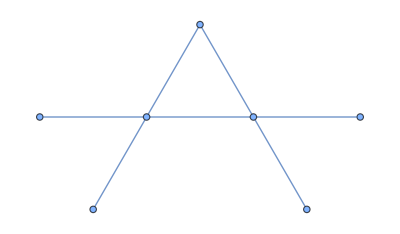

{{-(2 λ)/(2+λ-λ^2)}}

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[638]]
Simplify[Smash[g,{1}]]
```

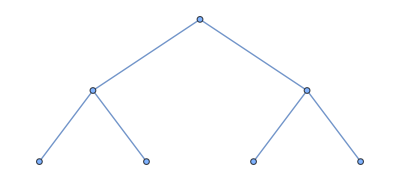

{{λ/(-2+λ^2),1},{1,2/λ}}

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[575]]
Simplify[Smash[g,{1,2}]]
```

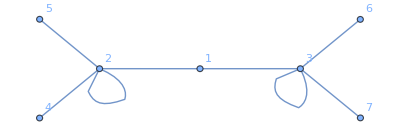

{{-(2 λ)/(2+λ-λ^2)}}

```mathematica
graph=G = Graph[{1<->2, 1<->3,2<->2,2<->4,2<->5,3<->3,3<->6,3<->7}, VertexLabels->"Name"]
Simplify[Smash[graph,{1}]]
```

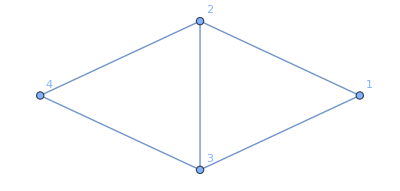

{{λ/(-1+λ^2),λ/(-1+λ)},{λ/(-1+λ),2/(-1+λ)}}

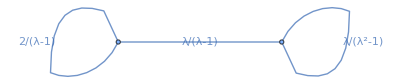

```mathematica
graph=G = Graph[{1<->2,1<->3,2<->3,2<->4,3<->4}, VertexLabels->"Name"]
adjmat=Simplify[Smash[graph,{1,2}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

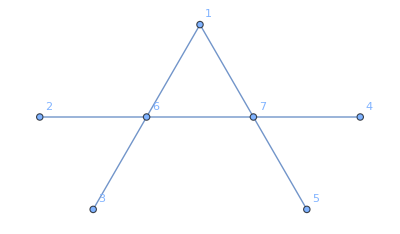

{{λ/(-2+λ^2),(-2+λ+λ^2)/(-2+λ^2)},{(-2+λ+λ^2)/(-2+λ^2),(4-3 λ^2)/(2 λ-λ^3)}}

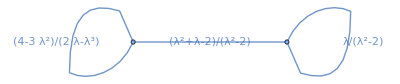

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[638]];
Print[Graph[g,VertexLabels->"Name"]];
adjmat=Simplify[Smash[g,{1,6}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

```mathematica
P4 = Graph[{1<->2,2<->3,3<->4},VertexLabels->Automatic]
A4 = AdjacencyMatrix[P4];
Eigenvalues[A4]
Eigenvectors[A4]
Simplify[Smash[P4,{2}]]
```

-Graphics-

{1/2 (-1-√5),1/2 (1+√5),1/2 (1-√5),1/2 (-1+√5)}

{{-1,1/2 (1+√5),1/2 (-1-√5),1},{1,1/2 (1+√5),1/2 (1+√5),1},{1,1/2 (1-√5),1/2 (1-√5),1},{-1,1/2 (1-√5),1/2 (-1+√5),1}}

{{(1-2 λ^2)/(λ-λ^3)}}

```mathematica
C10 = Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->9,9<->10,10<->1},VertexLabels->Automatic]
A10 = AdjacencyMatrix[C10]
Eigenvalues[A10]
Eigenvectors[A10]
S={1};
Simplify[Smash[C10,S]]
Roots[Det[λ IdentityMatrix[Length[S]]-Simplify[Smash[C10,S]]]==0,λ]
```

-Graphics-

SparseArray[…]

{-2,2,1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),1/2 (-1+√5)}

{{-1,1,-1,1,-1,1,-1,1,-1,1},{1,1,1,1,1,1,1,1,1,1},{1/2 (-1-√5),1/2 (1+√5),-1,0,1,1/2 (-1-√5),1/2 (1+√5),-1,0,1},{-1,1/2 (1+√5),1/2 (-1-√5),1,0,-1,1/2 (1+√5),1/2 (-1-√5),1,0},{1/2 (1+√5),1/2 (1+√5),1,0,-1,1/2 (-1-√5),1/2 (-1-√5),-1,0,1},{-1,1/2 (-1-√5),1/2 (-1-√5),-1,0,1,1/2 (1+√5),1/2 (1+√5),1,0},{1/2 (1-√5),1/2 (1-√5),1,0,-1,1/2 (-1+√5),1/2 (-1+√5),-1,0,1},{-1,1/2 (-1+√5),1/2 (-1+√5),-1,0,1,1/2 (1-√5),1/2 (1-√5),1,0},{1/2 (-1+√5),1/2 (1-√5),-1,0,1,1/2 (-1+√5),1/2 (1-√5),-1,0,1},{-1,1/2 (1-√5),1/2 (-1+√5),1,0,-1,1/2 (1-√5),1/2 (-1+√5),1,0}}

{{(4-8 λ^2+2 λ^4)/(5 λ-5 λ^3+λ^5)}}

λ==1/2 (-1-√5)||λ==1/2 (-1+√5)||λ==1/2 (1-√5)||λ==1/2 (1+√5)||λ==-2||λ==2

## Double Vertex Reduction Matching

```mathematica
data=Flatten@Table[ReductionPowers[n,2],{n,4,8}];
sameReductions=GroupBy[data,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&];
matches=Select[sameReductions,Length[#]>1&];
data // Length (*how many original graphs there are*)
Length[matches]     (*how many unique reductions appear in multiple graphs*)
matches[[1]]
```

40503

8342

{<|n→4,GraphIndex→1,Vertices→{1,2}|>,<|n→4,GraphIndex→1,Vertices→{1,3}|>,<|n→4,GraphIndex→1,Vertices→{2,3}|>}

```mathematica
filteredMatches=Select[
matches,
Module[{group=#,ns,ids},
ns=group[[All,"n"]];
ids=group[[All,"GraphIndex"]];
(Length[DeleteDuplicates[Transpose[{ns,ids}]]]>1)
]&
];
Length[filteredMatches]
```

78

=== Match 1 ===

Reduction matrix:

((2 λ)/(-2+λ^2) | (2 λ)/(-2+λ^2)
(2 λ)/(-2+λ^2) | (2 λ)/(-2+λ^2))

n = 5, GraphIndex = 5, Vertices = {3, 4}

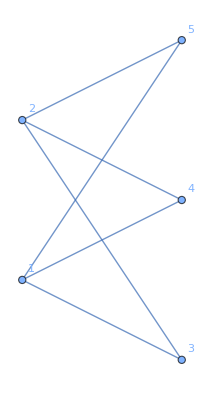

n = 5, GraphIndex = 5, Vertices = {3, 5}

-Graphics-

n = 5, GraphIndex = 5, Vertices = {4, 5}

-Graphics-

n = 8, GraphIndex = 333, Vertices = {2, 3}

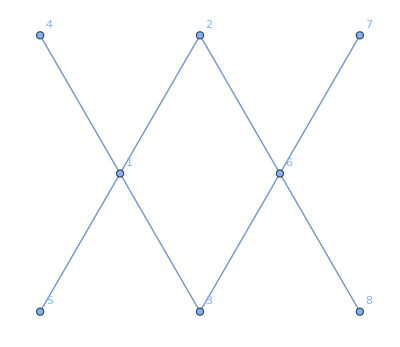

=== Match 2 ===

Reduction matrix:

((-3+2 λ+3 λ^2)/(λ (-2+λ^2)) | (-1+2 λ+2 λ^2)/(λ (-2+λ^2))
(-1+2 λ+2 λ^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

n = 6, GraphIndex = 47, Vertices = {4, 5}

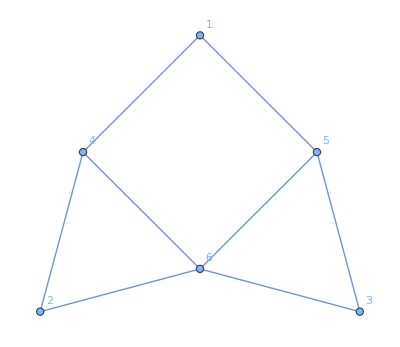

n = 7, GraphIndex = 668, Vertices = {5, 6}

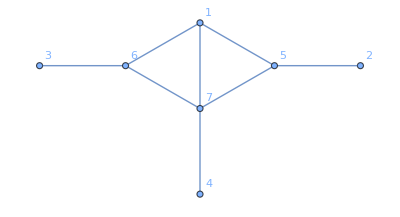

=== Match 3 ===

Reduction matrix:

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

n = 6, GraphIndex = 47, Vertices = {4, 6}

-Graphics-

n = 6, GraphIndex = 47, Vertices = {5, 6}

-Graphics-

n = 7, GraphIndex = 668, Vertices = {5, 7}

-Graphics-

n = 7, GraphIndex = 668, Vertices = {6, 7}

-Graphics-

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[filteredMatches][[i]];(*the shared reduction matrix*)
group=filteredMatches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Min[3,Length[filteredMatches]]}
]
```

## Double Vertex Reduction Examples

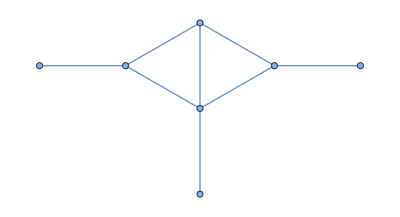

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[668]]
MatrixForm[Simplify[Smash[g,{5,7}]]]
```

## Automorphism Unfolding

```mathematica
graphs=GraphData/@GraphData["Connected",7];
```

-Graphics-

{{2/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ)},{1/(-1+λ),λ/(-1+λ^2),λ/(-1+λ^2),1/(-1+λ^2),1/(-1+λ^2)},{1/(-1+λ),λ/(-1+λ^2),λ/(-1+λ^2),1/(-1+λ^2),1/(-1+λ^2)},{1/(-1+λ),1/(-1+λ^2),1/(-1+λ^2),λ/(-1+λ^2),λ/(-1+λ^2)},{1/(-1+λ),1/(-1+λ^2),1/(-1+λ^2),λ/(-1+λ^2),λ/(-1+λ^2)}}

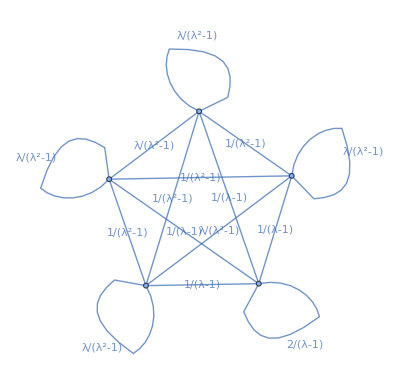

```mathematica
g=graphs[[638]];
Print[Graph[g,VertexLabels->"Name"]];
adjmat=Simplify[Smash[g,{1,2,3,4,5}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{2/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ)},{1/(-1+λ),1/(-1+λ),1/(-1+λ),0,0},{1/(-1+λ),1/(-1+λ),1/(-1+λ),0,0},{1/(-1+λ),0,0,1/(-1+λ),1/(-1+λ)},{1/(-1+λ),0,0,1/(-1+λ),1/(-1+λ)}}

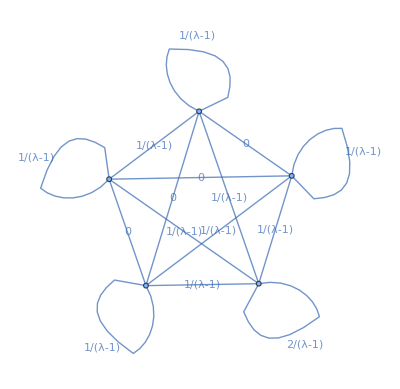

```mathematica
g = Graph[{1<->2, 1<->3,2<->2,2<->4,2<->5,3<->3,3<->6,3<->7}, VertexLabels->"Name"]
adjmat=Simplify[Smash[g,{1,4,5,6,7}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),1/(-2-λ+λ^2),1/(-2-λ+λ^2)},{(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),1/(-2-λ+λ^2),1/(-2-λ+λ^2)},{1/(-2-λ+λ^2),1/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2)},{1/(-2-λ+λ^2),1/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2)}}

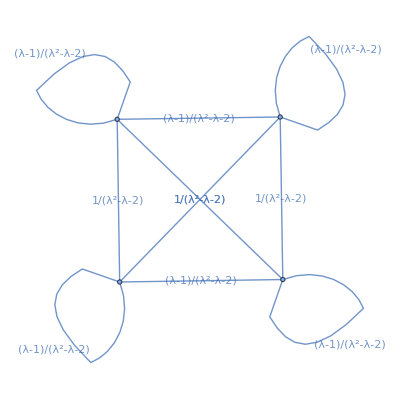

```mathematica
g=graphs[[638]];
Print[Graph[g,VertexLabels->"Name"]];
adjmat=Simplify[Smash[g,{2,3,4,5}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3)},{(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3)},{1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3)},{1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3)}}

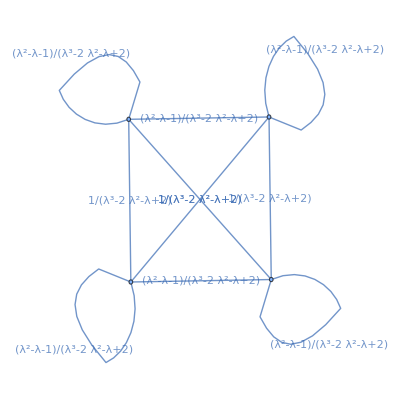

```mathematica
g = Graph[{1<->2, 1<->3,2<->2,2<->4,2<->5,3<->3,3<->6,3<->7}, VertexLabels->"Name"]
adjmat=Simplify[Smash[g,{4,5,6,7}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

```mathematica
Factor[x^3-2 x^2-x+2]
Factor[x^2-x-1]
```

(-2+x) (-1+x) (1+x)

-1-x+x^2

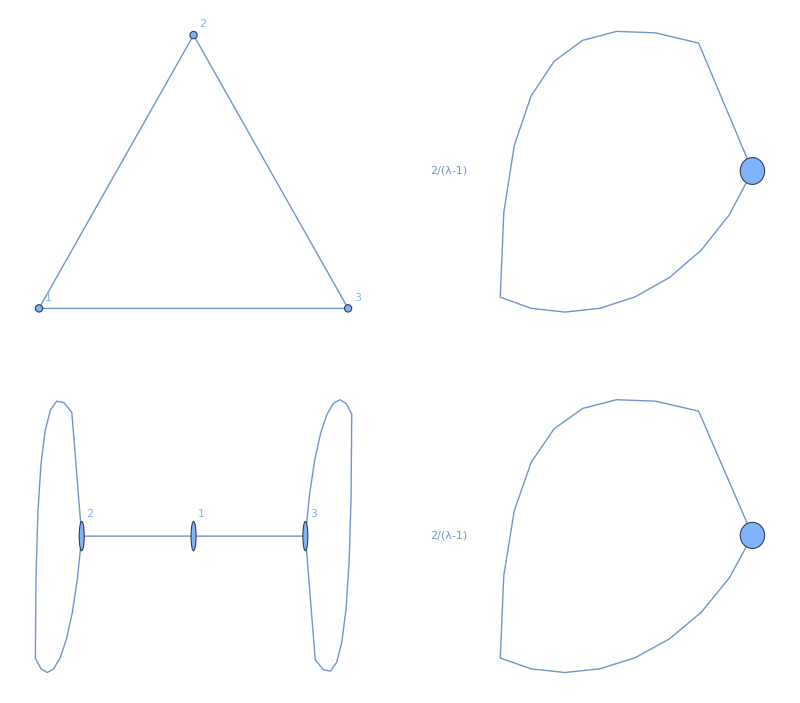

```mathematica
g = Graph[{1<->2, 2<->3,3<->1}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 2<->2,3<->3}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

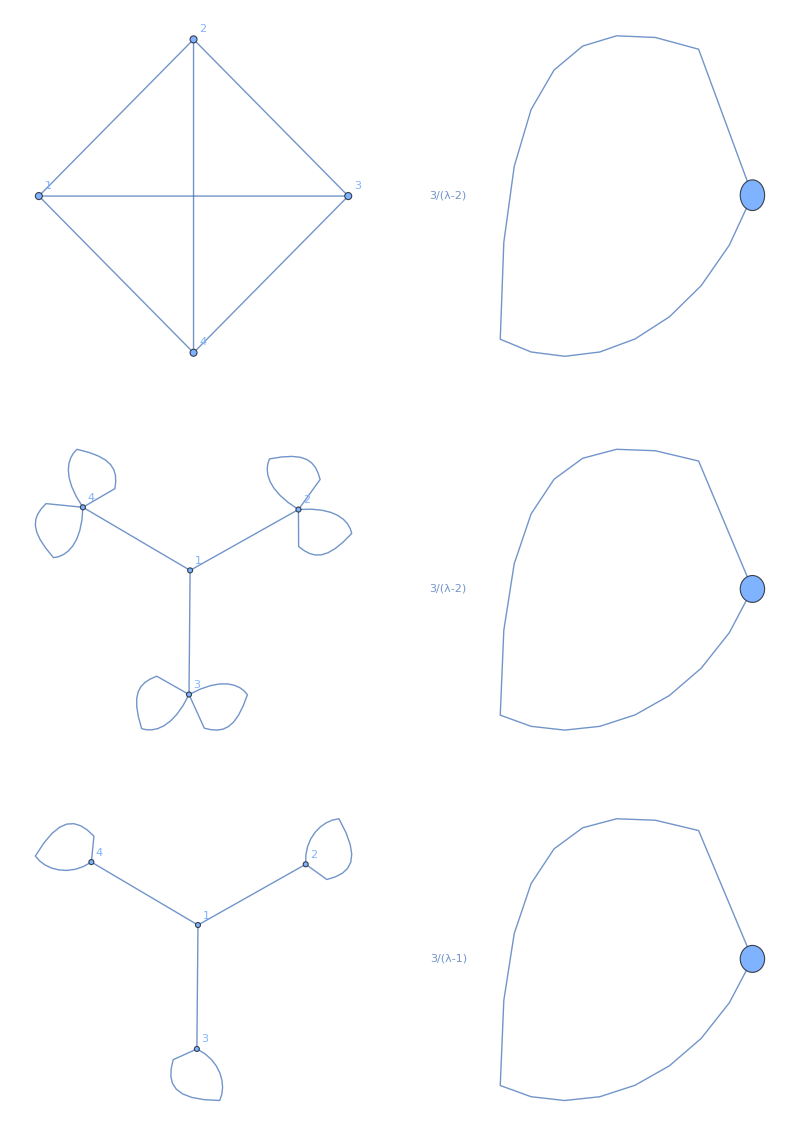

```mathematica
g = Graph[{1<->2, 1<->3,1<->4,2<->3,2<->4,3<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 1<->4,2<->2,2<->2,3<->3,3<->3,4<->4,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG2 = Graph[{1<->2,1<->3, 1<->4,2<->2,3<->3,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG2,{1}]];
compRedGraph2 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph},
{compG2, compRedGraph2}
}
]
```

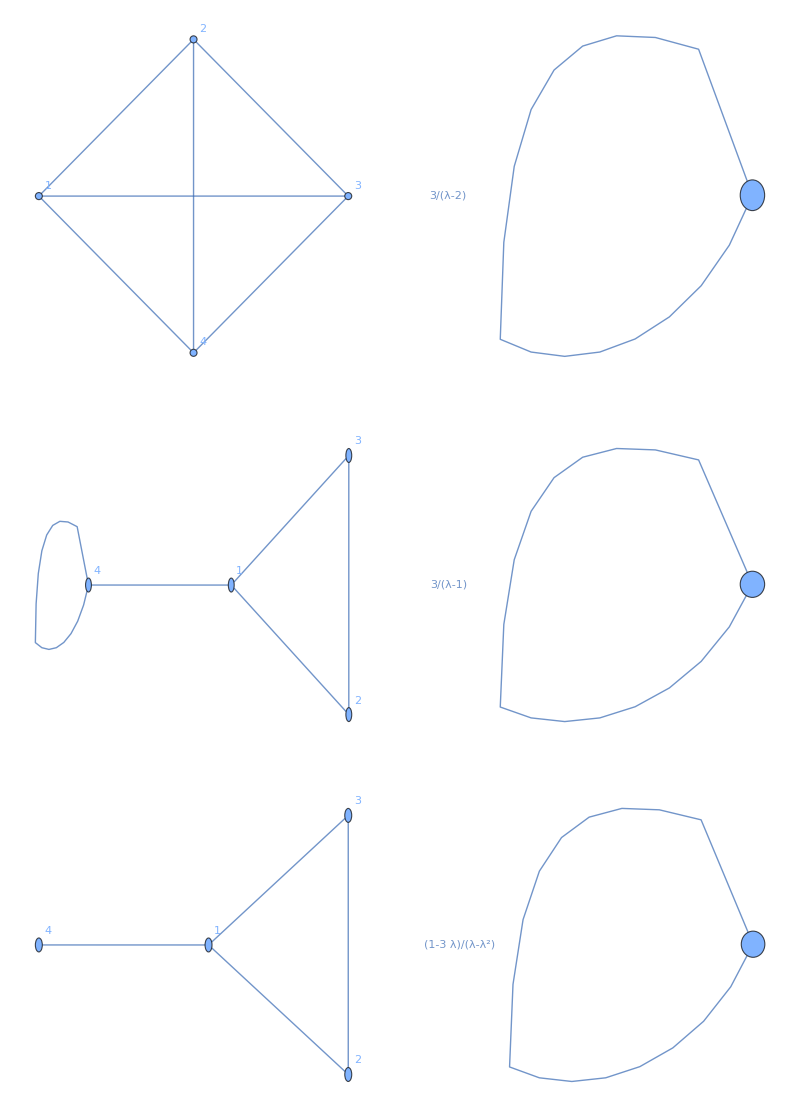

```mathematica
g = Graph[{1<->2, 1<->3,1<->4,2<->3,2<->4,3<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 1<->4,2<->3,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG2 = Graph[{1<->2,1<->3, 1<->4,2<->3}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG2,{1}]];
compRedGraph2 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph},
{compG2, compRedGraph2}
}
]
```

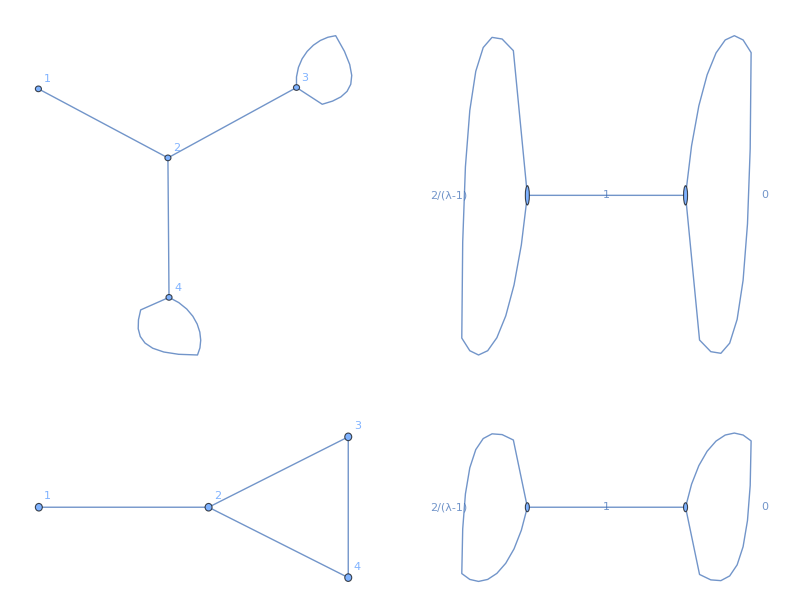

```mathematica
g = Graph[{1<->2,2<->3,2<->4,3<->3,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1,2}]];
redGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,2<->3,3<->4,2<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1,2}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

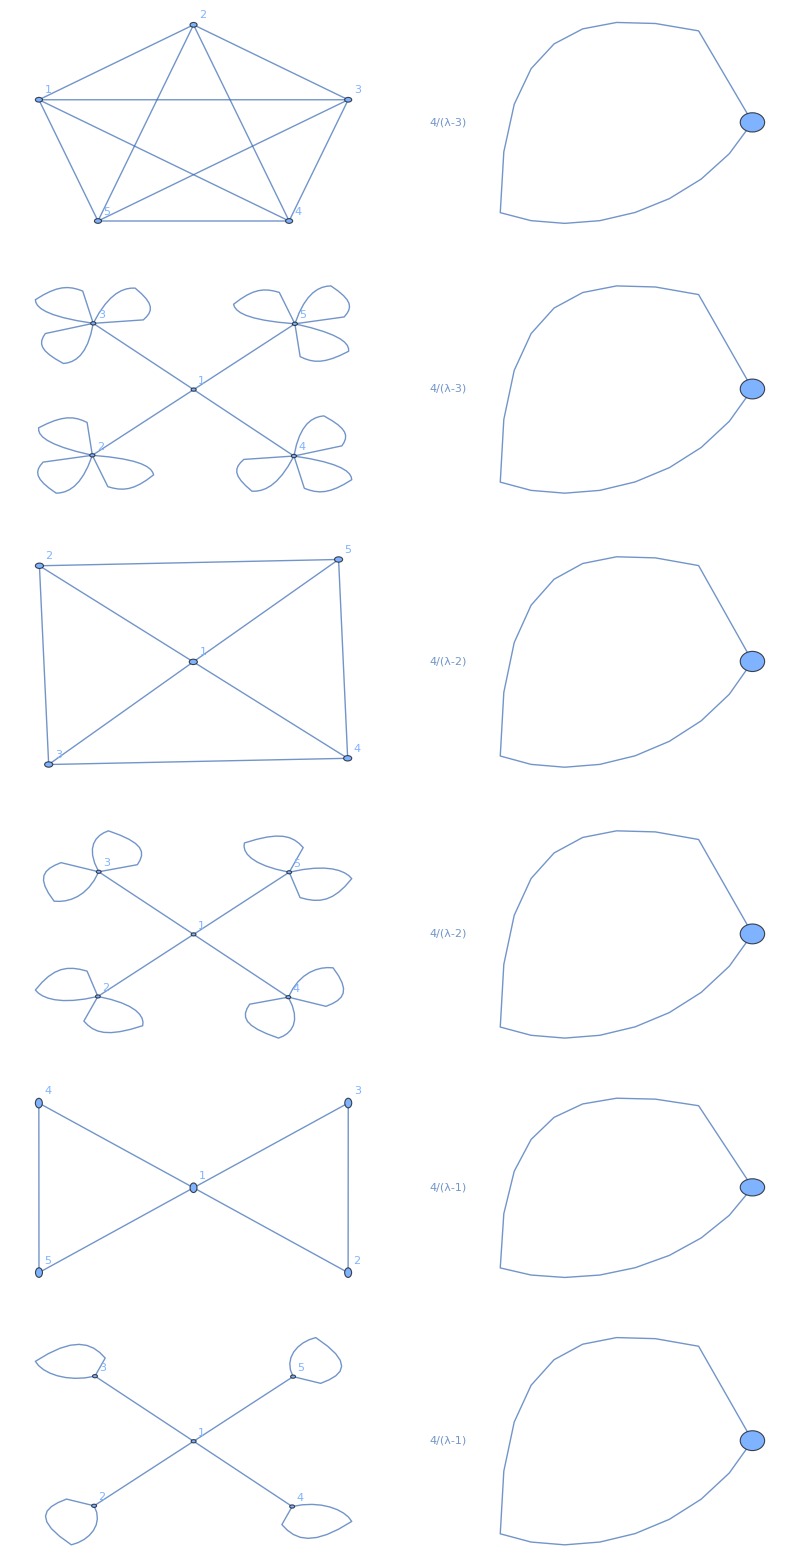

```mathematica
g = Graph[{1<->2, 1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->2,2<->2,2<->2,3<->3,3<->3,3<->3,4<->4,4<->4,4<->4,5<->5,5<->5,5<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG1 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->3,3<->4,4<->5,5<->2}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG1,{1}]];
compRedGraph1 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG2 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->2,2<->2,3<->3,3<->3,4<->4,4<->4,5<->5,5<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG2,{1}]];
compRedGraph2 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG3 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->3,4<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG3,{1}]];
compRedGraph3 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG4 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->2,3<->3,4<->4,5<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG4,{1}]];
compRedGraph4 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];


GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph},
{compG1, compRedGraph1},
{compG2, compRedGraph2},
{compG3, compRedGraph3},
{compG4, compRedGraph4}
}
]
```

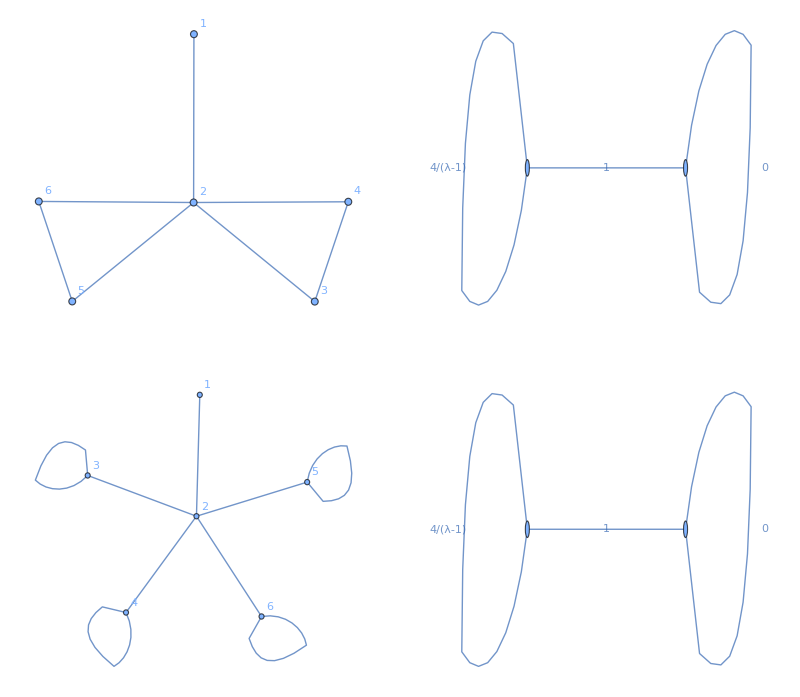

```mathematica
g = Graph[{1<->2,2<->3,3<->4,4<->2,2<->5,5<->6,6<->2}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1,2}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,2<->3,3<->3,4<->4,4<->2,2<->5,5<->5,6<->6,6<->2}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1,2}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

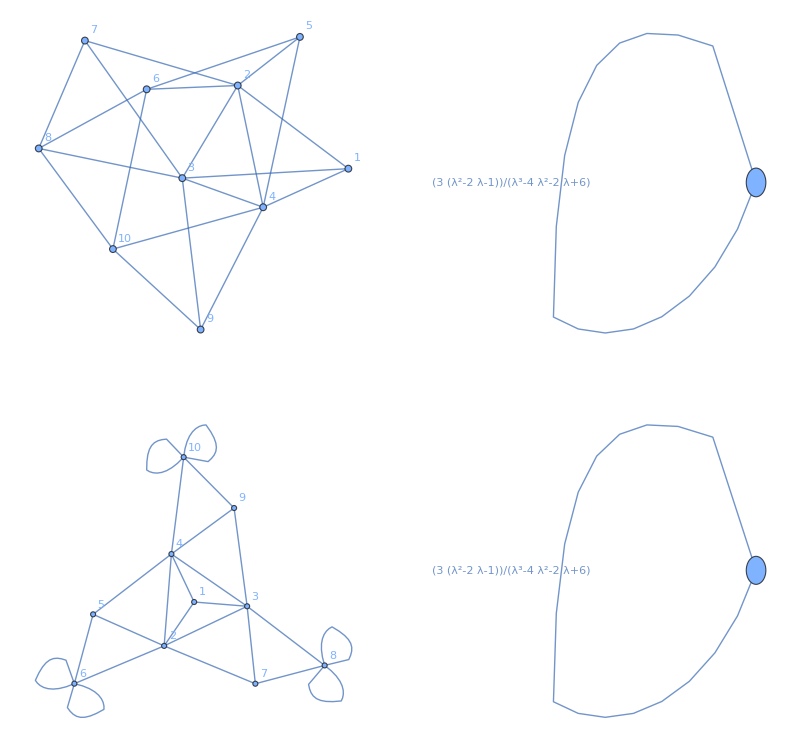

```mathematica
g = Graph[{1<->2,1<->3,1<->4,2<->4,2<->3,3<->4,4<->5,5<->2,2<->6,5<->6,2<->7,3<->7,3<->8,7<->8,4<->9,3<->9,10<->4,10<->9,8<->6,10<->8,10<->6}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3,1<->4,2<->4,2<->3,3<->4,4<->5,5<->2,2<->6,5<->6,6<->6,2<->7,3<->7,3<->8,7<->8,8<->8,4<->9,3<->9,10<->4,10<->9,10<->10,10<->10,6<->6,8<->8}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

## Single Vertex Reduction Matching Given Examples

```mathematica
data=Flatten@Table[ReductionPowers[n,1],{n,4,12}];
```

```mathematica
target = (λ-1)/λ;
matches = Select[
data,
Simplify[First[Flatten[#Reduction]]==target] &
]
Length[matches]
```

{}

0

```mathematica
graphs=GraphData/@GraphData["Connected",5];
Print[Graph[graphs[[21]],VertexLabels->"Name"]];
```

-Graphics-

```mathematica
matches = Select[
data,
#n==4 &
]
Length[matches]
```

{<|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→1,Vertices→{2},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→1,Vertices→{3},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→1,Vertices→{4},Reduction→{{3/λ}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→2,Vertices→{1},Reduction→{{-(2 λ)/(2+λ-λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→2,Vertices→{2},Reduction→{{-(2 λ)/(2+λ-λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→2,Vertices→{3},Reduction→{{(4+3 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→2,Vertices→{4},Reduction→{{(4+3 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→3,Vertices→{1},Reduction→{{(-1+λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→3,Vertices→{2},Reduction→{{(1-2 λ^2)/(λ-λ^3)}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→3,Vertices→{3},Reduction→{{(1-2 λ^2)/(λ-λ^3)}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→3,Vertices→{4},Reduction→{{(-1+λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→4,Vertices→{1},Reduction→{{(-1+2 λ+2 λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→4,Vertices→{2},Reduction→{{(-1+2 λ+2 λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→4,Vertices→{3},Reduction→{{(1-3 λ)/(λ-λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→4,Vertices→{4},Reduction→{{(-1+λ)/(-2-λ+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{1},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{2},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{3},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{4},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→6,Vertices→{1},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→6,Vertices→{2},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→6,Vertices→{3},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→6,Vertices→{4},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>}

24

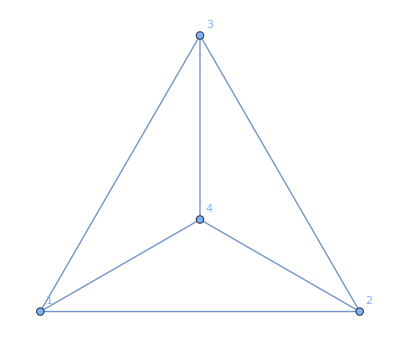

```mathematica
graphs=GraphData/@GraphData["Connected",4];
Print[Graph[graphs[[6]],VertexLabels->"Name"]];
```

## Automorphism Proof Work

```mathematica
g=Graph[{1<->2,2<->3,3<->5,5<->4,4<->1},VertexLabels->"Name"];
g1 = Graph[{1<->2,2<->3,3<->5,5<->4,4<->1,2<->2,4<->4},VertexLabels->"Name"];
g2 = Graph[{1<->2,2<->3,3<->5,5<->4,4<->1,2<->4},VertexLabels->"Name"];

GraphicsRow[{
Labeled[g,"g",Top],
Labeled[g1,"g1",Top],
Labeled[g2,"g2",Top]
}]
```

-Graphics-

```mathematica
g1A = {{0,1,0,1,0},{1,1,1,0,0},{0,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0}}
g2A = {{0,1,0,1,0},{1,0,1,1,0},{0,1,0,0,1},{1,1,0,0,1},{0,0,1,1,0}}

split=1; (*Vertex to split on*)

g1m11=g1A[[1;;split,1;;split]]
g1m12=g1A[[1;;split,split+1;;]]
g1m21=g1A[[split+1;;,1;;split]]
g1m22=g1A[[split+1;;,split+1;;]]
s = Length[m22]

Simplify[g1m11 + g1m12.Inverse[λ IdentityMatrix[s] - g1m22].g1m21]

g2m11=g2A[[1;;split,1;;split]]
g2m12=g2A[[1;;split,split+1;;]]
g2m21=g2A[[split+1;;,1;;split]]
g2m22=g2A[[split+1;;,split+1;;]]
s = Length[m22]

Simplify[g2m11 +g2m12.Inverse[λ IdentityMatrix[s] - g2m22].g2m21]
```

{{0,1,0,1,0},{1,1,1,0,0},{0,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0}}

{{0,1,0,1,0},{1,0,1,1,0},{0,1,0,0,1},{1,1,0,0,1},{0,0,1,1,0}}

{{0}}

{{1,0,1,0}}

{{1},{0},{1},{0}}

{{1,1,0,0},{1,0,0,1},{0,0,1,1},{0,1,1,0}}

4

{{(2 (-1+λ))/((-2+λ) λ)}}

{{0}}

{{1,0,1,0}}

{{1},{0},{1},{0}}

{{0,1,1,0},{1,0,0,1},{1,0,0,1},{0,1,1,0}}

4

{{(2 (-1+λ))/((-2+λ) λ)}}

```mathematica
Row[{MatrixForm[g1m22],Spacer[20],MatrixForm[g2m22]}]
Row[{MatrixForm[λ IdentityMatrix[s] - g1m22],Spacer[20],MatrixForm[λ IdentityMatrix[s] - g2m22]}]
g1mInv = Simplify[Inverse[λ IdentityMatrix[s] - g1m22]];
g2mInv = Simplify[Inverse[λ IdentityMatrix[s] - g2m22]];
Row[{MatrixForm[g1mInv],Spacer[20],MatrixForm[g2mInv]}]

g1m12
g2m12
Simplify[g1m12.g1mInv]
Simplify[g2m12.g2mInv]

g1m21
g2m21
Simplify[g1mInv.g1m21]
Simplify[g2mInv.g1m21]
```

(1 | 1 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 1 | 0)(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

(-1+λ | -1 | 0 | 0
-1 | λ | 0 | -1
0 | 0 | -1+λ | -1
0 | -1 | -1 | λ)(λ | -1 | -1 | 0
-1 | λ | 0 | -1
-1 | 0 | λ | -1
0 | -1 | -1 | λ)

((1-2 λ-λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3)) | 1/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1+λ)/(λ (4-2 λ-2 λ^2+λ^3))
(-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3)) | (1-2 λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1+λ)/(λ (4-2 λ-2 λ^2+λ^3)) | (-1+λ)^2/(λ (4-2 λ-2 λ^2+λ^3))
1/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1+λ)/(λ (4-2 λ-2 λ^2+λ^3)) | (1-2 λ-λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3))
(-1+λ)/(λ (4-2 λ-2 λ^2+λ^3)) | (-1+λ)^2/(λ (4-2 λ-2 λ^2+λ^3)) | (-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3)) | (1-2 λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4))((-2+λ^2)/(-4 λ+λ^3) | 1/(-4+λ^2) | 1/(-4+λ^2) | 2/(-4 λ+λ^3)
1/(-4+λ^2) | (-2+λ^2)/(-4 λ+λ^3) | 2/(-4 λ+λ^3) | 1/(-4+λ^2)
1/(-4+λ^2) | 2/(-4 λ+λ^3) | (-2+λ^2)/(-4 λ+λ^3) | 1/(-4+λ^2)
2/(-4 λ+λ^3) | 1/(-4+λ^2) | 1/(-4+λ^2) | (-2+λ^2)/(-4 λ+λ^3))

{{1,0,1,0}}

{{1,0,1,0}}

{{(-1+λ)/((-2+λ) λ),1/((-2+λ) λ),(-1+λ)/((-2+λ) λ),1/((-2+λ) λ)}}

{{(-1+λ)/((-2+λ) λ),1/((-2+λ) λ),(-1+λ)/((-2+λ) λ),1/((-2+λ) λ)}}

{{1},{0},{1},{0}}

{{1},{0},{1},{0}}

{{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)},{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)}}

{{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)},{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)}}

```mathematica
P={{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0},{0,0,1,0,0}}
MatrixForm[P]
MatrixForm[Transpose[P].g1A.P]==MatrixForm[g1A]
Row[{MatrixForm[g1A],Spacer[20],MatrixForm[g2A]}]
Row[{MatrixForm[g1A[[2;;,2;;]]],Spacer[20],MatrixForm[g2A[[2;;,2;;]]]}]
Row[{MatrixForm[(g2A.P)[[2;;,2;;]]],Spacer[20],MatrixForm[(g1A.P)[[2;;,2;;]]]}]
```

{{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0},{0,0,1,0,0}}

(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

True

(0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0)(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

(1 | 1 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 1 | 0)(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

(1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 1 | 1 | 0
1 | 0 | 0 | 1)(0 | 0 | 1 | 1
0 | 1 | 1 | 0
1 | 1 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
i=3;
Row[{MatrixForm[g1m12],Spacer[20],MatrixForm[g2m12]}]
Row[{MatrixForm[MatrixPower[g1m22,i]],Spacer[20],MatrixForm[MatrixPower[g2m22,i]]}]
Row[{MatrixForm[g1m12.MatrixPower[g1m22,i]],MatrixForm[g2m12.MatrixPower[g2m22,i]]}]
Row[{MatrixForm[g1m12.MatrixPower[g1m22,i].g1m21],MatrixForm[g2m12.MatrixPower[g2m22,i].g2m21]}]
```

(1 | 0 | 1 | 0)(1 | 0 | 1 | 0)

(3 | 3 | 1 | 1
3 | 1 | 1 | 3
1 | 1 | 3 | 3
1 | 3 | 3 | 1)(0 | 4 | 4 | 0
4 | 0 | 0 | 4
4 | 0 | 0 | 4
0 | 4 | 4 | 0)

(4 | 4 | 4 | 4)(4 | 4 | 4 | 4)

(8)(8)

```mathematica
t1A = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,1,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,0}
};
t2A = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,1,0},
{0,0,0,1,0,1,0,1,0,0},
{0,1,0,0,0,0,1,0,0,0}
};
t3A = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,-1,2,0},
{0,0,0,1,0,1,0,2,-1,0},
{0,1,0,0,0,0,1,0,0,0}
};
T1A = AdjacencyGraph[t1A,VertexLabels->Automatic];
T2A = AdjacencyGraph[t2A,VertexLabels->Automatic];
T3A = WeightedAdjacencyGraph[t3A,VertexLabels->Automatic];
GraphicsRow[{T1A, T2A}]
Simplify[Smash[T1A, {1}]]
Simplify[Smash[T2A, {1}]]
Simplify[SmashAdj[t3A, T3A, {1}]]
```

-Graphics-

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

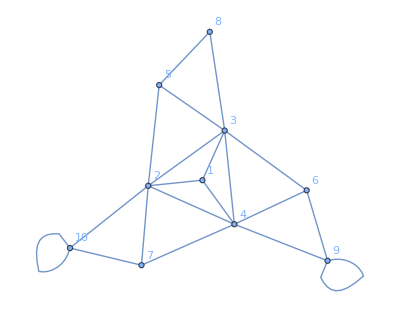

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(-15+8 λ-37 λ^3+18 λ^4-7 λ^5+12 λ^6-6 λ^7+3 λ^8)/(6-26 λ+24 λ^2-22 λ^3-25 λ^4-8 λ^5-5 λ^6+3 λ^7-4 λ^8+λ^9)}}

{{(-5+11 λ-25 λ^2-36 λ^3+32 λ^4-10 λ^5+9 λ^6-3 λ^7+3 λ^8)/(2-12 λ+24 λ^2-50 λ^3-32 λ^4-λ^5-9 λ^6-3 λ^8+λ^9)}}

```mathematica
P={
{1,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,1,0,0}
};
AdjacencyGraph[Transpose[P].t1A.P,VertexLabels->Automatic]

Simplify[t2m11 +t2m12.Inverse[λ IdentityMatrix[s] - t2m22].t2m21]
Simplify[t1m11 + t1m12.Inverse[λ IdentityMatrix[s] - t1m22].t1m21]

split=1; (*Vertex to split on*)

t1m11P=(t1A.Transpose[P])[[1;;split,1;;split]];
t1m12P=(t1A.Transpose[P])[[1;;split,split+1;;]];
t1m21P=(t1A.Transpose[P])[[split+1;;,1;;split]];
t1m22P=(t1A.Transpose[P])[[split+1;;,split+1;;]];
s = Length[t1m22];

t2m11P=(t2A.Transpose[P])[[1;;split,1;;split]];
t2m12P=(t2A.Transpose[P])[[1;;split,split+1;;]];
t2m21=(t2A.Transpose[P])[[split+1;;,1;;split]];
t2m22P=(t2A.Transpose[P])[[split+1;;,split+1;;]];
s = Length[t2m22];

Simplify[t2m11P +t2m12P.Inverse[λ IdentityMatrix[s] - t2m22P].t2m21]
Simplify[t1m11P + t1m12P.Inverse[λ IdentityMatrix[s] - t1m22P].t1m21]
```

```mathematica
i=1;
Row[{MatrixForm[t1m12],Spacer[20],MatrixForm[t2m12]}]
Row[{MatrixForm[MatrixPower[t1m22,i]],Spacer[20],MatrixForm[MatrixPower[t2m22,i]]}]
Row[{MatrixForm[t1m12.MatrixPower[t1m22,i]],MatrixForm[t2m12.MatrixPower[t2m22,i]]}]
Row[{MatrixForm[t1m12.MatrixPower[t1m22,i].t1m21],MatrixForm[t2m12.MatrixPower[t2m22,i].t2m21]}]
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1)(2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1)

(6)(6)

```mathematica
MatrixForm[Transpose[P].Transpose[P].Transpose[P].t1A.P.P.P]==MatrixForm[t1A]
Row[{MatrixForm[t1A],Spacer[20],MatrixForm[t2A]}]
Row[{MatrixForm[t1A[[2;;,2;;]]],Spacer[20],MatrixForm[t2A[[2;;,2;;]]]}]
Row[{MatrixForm[(t2A.P)[[2;;,2;;]]],Spacer[20],MatrixForm[(t1A.P)[[2;;,2;;]]]}]



Simplify[t2m11 +t2m12.Inverse[λ IdentityMatrix[s] - t2m22].t2m21]
Simplify[t2m11 +t2m12.Inverse[λ IdentityMatrix[s] - t2m22].t2m21]
```

True

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0)(1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

```mathematica
M={{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}}
{U,V}=ResourceFunction["FullRankDecomposition"][M]
M==U.V
Row[{MatrixForm[U], MatrixForm[V]}]
```

{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}}

{{{0,0},{1,0},{0,1},{0,0}},{{0,1,0,0},{0,0,1,0}}}

True

(0 | 0
1 | 0
0 | 1
0 | 0)(0 | 1 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
M={{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}}
{U,V}=ResourceFunction["FullRankDecomposition"][M]
M==U.V
Row[{MatrixForm[U], MatrixForm[V]}]
```

{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}}

{{{0,0},{0,1},{1,0},{0,0}},{{0,1,0,0},{0,0,1,0}}}

True

(0 | 0
0 | 1
1 | 0
0 | 0)(0 | 1 | 0 | 0
0 | 0 | 1 | 0)

### Eigensystem of M_(Sbar,Sbar)

```mathematica
Mat1={{-l,0,1,0},{0,-l,0,1},{1,0,1-l,0},{0,1,0,1-l}}
Mat1Inv=Inverse[Mat1]

Mat2={{-l,0,1,0},{0,-l,0,1},{1,0,-l,1},{0,1,1,-l}}
Mat2Inv=Inverse[Mat2]

Simplify[{{1,1,0,0}}.Mat1Inv]
Simplify[{{1,1,0,0}}.Mat2Inv]
```

{{-l,0,1,0},{0,-l,0,1},{1,0,1-l,0},{0,1,0,1-l}}

{{(1-l)/(-1-l+l^2),0,-1/(-1-l+l^2),0},{0,(1-l)/(-1-l+l^2),0,-1/(-1-l+l^2)},{-1/(-1-l+l^2),0,-l/(-1-l+l^2),0},{0,-1/(-1-l+l^2),0,-l/(-1-l+l^2)}}

{{-l,0,1,0},{0,-l,0,1},{1,0,-l,1},{0,1,1,-l}}

{{(2 l-l^3)/(1-3 l^2+l^4),-1/(1-3 l^2+l^4),(1-l^2)/(1-3 l^2+l^4),-l/(1-3 l^2+l^4)},{-1/(1-3 l^2+l^4),(2 l-l^3)/(1-3 l^2+l^4),-l/(1-3 l^2+l^4),(1-l^2)/(1-3 l^2+l^4)},{(1-l^2)/(1-3 l^2+l^4),-l/(1-3 l^2+l^4),(l-l^3)/(1-3 l^2+l^4),-l^2/(1-3 l^2+l^4)},{-l/(1-3 l^2+l^4),(1-l^2)/(1-3 l^2+l^4),-l^2/(1-3 l^2+l^4),(l-l^3)/(1-3 l^2+l^4)}}

{{(1-l)/(-1-l+l^2),(1-l)/(-1-l+l^2),1/(1+l-l^2),1/(1+l-l^2)}}

{{(1-l)/(-1-l+l^2),(1-l)/(-1-l+l^2),1/(1+l-l^2),1/(1+l-l^2)}}

(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

{{2,2,1},{2,2,1},{2,2,1},{2,0,1},{2,0,1},{2,0,1},{1,1,0},{1,1,0},{1,1,0}}

{,,,,,,1,1,1}

{,,,,,,1,1,1}

{,-2,-2,1/2 (1+√5),1/2 (1+√5),,1/2 (1-√5),1/2 (1-√5),}

{,,}

{{2,2,1},{2,2,1},{2,2,1},{2,0,1},{2,0,1},{2,0,1},{1,1,0},{1,1,0},{1,1,0}}

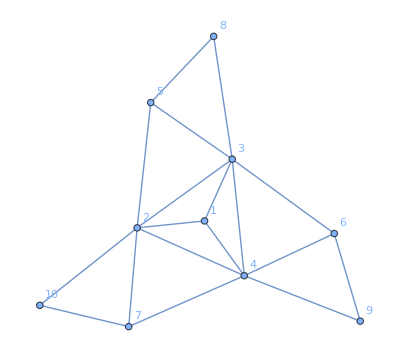

```mathematica
P={
{1,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,1,0,0}
};
A = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,0,0},
{0,1,0,0,0,0,1,0,0,0}
};
autA = A[[2;;,2;;]];
MatrixForm[autA]
S={{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1}};
B={{2,2,1},{2,0,1},{1,1,0}};
S.B
S.Eigenvectors[B][[1]]
Eigenvectors[autA][[1]]
Eigenvalues[autA]
Eigenvalues[B]
autA.S
AdjacencyGraph[A,VertexLabels->Automatic]
```

{{,,,,,,,,1,1},{0,,,,,,,0,-1,1},{,,,,,,,,1,1},{0,,,,,,,0,-1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{0,,,,,,,0,-1,1}}

{{,,,,,,,,1,1},{0,-(23-5 √13)/(2 (-7+3 √13)),-1/2,-(-8+√13)/(-7+3 √13),-(2 (-89+26 √13))/((-7+3 √13) (-23+5 √13)),-(-15+4 √13)/(-7+3 √13),-(23-5 √13)/(2 (-7+3 √13)),0,-1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{0,-(-23-5 √13)/(2 (7+3 √13)),-1/2,-(8+√13)/(7+3 √13),(2 (89+26 √13))/((7+3 √13) (23+5 √13)),-(15+4 √13)/(7+3 √13),-(-23-5 √13)/(2 (7+3 √13)),0,-1,1},{0,0,1,-1,-1,1,0,0,-1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1}}

{,,,,,,,,}

{,1/2 (-1-√13),,,,1/2 (-1+√13),-1,,}

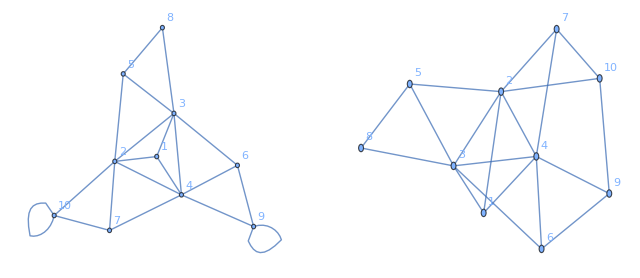

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{,,,,,,,,,}

{,1/2 (-1-√13),,,,1/2 (-1+√13),-1,,,}

{{λ→},{λ→},{λ→},{λ→},{λ→},{λ→},{λ→}}

{{λ→},{λ→},{λ→},{λ→},{λ→},{λ→},{λ→}}

```mathematica
P={
{1,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,1,0,0}
};
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,0,1},
{0,1,0,0,0,0,1,0,1,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[autA1]
Eigenvalues[autA2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Eigenvalues[A1]
Eigenvalues[A2]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

```mathematica
autAL = autA - λ IdentityMatrix[Length[autA]];
MatrixForm[autAL]
S={{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1}};
B={{2-λ,2,1},{2,-λ,1},{1,1,-λ}};
S.Eigenvectors[B][[1]]
Eigenvectors[autAL][[1]]
Eigenvalues[autAL][[1]]
S.B
autAL.S
AdjacencyGraph[A,VertexLabels->Automatic]
```

(-λ | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | -λ | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | -λ | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | -λ | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | -λ | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | -λ | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | -λ | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | -λ | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -λ)

{-(-1-2 λ-2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1])/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(-1-2 λ-2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1])/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(-1-2 λ-2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1])/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(1+2 λ-λ^2+2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-2 λ Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]^2)/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(1+2 λ-λ^2+2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-2 λ Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]^2)/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(1+2 λ-λ^2+2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-2 λ Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]^2)/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),1,1,1}

{1/2,-(-11+5 √5)/(2 (-7+3 √5)),-(2-√5)/(-7+3 √5),1/4 (-1+√5),-(-2+√5)/(-7+3 √5),-(15-7 √5)/(2 (-7+3 √5)),-1,0,1}

1/2 (1-√5-2 λ)

{{2-λ,2,1},{2-λ,2,1},{2-λ,2,1},{2,-λ,1},{2,-λ,1},{2,-λ,1},{1,1,-λ},{1,1,-λ},{1,1,-λ}}

{{2-λ,2,1},{2-λ,2,1},{2-λ,2,1},{2,-λ,1},{2,-λ,1},{2,-λ,1},{1,1,-λ},{1,1,-λ},{1,1,-λ}}

-Graphics-

{{1,1,1,1,1},{1/2 (1+√5),-1,1/2 (-1-√5),0,1},{1/2 (1+√5),1/2 (-1-√5),-1,1,0},{1/2 (1-√5),-1,1/2 (-1+√5),0,1},{1/2 (1-√5),1/2 (-1+√5),-1,1,0}}

{{1,1,1,1,1},{1+√5,1/2 (-3-√5),1/2 (-3-√5),1,1},{0,1/2 (1-√5),1/2 (-1+√5),-1,1},{0,1/2 (1+√5),1/2 (-1-√5),-1,1},{1-√5,1/2 (-3+√5),1/2 (-3+√5),1,1}}

{2,1/2 (-1-√5),1/2 (-1-√5),1/2 (-1+√5),1/2 (-1+√5)}

{2,1/2 (-1-√5),1/2 (1+√5),1/2 (1-√5),1/2 (-1+√5)}

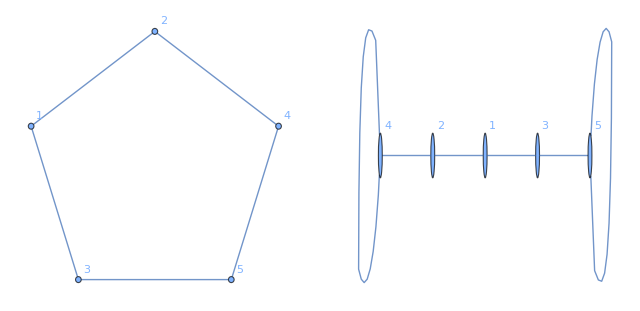

{{(2-2 λ)/(1+λ-λ^2)}}

{{(2-2 λ)/(1+λ-λ^2)}}

{{λ→2},{λ→1/2 (-1-√5)},{λ→1/2 (-1+√5)}}

{{λ→2},{λ→1/2 (-1-√5)},{λ→1/2 (-1+√5)}}

```mathematica
A1 = {
{0,1,1,0,0},
{1,0,0,1,0},
{1,0,0,0,1},
{0,1,0,0,1},
{0,0,1,1,0}
};
A2 = {
{0,1,1,0,0},
{1,0,0,1,0},
{1,0,0,0,1},
{0,1,0,1,0},
{0,0,1,0,1}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{1,1,1,1,1,1,1},{,,,,,1,1},{0,,,,,-1,1},{0,,,,,-1,1},{,,,,,1,1},{,,,,,1,1},{0,,,,,-1,1}}

{{1,1,1,1,1,1,1},{,,,-1,,0,1},{,,,,-1,1,0},{,,,-1,,0,1},{,,,,-1,1,0},{,,,-1,,0,1},{,,,,-1,1,0}}

{2,,,,,,}

{2,,,,,,}

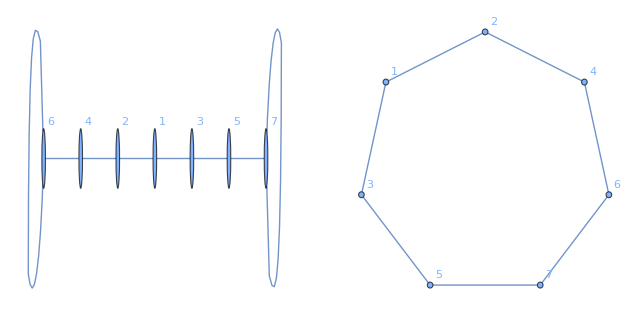

{{(2 (-1-λ+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{(2 (-1-λ+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{λ→2},{λ→},{λ→},{λ→}}

{{λ→2},{λ→},{λ→},{λ→}}

```mathematica
A1 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,1,0},
{0,0,0,0,1,0,1}
};
A2 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,0,1},
{0,0,0,0,1,1,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{,,,,,1,1},{0,-1,1,2,-2,-1,1},{,,,,,1,1},{-1,-1,0,0,1,0,1},{-1,0,-1,1,0,1,0},{,,,,,1,1},{0,1,-1,0,0,-1,1}}

{{,,,,,1,1},{0,-1,1,-2,2,-1,1},{,,,,,1,1},{0,-1,1,1,-1,-1,1},{-2,-1,-1,1,1,1,1},{,,,,,1,1},{0,1,-1,0,0,-1,1}}

{,-2,,1,1,,0}

{,2,,-1,1,,0}

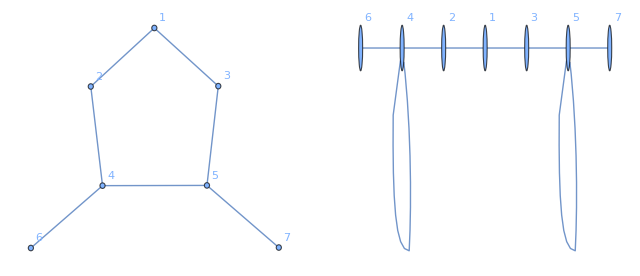

{{(2+2 λ-2 λ^2)/(2 λ+λ^2-λ^3)}}

{{(2+2 λ-2 λ^2)/(2 λ+λ^2-λ^3)}}

{{λ→1},{λ→},{λ→},{λ→}}

{{λ→1},{λ→},{λ→},{λ→}}

```mathematica
A1 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,0,1,1,0},
{0,0,1,1,0,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
A2 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,1,0,1,0},
{0,0,1,0,1,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

```mathematica
A1 = {
{0,1,1,0,0,0,0},
{1,1,0,1,0,0,0},
{1,0,1,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
A2 = {
{0,1,1,0,0,0,0},
{1,0,1,1,0,0,0},
{1,1,0,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{,,,,,1,1},{0,,,,,-1,1}}

{{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{,,,,,1,1},{0,,,,,-1,1}}

{,,,,,,}

{,,,,,,}

-Graphics-

{{(2 (-1+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{(2 (-1+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{λ→},{λ→},{λ→},{λ→}}

{{λ→},{λ→},{λ→},{λ→}}

{{1,1,1,1,1,1,1,1,1},{,,,,,-1,,0,1},{,,,,,,-1,1,0},{,,,,,-1,,0,1},{,,,,,,-1,1,0},{-1,0,1,1,0,-1,-1,0,1},{-1,1,0,0,1,-1,-1,1,0},{,,,,,-1,,0,1},{,,,,,,-1,1,0}}

{{1,1,1,1,1,1,1,1,1},{,,,,,,,1,1},{0,,,,,,,-1,1},{0,,,,,,,-1,1},{,,,,,,,1,1},{-2,1,1,1,1,-2,-2,1,1},{0,1,-1,1,-1,0,0,-1,1},{0,,,,,,,-1,1},{,,,,,,,1,1}}

{2,,,,,-1,-1,,}

{2,,,,,-1,1,,}

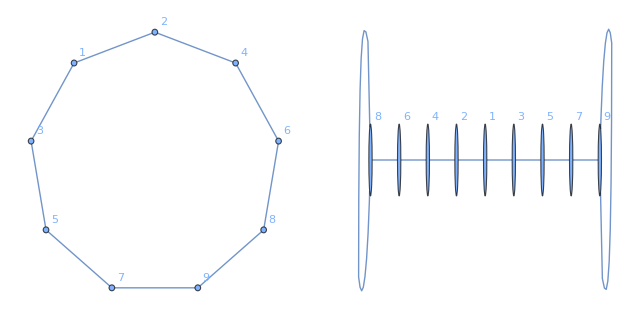

{{(2 (1-2 λ-λ^2+λ^3))/(1+2 λ-3 λ^2-λ^3+λ^4)}}

{{(2 (1-2 λ-λ^2+λ^3))/(1+2 λ-3 λ^2-λ^3+λ^4)}}

{{λ→-1},{λ→2},{λ→},{λ→},{λ→}}

{{λ→-1},{λ→2},{λ→},{λ→},{λ→}}

```mathematica
A1 = {
{0,1,1,0,0,0,0,0,0},
{1,0,0,1,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0},
{0,1,0,0,0,1,0,0,0},
{0,0,1,0,0,0,1,0,0},
{0,0,0,1,0,0,0,1,0},
{0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,1,0,0,1},
{0,0,0,0,0,0,1,1,0}
};
A2 = {
{0,1,1,0,0,0,0,0,0},
{1,0,0,1,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0},
{0,1,0,0,0,1,0,0,0},
{0,0,1,0,0,0,1,0,0},
{0,0,0,1,0,0,0,1,0},
{0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,1,0,1,0},
{0,0,0,0,0,0,1,0,1}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{,,1,1},{,,1,1},{0,0,-1,1},{,,1,1}}

{{,,1,1},{,,1,1},{0,0,-1,1},{,,1,1}}

{,,1,}

{,,-1,}

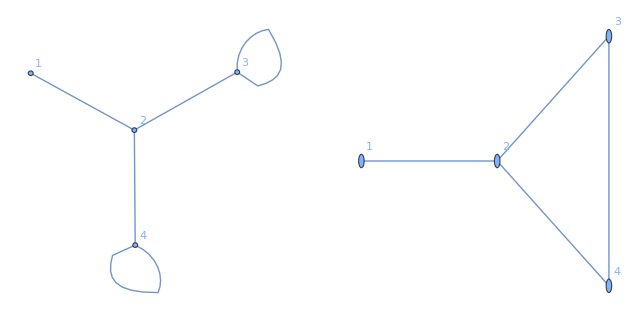

{{0,1},{1,2/(-1+λ)}}

{{0,1},{1,2/(-1+λ)}}

{}

{}

```mathematica
A1 = {
{0,1,0,0},
{1,0,1,1},
{0,1,1,0},
{0,1,0,1}
};
A2 = {
{0,1,0,0},
{1,0,1,1},
{0,1,0,1},
{0,1,1,0}
};
autA1 = A1[[3;;,3;;]];
autA2 = A2[[3;;,3;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1,2}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1,2}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1,2}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1,2}]]==0,λ]
```

(1 | 1 | 0 | 0
0 | 1 | 1 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0)

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1)(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0)

(0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 1 | 2 | 0
2 | 0 | 1 | 0)(0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
1 | 1 | 0 | 0
1 | 1 | 1 | 0
1 | 0 | 2 | 0)

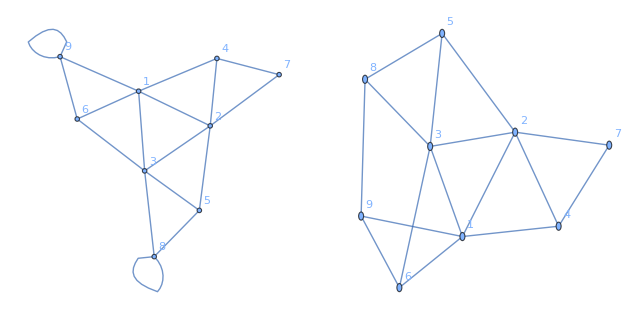

```mathematica
A1 = {
{0,1,1,1,0,1,0,0,1},
{1,0,1,1,1,0,1,0,0},
{1,1,0,0,1,1,0,1,0},
{1,1,0,0,0,0,1,0,0},
{0,1,1,0,0,0,0,1,0},
{1,0,1,0,0,0,0,0,1},
{0,1,0,1,0,0,0,0,0},
{0,0,1,0,1,0,0,1,0},
{1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,1,0,0,1},
{1,0,1,1,1,0,1,0,0},
{1,1,0,0,1,1,0,1,0},
{1,1,0,0,0,0,1,0,0},
{0,1,1,0,0,0,0,1,0},
{1,0,1,0,0,0,0,0,1},
{0,1,0,1,0,0,0,0,0},
{0,0,1,0,1,0,0,0,1},
{1,0,0,0,0,1,0,1,0}
};
autA1 = A1[[4;;,4;;]];
autA2 = A2[[4;;,4;;]];
Mss = A1[[4;;,;;4]];
MatrixForm[Mss]
Row[{MatrixForm[autA1],MatrixForm[autA2]}]
Row[{MatrixForm[autA1.Mss],MatrixForm[autA2.Mss]}]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
```

```mathematica
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,0,1},
{0,1,0,0,0,0,1,0,1,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A1[[2;;,;;1]];
MatrixForm[Mss]

i=4
Row[{MatrixForm[MatrixPower[autA1,i].Mss],MatrixForm[MatrixPower[autA2,i].Mss]}]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
```

(1
1
1
0
0
0
0
0
0)

4

(129
125
130
79
84
85
54
75
75)(129
125
130
79
84
85
54
75
75)

-Graphics-

```mathematica
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,1,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0.5,0.5,0},
{0,0,0,1,0,1,0,0,0.5,0.5},
{0,1,0,0,0,0,1,0,0.5,0.5}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A1[[2;;,;;1]];
MatrixForm[Mss]

i=4
Row[{MatrixForm[MatrixPower[autA1,i].Mss],MatrixForm[MatrixPower[autA2,i].Mss]}]
Row[{Simplify[Smash[WeightedAdjacencyGraph[A1],{1}]], Simplify[Smash[WeightedAdjacencyGraph[A2],{1}]]}]
```

(1
1
1
0
0
0
0
0
0)

4

(131
131
131
85
85
85
75
75
75)(131.
131.
131.
85.
85.
85.
75.
75.
75.)

{{λ/(-9+λ)}}{{λ/(-9+λ)}}

```mathematica
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,2 λ/(λ^2-1),0,0},
{0,0,0,1,0,1,0,0,2 λ/(λ^2-1),0},
{0,1,0,0,0,0,1,0,0,2 λ/(λ^2-1)}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,λ/(λ^2-1),λ/(λ^2-1),0},
{0,0,0,1,0,1,0,0,λ/(λ^2-1),λ/(λ^2-1)},
{0,1,0,0,0,0,1,0,λ/(λ^2-1),λ/(λ^2-1)}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A1[[2;;,;;1]];
MatrixForm[Mss]

i=5
Row[{Simplify[MatrixForm[MatrixPower[autA1,i].Mss]],Simplify[MatrixForm[MatrixPower[autA2,i].Mss]]}]
Row[{Simplify[SmashAdj[A1,WeightedAdjacencyGraph[A1],{1}]], Simplify[SmashAdj[A2,WeightedAdjacencyGraph[A2],{1}]]}]
```

(1
1
1
0
0
0
0
0
0)

5

((2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4))((2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4))

{{(3 (1-4 λ^2+λ^4))/(2+14 λ+4 λ^2-9 λ^3-2 λ^4+λ^5)}}{{(3 (1-4 λ^2+λ^4))/(2+14 λ+4 λ^2-9 λ^3-2 λ^4+λ^5)}}

```mathematica
`
```

```mathematica
A1={{0,0,0,0,0},{0,1,0,0,1},{0,0,1,1,1},{0,0,1,0,1},{0,1,1,1,0}}
A2={{0,0,0,0,0},{0,0,1,0,1},{0,1,0,1,1},{0,0,1,0,1},{0,1,1,1,0}}
Mss={1,1,1,0,0}
i=3
MatrixPower[A1,i].Mss
MatrixPower[A2,i].Mss
MatrixPower[A1,i]//MatrixForm
MatrixPower[A2,i]//MatrixForm



A1={
{0,1,1,1,0,0},
{1,0,0,0,0,0},
{1,0,1,0,0,1},
{1,0,0,1,1,1},
{0,0,0,1,0,1},
{0,0,1,1,1,0}
};
A2={
{0,1,1,1,0,0},
{1,0,0,0,0,0},
{1,0,0,1,0,1},
{1,0,1,0,1,1},
{0,0,0,1,0,1},
{0,0,1,1,1,0}
};
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
```

{{0,0,0,0,0},{0,1,0,0,1},{0,0,1,1,1},{0,0,1,0,1},{0,1,1,1,0}}

{{0,0,0,0,0},{0,0,1,0,1},{0,1,0,1,1},{0,0,1,0,1},{0,1,1,1,0}}

{1,1,1,0,0}

3

{0,6,10,7,10}

{0,7,9,7,10}

(0 | 0 | 0 | 0 | 0
0 | 3 | 3 | 2 | 4
0 | 3 | 7 | 5 | 6
0 | 2 | 5 | 3 | 5
0 | 4 | 6 | 5 | 4)

(0 | 0 | 0 | 0 | 0
0 | 2 | 5 | 2 | 5
0 | 5 | 4 | 5 | 5
0 | 2 | 5 | 2 | 5
0 | 5 | 5 | 5 | 4)

{{(2+5 λ-6 λ^2-4 λ^3+3 λ^4)/(2 λ+3 λ^2-3 λ^3-2 λ^4+λ^5)}}

{{(-6-8 λ+2 λ^2+3 λ^3)/(λ (-4-5 λ+λ^3))}}

```mathematica
A={
{0,1,1,1,0,0,0,1,1,1},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{1,0,1,0,1,0,0,0,0,0},
{1,0,0,1,0,1,0,0,0,0},
{1,1,0,0,0,0,1,0,0,0}
};
A1 = {
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,1},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,2}
};
A2 ={
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,2},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,3,0,0}
};
autA = A[[2;;,2;;]];
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A[[2;;,;;1]];
MatrixForm[Mss]


i=3;
j=2;
k=1;
Row[{
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA1,i].Mss],
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA2,i].Mss]
}]
GraphicsRow[{AdjacencyGraph[A,VertexLabels->Automatic],AdjacencyGraph[A1+A,VertexLabels->Automatic],AdjacencyGraph[A2+A,VertexLabels->Automatic]}]
```

(1
1
1
0
0
0
1
1
1)

(0
0
0
0
0
0
162
0
162)(0
0
0
0
0
0
162
0
162)

-Graphics-

```mathematica
A={
{0,1,1,1,0,0,0,1,1,1},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{1,0,1,0,1,0,0,0,0,0},
{1,0,0,1,0,1,0,0,0,0},
{1,1,0,0,0,0,1,0,0,0}
};
A1 = {
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,2},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0}
};
A2 ={
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,2}
};
autA = A[[2;;,2;;]];
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A[[2;;,;;1]];
MatrixForm[Mss]


i=3;
j=2;
k=1;
Row[{
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA1,i].Mss],
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA2,i].Mss]
}]
GraphicsRow[{AdjacencyGraph[A,VertexLabels->Automatic],AdjacencyGraph[A1+A,VertexLabels->Automatic],AdjacencyGraph[A2+A,VertexLabels->Automatic]}]
Eigenvalues[A1]
Eigenvectors[A1]
Eigenvalues[A2]
Eigenvectors[A2]
```

(1
1
1
0
0
0
1
1
1)

(0
0
0
0
0
0
32
0
32)(0
0
0
0
0
0
32
0
32)

-Graphics-

{-2,2,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,0,-1,0,1},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}}

{2,2,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}}

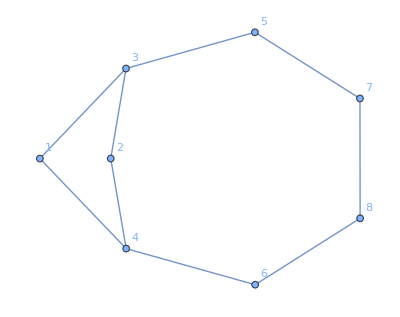

```mathematica
A={
{0,0,1,1,0,0,0,0},
{0,0,1,1,0,0,0,0},
{1,1,0,0,1,0,0,0},
{1,1,0,0,0,1,0,0},
{0,0,1,0,0,0,1,0},
{0,0,0,1,0,0,0,1},
{0,0,0,0,1,0,0,1},
{0,0,0,0,0,1,1,0}
};
AdjacencyGraph[A,VertexLabels->Automatic]
```

## Tree Real Algebraic Roots

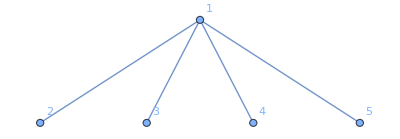

4 λ^3-λ^5

{-2,2,0,0,0}

{{λ^2/(-3 λ+λ^3)}}

```mathematica
T=Graph[{1<->2,1<->3,1<->4,1<->5},VertexLabels->Automatic]
CharacteristicPolynomial[AdjacencyMatrix[T],λ]
Eigenvalues[AdjacencyMatrix[T]]
Smash[T,{2}]
```

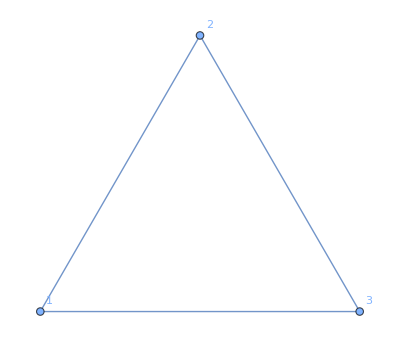

2+3 λ-λ^3

{2,-1,-1}

{{2/(-1+λ)}}

```mathematica
T=Graph[{1<->2,1<->3,2<->3},VertexLabels->Automatic]
CharacteristicPolynomial[AdjacencyMatrix[T],λ]
Eigenvalues[AdjacencyMatrix[T]]
Simplify[Smash[T,{2}]]
```

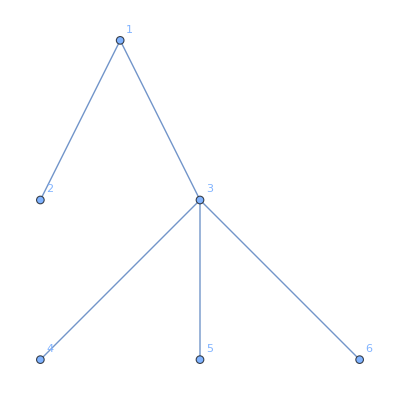

3 λ^2-5 λ^4+λ^6

```mathematica
T=Graph[{1<->2,1<->3,3<->4,3<->5,3<->6},VertexLabels->Automatic]
CharacteristicPolynomial[AdjacencyMatrix[T],λ]
```

## Generalizations Attempts (Equitable Partitions)

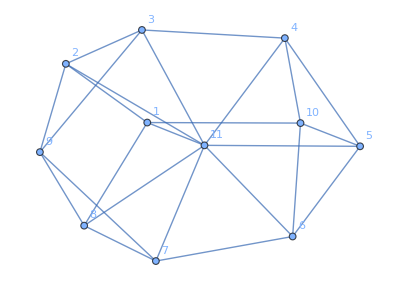

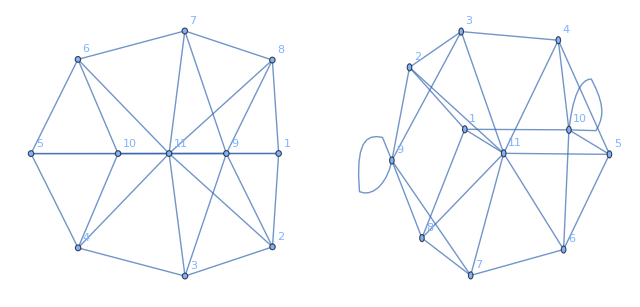

{{(8 (-1+λ))/(-2-3 λ+λ^2)}}

{{λ→1}}

{{(8 (-1+λ))/(-2-3 λ+λ^2)}}

{{λ→1}}

```mathematica
G=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->1,2<->9,3<->9,8<->9,7<->9,1<->10,4<->10,5<->10,6<->10,11<->1,11<->2,11<->3,11<->4,11<->5,11<->6,11<->7,11<->8},VertexLabels->Automatic]
A=Normal[AdjacencyMatrix[G]];
A1 = A;
A1[[9,10]]=A1[[9,10]]+1;
A1[[10,9]]=A1[[10,9]]+1;
A2 = A;
A2[[9,9]]=A2[[9,9]]+1;
A2[[10,10]]=A2[[10,10]]+1;
G1 = AdjacencyGraph[A1,VertexLabels->Automatic];
G2=AdjacencyGraph[A2,VertexLabels->Automatic];
GraphicsRow[
{
G1,
G2
}
]
Simplify[Smash[G1,{11}]]
Solve[Simplify[Smash[G1,{11}]][[1,1]]==0,λ]
Simplify[Smash[G2,{11}]]
Solve[Simplify[Smash[G2,{11}]][[1,1]]==0,λ]
```

```mathematica
G1 = HypercubeGraph[4]
Simplify[Smash[G1,{1,16}]]
Simplify[Smash[G1,{1,13,16}]]//MatrixForm
Simplify[Smash[G1,{1,5,16}]]//MatrixForm

A2 = {
{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},

{1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},
{1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0},
{1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0},
{1,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0},

{0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0},
{0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0},
{0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0},
{0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0},
{0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0},
{0,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0},

{0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1},
{0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,1},

{0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0}
};

G2=AdjacencyGraph[A2,VertexLabels->Automatic]
Simplify[Smash[G2, {1,16}]]
Simplify[Smash[G2, {1,9,16}]]//MatrixForm
Simplify[Smash[G2, {1,4,16}]]//MatrixForm

G3 = Graph[{1<->2,1<->3,1<->4,1<->5,
2<->6,2<->7,
3<->6,3<->7,
4<->7,4<->8,
5<->7,5<->8,
6<->9,6<->10,
7<->9,7<->10,7<->11,7<->12,
8<->11,8<->12,
13<->9,13<->10,13<->11,13<->12},VertexLabels->Automatic]
Simplify[Smash[G3, {1,13}]]
Simplify[Smash[G3, {1,7,13}]]//MatrixForm
Simplify[Smash[G3, {1,2,13}]]//MatrixForm
```

-Graphics-

{{(4 (-6+λ^2))/(λ (-12+λ^2)),24/(λ (-12+λ^2))},{24/(λ (-12+λ^2)),(4 (-6+λ^2))/(λ (-12+λ^2))}}

((4 (8-7 λ^2+λ^4))/(λ (16-12 λ^2+λ^4)) | (2 λ (-4+λ^2))/(16-12 λ^2+λ^4) | (4 (-8+5 λ^2))/(λ (16-12 λ^2+λ^4))
(2 λ (-4+λ^2))/(16-12 λ^2+λ^4) | (4 λ (-8+λ^2))/(16-12 λ^2+λ^4) | (2 λ (-4+λ^2))/(16-12 λ^2+λ^4)
(4 (-8+5 λ^2))/(λ (16-12 λ^2+λ^4)) | (2 λ (-4+λ^2))/(16-12 λ^2+λ^4) | (4 (8-7 λ^2+λ^4))/(λ (16-12 λ^2+λ^4)))

((36-24 λ^2+3 λ^4)/(24 λ-13 λ^3+λ^5) | (24-10 λ^2+λ^4)/(24-13 λ^2+λ^4) | (18 (-2+λ^2))/(λ (24-13 λ^2+λ^4))
(24-10 λ^2+λ^4)/(24-13 λ^2+λ^4) | (3 λ (-8+λ^2))/(24-13 λ^2+λ^4) | (6 (-4+λ^2))/(24-13 λ^2+λ^4)
(18 (-2+λ^2))/(λ (24-13 λ^2+λ^4)) | (6 (-4+λ^2))/(24-13 λ^2+λ^4) | (4 (9-7 λ^2+λ^4))/(λ (24-13 λ^2+λ^4)))

-Graphics-

{{(4 (-6+λ^2))/(λ (-12+λ^2)),24/(λ (-12+λ^2))},{24/(λ (-12+λ^2)),(4 (-6+λ^2))/(λ (-12+λ^2))}}

((4 (8-7 λ^2+λ^4))/(λ (16-12 λ^2+λ^4)) | (2 λ (-4+λ^2))/(16-12 λ^2+λ^4) | (4 (-8+5 λ^2))/(λ (16-12 λ^2+λ^4))
(2 λ (-4+λ^2))/(16-12 λ^2+λ^4) | (4 λ (-8+λ^2))/(16-12 λ^2+λ^4) | (2 λ (-4+λ^2))/(16-12 λ^2+λ^4)
(4 (-8+5 λ^2))/(λ (16-12 λ^2+λ^4)) | (2 λ (-4+λ^2))/(16-12 λ^2+λ^4) | (4 (8-7 λ^2+λ^4))/(λ (16-12 λ^2+λ^4)))

((384-244 λ^2+48 λ^4-3 λ^6)/(240 λ-132 λ^3+21 λ^5-λ^7) | (-192+104 λ^2-18 λ^4+λ^6)/(-240+132 λ^2-21 λ^4+λ^6) | (6 (64-30 λ^2+3 λ^4))/(λ (-240+132 λ^2-21 λ^4+λ^6))
(-192+104 λ^2-18 λ^4+λ^6)/(-240+132 λ^2-21 λ^4+λ^6) | (λ (144-44 λ^2+3 λ^4))/(-240+132 λ^2-21 λ^4+λ^6) | (6 (32-12 λ^2+λ^4))/(-240+132 λ^2-21 λ^4+λ^6)
(6 (64-30 λ^2+3 λ^4))/(λ (-240+132 λ^2-21 λ^4+λ^6)) | (6 (32-12 λ^2+λ^4))/(-240+132 λ^2-21 λ^4+λ^6) | (4 (-96+69 λ^2-15 λ^4+λ^6))/(λ (-240+132 λ^2-21 λ^4+λ^6)))

-Graphics-

{{(4 (-6+λ^2))/(λ (-12+λ^2)),24/(λ (-12+λ^2))},{24/(λ (-12+λ^2)),(4 (-6+λ^2))/(λ (-12+λ^2))}}

((4 (-2+λ^2))/(λ (-4+λ^2)) | (4 λ)/(-4+λ^2) | 8/(-4 λ+λ^3)
(4 λ)/(-4+λ^2) | (8 λ)/(-4+λ^2) | (4 λ)/(-4+λ^2)
8/(-4 λ+λ^3) | (4 λ)/(-4+λ^2) | (4 (-2+λ^2))/(λ (-4+λ^2)))

((60-28 λ^2+3 λ^4)/(36 λ-14 λ^3+λ^5) | (24-10 λ^2+λ^4)/(36-14 λ^2+λ^4) | -(60-18 λ^2)/(36 λ-14 λ^3+λ^5)
(24-10 λ^2+λ^4)/(36-14 λ^2+λ^4) | (2 λ (-6+λ^2))/(36-14 λ^2+λ^4) | (6 (-4+λ^2))/(36-14 λ^2+λ^4)
-(60-18 λ^2)/(36 λ-14 λ^3+λ^5) | (6 (-4+λ^2))/(36-14 λ^2+λ^4) | (60-32 λ^2+4 λ^4)/(36 λ-14 λ^3+λ^5))

```mathematica
G=Graph[{1<->2,1<->3,1<->4,1<->5,6<->2,6<->3,6<->4,6<->5},VertexLabels->Automatic]
Eigenvalues[AdjacencyMatrix[G]]
Eigenvectors[AdjacencyMatrix[G]]
Simplify[Smash[G,{1,6}]]
Det[Simplify[Smash[G,{1,6}]]-λ IdentityMatrix[2]]
```

-Graphics-

{-2 √2,2 √2,0,0,0,0}

{{1,-1/(√2),-1/(√2),-1/(√2),-1/(√2),1},{1,1/(√2),1/(√2),1/(√2),1/(√2),1},{-1,0,0,0,0,1},{0,-1,0,0,1,0},{0,-1,0,1,0,0},{0,-1,1,0,0,0}}

{{4/λ,4/λ},{4/λ,4/λ}}

(-8 λ^2+λ^4)/λ^2

## f(λ), g(λ) finding

```mathematica
(*Function to compute the "leading power of λ" for an entry*)
FindNumDen[expr_,λ_]:=Module[{num,den},
num=Numerator[Together[expr]];
den=Denominator[Together[expr]];
{num, den}
];

(*Run reductions on all graphs of size n*)
ReductionFunctions[n_,m_]:=Module[{graphs},
graphs=GraphData/@GraphData["Connected",n];
Flatten[
Table[
Module[{adjmat,key,powers,num,den},
adjmat=Simplify[Smash[graphs[[i]],S]];
(*canonicalize matrix form for comparison*)
key=Simplify[Normal[adjmat]];
{num, den}=Transpose[FindNumDen[#,λ]&/@Flatten[adjmat]];
<|
"n"->n,
"GraphIndex"->i,
"Vertices"->S,
"Reduction"->key,
"f(λ)"->num,
"g(λ)"->den
|>
],
{i,Length[graphs]},
{S,Subsets[Range[n],{m}]}
],
1
]
];

canonical[expr_]:=Simplify[Together[expr]];

FindFunction[list_,expr_]:=Select[list,canonical[#]===canonical[expr]&];
```

```mathematica
data=Flatten@Table[ReductionFunctions[n,1],{n,4,8}];
Length[data]
```

12676

```mathematica
uniqueNumerators=Union@(canonical/@Flatten[data[[All,"f(λ)"]]]);
uniqueDenominators=Union@(canonical/@Flatten[data[[All,"g(λ)"]]]);
uniqueReductions=Union@(Simplify/@data[[All,"Reduction"]]);

Length[uniqueNumerators]
Length[uniqueDenominators]
Length[uniqueReductions]
```

5189

1681

8737

```mathematica
Column[uniqueNumerators]

FindFunction[uniqueNumerators, λ-1]
```

3
4
5
6
7
-5+λ
-4+λ
2 (-4+λ)
-3+λ
2 (-3+λ)
-2+λ
2 (-2+λ)
3 (-2+λ)
4 (-2+λ)
-1+λ
2 (-1+λ)
3 (-1+λ)
4 (-1+λ)
5 (-1+λ)
6 (-1+λ)
λ
2 λ
3 λ
4 λ
5 λ
6 λ
(-3+λ) λ
(-2+λ) λ
2 (-2+λ) λ
3 (-2+λ) λ
(-1+λ) λ
2 (-1+λ) λ
3 (-1+λ) λ
4 (1+λ)
6 (1+λ)
2 (-4+λ) (1+λ)
2 (-3+λ) (1+λ)
3 (-3+λ) (1+λ)
2 (-2+λ) (1+λ)
3 (-2+λ) (1+λ)
4 (-2+λ) (1+λ)
2 (-2+λ) λ (1+λ)
6 (2+λ)
4 (-1+λ) (2+λ)
4 λ (2+λ)
5 λ (2+λ)
2 λ (-5+2 λ)
2 λ (-3+2 λ)
2 (1+λ) (-3+2 λ)
2 λ (1+λ) (-3+2 λ)
2 λ (-1+2 λ)
2 (-1+λ) (1+2 λ)
2 λ (1+2 λ)
2 λ (3+2 λ)
2 λ (-5+3 λ)
2 λ (1+λ) (-5+3 λ)
-4+3 λ
λ (-4+3 λ)
(1+λ) (-4+3 λ)
λ (1+λ) (-4+3 λ)
-2+3 λ
λ (-2+3 λ)
2 λ (-2+3 λ)
2 (2+λ) (-2+3 λ)
-1+3 λ
λ (-1+3 λ)
2+3 λ
λ (2+3 λ)
4+3 λ
2 (-1+λ) (4+3 λ)
λ (4+3 λ)
2 λ (4+3 λ)
(-1+λ) (5+3 λ)
λ (5+3 λ)
2 λ (5+3 λ)
(-1+λ) λ (5+3 λ)
2 λ (8+3 λ)
-6+4 λ
-2+4 λ
2+4 λ
6+4 λ
-7+5 λ
λ (-7+5 λ)
-4+5 λ
λ (-4+5 λ)
-3+5 λ
λ (-3+5 λ)
-2+5 λ
λ (-2+5 λ)
-1+5 λ
λ (-1+5 λ)
3+5 λ
4+5 λ
6+5 λ
λ (6+5 λ)
7+5 λ
λ (7+5 λ)
8+5 λ
λ (8+5 λ)
9+5 λ
λ (9+5 λ)
12+5 λ
λ (12+5 λ)
-10+6 λ
-8+6 λ
-4+6 λ
-2+6 λ
2+6 λ
4+6 λ
8+6 λ
10+6 λ
14+6 λ
16+6 λ
-5+7 λ
-2+7 λ
-1+7 λ
8+7 λ
10+7 λ
11+7 λ
12+7 λ
13+7 λ
15+7 λ
16+7 λ
20+7 λ
24+7 λ
-6+λ^2
2 (-6+λ^2)
λ (-6+λ^2)
2 λ (-6+λ^2)
-5+λ^2
2 (-5+λ^2)
λ (-5+λ^2)
2 λ (-5+λ^2)
-4+λ^2
2 (-4+λ^2)
λ (-4+λ^2)
2 λ (-4+λ^2)
-3+λ^2
2 (-3+λ^2)
3 (-3+λ^2)
4 (-3+λ^2)
λ (-3+λ^2)
2 λ (-3+λ^2)
3 λ (-3+λ^2)
4 λ (-3+λ^2)
-2+λ^2
2 (-2+λ^2)
3 (-2+λ^2)
4 (-2+λ^2)
6 (-2+λ^2)
λ (-2+λ^2)
2 λ (-2+λ^2)
3 λ (-2+λ^2)
4 λ (-2+λ^2)
6 λ (-2+λ^2)
(-1+3 λ) (-2+λ^2)
-1+λ^2
2 (-1+λ^2)
3 (-1+λ^2)
4 (-1+λ^2)
5 (-1+λ^2)
λ (-1+λ^2)
2 λ (-1+λ^2)
3 λ (-1+λ^2)
4 λ (-1+λ^2)
2 (1+2 λ) (-1+λ^2)
(2+3 λ) (-1+λ^2)
-5-4 λ+λ^2
1-4 λ+λ^2
-8-3 λ+λ^2
λ (-8-3 λ+λ^2)
-6-3 λ+λ^2
-4-3 λ+λ^2
2 (-2-3 λ+λ^2)
2 (1-3 λ+λ^2)
2 (1+λ) (1-3 λ+λ^2)
2-3 λ+λ^2
2 (1+λ) (2-3 λ+λ^2)
-8-2 λ+λ^2
λ (-8-2 λ+λ^2)
-6-2 λ+λ^2
2 (-6-2 λ+λ^2)
λ (-6-2 λ+λ^2)
2 (-5-2 λ+λ^2)
3 (-5-2 λ+λ^2)
2 λ (-5-2 λ+λ^2)
-4-2 λ+λ^2
2 (-4-2 λ+λ^2)
λ (-4-2 λ+λ^2)
-3-2 λ+λ^2
3 (-3-2 λ+λ^2)
4 (-3-2 λ+λ^2)
λ (-3-2 λ+λ^2)
-2-2 λ+λ^2
2 (-2-2 λ+λ^2)
3 (-2-2 λ+λ^2)
2 λ (-2-2 λ+λ^2)
-1-2 λ+λ^2
4 (-1-2 λ+λ^2)
-6-λ+λ^2
2 (-6-λ+λ^2)
λ (-6-λ+λ^2)
2 λ (-6-λ+λ^2)
2 (-5-λ+λ^2)
4 (-5-λ+λ^2)
λ (-5-λ+λ^2)
2 λ (-5-λ+λ^2)
-4-λ+λ^2
2 (-4-λ+λ^2)
3 (-4-λ+λ^2)
λ (-4-λ+λ^2)
2 λ (-4-λ+λ^2)
-3-λ+λ^2
2 (-3-λ+λ^2)
λ (-3-λ+λ^2)
2 λ (-3-λ+λ^2)
-2-λ+λ^2
2 (-2-λ+λ^2)
4 (-2-λ+λ^2)
λ (-2-λ+λ^2)
2 λ (-2-λ+λ^2)
-1-λ+λ^2
2 (-1-λ+λ^2)
4 (-1-λ+λ^2)
λ (-1-λ+λ^2)
2 λ (-1-λ+λ^2)
4 λ (-1-λ+λ^2)
2 (-5+λ+λ^2)
4 λ (-5+λ+λ^2)
4 (-4+λ+λ^2)
2 (-2+λ+λ^2)
3 (-2+λ+λ^2)
4 (-2+λ+λ^2)
2 λ (-2+λ+λ^2)
3 λ (-2+λ+λ^2)
4 λ (-2+λ+λ^2)
2 (-1+λ+λ^2)
3 (-1+λ+λ^2)
4 (-1+λ+λ^2)
6 (-1+λ+λ^2)
2 (-2+λ) (-1+λ+λ^2)
2 λ (-1+λ+λ^2)
3 λ (-1+λ+λ^2)
4 λ (-1+λ+λ^2)
6 λ (-1+λ+λ^2)
4 (-2+2 λ+λ^2)
4 (-1+2 λ+λ^2)
6 (-1+2 λ+λ^2)
4 λ (-1+2 λ+λ^2)
-9+2 λ^2
λ (-9+2 λ^2)
-7+2 λ^2
λ (-7+2 λ^2)
-5+2 λ^2
λ (-5+2 λ^2)
2 λ (-5+2 λ^2)
-3+2 λ^2
λ (-3+2 λ^2)
-1+2 λ^2
λ (-1+2 λ^2)
-5-8 λ+2 λ^2
3-8 λ+2 λ^2
-9-4 λ+2 λ^2
λ (-9-4 λ+2 λ^2)
-3-4 λ+2 λ^2
λ (-3-4 λ+2 λ^2)
-1-4 λ+2 λ^2
1-4 λ+2 λ^2
λ (1-4 λ+2 λ^2)
(1+λ) (1-4 λ+2 λ^2)
λ (1+λ) (1-4 λ+2 λ^2)
2 λ (-3-3 λ+2 λ^2)
2 (1+λ) (1-3 λ+2 λ^2)
-7-2 λ+2 λ^2
λ (-7-2 λ+2 λ^2)
2 λ (-7-2 λ+2 λ^2)
2 λ (-5-2 λ+2 λ^2)
λ (-3-2 λ+2 λ^2)
2 λ (-3-2 λ+2 λ^2)
2 λ (-9-λ+2 λ^2)
2 λ (-7-λ+2 λ^2)
2 λ (-6-λ+2 λ^2)
2 λ (-4-λ+2 λ^2)
2 λ (-3-λ+2 λ^2)
2 λ (-2-λ+2 λ^2)
2 λ (-10+λ+2 λ^2)
2 (-7+λ+2 λ^2)
2 (-6+λ+2 λ^2)
2 (-5+λ+2 λ^2)
2 λ (-5+λ+2 λ^2)
2 (-4+λ+2 λ^2)
2 λ (-4+λ+2 λ^2)
2 (-3+λ+2 λ^2)
2 λ (-3+λ+2 λ^2)
2 (1+λ) (-3+λ+2 λ^2)
2 (-2+λ+2 λ^2)
2 λ (-2+λ+2 λ^2)
2 (-1+λ+2 λ^2)
-7+2 λ+2 λ^2
λ (-7+2 λ+2 λ^2)
2 λ (-7+2 λ+2 λ^2)
-5+2 λ+2 λ^2
λ (-5+2 λ+2 λ^2)
2 λ (-5+2 λ+2 λ^2)
-3+2 λ+2 λ^2
λ (-3+2 λ+2 λ^2)
2 λ (-3+2 λ+2 λ^2)
-1+2 λ+2 λ^2
λ (-1+2 λ+2 λ^2)
2 λ (-1+2 λ+2 λ^2)
2 λ (-4+3 λ+2 λ^2)
2 λ (-3+3 λ+2 λ^2)
2 λ (-2+3 λ+2 λ^2)
2 λ (-1+3 λ+2 λ^2)
2 λ (-3+4 λ+2 λ^2)
(-1+λ) (1+4 λ+2 λ^2)
(-1+λ) λ (1+4 λ+2 λ^2)
2 (-1+λ) (1+5 λ+2 λ^2)
-11+3 λ^2
-10+3 λ^2
λ (-10+3 λ^2)
-8+3 λ^2
λ (-8+3 λ^2)
-7+3 λ^2
λ (-7+3 λ^2)
-5+3 λ^2
λ (-5+3 λ^2)
-4+3 λ^2
λ (-4+3 λ^2)
-2+3 λ^2
λ (-2+3 λ^2)
-1+3 λ^2
λ (-1+3 λ^2)
1-10 λ+3 λ^2
3-10 λ+3 λ^2
-8-9 λ+3 λ^2
(1+λ) (4-8 λ+3 λ^2)
-4-7 λ+3 λ^2
2-7 λ+3 λ^2
(1+λ) (2-7 λ+3 λ^2)
-11-6 λ+3 λ^2
-2-6 λ+3 λ^2
1-6 λ+3 λ^2
(1+λ) (1-6 λ+3 λ^2)
-20-5 λ+3 λ^2
-4-5 λ+3 λ^2
(1+λ) (-2-5 λ+3 λ^2)
-8-4 λ+3 λ^2
λ (-8-4 λ+3 λ^2)
-7-4 λ+3 λ^2
λ (-6-4 λ+3 λ^2)
-5-4 λ+3 λ^2
-4-4 λ+3 λ^2
λ (-4-4 λ+3 λ^2)
-3-4 λ+3 λ^2
λ (-3-4 λ+3 λ^2)
-1-4 λ+3 λ^2
1-4 λ+3 λ^2
λ (1-4 λ+3 λ^2)
(1+λ) (1-4 λ+3 λ^2)
λ (1+λ) (1-4 λ+3 λ^2)
λ (-16-3 λ+3 λ^2)
-13-3 λ+3 λ^2
-10-3 λ+3 λ^2
λ (-10-3 λ+3 λ^2)
-8-3 λ+3 λ^2
(-1+λ) (-8-3 λ+3 λ^2)
-7-3 λ+3 λ^2
λ (-7-3 λ+3 λ^2)
(-1+λ) (-5-3 λ+3 λ^2)
-4-3 λ+3 λ^2
λ (-4-3 λ+3 λ^2)
-2-3 λ+3 λ^2
-1-3 λ+3 λ^2
λ (-1-3 λ+3 λ^2)
-15-2 λ+3 λ^2
(1+λ) (-15-2 λ+3 λ^2)
-14-2 λ+3 λ^2
-12-2 λ+3 λ^2
λ (-12-2 λ+3 λ^2)
(1+λ) (-12-2 λ+3 λ^2)
λ (1+λ) (-12-2 λ+3 λ^2)
-8-2 λ+3 λ^2
(1+λ) (-8-2 λ+3 λ^2)
λ (-6-2 λ+3 λ^2)
-4-2 λ+3 λ^2
-1-2 λ+3 λ^2
-12-λ+3 λ^2
-8-λ+3 λ^2
λ (-7-λ+3 λ^2)
-6-λ+3 λ^2
λ (-6-λ+3 λ^2)
λ (-5-λ+3 λ^2)
-4-λ+3 λ^2
-3-λ+3 λ^2
λ (-3-λ+3 λ^2)
-2-λ+3 λ^2
λ (-2-λ+3 λ^2)
-1-λ+3 λ^2
λ (-1-λ+3 λ^2)
-12+λ+3 λ^2
λ (-11+λ+3 λ^2)
-8+λ+3 λ^2
λ (-8+λ+3 λ^2)
(1+λ) (-8+λ+3 λ^2)
-6+λ+3 λ^2
2 (-6+λ+3 λ^2)
λ (-6+λ+3 λ^2)
-5+λ+3 λ^2
λ (-5+λ+3 λ^2)
2 λ (-5+λ+3 λ^2)
-4+λ+3 λ^2
λ (-4+λ+3 λ^2)
-13+2 λ+3 λ^2
λ (-13+2 λ+3 λ^2)
-10+2 λ+3 λ^2
-9+2 λ+3 λ^2
(-1+λ^2) (-9+2 λ+3 λ^2)
-7+2 λ+3 λ^2
λ (-7+2 λ+3 λ^2)
2 λ (-6+2 λ+3 λ^2)
-5+2 λ+3 λ^2
λ (-5+2 λ+3 λ^2)
-3+2 λ+3 λ^2
λ (-3+2 λ+3 λ^2)
-2+2 λ+3 λ^2
2 λ (-2+2 λ+3 λ^2)
-1+2 λ+3 λ^2
-4+3 λ+3 λ^2
λ (-4+3 λ+3 λ^2)
-2+3 λ+3 λ^2
λ (-2+3 λ+3 λ^2)
-1+3 λ+3 λ^2
λ (-1+3 λ+3 λ^2)
-12+4 λ+3 λ^2
-7+4 λ+3 λ^2
λ (-7+4 λ+3 λ^2)
-6+4 λ+3 λ^2
λ (-6+4 λ+3 λ^2)
-4+4 λ+3 λ^2
λ (-4+4 λ+3 λ^2)
-3+4 λ+3 λ^2
λ (-3+4 λ+3 λ^2)
-2+4 λ+3 λ^2
λ (-2+4 λ+3 λ^2)
2 λ (-2+4 λ+3 λ^2)
-1+4 λ+3 λ^2
λ (-1+4 λ+3 λ^2)
2 λ (-4+5 λ+3 λ^2)
(-1+λ) (1+6 λ+3 λ^2)
2 λ (2+6 λ+3 λ^2)
(-1+λ) (3+8 λ+3 λ^2)
(-1+λ) λ (3+8 λ+3 λ^2)
2 (-1+λ) (4+9 λ+3 λ^2)
-14+4 λ^2
-11+4 λ^2
-10+4 λ^2
-9+4 λ^2
-7+4 λ^2
λ (-7+4 λ^2)
-6+4 λ^2
-3+4 λ^2
λ (-3+4 λ^2)
-2+4 λ^2
-1+4 λ^2
-8-10 λ+4 λ^2
-5-10 λ+4 λ^2
3-10 λ+4 λ^2
4-10 λ+4 λ^2
2-8 λ+4 λ^2
-6-6 λ+4 λ^2
-4-6 λ+4 λ^2
2-6 λ+4 λ^2
-17-4 λ+4 λ^2
-6-4 λ+4 λ^2
-2-4 λ+4 λ^2
-24-2 λ+4 λ^2
-16-2 λ+4 λ^2
-14-2 λ+4 λ^2
-12-2 λ+4 λ^2
-10-2 λ+4 λ^2
λ (-9-2 λ+4 λ^2)
-8-2 λ+4 λ^2
-6-2 λ+4 λ^2
-4-2 λ+4 λ^2
-3-2 λ+4 λ^2
λ (-3-2 λ+4 λ^2)
-2-2 λ+4 λ^2
-11+2 λ+4 λ^2
-9+2 λ+4 λ^2
λ (-9+2 λ+4 λ^2)
(1+λ) (-9+2 λ+4 λ^2)
λ (1+λ) (-9+2 λ+4 λ^2)
-5+2 λ+4 λ^2
λ (-5+2 λ+4 λ^2)
-3+2 λ+4 λ^2
-1+2 λ+4 λ^2
λ (-1+2 λ+4 λ^2)
-13+4 λ+4 λ^2
λ (-13+4 λ+4 λ^2)
-10+4 λ+4 λ^2
-6+4 λ+4 λ^2
-5+4 λ+4 λ^2
λ (-5+4 λ+4 λ^2)
-3+4 λ+4 λ^2
λ (-3+4 λ+4 λ^2)
-2+4 λ+4 λ^2
-1+4 λ+4 λ^2
-10+6 λ+4 λ^2
-8+6 λ+4 λ^2
-6+6 λ+4 λ^2
-4+6 λ+4 λ^2
-3+6 λ+4 λ^2
λ (-3+6 λ+4 λ^2)
-2+6 λ+4 λ^2
-2+8 λ+4 λ^2
3+8 λ+4 λ^2
λ (3+8 λ+4 λ^2)
-17+5 λ^2
-16+5 λ^2
-13+5 λ^2
-12+5 λ^2
-11+5 λ^2
-9+5 λ^2
-8+5 λ^2
λ (-8+5 λ^2)
-6+5 λ^2
-4+5 λ^2
-3+5 λ^2
-2+5 λ^2
-5-12 λ+5 λ^2
-5-8 λ+5 λ^2
(1+λ) (2-8 λ+5 λ^2)
3-8 λ+5 λ^2
-6-7 λ+5 λ^2
-7-6 λ+5 λ^2
-8-5 λ+5 λ^2
-3-5 λ+5 λ^2
-6-4 λ+5 λ^2
λ (-4-4 λ+5 λ^2)
-6-3 λ+5 λ^2
-4-3 λ+5 λ^2
λ (-4-3 λ+5 λ^2)
-3-3 λ+5 λ^2
-8-2 λ+5 λ^2
λ (-6-2 λ+5 λ^2)
-4-2 λ+5 λ^2
λ (-4-2 λ+5 λ^2)
-2-2 λ+5 λ^2
λ (-11-λ+5 λ^2)
-4-λ+5 λ^2
-10+λ+5 λ^2
λ (-10+λ+5 λ^2)
-8+λ+5 λ^2
λ (-8+λ+5 λ^2)
-7+λ+5 λ^2
λ (-7+λ+5 λ^2)
-6+λ+5 λ^2
-1+λ+5 λ^2
λ (-1+λ+5 λ^2)
-15+2 λ+5 λ^2
-11+2 λ+5 λ^2
λ (-10+2 λ+5 λ^2)
-9+2 λ+5 λ^2
λ (-9+2 λ+5 λ^2)
-8+2 λ+5 λ^2
λ (-8+2 λ+5 λ^2)
-7+2 λ+5 λ^2
λ (-7+2 λ+5 λ^2)
λ (-6+2 λ+5 λ^2)
-4+2 λ+5 λ^2
λ (-4+2 λ+5 λ^2)
-3+2 λ+5 λ^2
-2+2 λ+5 λ^2
-1+2 λ+5 λ^2
-20+3 λ+5 λ^2
-16+3 λ+5 λ^2
λ (-12+3 λ+5 λ^2)
λ (1+λ) (-12+3 λ+5 λ^2)
-11+3 λ+5 λ^2
-8+3 λ+5 λ^2
(1+λ) (-8+3 λ+5 λ^2)
-4+3 λ+5 λ^2
λ (-16+4 λ+5 λ^2)
-10+4 λ+5 λ^2
λ (-10+4 λ+5 λ^2)
-8+4 λ+5 λ^2
λ (-8+4 λ+5 λ^2)
-7+4 λ+5 λ^2
λ (-7+4 λ+5 λ^2)
-4+4 λ+5 λ^2
λ (-4+4 λ+5 λ^2)
λ (-16+5 λ+5 λ^2)
-12+5 λ+5 λ^2
λ (-8+5 λ+5 λ^2)
-7+5 λ+5 λ^2
λ (-7+5 λ+5 λ^2)
-6+5 λ+5 λ^2
-4+5 λ+5 λ^2
λ (-4+5 λ+5 λ^2)
-1+5 λ+5 λ^2
λ (-1+5 λ+5 λ^2)
-9+6 λ+5 λ^2
λ (-9+6 λ+5 λ^2)
-7+6 λ+5 λ^2
λ (-7+6 λ+5 λ^2)
-4+6 λ+5 λ^2
-3+6 λ+5 λ^2
λ (-3+6 λ+5 λ^2)
-2+6 λ+5 λ^2
-1+6 λ+5 λ^2
-15+7 λ+5 λ^2
-4+7 λ+5 λ^2
-2+7 λ+5 λ^2
-12+8 λ+5 λ^2
-10+8 λ+5 λ^2
λ (-10+8 λ+5 λ^2)
-7+8 λ+5 λ^2
λ (-7+8 λ+5 λ^2)
-6+8 λ+5 λ^2
λ (-6+8 λ+5 λ^2)
-4+8 λ+5 λ^2
-3+8 λ+5 λ^2
λ (-3+8 λ+5 λ^2)
-1+8 λ+5 λ^2
λ (-1+8 λ+5 λ^2)
-6+9 λ+5 λ^2
-4+9 λ+5 λ^2
λ (-4+9 λ+5 λ^2)
3+9 λ+5 λ^2
λ (3+9 λ+5 λ^2)
4+11 λ+5 λ^2
-6+12 λ+5 λ^2
λ (-6+12 λ+5 λ^2)
-3+12 λ+5 λ^2
6+14 λ+5 λ^2
λ (6+14 λ+5 λ^2)
(-1+λ) (16+19 λ+5 λ^2)
-14+6 λ^2
-8+6 λ^2
-5+6 λ^2
-4+6 λ^2
-2+6 λ^2
2-10 λ+6 λ^2
-8-4 λ+6 λ^2
-5-4 λ+6 λ^2
-4-4 λ+6 λ^2
-14-2 λ+6 λ^2
-8-2 λ+6 λ^2
-9+2 λ+6 λ^2
-3+2 λ+6 λ^2
-12+4 λ+6 λ^2
-8+4 λ+6 λ^2
-6+4 λ+6 λ^2
-4+4 λ+6 λ^2
-9+6 λ+6 λ^2
-8+6 λ+6 λ^2
-5+6 λ+6 λ^2
-4+6 λ+6 λ^2
-10+8 λ+6 λ^2
-6+8 λ+6 λ^2
-4+8 λ+6 λ^2
-2+8 λ+6 λ^2
-8+10 λ+6 λ^2
-9+12 λ+6 λ^2
-8+12 λ+6 λ^2
-2+12 λ+6 λ^2
2+12 λ+6 λ^2
4+12 λ+6 λ^2
-6+14 λ+6 λ^2
5+14 λ+6 λ^2
6+16 λ+6 λ^2
18+22 λ+6 λ^2
-11-2 λ+7 λ^2
-17+2 λ+7 λ^2
-12+2 λ+7 λ^2
-8+6 λ+7 λ^2
-24+7 λ+7 λ^2
-12+7 λ+7 λ^2
-9+8 λ+7 λ^2
-8+8 λ+7 λ^2
-6+9 λ+7 λ^2
-5+10 λ+7 λ^2
-3+12 λ+7 λ^2
-2+12 λ+7 λ^2
-6+13 λ+7 λ^2
5+15 λ+7 λ^2
6+15 λ+7 λ^2
8+16 λ+7 λ^2
-8-8 λ+λ^3
λ (-8-8 λ+λ^3)
2 (-7-7 λ+λ^3)
2 λ (-7-7 λ+λ^3)
-6-7 λ+λ^3
2 (-6-7 λ+λ^3)
λ (-6-7 λ+λ^3)
2 (1-7 λ+λ^3)
2 (-4-6 λ+λ^3)
2 (-3-6 λ+λ^3)
2 (2-6 λ+λ^3)
-4-5 λ+λ^3
2 (-4-5 λ+λ^3)
λ (-4-5 λ+λ^3)
2 λ (-4-5 λ+λ^3)
2 (-3-5 λ+λ^3)
2 λ (-3-5 λ+λ^3)
2 (3-5 λ+λ^3)
2 (-3-4 λ+λ^3)
2 λ (-3-4 λ+λ^3)
-2-4 λ+λ^3
2 (-2-4 λ+λ^3)
λ (-2-4 λ+λ^3)
2 λ (-2-4 λ+λ^3)
-1-4 λ+λ^3
2 (-1-4 λ+λ^3)
4 (-1-4 λ+λ^3)
2 (1-4 λ+λ^3)
2 (2-4 λ+λ^3)
2 (-1-3 λ+λ^3)
4 (-1-3 λ+λ^3)
2 (1-3 λ+λ^3)
4 (1-3 λ+λ^3)
2 λ (1-3 λ+λ^3)
2 (1-2 λ+λ^3)
4 (1-2 λ+λ^3)
3-7 λ-3 λ^2+λ^3
4-6 λ-3 λ^2+λ^3
3-5 λ-3 λ^2+λ^3
2 (6-3 λ-3 λ^2+λ^3)
2 (1+λ) (2+λ-3 λ^2+λ^3)
1-2 λ^2+λ^3
2 (1-2 λ^2+λ^3)
2 (1+λ) (1-2 λ^2+λ^3)
-8-11 λ-2 λ^2+λ^3
-3-8 λ-2 λ^2+λ^3
4-8 λ-2 λ^2+λ^3
2 (2-7 λ-2 λ^2+λ^3)
2-5 λ-2 λ^2+λ^3
2 (2-5 λ-2 λ^2+λ^3)
2 (4-5 λ-2 λ^2+λ^3)
2 (1-4 λ-2 λ^2+λ^3)
2 (1+λ) (1-4 λ-2 λ^2+λ^3)
2-4 λ-2 λ^2+λ^3
5-4 λ-2 λ^2+λ^3
λ (2-3 λ-2 λ^2+λ^3)
4-3 λ-2 λ^2+λ^3
2 (4-3 λ-2 λ^2+λ^3)
2 (1+λ) (4-3 λ-2 λ^2+λ^3)
2 λ (1+λ) (6-3 λ-2 λ^2+λ^3)
2-2 λ-2 λ^2+λ^3
2 (2-2 λ-2 λ^2+λ^3)
λ (2-2 λ-2 λ^2+λ^3)
4 λ (2-2 λ-2 λ^2+λ^3)
4 (3-2 λ-2 λ^2+λ^3)
1-λ-2 λ^2+λ^3
2 (1-λ-2 λ^2+λ^3)
2 λ (1-λ-2 λ^2+λ^3)
2-λ-2 λ^2+λ^3
4 (2-λ-2 λ^2+λ^3)
λ (2-λ-2 λ^2+λ^3)
λ (-12-12 λ-λ^2+λ^3)
-4-9 λ-λ^2+λ^3
2 (-4-9 λ-λ^2+λ^3)
3-9 λ-λ^2+λ^3
λ (3-9 λ-λ^2+λ^3)
-6-8 λ-λ^2+λ^3
2 (-6-8 λ-λ^2+λ^3)
λ (-6-8 λ-λ^2+λ^3)
2 (1-7 λ-λ^2+λ^3)
2 (-3-6 λ-λ^2+λ^3)
2 (-2-6 λ-λ^2+λ^3)
2-6 λ-λ^2+λ^3
2 (2-6 λ-λ^2+λ^3)
λ (2-6 λ-λ^2+λ^3)
2 (5-6 λ-λ^2+λ^3)
-2-5 λ-λ^2+λ^3
2 (-2-5 λ-λ^2+λ^3)
1-5 λ-λ^2+λ^3
2 (1-5 λ-λ^2+λ^3)
3-5 λ-λ^2+λ^3
λ (3-5 λ-λ^2+λ^3)
4-5 λ-λ^2+λ^3
2 (4-5 λ-λ^2+λ^3)
λ (5-5 λ-λ^2+λ^3)
2 (-1-4 λ-λ^2+λ^3)
2 (1-4 λ-λ^2+λ^3)
2-4 λ-λ^2+λ^3
2 (2-4 λ-λ^2+λ^3)
λ (2-4 λ-λ^2+λ^3)
2 λ (2-4 λ-λ^2+λ^3)
2 λ (3-4 λ-λ^2+λ^3)
λ (4-4 λ-λ^2+λ^3)
2 (-1-3 λ-λ^2+λ^3)
1-3 λ-λ^2+λ^3
2 (1-3 λ-λ^2+λ^3)
3 (1-3 λ-λ^2+λ^3)
4 (1-3 λ-λ^2+λ^3)
λ (1-3 λ-λ^2+λ^3)
2-3 λ-λ^2+λ^3
2 (2-3 λ-λ^2+λ^3)
4 (2-3 λ-λ^2+λ^3)
λ (2-3 λ-λ^2+λ^3)
2 λ (2-3 λ-λ^2+λ^3)
3-3 λ-λ^2+λ^3
2 (3-3 λ-λ^2+λ^3)
λ (3-3 λ-λ^2+λ^3)
2 λ (3-3 λ-λ^2+λ^3)
1-2 λ-λ^2+λ^3
2 (1-2 λ-λ^2+λ^3)
4 (1-2 λ-λ^2+λ^3)
2 λ (1-2 λ-λ^2+λ^3)
2-2 λ-λ^2+λ^3
2 (2-2 λ-λ^2+λ^3)
λ (2-2 λ-λ^2+λ^3)
2 λ (2-2 λ-λ^2+λ^3)
2 (-6-7 λ+λ^2+λ^3)
2 (-4-6 λ+λ^2+λ^3)
2 (-6-5 λ+λ^2+λ^3)
2 (-4-5 λ+λ^2+λ^3)
2 λ (-4-5 λ+λ^2+λ^3)
3 (-3-5 λ+λ^2+λ^3)
2 (-3-4 λ+λ^2+λ^3)
4 (-2-4 λ+λ^2+λ^3)
-3-3 λ+λ^2+λ^3
λ (-3-3 λ+λ^2+λ^3)
2 (-2-3 λ+λ^2+λ^3)
2 λ (-2-3 λ+λ^2+λ^3)
2 (-1-3 λ+λ^2+λ^3)
4 (1-3 λ+λ^2+λ^3)
4 (-2-2 λ+λ^2+λ^3)
2 (-1-2 λ+λ^2+λ^3)
4 (-1-2 λ+λ^2+λ^3)
2 λ (-1-2 λ+λ^2+λ^3)
4 (-4-3 λ+2 λ^2+λ^3)
4 (-2-2 λ+2 λ^2+λ^3)
-12-13 λ+2 λ^3
λ (-12-13 λ+2 λ^3)
-7-11 λ+2 λ^3
1-9 λ+2 λ^3
λ (1-9 λ+2 λ^3)
-4-7 λ+2 λ^3
λ (-4-7 λ+2 λ^3)
-3-7 λ+2 λ^3
λ (-3-7 λ+2 λ^3)
1-7 λ+2 λ^3
4-7 λ+2 λ^3
λ (4-7 λ+2 λ^3)
2 (1+λ) (5-7 λ+2 λ^3)
-2-5 λ+2 λ^3
λ (-2-5 λ+2 λ^3)
1-5 λ+2 λ^3
λ (1-5 λ+2 λ^3)
2 λ (1-5 λ+2 λ^3)
2 (1+λ) (1-5 λ+2 λ^3)
2-5 λ+2 λ^3
1-3 λ+2 λ^3
λ (1-3 λ+2 λ^3)
2 (1+λ) (1-3 λ+2 λ^3)
3-9 λ-6 λ^2+2 λ^3
(1+λ) (-1+5 λ-6 λ^2+2 λ^3)
11-19 λ-4 λ^2+2 λ^3
3-13 λ-4 λ^2+2 λ^3
(1+λ) (8-9 λ-4 λ^2+2 λ^3)
2-7 λ-4 λ^2+2 λ^3
(1+λ) (2-7 λ-4 λ^2+2 λ^3)
8-5 λ-4 λ^2+2 λ^3
2-3 λ-4 λ^2+2 λ^3
(1+λ) (6-3 λ-4 λ^2+2 λ^3)
2-λ-4 λ^2+2 λ^3
2 λ (4-5 λ-3 λ^2+2 λ^3)
-6-13 λ-2 λ^2+2 λ^3
-4-11 λ-2 λ^2+2 λ^3
λ (-4-11 λ-2 λ^2+2 λ^3)
-4-9 λ-2 λ^2+2 λ^3
2-9 λ-2 λ^2+2 λ^3
3-9 λ-2 λ^2+2 λ^3
λ (3-9 λ-2 λ^2+2 λ^3)
5-9 λ-2 λ^2+2 λ^3
3-7 λ-2 λ^2+2 λ^3
λ (3-7 λ-2 λ^2+2 λ^3)
4-7 λ-2 λ^2+2 λ^3
5-7 λ-2 λ^2+2 λ^3
λ (5-7 λ-2 λ^2+2 λ^3)
2 (6-7 λ-2 λ^2+2 λ^3)
2 (8-7 λ-2 λ^2+2 λ^3)
2 λ (5-6 λ-2 λ^2+2 λ^3)
1-5 λ-2 λ^2+2 λ^3
λ (1-5 λ-2 λ^2+2 λ^3)
2-5 λ-2 λ^2+2 λ^3
3-5 λ-2 λ^2+2 λ^3
λ (3-5 λ-2 λ^2+2 λ^3)
4-5 λ-2 λ^2+2 λ^3
λ (4-5 λ-2 λ^2+2 λ^3)
2-3 λ-2 λ^2+2 λ^3
λ (2-3 λ-2 λ^2+2 λ^3)
3-3 λ-2 λ^2+2 λ^3
λ (3-3 λ-2 λ^2+2 λ^3)
1-λ-2 λ^2+2 λ^3
λ (1-λ-2 λ^2+2 λ^3)
2 (5-6 λ-λ^2+2 λ^3)
2 λ (2-5 λ-λ^2+2 λ^3)
2 λ (1-3 λ-λ^2+2 λ^3)
2 (4-13 λ+λ^2+2 λ^3)
2 λ (-7-11 λ+λ^2+2 λ^3)
2 λ (-8-10 λ+λ^2+2 λ^3)
2 (-6-10 λ+λ^2+2 λ^3)
2 (-4-9 λ+λ^2+2 λ^3)
2 λ (-7-8 λ+λ^2+2 λ^3)
2 (-6-8 λ+λ^2+2 λ^3)
2 (-4-7 λ+λ^2+2 λ^3)
2 (-4-6 λ+λ^2+2 λ^3)
2 (-3-6 λ+λ^2+2 λ^3)
2 (-2-6 λ+λ^2+2 λ^3)
2 (3-6 λ+λ^2+2 λ^3)
2 λ (3-6 λ+λ^2+2 λ^3)
2 (1+λ) (3-6 λ+λ^2+2 λ^3)
2 (-3-5 λ+λ^2+2 λ^3)
2 (-2-5 λ+λ^2+2 λ^3)
2 (-1-5 λ+λ^2+2 λ^3)
2 (-2-4 λ+λ^2+2 λ^3)
2 (-1-4 λ+λ^2+2 λ^3)
2 λ (-1-4 λ+λ^2+2 λ^3)
2 (1-4 λ+λ^2+2 λ^3)
2 (1+λ) (1-4 λ+λ^2+2 λ^3)
2 (-1-3 λ+λ^2+2 λ^3)
2 (1-3 λ+λ^2+2 λ^3)
2 (-1-2 λ+λ^2+2 λ^3)
-14-13 λ+2 λ^2+2 λ^3
-11-9 λ+2 λ^2+2 λ^3
λ (-11-9 λ+2 λ^2+2 λ^3)
-8-9 λ+2 λ^2+2 λ^3
-6-9 λ+2 λ^2+2 λ^3
λ (-6-9 λ+2 λ^2+2 λ^3)
2 λ (-6-9 λ+2 λ^2+2 λ^3)
-3-9 λ+2 λ^2+2 λ^3
-8-7 λ+2 λ^2+2 λ^3
2 (-8-7 λ+2 λ^2+2 λ^3)
λ (-8-7 λ+2 λ^2+2 λ^3)
λ (-7-7 λ+2 λ^2+2 λ^3)
-6-7 λ+2 λ^2+2 λ^3
2 (-6-7 λ+2 λ^2+2 λ^3)
λ (-6-7 λ+2 λ^2+2 λ^3)
3 (-5-7 λ+2 λ^2+2 λ^3)
λ (-5-7 λ+2 λ^2+2 λ^3)
2 (-5-6 λ+2 λ^2+2 λ^3)
2 λ (-5-6 λ+2 λ^2+2 λ^3)
-4-5 λ+2 λ^2+2 λ^3
λ (-4-5 λ+2 λ^2+2 λ^3)
2 λ (-4-5 λ+2 λ^2+2 λ^3)
-3-5 λ+2 λ^2+2 λ^3
λ (-3-5 λ+2 λ^2+2 λ^3)
2 λ (-3-4 λ+2 λ^2+2 λ^3)
2 λ (1-4 λ+2 λ^2+2 λ^3)
-2-3 λ+2 λ^2+2 λ^3
λ (-2-3 λ+2 λ^2+2 λ^3)
2 λ (-2-3 λ+2 λ^2+2 λ^3)
2 (-6-7 λ+3 λ^2+2 λ^3)
2 λ (-9-6 λ+3 λ^2+2 λ^3)
2 (-6-6 λ+3 λ^2+2 λ^3)
2 λ (-6-6 λ+3 λ^2+2 λ^3)
2 (-7-5 λ+3 λ^2+2 λ^3)
2 λ (-7-5 λ+3 λ^2+2 λ^3)
2 λ (-5-4 λ+3 λ^2+2 λ^3)
2 λ (-4-4 λ+3 λ^2+2 λ^3)
2 λ (-4-3 λ+3 λ^2+2 λ^3)
2 λ (-3-3 λ+3 λ^2+2 λ^3)
2 λ (-2-2 λ+3 λ^2+2 λ^3)
(-1+λ) (-8-5 λ+4 λ^2+2 λ^3)
2 λ (-4-3 λ+4 λ^2+2 λ^3)
2 λ (-5-2 λ+4 λ^2+2 λ^3)
2 λ (-4+5 λ^2+2 λ^3)
2 (-3+λ+5 λ^2+2 λ^3)
4-15 λ+3 λ^3
-6-13 λ+3 λ^3
(1+λ) (2-13 λ+3 λ^3)
-8-12 λ+3 λ^3
8-12 λ+3 λ^3
-6-11 λ+3 λ^3
-4-11 λ+3 λ^3
λ (-4-11 λ+3 λ^3)
(1+λ) (-4-11 λ+3 λ^3)
-6-10 λ+3 λ^3
-4-9 λ+3 λ^3
2-9 λ+3 λ^3
4-9 λ+3 λ^3
-4-8 λ+3 λ^3
λ (-4-8 λ+3 λ^3)
1-8 λ+3 λ^3
2-8 λ+3 λ^3
(1+λ) (2-8 λ+3 λ^3)
4-8 λ+3 λ^3
4-7 λ+3 λ^3
λ (4-7 λ+3 λ^3)
-1-6 λ+3 λ^3
2-6 λ+3 λ^3
2-5 λ+3 λ^3
(1+λ) (2-5 λ+3 λ^3)
(2+λ) (6-8 λ^2+3 λ^3)
3-13 λ-7 λ^2+3 λ^3
15-7 λ-7 λ^2+3 λ^3
λ (12-6 λ-7 λ^2+3 λ^3)
1-3 λ-7 λ^2+3 λ^3
9-3 λ-7 λ^2+3 λ^3
2-6 λ^2+3 λ^3
(1+λ) (2-6 λ^2+3 λ^3)
4-8 λ-6 λ^2+3 λ^3
8-8 λ-6 λ^2+3 λ^3
4-2 λ-6 λ^2+3 λ^3
1-λ-6 λ^2+3 λ^3
8-15 λ-4 λ^2+3 λ^3
4-12 λ-4 λ^2+3 λ^3
5-12 λ-4 λ^2+3 λ^3
2-11 λ-4 λ^2+3 λ^3
12-11 λ-4 λ^2+3 λ^3
λ (1+λ) (12-10 λ-4 λ^2+3 λ^3)
2-9 λ-4 λ^2+3 λ^3
(1+λ) (10-9 λ-4 λ^2+3 λ^3)
8-8 λ-4 λ^2+3 λ^3
-2-7 λ-4 λ^2+3 λ^3
4-7 λ-4 λ^2+3 λ^3
λ (4-7 λ-4 λ^2+3 λ^3)
(1+λ) (4-7 λ-4 λ^2+3 λ^3)
2-6 λ-4 λ^2+3 λ^3
5-6 λ-4 λ^2+3 λ^3
8-6 λ-4 λ^2+3 λ^3
4-5 λ-4 λ^2+3 λ^3
λ (4-5 λ-4 λ^2+3 λ^3)
4-4 λ-4 λ^2+3 λ^3
2-3 λ-4 λ^2+3 λ^3
2-2 λ-4 λ^2+3 λ^3
-5-19 λ-3 λ^2+3 λ^3
-5-17 λ-3 λ^2+3 λ^3
-4-17 λ-3 λ^2+3 λ^3
4-16 λ-3 λ^2+3 λ^3
1-13 λ-3 λ^2+3 λ^3
10-12 λ-3 λ^2+3 λ^3
1-11 λ-3 λ^2+3 λ^3
5-11 λ-3 λ^2+3 λ^3
9-11 λ-3 λ^2+3 λ^3
12-11 λ-3 λ^2+3 λ^3
-2-9 λ-3 λ^2+3 λ^3
2-8 λ-3 λ^2+3 λ^3
4-8 λ-3 λ^2+3 λ^3
λ (4-8 λ-3 λ^2+3 λ^3)
4-7 λ-3 λ^2+3 λ^3
2-6 λ-3 λ^2+3 λ^3
4-6 λ-3 λ^2+3 λ^3
λ (4-6 λ-3 λ^2+3 λ^3)
-1-5 λ-3 λ^2+3 λ^3
3-5 λ-3 λ^2+3 λ^3
4-5 λ-3 λ^2+3 λ^3
1-4 λ-3 λ^2+3 λ^3
2-3 λ-3 λ^2+3 λ^3
1-2 λ-3 λ^2+3 λ^3
2-2 λ-3 λ^2+3 λ^3
1-22 λ-2 λ^2+3 λ^3
-8-19 λ-2 λ^2+3 λ^3
-6-14 λ-2 λ^2+3 λ^3
1-13 λ-2 λ^2+3 λ^3
9-13 λ-2 λ^2+3 λ^3
2-10 λ-2 λ^2+3 λ^3
4-10 λ-2 λ^2+3 λ^3
4-8 λ-2 λ^2+3 λ^3
(1+λ) (4-8 λ-2 λ^2+3 λ^3)
6-8 λ-2 λ^2+3 λ^3
2-7 λ-2 λ^2+3 λ^3
2-5 λ-2 λ^2+3 λ^3
λ (2-5 λ-2 λ^2+3 λ^3)
2-3 λ-2 λ^2+3 λ^3
λ (2-3 λ-2 λ^2+3 λ^3)
12-17 λ-λ^2+3 λ^3
-9-15 λ-λ^2+3 λ^3
λ (-9-15 λ-λ^2+3 λ^3)
3-15 λ-λ^2+3 λ^3
λ (3-15 λ-λ^2+3 λ^3)
-7-13 λ-λ^2+3 λ^3
7-13 λ-λ^2+3 λ^3
-6-12 λ-λ^2+3 λ^3
10-12 λ-λ^2+3 λ^3
-3-11 λ-λ^2+3 λ^3
1-11 λ-λ^2+3 λ^3
3-11 λ-λ^2+3 λ^3
λ (3-11 λ-λ^2+3 λ^3)
2-10 λ-λ^2+3 λ^3
6-10 λ-λ^2+3 λ^3
-2-9 λ-λ^2+3 λ^3
3-9 λ-λ^2+3 λ^3
λ (3-9 λ-λ^2+3 λ^3)
6-9 λ-λ^2+3 λ^3
2-8 λ-λ^2+3 λ^3
λ (2-8 λ-λ^2+3 λ^3)
4-8 λ-λ^2+3 λ^3
λ (4-8 λ-λ^2+3 λ^3)
1-7 λ-λ^2+3 λ^3
λ (1-7 λ-λ^2+3 λ^3)
2-7 λ-λ^2+3 λ^3
2-6 λ-λ^2+3 λ^3
λ (2-6 λ-λ^2+3 λ^3)
1-5 λ-λ^2+3 λ^3
λ (1-5 λ-λ^2+3 λ^3)
3-5 λ-λ^2+3 λ^3
λ (3-5 λ-λ^2+3 λ^3)
1-4 λ-λ^2+3 λ^3
-12-20 λ+λ^2+3 λ^3
-11-18 λ+λ^2+3 λ^3
2-16 λ+λ^2+3 λ^3
-8-14 λ+λ^2+3 λ^3
-10-13 λ+λ^2+3 λ^3
-2-13 λ+λ^2+3 λ^3
-7-12 λ+λ^2+3 λ^3
-6-12 λ+λ^2+3 λ^3
-8-11 λ+λ^2+3 λ^3
3-11 λ+λ^2+3 λ^3
λ (3-11 λ+λ^2+3 λ^3)
2-10 λ+λ^2+3 λ^3
-5-9 λ+λ^2+3 λ^3
-1-9 λ+λ^2+3 λ^3
-4-8 λ+λ^2+3 λ^3
λ (-4-8 λ+λ^2+3 λ^3)
2 (1-8 λ+λ^2+3 λ^3)
2-7 λ+λ^2+3 λ^3
2-6 λ+λ^2+3 λ^3
-2-5 λ+λ^2+3 λ^3
2 (1-4 λ+λ^2+3 λ^3)
-12-13 λ+2 λ^2+3 λ^3
λ (-12-13 λ+2 λ^2+3 λ^3)
λ (-10-13 λ+2 λ^2+3 λ^3)
-6-8 λ+2 λ^2+3 λ^3
λ (-6-8 λ+2 λ^2+3 λ^3)
-2-8 λ+2 λ^2+3 λ^3
-14-12 λ+3 λ^2+3 λ^3
2-12 λ+3 λ^2+3 λ^3
-6-10 λ+3 λ^2+3 λ^3
λ (-6-10 λ+3 λ^2+3 λ^3)
-10-9 λ+3 λ^2+3 λ^3
2 λ (-7-9 λ+3 λ^2+3 λ^3)
-2-9 λ+3 λ^2+3 λ^3
-6-8 λ+3 λ^2+3 λ^3
λ (-6-8 λ+3 λ^2+3 λ^3)
-6-7 λ+3 λ^2+3 λ^3
2 (-6-7 λ+3 λ^2+3 λ^3)
λ (-6-7 λ+3 λ^2+3 λ^3)
-3-7 λ+3 λ^2+3 λ^3
1-7 λ+3 λ^2+3 λ^3
λ (1-7 λ+3 λ^2+3 λ^3)
-4-6 λ+3 λ^2+3 λ^3
-3-5 λ+3 λ^2+3 λ^3
λ (-3-5 λ+3 λ^2+3 λ^3)
-3-4 λ+3 λ^2+3 λ^3
-14-13 λ+4 λ^2+3 λ^3
-16-12 λ+4 λ^2+3 λ^3
-12-10 λ+4 λ^2+3 λ^3
-8-10 λ+4 λ^2+3 λ^3
-12-9 λ+4 λ^2+3 λ^3
-4-9 λ+4 λ^2+3 λ^3
λ (-4-9 λ+4 λ^2+3 λ^3)
-10-8 λ+4 λ^2+3 λ^3
λ (-10-8 λ+4 λ^2+3 λ^3)
-8-8 λ+4 λ^2+3 λ^3
λ (-8-8 λ+4 λ^2+3 λ^3)
-8-6 λ+4 λ^2+3 λ^3
λ (-8-6 λ+4 λ^2+3 λ^3)
-6-6 λ+4 λ^2+3 λ^3
λ (-6-6 λ+4 λ^2+3 λ^3)
-6-5 λ+4 λ^2+3 λ^3
λ (-6-5 λ+4 λ^2+3 λ^3)
2 (-5-5 λ+4 λ^2+3 λ^3)
-4-5 λ+4 λ^2+3 λ^3
λ (-4-5 λ+4 λ^2+3 λ^3)
-4-4 λ+4 λ^2+3 λ^3
λ (-4-4 λ+4 λ^2+3 λ^3)
2 λ (-2-4 λ+4 λ^2+3 λ^3)
-4-3 λ+4 λ^2+3 λ^3
λ (-4-3 λ+4 λ^2+3 λ^3)
-2-2 λ+4 λ^2+3 λ^3
λ (-2-2 λ+4 λ^2+3 λ^3)
λ (-10-6 λ+5 λ^2+3 λ^3)
2 (-4-6 λ+5 λ^2+3 λ^3)
2 (-7-4 λ+5 λ^2+3 λ^3)
λ (-2-2 λ+5 λ^2+3 λ^3)
(-1+λ) (-2+6 λ^2+3 λ^3)
-14-9 λ+6 λ^2+3 λ^3
2 λ (-9-4 λ+6 λ^2+3 λ^3)
2 λ (-10-3 λ+7 λ^2+3 λ^3)
2 λ (-7-λ+7 λ^2+3 λ^3)
2 (-4+λ+7 λ^2+3 λ^3)
2 (-7-λ+8 λ^2+3 λ^3)
2 (-7+λ+9 λ^2+3 λ^3)
2 (-6+2 λ+9 λ^2+3 λ^3)
2 λ (-3+4 λ+9 λ^2+3 λ^3)
2 (-1+6 λ+9 λ^2+3 λ^3)
5-25 λ+4 λ^3
-18-24 λ+4 λ^3
-8-18 λ+4 λ^3
4-18 λ+4 λ^3
-7-17 λ+4 λ^3
-7-15 λ+4 λ^3
-5-15 λ+4 λ^3
5-15 λ+4 λ^3
-8-14 λ+4 λ^3
-6-14 λ+4 λ^3
2-14 λ+4 λ^3
8-14 λ+4 λ^3
-3-13 λ+4 λ^3
3-13 λ+4 λ^3
-6-12 λ+4 λ^3
2-12 λ+4 λ^3
3-11 λ+4 λ^3
-2-10 λ+4 λ^3
2-10 λ+4 λ^3
4-10 λ+4 λ^3
6-10 λ+4 λ^3
2-9 λ+4 λ^3
(1+λ) (2-9 λ+4 λ^3)
3-9 λ+4 λ^3
λ (3-9 λ+4 λ^3)
2-8 λ+4 λ^3
1-7 λ+4 λ^3
λ (1-7 λ+4 λ^3)
-6 λ+4 λ^3
2-6 λ+4 λ^3
2-5 λ+4 λ^3
-2 λ+4 λ^3
3-5 λ-10 λ^2+4 λ^3
11-13 λ-8 λ^2+4 λ^3
4-2 λ-8 λ^2+4 λ^3
4-λ-8 λ^2+4 λ^3
8-10 λ-6 λ^2+4 λ^3
4-8 λ-6 λ^2+4 λ^3
12-8 λ-6 λ^2+4 λ^3
2-4 λ-6 λ^2+4 λ^3
4-4 λ-6 λ^2+4 λ^3
2-2 λ-6 λ^2+4 λ^3
2-λ-6 λ^2+4 λ^3
3-λ-6 λ^2+4 λ^3
-5-19 λ-4 λ^2+4 λ^3
3-11 λ-4 λ^2+4 λ^3
6-10 λ-4 λ^2+4 λ^3
8-10 λ-4 λ^2+4 λ^3
3-9 λ-4 λ^2+4 λ^3
4-6 λ-4 λ^2+4 λ^3
4-5 λ-4 λ^2+4 λ^3
λ (4-5 λ-4 λ^2+4 λ^3)
16-22 λ-2 λ^2+4 λ^3
λ (-12-19 λ-2 λ^2+4 λ^3)
8-16 λ-2 λ^2+4 λ^3
3-15 λ-2 λ^2+4 λ^3
6-14 λ-2 λ^2+4 λ^3
-4-12 λ-2 λ^2+4 λ^3
2-12 λ-2 λ^2+4 λ^3
4-12 λ-2 λ^2+4 λ^3
5-11 λ-2 λ^2+4 λ^3
7-11 λ-2 λ^2+4 λ^3
-4-10 λ-2 λ^2+4 λ^3
2-10 λ-2 λ^2+4 λ^3
4-10 λ-2 λ^2+4 λ^3
8-10 λ-2 λ^2+4 λ^3
3-9 λ-2 λ^2+4 λ^3
6-9 λ-2 λ^2+4 λ^3
λ (6-9 λ-2 λ^2+4 λ^3)
2-8 λ-2 λ^2+4 λ^3
4-8 λ-2 λ^2+4 λ^3
1-7 λ-2 λ^2+4 λ^3
2-7 λ-2 λ^2+4 λ^3
λ (2-7 λ-2 λ^2+4 λ^3)
3-7 λ-2 λ^2+4 λ^3
λ (3-7 λ-2 λ^2+4 λ^3)
-2-6 λ-2 λ^2+4 λ^3
2-6 λ-2 λ^2+4 λ^3
4-6 λ-2 λ^2+4 λ^3
2-4 λ-2 λ^2+4 λ^3
1-3 λ-2 λ^2+4 λ^3
λ (1-3 λ-2 λ^2+4 λ^3)
-24-23 λ+2 λ^2+4 λ^3
λ (-12-15 λ+2 λ^2+4 λ^3)
-9-15 λ+2 λ^2+4 λ^3
λ (-9-15 λ+2 λ^2+4 λ^3)
-10-13 λ+2 λ^2+4 λ^3
λ (-10-13 λ+2 λ^2+4 λ^3)
-9-13 λ+2 λ^2+4 λ^3
λ (-9-13 λ+2 λ^2+4 λ^3)
3-13 λ+2 λ^2+4 λ^3
λ (3-13 λ+2 λ^2+4 λ^3)
-6-9 λ+2 λ^2+4 λ^3
-4-9 λ+2 λ^2+4 λ^3
-2-9 λ+2 λ^2+4 λ^3
-4-7 λ+2 λ^2+4 λ^3
1-5 λ+2 λ^2+4 λ^3
λ (1-5 λ+2 λ^2+4 λ^3)
-20-17 λ+4 λ^2+4 λ^3
-8-14 λ+4 λ^2+4 λ^3
-12-13 λ+4 λ^2+4 λ^3
λ (-12-13 λ+4 λ^2+4 λ^3)
-8-10 λ+4 λ^2+4 λ^3
2-10 λ+4 λ^2+4 λ^3
-7-9 λ+4 λ^2+4 λ^3
-6-8 λ+4 λ^2+4 λ^3
2-8 λ+4 λ^2+4 λ^3
-4-7 λ+4 λ^2+4 λ^3
λ (-4-7 λ+4 λ^2+4 λ^3)
-4-6 λ+4 λ^2+4 λ^3
-4-5 λ+4 λ^2+4 λ^3
λ (-4-5 λ+4 λ^2+4 λ^3)
-3-5 λ+4 λ^2+4 λ^3
λ (-3-5 λ+4 λ^2+4 λ^3)
1-5 λ+4 λ^2+4 λ^3
λ (1-5 λ+4 λ^2+4 λ^3)
-2-4 λ+4 λ^2+4 λ^3
-20-14 λ+6 λ^2+4 λ^3
2-12 λ+6 λ^2+4 λ^3
-15-11 λ+6 λ^2+4 λ^3
-9-9 λ+6 λ^2+4 λ^3
-12-8 λ+6 λ^2+4 λ^3
-10-8 λ+6 λ^2+4 λ^3
-8-8 λ+6 λ^2+4 λ^3
-6-8 λ+6 λ^2+4 λ^3
-10-7 λ+6 λ^2+4 λ^3
λ (-10-7 λ+6 λ^2+4 λ^3)
-8-7 λ+6 λ^2+4 λ^3
-6-7 λ+6 λ^2+4 λ^3
-8-6 λ+6 λ^2+4 λ^3
-6-6 λ+6 λ^2+4 λ^3
-6-5 λ+6 λ^2+4 λ^3
λ (-6-5 λ+6 λ^2+4 λ^3)
-6-4 λ+6 λ^2+4 λ^3
-4-4 λ+6 λ^2+4 λ^3
-2-4 λ+6 λ^2+4 λ^3
-4-3 λ+6 λ^2+4 λ^3
λ (-4-3 λ+6 λ^2+4 λ^3)
-3-3 λ+6 λ^2+4 λ^3
λ (-3-3 λ+6 λ^2+4 λ^3)
-2-3 λ+6 λ^2+4 λ^3
-1-3 λ+6 λ^2+4 λ^3
-2-2 λ+6 λ^2+4 λ^3
-2+8 λ^2+4 λ^3
-24-14 λ+8 λ^2+4 λ^3
λ (-20-11 λ+8 λ^2+4 λ^3)
(-1+λ) (-17-9 λ+8 λ^2+4 λ^3)
-12-7 λ+8 λ^2+4 λ^3
λ (-12-7 λ+8 λ^2+4 λ^3)
-8-6 λ+8 λ^2+4 λ^3
-12-5 λ+8 λ^2+4 λ^3
-10-4 λ+8 λ^2+4 λ^3
-4-3 λ+8 λ^2+4 λ^3
λ (-4-3 λ+8 λ^2+4 λ^3)
-6-λ+8 λ^2+4 λ^3
λ (-6-λ+8 λ^2+4 λ^3)
(-1+λ) (-4-λ+8 λ^2+4 λ^3)
-3-λ+8 λ^2+4 λ^3
λ (-3-λ+8 λ^2+4 λ^3)
-8+10 λ^2+4 λ^3
-24-13 λ+10 λ^2+4 λ^3
-14-5 λ+10 λ^2+4 λ^3
λ (-7+λ+10 λ^2+4 λ^3)
-4+3 λ+10 λ^2+4 λ^3
λ (-4+3 λ+10 λ^2+4 λ^3)
-3+7 λ+12 λ^2+4 λ^3
λ (-3+7 λ+12 λ^2+4 λ^3)
1-18 λ+5 λ^3
λ (1+λ) (10-18 λ+5 λ^3)
-6-17 λ+5 λ^3
9-17 λ+5 λ^3
4-12 λ+5 λ^3
4-4 λ-9 λ^2+5 λ^3
1-8 λ^2+5 λ^3
11-17 λ-7 λ^2+5 λ^3
11-13 λ-7 λ^2+5 λ^3
16-12 λ-7 λ^2+5 λ^3
9-7 λ-7 λ^2+5 λ^3
1-5 λ-7 λ^2+5 λ^3
2-5 λ-6 λ^2+5 λ^3
9-11 λ-4 λ^2+5 λ^3
-3-10 λ-4 λ^2+5 λ^3
-2-9 λ-4 λ^2+5 λ^3
2-4 λ-4 λ^2+5 λ^3
-5-21 λ-3 λ^2+5 λ^3
-3-13 λ-3 λ^2+5 λ^3
5-11 λ-3 λ^2+5 λ^3
3-9 λ-3 λ^2+5 λ^3
5-9 λ-3 λ^2+5 λ^3
4-8 λ-3 λ^2+5 λ^3
1-7 λ-3 λ^2+5 λ^3
2-4 λ-3 λ^2+5 λ^3
(1+λ) (4-19 λ-2 λ^2+5 λ^3)
2-13 λ-2 λ^2+5 λ^3
8-13 λ-2 λ^2+5 λ^3
8-12 λ-2 λ^2+5 λ^3
2-11 λ-2 λ^2+5 λ^3
4-11 λ-2 λ^2+5 λ^3
4-8 λ-2 λ^2+5 λ^3
-2-7 λ-2 λ^2+5 λ^3
2-6 λ-2 λ^2+5 λ^3
3-9 λ-λ^2+5 λ^3
λ (3-9 λ-λ^2+5 λ^3)
-5-17 λ+λ^2+5 λ^3
-8-14 λ+λ^2+5 λ^3
2-14 λ+λ^2+5 λ^3
2-12 λ+λ^2+5 λ^3
1-10 λ+λ^2+5 λ^3
2-8 λ+λ^2+5 λ^3
2-7 λ+λ^2+5 λ^3
-2-5 λ+λ^2+5 λ^3
1-5 λ+λ^2+5 λ^3
-1-3 λ+λ^2+5 λ^3
λ (-12-19 λ+2 λ^2+5 λ^3)
-6-13 λ+2 λ^2+5 λ^3
-6-10 λ+2 λ^2+5 λ^3
λ (-6-10 λ+2 λ^2+5 λ^3)
2-10 λ+2 λ^2+5 λ^3
λ (2-10 λ+2 λ^2+5 λ^3)
2-9 λ+2 λ^2+5 λ^3
-4-8 λ+2 λ^2+5 λ^3
2-7 λ+2 λ^2+5 λ^3
-12-20 λ+3 λ^2+5 λ^3
-11-16 λ+3 λ^2+5 λ^3
-8-16 λ+3 λ^2+5 λ^3
1-16 λ+3 λ^2+5 λ^3
-1-11 λ+3 λ^2+5 λ^3
3-11 λ+3 λ^2+5 λ^3
3-9 λ+3 λ^2+5 λ^3
λ (3-9 λ+3 λ^2+5 λ^3)
1-5 λ+3 λ^2+5 λ^3
λ (1-5 λ+3 λ^2+5 λ^3)
(1+λ) (2-14 λ+4 λ^2+5 λ^3)
-7-13 λ+4 λ^2+5 λ^3
-8-10 λ+4 λ^2+5 λ^3
-6-10 λ+4 λ^2+5 λ^3
-4-8 λ+4 λ^2+5 λ^3
2-8 λ+4 λ^2+5 λ^3
-12-14 λ+5 λ^2+5 λ^3
λ (-12-14 λ+5 λ^2+5 λ^3)
3-13 λ+5 λ^2+5 λ^3
-8-11 λ+5 λ^2+5 λ^3
-5-11 λ+5 λ^2+5 λ^3
2-11 λ+5 λ^2+5 λ^3
-8-10 λ+5 λ^2+5 λ^3
-6-10 λ+5 λ^2+5 λ^3
2-10 λ+5 λ^2+5 λ^3
-5-9 λ+5 λ^2+5 λ^3
-2-9 λ+5 λ^2+5 λ^3
-6-8 λ+5 λ^2+5 λ^3
-4-8 λ+5 λ^2+5 λ^3
λ (-4-8 λ+5 λ^2+5 λ^3)
2-8 λ+5 λ^2+5 λ^3
-6-7 λ+5 λ^2+5 λ^3
-1-7 λ+5 λ^2+5 λ^3
1-7 λ+5 λ^2+5 λ^3
1-6 λ+5 λ^2+5 λ^3
-2-5 λ+5 λ^2+5 λ^3
-1-3 λ+5 λ^2+5 λ^3
-6-9 λ+6 λ^2+5 λ^3
2-9 λ+6 λ^2+5 λ^3
-6-7 λ+6 λ^2+5 λ^3
-4-7 λ+6 λ^2+5 λ^3
-6-6 λ+6 λ^2+5 λ^3
-2-4 λ+6 λ^2+5 λ^3
λ (-20-15 λ+7 λ^2+5 λ^3)
-16-12 λ+7 λ^2+5 λ^3
-15-12 λ+7 λ^2+5 λ^3
-9-9 λ+7 λ^2+5 λ^3
λ (-9-9 λ+7 λ^2+5 λ^3)
-3-5 λ+7 λ^2+5 λ^3
λ (-3-5 λ+7 λ^2+5 λ^3)
-24-17 λ+8 λ^2+5 λ^3
-12-12 λ+8 λ^2+5 λ^3
-8-11 λ+8 λ^2+5 λ^3
-12-10 λ+8 λ^2+5 λ^3
-8-9 λ+8 λ^2+5 λ^3
-12-8 λ+8 λ^2+5 λ^3
-10-8 λ+8 λ^2+5 λ^3
λ (-10-8 λ+8 λ^2+5 λ^3)
-8-8 λ+8 λ^2+5 λ^3
-8-7 λ+8 λ^2+5 λ^3
-4-7 λ+8 λ^2+5 λ^3
-8-6 λ+8 λ^2+5 λ^3
-6-6 λ+8 λ^2+5 λ^3
-4-5 λ+8 λ^2+5 λ^3
-6-4 λ+8 λ^2+5 λ^3
-4-4 λ+8 λ^2+5 λ^3
λ (-4-4 λ+8 λ^2+5 λ^3)
-2-3 λ+8 λ^2+5 λ^3
-2-λ+8 λ^2+5 λ^3
-12-12 λ+9 λ^2+5 λ^3
λ (-12-12 λ+9 λ^2+5 λ^3)
-8-10 λ+9 λ^2+5 λ^3
2-10 λ+9 λ^2+5 λ^3
-12-9 λ+9 λ^2+5 λ^3
-6-8 λ+9 λ^2+5 λ^3
-3-7 λ+9 λ^2+5 λ^3
-12-6 λ+9 λ^2+5 λ^3
λ (-12-6 λ+9 λ^2+5 λ^3)
-6-6 λ+9 λ^2+5 λ^3
-6-4 λ+9 λ^2+5 λ^3
-8-3 λ+9 λ^2+5 λ^3
-6-3 λ+9 λ^2+5 λ^3
-2-λ+9 λ^2+5 λ^3
-1+λ+9 λ^2+5 λ^3
-16-9 λ+10 λ^2+5 λ^3
-12-7 λ+10 λ^2+5 λ^3
λ (-12-7 λ+10 λ^2+5 λ^3)
-10-7 λ+10 λ^2+5 λ^3
λ (-10-7 λ+10 λ^2+5 λ^3)
-12-5 λ+10 λ^2+5 λ^3
λ (-12-5 λ+10 λ^2+5 λ^3)
-10-3 λ+10 λ^2+5 λ^3
λ (-10-3 λ+10 λ^2+5 λ^3)
-4-3 λ+10 λ^2+5 λ^3
λ (-4-3 λ+10 λ^2+5 λ^3)
-2+2 λ+10 λ^2+5 λ^3
-4-2 λ+11 λ^2+5 λ^3
-9-λ+11 λ^2+5 λ^3
λ (-9-λ+11 λ^2+5 λ^3)
-10+12 λ^2+5 λ^3
λ (-10+12 λ^2+5 λ^3)
-14-6 λ+12 λ^2+5 λ^3
-8-6 λ+12 λ^2+5 λ^3
λ (-8-6 λ+12 λ^2+5 λ^3)
-8-4 λ+12 λ^2+5 λ^3
λ (-8-4 λ+12 λ^2+5 λ^3)
-6-4 λ+12 λ^2+5 λ^3
-12-2 λ+12 λ^2+5 λ^3
-8+λ+12 λ^2+5 λ^3
λ (-8+λ+12 λ^2+5 λ^3)
-4+4 λ+12 λ^2+5 λ^3
λ (-4+4 λ+12 λ^2+5 λ^3)
(-1+λ) (-17-5 λ+13 λ^2+5 λ^3)
-11+λ+13 λ^2+5 λ^3
λ (-11+λ+13 λ^2+5 λ^3)
-8+2 λ+13 λ^2+5 λ^3
-6+4 λ+13 λ^2+5 λ^3
λ (-20-3 λ+14 λ^2+5 λ^3)
-12+λ+14 λ^2+5 λ^3
λ (-12+λ+14 λ^2+5 λ^3)
-6+5 λ+14 λ^2+5 λ^3
-2+8 λ+14 λ^2+5 λ^3
-8+6 λ+16 λ^2+5 λ^3
4-16 λ+6 λ^3
-4-14 λ+6 λ^3
1-11 λ+6 λ^3
-4-10 λ+6 λ^3
2-10 λ+6 λ^3
2-6 λ+6 λ^3
4-8 λ-4 λ^2+6 λ^3
4-12 λ-2 λ^2+6 λ^3
-2-8 λ-2 λ^2+6 λ^3
3-9 λ+2 λ^2+6 λ^3
-8-16 λ+4 λ^2+6 λ^3
-6-16 λ+4 λ^2+6 λ^3
-8-14 λ+4 λ^2+6 λ^3
-6-14 λ+4 λ^2+6 λ^3
-8-12 λ+4 λ^2+6 λ^3
4-12 λ+4 λ^2+6 λ^3
3-11 λ+4 λ^2+6 λ^3
-4-8 λ+4 λ^2+6 λ^3
2-8 λ+4 λ^2+6 λ^3
-9-15 λ+6 λ^2+6 λ^3
-8-14 λ+6 λ^2+6 λ^3
-4-12 λ+6 λ^2+6 λ^3
-8-11 λ+6 λ^2+6 λ^3
-8-14 λ+8 λ^2+6 λ^3
λ (-12-13 λ+8 λ^2+6 λ^3)
3-13 λ+8 λ^2+6 λ^3
-8-12 λ+8 λ^2+6 λ^3
-6-10 λ+8 λ^2+6 λ^3
2-10 λ+8 λ^2+6 λ^3
-5-9 λ+8 λ^2+6 λ^3
-8-8 λ+8 λ^2+6 λ^3
-4-8 λ+8 λ^2+6 λ^3
-6-6 λ+8 λ^2+6 λ^3
-4-6 λ+8 λ^2+6 λ^3
-2-2 λ+8 λ^2+6 λ^3
-2+10 λ^2+6 λ^3
-8-13 λ+10 λ^2+6 λ^3
-8-8 λ+10 λ^2+6 λ^3
-6-8 λ+10 λ^2+6 λ^3
-2-8 λ+10 λ^2+6 λ^3
-6-6 λ+10 λ^2+6 λ^3
-5-5 λ+10 λ^2+6 λ^3
-2-4 λ+10 λ^2+6 λ^3
-9-9 λ+12 λ^2+6 λ^3
-8-8 λ+12 λ^2+6 λ^3
-6-8 λ+12 λ^2+6 λ^3
-8-6 λ+12 λ^2+6 λ^3
-8-6 λ+14 λ^2+6 λ^3
-6-4 λ+14 λ^2+6 λ^3
-12-λ+14 λ^2+6 λ^3
λ (-12-λ+14 λ^2+6 λ^3)
-6+3 λ+14 λ^2+6 λ^3
-8-5 λ+16 λ^2+6 λ^3
-8+5 λ+16 λ^2+6 λ^3
-6+6 λ+16 λ^2+6 λ^3
-6+8 λ+18 λ^2+6 λ^3
-12+8 λ+20 λ^2+6 λ^3
-8+10 λ+20 λ^2+6 λ^3
1-13 λ-3 λ^2+7 λ^3
1-12 λ-2 λ^2+7 λ^3
1-3 λ-2 λ^2+7 λ^3
-6-15 λ+2 λ^2+7 λ^3
1-15 λ+2 λ^2+7 λ^3
-8-16 λ+5 λ^2+7 λ^3
-7-11 λ+6 λ^2+7 λ^3
-4-6 λ+6 λ^2+7 λ^3
-12-20 λ+7 λ^2+7 λ^3
-8-16 λ+8 λ^2+7 λ^3
-5-15 λ+9 λ^2+7 λ^3
-15-10 λ+11 λ^2+7 λ^3
1-10 λ+11 λ^2+7 λ^3
-5-5 λ+11 λ^2+7 λ^3
-12-12 λ+12 λ^2+7 λ^3
-8-8 λ+12 λ^2+7 λ^3
-4-7 λ+12 λ^2+7 λ^3
-8-6 λ+12 λ^2+7 λ^3
-1-2 λ+12 λ^2+7 λ^3
-20-9 λ+14 λ^2+7 λ^3
λ (-20-7 λ+15 λ^2+7 λ^3)
-12-3 λ+15 λ^2+7 λ^3
-7+2 λ+15 λ^2+7 λ^3
-3+2 λ+15 λ^2+7 λ^3
-1+3 λ+15 λ^2+7 λ^3
-12+4 λ+19 λ^2+7 λ^3
-8+8 λ+20 λ^2+7 λ^3
-8+11 λ+22 λ^2+7 λ^3
-3+17 λ+23 λ^2+7 λ^3
5+22 λ+23 λ^2+7 λ^3
8+29 λ+27 λ^2+7 λ^3
4-8 λ-10 λ^2+λ^4
2 λ (7-5 λ-9 λ^2+λ^4)
2 (6-3 λ-9 λ^2+λ^4)
3-7 λ^2+λ^4
2 (-2-8 λ-7 λ^2+λ^4)
2-4 λ-7 λ^2+λ^4
λ (2-4 λ-7 λ^2+λ^4)
4-4 λ-7 λ^2+λ^4
2 (4-3 λ-7 λ^2+λ^4)
2 (5-3 λ-7 λ^2+λ^4)
4-6 λ^2+λ^4
2 (4-6 λ^2+λ^4)
λ (4-6 λ^2+λ^4)
5-6 λ^2+λ^4
λ (5-6 λ^2+λ^4)
6-6 λ^2+λ^4
2 (6-6 λ^2+λ^4)
λ (6-6 λ^2+λ^4)
2 (1-4 λ-6 λ^2+λ^4)
2-4 λ-6 λ^2+λ^4
2 (2-4 λ-6 λ^2+λ^4)
λ (2-4 λ-6 λ^2+λ^4)
2 λ (2-4 λ-6 λ^2+λ^4)
3-2 λ-6 λ^2+λ^4
4-2 λ-6 λ^2+λ^4
λ (4-2 λ-6 λ^2+λ^4)
2 λ (4-2 λ-6 λ^2+λ^4)
5-2 λ-6 λ^2+λ^4
λ (5-2 λ-6 λ^2+λ^4)
2 (7-λ-6 λ^2+λ^4)
2 λ (7-λ-6 λ^2+λ^4)
2 (1-5 λ^2+λ^4)
2-5 λ^2+λ^4
2 (2-5 λ^2+λ^4)
λ (2-5 λ^2+λ^4)
2 λ (2-5 λ^2+λ^4)
3-5 λ^2+λ^4
2 (3-5 λ^2+λ^4)
λ (3-5 λ^2+λ^4)
2 λ (3-5 λ^2+λ^4)
4-5 λ^2+λ^4
2 (4-5 λ^2+λ^4)
λ (4-5 λ^2+λ^4)
5-5 λ^2+λ^4
2 (5-5 λ^2+λ^4)
λ (5-5 λ^2+λ^4)
4 λ (5-5 λ^2+λ^4)
1-2 λ-5 λ^2+λ^4
2-2 λ-5 λ^2+λ^4
2 (2-2 λ-5 λ^2+λ^4)
λ (2-2 λ-5 λ^2+λ^4)
3-2 λ-5 λ^2+λ^4
2 (3-2 λ-5 λ^2+λ^4)
λ (3-2 λ-5 λ^2+λ^4)
2 λ (3-2 λ-5 λ^2+λ^4)
2 λ (2-λ-5 λ^2+λ^4)
2 (3-λ-5 λ^2+λ^4)
2 (4-λ-5 λ^2+λ^4)
2 (1+λ-5 λ^2+λ^4)
2 (2+λ-5 λ^2+λ^4)
2 (4+λ-5 λ^2+λ^4)
2 λ (4+λ-5 λ^2+λ^4)
1-4 λ^2+λ^4
2 (1-4 λ^2+λ^4)
2 λ (1-4 λ^2+λ^4)
2-4 λ^2+λ^4
2 (2-4 λ^2+λ^4)
3 (2-4 λ^2+λ^4)
4 (2-4 λ^2+λ^4)
λ (2-4 λ^2+λ^4)
2 λ (2-4 λ^2+λ^4)
4 λ (2-4 λ^2+λ^4)
3-4 λ^2+λ^4
2 (3-4 λ^2+λ^4)
λ (3-4 λ^2+λ^4)
2 λ (3-4 λ^2+λ^4)
3 λ (3-4 λ^2+λ^4)
1-2 λ-4 λ^2+λ^4
2 (1-2 λ-4 λ^2+λ^4)
4 (1-2 λ-4 λ^2+λ^4)
λ (1-2 λ-4 λ^2+λ^4)
2 (1-λ-4 λ^2+λ^4)
2 λ (1-λ-4 λ^2+λ^4)
2 (1+λ-4 λ^2+λ^4)
2 λ (1+λ-4 λ^2+λ^4)
2 λ (2+λ-4 λ^2+λ^4)
2 (1+2 λ-4 λ^2+λ^4)
4 (1+2 λ-4 λ^2+λ^4)
2 λ (1+2 λ-4 λ^2+λ^4)
1-3 λ^2+λ^4
2 (1-3 λ^2+λ^4)
3 (1-3 λ^2+λ^4)
4 (1-3 λ^2+λ^4)
2 λ (1-3 λ^2+λ^4)
2-3 λ^2+λ^4
2 (2-3 λ^2+λ^4)
λ (2-3 λ^2+λ^4)
2 λ (2-3 λ^2+λ^4)
2 (1+λ-3 λ^2+λ^4)
3+2 λ-7 λ^2-2 λ^3+λ^4
4+2 λ-6 λ^2-2 λ^3+λ^4
3+4 λ-5 λ^2-2 λ^3+λ^4
2 (1+λ) (-2+6 λ-3 λ^2-2 λ^3+λ^4)
-1+6 λ-3 λ^2-2 λ^3+λ^4
-1+4 λ-2 λ^2-2 λ^3+λ^4
4-7 λ-11 λ^2-λ^3+λ^4
λ (4-7 λ-11 λ^2-λ^3+λ^4)
2 λ (10-λ-9 λ^2-λ^3+λ^4)
8+λ-9 λ^2-λ^3+λ^4
2 (2+7 λ-8 λ^2-λ^3+λ^4)
2-3 λ-7 λ^2-λ^3+λ^4
4+3 λ-7 λ^2-λ^3+λ^4
2-2 λ-6 λ^2-λ^3+λ^4
1-λ-6 λ^2-λ^3+λ^4
2 (4+λ-6 λ^2-λ^3+λ^4)
1+3 λ-6 λ^2-λ^3+λ^4
4+4 λ-6 λ^2-λ^3+λ^4
λ (4+4 λ-6 λ^2-λ^3+λ^4)
2 (1-5 λ^2-λ^3+λ^4)
2 (1-λ-5 λ^2-λ^3+λ^4)
2+λ-5 λ^2-λ^3+λ^4
2 (2+λ-5 λ^2-λ^3+λ^4)
2 (3+λ-5 λ^2-λ^3+λ^4)
4+λ-5 λ^2-λ^3+λ^4
4+2 λ-5 λ^2-λ^3+λ^4
4 (4+2 λ-5 λ^2-λ^3+λ^4)
2 (2+3 λ-5 λ^2-λ^3+λ^4)
2 (3+3 λ-5 λ^2-λ^3+λ^4)
2 λ (3+3 λ-5 λ^2-λ^3+λ^4)
4+3 λ-5 λ^2-λ^3+λ^4
2 (4+3 λ-5 λ^2-λ^3+λ^4)
λ (4+3 λ-5 λ^2-λ^3+λ^4)
2 (5+3 λ-5 λ^2-λ^3+λ^4)
2 (-1+5 λ-5 λ^2-λ^3+λ^4)
1+λ-4 λ^2-λ^3+λ^4
2 (1+λ-4 λ^2-λ^3+λ^4)
2 (2+λ-4 λ^2-λ^3+λ^4)
2 λ (2+λ-4 λ^2-λ^3+λ^4)
2 (1+2 λ-4 λ^2-λ^3+λ^4)
2+2 λ-4 λ^2-λ^3+λ^4
2 (2+2 λ-4 λ^2-λ^3+λ^4)
λ (2+2 λ-4 λ^2-λ^3+λ^4)
4+2 λ-4 λ^2-λ^3+λ^4
λ (4+2 λ-4 λ^2-λ^3+λ^4)
1+3 λ-4 λ^2-λ^3+λ^4
2 (1+3 λ-4 λ^2-λ^3+λ^4)
2 (2+3 λ-4 λ^2-λ^3+λ^4)
2 (1+λ-3 λ^2-λ^3+λ^4)
2 λ (1+λ-3 λ^2-λ^3+λ^4)
2 (2+2 λ-3 λ^2-λ^3+λ^4)
2 λ (2+2 λ-3 λ^2-λ^3+λ^4)
1+λ-2 λ^2-λ^3+λ^4
2 (-6-16 λ-9 λ^2+λ^3+λ^4)
2 (1-8 λ-7 λ^2+λ^3+λ^4)
2 (-3-9 λ-6 λ^2+λ^3+λ^4)
2 λ (3-6 λ-6 λ^2+λ^3+λ^4)
4 (1-5 λ-6 λ^2+λ^3+λ^4)
2 (4-4 λ-6 λ^2+λ^3+λ^4)
2 (5-4 λ-6 λ^2+λ^3+λ^4)
2 (6-4 λ-6 λ^2+λ^3+λ^4)
2 (-2-7 λ-5 λ^2+λ^3+λ^4)
2 λ (2-5 λ-5 λ^2+λ^3+λ^4)
2 (2-4 λ-5 λ^2+λ^3+λ^4)
2 (3-4 λ-5 λ^2+λ^3+λ^4)
2 λ (3-4 λ-5 λ^2+λ^3+λ^4)
2 (2-3 λ-5 λ^2+λ^3+λ^4)
2 (4-3 λ-5 λ^2+λ^3+λ^4)
2 (4-2 λ-5 λ^2+λ^3+λ^4)
4 (4-2 λ-5 λ^2+λ^3+λ^4)
2 (5-2 λ-5 λ^2+λ^3+λ^4)
2 (1-4 λ^2+λ^3+λ^4)
2 (1-4 λ-4 λ^2+λ^3+λ^4)
4 (1-4 λ-4 λ^2+λ^3+λ^4)
2 λ (1-4 λ-4 λ^2+λ^3+λ^4)
2 (1-3 λ-4 λ^2+λ^3+λ^4)
2 (2-3 λ-4 λ^2+λ^3+λ^4)
2 (3-3 λ-4 λ^2+λ^3+λ^4)
2 (1-2 λ-4 λ^2+λ^3+λ^4)
2 λ (1-2 λ-4 λ^2+λ^3+λ^4)
2 (2-2 λ-4 λ^2+λ^3+λ^4)
2 λ (2-2 λ-4 λ^2+λ^3+λ^4)
2 λ (3-2 λ-4 λ^2+λ^3+λ^4)
2 (1-3 λ^2+λ^3+λ^4)
2 (1-2 λ-3 λ^2+λ^3+λ^4)
2 λ (1-2 λ-3 λ^2+λ^3+λ^4)
2 (1-λ-2 λ^2+λ^3+λ^4)
4 (1-6 λ-4 λ^2+2 λ^3+λ^4)
4 (1-2 λ-4 λ^2+2 λ^3+λ^4)
4 (1-4 λ-3 λ^2+2 λ^3+λ^4)
4 (1-2 λ-2 λ^2+2 λ^3+λ^4)
12-17 λ^2+2 λ^4
2-11 λ-15 λ^2+2 λ^4
8-7 λ-15 λ^2+2 λ^4
17-4 λ-15 λ^2+2 λ^4
λ (11-6 λ-14 λ^2+2 λ^4)
13-6 λ-14 λ^2+2 λ^4
λ (7+2 λ-14 λ^2+2 λ^4)
4-13 λ^2+2 λ^4
-4-15 λ-13 λ^2+2 λ^4
1-11 λ-13 λ^2+2 λ^4
2-11 λ-13 λ^2+2 λ^4
2 λ (3-5 λ-13 λ^2+2 λ^4)
8-4 λ-13 λ^2+2 λ^4
2-3 λ-13 λ^2+2 λ^4
9-3 λ-13 λ^2+2 λ^4
9+2 λ-13 λ^2+2 λ^4
λ (11-2 λ-12 λ^2+2 λ^4)
9+2 λ-12 λ^2+2 λ^4
3+6 λ-12 λ^2+2 λ^4
6-11 λ^2+2 λ^4
λ (6-11 λ^2+2 λ^4)
7-11 λ^2+2 λ^4
8-11 λ^2+2 λ^4
λ (8-11 λ^2+2 λ^4)
λ (10-11 λ^2+2 λ^4)
2-8 λ-11 λ^2+2 λ^4
λ (2-8 λ-11 λ^2+2 λ^4)
2-7 λ-11 λ^2+2 λ^4
λ (2-7 λ-11 λ^2+2 λ^4)
4-7 λ-11 λ^2+2 λ^4
2-4 λ-11 λ^2+2 λ^4
7-4 λ-11 λ^2+2 λ^4
8-4 λ-11 λ^2+2 λ^4
2-3 λ-11 λ^2+2 λ^4
10-3 λ-11 λ^2+2 λ^4
λ (11-2 λ-11 λ^2+2 λ^4)
4+λ-11 λ^2+2 λ^4
λ (8+2 λ-11 λ^2+2 λ^4)
11+2 λ-11 λ^2+2 λ^4
2+4 λ-11 λ^2+2 λ^4
3+6 λ-11 λ^2+2 λ^4
9-10 λ^2+2 λ^4
λ (9-10 λ^2+2 λ^4)
3-6 λ-10 λ^2+2 λ^4
λ (3-6 λ-10 λ^2+2 λ^4)
5-4 λ-10 λ^2+2 λ^4
λ (5-4 λ-10 λ^2+2 λ^4)
3-2 λ-10 λ^2+2 λ^4
7-2 λ-10 λ^2+2 λ^4
λ (7-2 λ-10 λ^2+2 λ^4)
2 λ (3-λ-10 λ^2+2 λ^4)
3+2 λ-10 λ^2+2 λ^4
7+2 λ-10 λ^2+2 λ^4
2-9 λ^2+2 λ^4
λ (2-9 λ^2+2 λ^4)
3-9 λ^2+2 λ^4
λ (4-9 λ^2+2 λ^4)
5-9 λ^2+2 λ^4
λ (5-9 λ^2+2 λ^4)
6-9 λ^2+2 λ^4
λ (6-9 λ^2+2 λ^4)
7-9 λ^2+2 λ^4
8-9 λ^2+2 λ^4
λ (8-9 λ^2+2 λ^4)
9-9 λ^2+2 λ^4
λ (9-9 λ^2+2 λ^4)
1-4 λ-9 λ^2+2 λ^4
2-4 λ-9 λ^2+2 λ^4
3-4 λ-9 λ^2+2 λ^4
λ (3-4 λ-9 λ^2+2 λ^4)
4-4 λ-9 λ^2+2 λ^4
λ (4-4 λ-9 λ^2+2 λ^4)
2-3 λ-9 λ^2+2 λ^4
4-3 λ-9 λ^2+2 λ^4
1-2 λ-9 λ^2+2 λ^4
5-2 λ-9 λ^2+2 λ^4
λ (5-2 λ-9 λ^2+2 λ^4)
5-λ-9 λ^2+2 λ^4
8-λ-9 λ^2+2 λ^4
4+λ-9 λ^2+2 λ^4
2 (4+λ-9 λ^2+2 λ^4)
8+λ-9 λ^2+2 λ^4
5+2 λ-9 λ^2+2 λ^4
λ (5+2 λ-9 λ^2+2 λ^4)
1+4 λ-9 λ^2+2 λ^4
2+4 λ-9 λ^2+2 λ^4
3-8 λ^2+2 λ^4
λ (3-8 λ^2+2 λ^4)
5-8 λ^2+2 λ^4
λ (5-8 λ^2+2 λ^4)
7-8 λ^2+2 λ^4
λ (7-8 λ^2+2 λ^4)
1-4 λ-8 λ^2+2 λ^4
5-2 λ-8 λ^2+2 λ^4
λ (5-2 λ-8 λ^2+2 λ^4)
2 λ (3+λ-8 λ^2+2 λ^4)
5+2 λ-8 λ^2+2 λ^4
λ (5+2 λ-8 λ^2+2 λ^4)
1-7 λ^2+2 λ^4
2-7 λ^2+2 λ^4
λ (2-7 λ^2+2 λ^4)
3-7 λ^2+2 λ^4
λ (3-7 λ^2+2 λ^4)
4-7 λ^2+2 λ^4
λ (4-7 λ^2+2 λ^4)
5-7 λ^2+2 λ^4
λ (5-7 λ^2+2 λ^4)
6-7 λ^2+2 λ^4
2 (6-7 λ^2+2 λ^4)
λ (6-7 λ^2+2 λ^4)
1-4 λ-7 λ^2+2 λ^4
λ (1-4 λ-7 λ^2+2 λ^4)
2-3 λ-7 λ^2+2 λ^4
1-2 λ-7 λ^2+2 λ^4
3-2 λ-7 λ^2+2 λ^4
λ (3-2 λ-7 λ^2+2 λ^4)
1-λ-7 λ^2+2 λ^4
1+λ-7 λ^2+2 λ^4
2+λ-7 λ^2+2 λ^4
2 (3+λ-7 λ^2+2 λ^4)
4+λ-7 λ^2+2 λ^4
1+2 λ-7 λ^2+2 λ^4
3+2 λ-7 λ^2+2 λ^4
λ (3+2 λ-7 λ^2+2 λ^4)
2 λ (1+4 λ-7 λ^2+2 λ^4)
1-6 λ^2+2 λ^4
3-6 λ^2+2 λ^4
λ (3-6 λ^2+2 λ^4)
1-2 λ-6 λ^2+2 λ^4
λ (1-2 λ-6 λ^2+2 λ^4)
1+2 λ-6 λ^2+2 λ^4
λ (1+2 λ-6 λ^2+2 λ^4)
1-5 λ^2+2 λ^4
2-5 λ^2+2 λ^4
λ (2-5 λ^2+2 λ^4)
3-5 λ^2+2 λ^4
λ (3-5 λ^2+2 λ^4)
2 (1+λ-5 λ^2+2 λ^4)
2+λ-5 λ^2+2 λ^4
1-4 λ^2+2 λ^4
1-3 λ^2+2 λ^4
3+2 λ-13 λ^2-4 λ^3+2 λ^4
3+4 λ-11 λ^2-4 λ^3+2 λ^4
3+10 λ-11 λ^2-4 λ^3+2 λ^4
3+2 λ-10 λ^2-4 λ^3+2 λ^4
3+6 λ-9 λ^2-4 λ^3+2 λ^4
3+4 λ-8 λ^2-4 λ^3+2 λ^4
3+6 λ-6 λ^2-4 λ^3+2 λ^4
3+8 λ-5 λ^2-4 λ^3+2 λ^4
(1+λ) (-4+12 λ-5 λ^2-4 λ^3+2 λ^4)
-1+8 λ-4 λ^2-4 λ^3+2 λ^4
(1+λ) (-1+6 λ-3 λ^2-4 λ^3+2 λ^4)
2 (2+5 λ-7 λ^2-3 λ^3+2 λ^4)
16-7 λ-19 λ^2-2 λ^3+2 λ^4
λ (20-λ-17 λ^2-2 λ^3+2 λ^4)
5+3 λ-15 λ^2-2 λ^3+2 λ^4
4+5 λ-13 λ^2-2 λ^3+2 λ^4
2-3 λ-11 λ^2-2 λ^3+2 λ^4
4+3 λ-11 λ^2-2 λ^3+2 λ^4
9+3 λ-11 λ^2-2 λ^3+2 λ^4
2+5 λ-11 λ^2-2 λ^3+2 λ^4
λ (12+7 λ-11 λ^2-2 λ^3+2 λ^4)
4-9 λ^2-2 λ^3+2 λ^4
2-λ-9 λ^2-2 λ^3+2 λ^4
2+λ-9 λ^2-2 λ^3+2 λ^4
6+5 λ-9 λ^2-2 λ^3+2 λ^4
7+6 λ-9 λ^2-2 λ^3+2 λ^4
2+7 λ-9 λ^2-2 λ^3+2 λ^4
1+λ-7 λ^2-2 λ^3+2 λ^4
2+λ-7 λ^2-2 λ^3+2 λ^4
4+2 λ-7 λ^2-2 λ^3+2 λ^4
2+3 λ-7 λ^2-2 λ^3+2 λ^4
λ (2+3 λ-7 λ^2-2 λ^3+2 λ^4)
4+3 λ-7 λ^2-2 λ^3+2 λ^4
1+5 λ-7 λ^2-2 λ^3+2 λ^4
4+5 λ-7 λ^2-2 λ^3+2 λ^4
-1+8 λ-7 λ^2-2 λ^3+2 λ^4
1-6 λ^2-2 λ^3+2 λ^4
1+λ-5 λ^2-2 λ^3+2 λ^4
2+λ-5 λ^2-2 λ^3+2 λ^4
1+2 λ-5 λ^2-2 λ^3+2 λ^4
λ (1+2 λ-5 λ^2-2 λ^3+2 λ^4)
1+3 λ-5 λ^2-2 λ^3+2 λ^4
2+3 λ-5 λ^2-2 λ^3+2 λ^4
λ (2+3 λ-5 λ^2-2 λ^3+2 λ^4)
2 λ (6-λ-10 λ^2-λ^3+2 λ^4)
2 (6+5 λ-10 λ^2-λ^3+2 λ^4)
2 λ (7+3 λ-9 λ^2-λ^3+2 λ^4)
2 (2+7 λ-9 λ^2-λ^3+2 λ^4)
2 λ (6+3 λ-8 λ^2-λ^3+2 λ^4)
2 λ (3+λ-7 λ^2-λ^3+2 λ^4)
2 (4+λ-7 λ^2-λ^3+2 λ^4)
2 (1+λ-6 λ^2-λ^3+2 λ^4)
2 (2+λ-5 λ^2-λ^3+2 λ^4)
2 (2-7 λ-11 λ^2+λ^3+2 λ^4)
2 λ (15-3 λ-11 λ^2+λ^3+2 λ^4)
2 (8-10 λ^2+λ^3+2 λ^4)
2 λ (3-3 λ-10 λ^2+λ^3+2 λ^4)
2 (8-2 λ-10 λ^2+λ^3+2 λ^4)
2 λ (7-4 λ-9 λ^2+λ^3+2 λ^4)
2 (8-3 λ-9 λ^2+λ^3+2 λ^4)
2 (2-8 λ^2+λ^3+2 λ^4)
2 (-2-8 λ-8 λ^2+λ^3+2 λ^4)
2 (2-6 λ-8 λ^2+λ^3+2 λ^4)
2 (2-2 λ-8 λ^2+λ^3+2 λ^4)
2 (8-2 λ-8 λ^2+λ^3+2 λ^4)
2 (1-4 λ-7 λ^2+λ^3+2 λ^4)
2 (2-2 λ-7 λ^2+λ^3+2 λ^4)
2 (4-2 λ-7 λ^2+λ^3+2 λ^4)
2 (1-3 λ-6 λ^2+λ^3+2 λ^4)
2 (2-2 λ-6 λ^2+λ^3+2 λ^4)
2 (4-2 λ-6 λ^2+λ^3+2 λ^4)
2 (3-λ-6 λ^2+λ^3+2 λ^4)
2 (1+2 λ-6 λ^2+λ^3+2 λ^4)
2 (1-5 λ^2+λ^3+2 λ^4)
2 (1-λ-5 λ^2+λ^3+2 λ^4)
2 (1-λ-4 λ^2+λ^3+2 λ^4)
-9-26 λ-15 λ^2+2 λ^3+2 λ^4
λ (-9-26 λ-15 λ^2+2 λ^3+2 λ^4)
-8-22 λ-13 λ^2+2 λ^3+2 λ^4
3-14 λ-12 λ^2+2 λ^3+2 λ^4
-6-18 λ-11 λ^2+2 λ^3+2 λ^4
λ (-6-18 λ-11 λ^2+2 λ^3+2 λ^4)
2-12 λ-11 λ^2+2 λ^3+2 λ^4
5-10 λ-11 λ^2+2 λ^3+2 λ^4
λ (5-10 λ-11 λ^2+2 λ^3+2 λ^4)
8-9 λ-11 λ^2+2 λ^3+2 λ^4
4-8 λ-11 λ^2+2 λ^3+2 λ^4
λ (10-8 λ-11 λ^2+2 λ^3+2 λ^4)
2-4 λ-11 λ^2+2 λ^3+2 λ^4
2-10 λ-9 λ^2+2 λ^3+2 λ^4
λ (2-10 λ-9 λ^2+2 λ^3+2 λ^4)
2-8 λ-9 λ^2+2 λ^3+2 λ^4
λ (2-8 λ-9 λ^2+2 λ^3+2 λ^4)
3-8 λ-9 λ^2+2 λ^3+2 λ^4
1-6 λ-9 λ^2+2 λ^3+2 λ^4
5-6 λ-9 λ^2+2 λ^3+2 λ^4
λ (5-6 λ-9 λ^2+2 λ^3+2 λ^4)
λ (6-6 λ-9 λ^2+2 λ^3+2 λ^4)
8-6 λ-9 λ^2+2 λ^3+2 λ^4
9-6 λ-9 λ^2+2 λ^3+2 λ^4
2-2 λ-9 λ^2+2 λ^3+2 λ^4
4-2 λ-9 λ^2+2 λ^3+2 λ^4
3-6 λ-8 λ^2+2 λ^3+2 λ^4
5-6 λ-8 λ^2+2 λ^3+2 λ^4
λ (5-6 λ-8 λ^2+2 λ^3+2 λ^4)
2 λ (7-5 λ-8 λ^2+2 λ^3+2 λ^4)
5-4 λ-8 λ^2+2 λ^3+2 λ^4
λ (5-4 λ-8 λ^2+2 λ^3+2 λ^4)
-3-10 λ-7 λ^2+2 λ^3+2 λ^4
λ (-3-10 λ-7 λ^2+2 λ^3+2 λ^4)
2-6 λ-7 λ^2+2 λ^3+2 λ^4
2 (2-6 λ-7 λ^2+2 λ^3+2 λ^4)
λ (2-6 λ-7 λ^2+2 λ^3+2 λ^4)
3-6 λ-7 λ^2+2 λ^3+2 λ^4
λ (3-6 λ-7 λ^2+2 λ^3+2 λ^4)
4-5 λ-7 λ^2+2 λ^3+2 λ^4
λ (4-5 λ-7 λ^2+2 λ^3+2 λ^4)
2-4 λ-7 λ^2+2 λ^3+2 λ^4
4-4 λ-7 λ^2+2 λ^3+2 λ^4
λ (4-4 λ-7 λ^2+2 λ^3+2 λ^4)
5-4 λ-7 λ^2+2 λ^3+2 λ^4
λ (5-4 λ-7 λ^2+2 λ^3+2 λ^4)
λ (6-4 λ-7 λ^2+2 λ^3+2 λ^4)
3-2 λ-7 λ^2+2 λ^3+2 λ^4
λ (3-2 λ-7 λ^2+2 λ^3+2 λ^4)
5-2 λ-7 λ^2+2 λ^3+2 λ^4
λ (5-2 λ-7 λ^2+2 λ^3+2 λ^4)
1+2 λ-7 λ^2+2 λ^3+2 λ^4
2 λ (1+2 λ-7 λ^2+2 λ^3+2 λ^4)
1-6 λ-6 λ^2+2 λ^3+2 λ^4
2 (1-6 λ-6 λ^2+2 λ^3+2 λ^4)
λ (1-6 λ-6 λ^2+2 λ^3+2 λ^4)
3-4 λ-6 λ^2+2 λ^3+2 λ^4
λ (3-4 λ-6 λ^2+2 λ^3+2 λ^4)
2 (5-3 λ-6 λ^2+2 λ^3+2 λ^4)
1-2 λ-6 λ^2+2 λ^3+2 λ^4
λ (1-2 λ-6 λ^2+2 λ^3+2 λ^4)
3-2 λ-6 λ^2+2 λ^3+2 λ^4
λ (3-2 λ-6 λ^2+2 λ^3+2 λ^4)
2 (1+λ-6 λ^2+2 λ^3+2 λ^4)
1-5 λ^2+2 λ^3+2 λ^4
1-4 λ-5 λ^2+2 λ^3+2 λ^4
λ (1-4 λ-5 λ^2+2 λ^3+2 λ^4)
2-4 λ-5 λ^2+2 λ^3+2 λ^4
λ (2-4 λ-5 λ^2+2 λ^3+2 λ^4)
2 λ (2-4 λ-5 λ^2+2 λ^3+2 λ^4)
1-2 λ-5 λ^2+2 λ^3+2 λ^4
2-2 λ-5 λ^2+2 λ^3+2 λ^4
λ (2-2 λ-5 λ^2+2 λ^3+2 λ^4)
1-2 λ-4 λ^2+2 λ^3+2 λ^4
λ (1-2 λ-4 λ^2+2 λ^3+2 λ^4)
2 λ (1-2 λ-4 λ^2+2 λ^3+2 λ^4)
1-2 λ-3 λ^2+2 λ^3+2 λ^4
λ (1-2 λ-3 λ^2+2 λ^3+2 λ^4)
2 (2-9 λ-8 λ^2+3 λ^3+2 λ^4)
2 (6-6 λ-7 λ^2+3 λ^3+2 λ^4)
2 (4-5 λ-7 λ^2+3 λ^3+2 λ^4)
2 (3-7 λ-6 λ^2+3 λ^3+2 λ^4)
2 (2-6 λ-6 λ^2+3 λ^3+2 λ^4)
2 (-3-9 λ-5 λ^2+3 λ^3+2 λ^4)
2 (-2-7 λ-5 λ^2+3 λ^3+2 λ^4)
2 (1-6 λ-5 λ^2+3 λ^3+2 λ^4)
2 λ (3-4 λ-5 λ^2+3 λ^3+2 λ^4)
2 λ (1-3 λ-4 λ^2+3 λ^3+2 λ^4)
2 λ (2-3 λ-4 λ^2+3 λ^3+2 λ^4)
2 λ (2-3 λ-3 λ^2+3 λ^3+2 λ^4)
2 (-3-9 λ-5 λ^2+4 λ^3+2 λ^4)
3 (3-8 λ-5 λ^2+4 λ^3+2 λ^4)
2 (4-5 λ-5 λ^2+4 λ^3+2 λ^4)
2 λ (1-5 λ-3 λ^2+4 λ^3+2 λ^4)
2 (1-6 λ-2 λ^2+5 λ^3+2 λ^4)
2 (-3-8 λ-λ^2+5 λ^3+2 λ^4)
-8-26 λ-21 λ^2+3 λ^4
17-8 λ-20 λ^2+3 λ^4
12-6 λ-20 λ^2+3 λ^4
-8-24 λ-19 λ^2+3 λ^4
4-14 λ-18 λ^2+3 λ^4
9-8 λ-18 λ^2+3 λ^4
4+8 λ-18 λ^2+3 λ^4
12-17 λ^2+3 λ^4
16-17 λ^2+3 λ^4
3+6 λ-17 λ^2+3 λ^4
14-15 λ^2+3 λ^4
4-8 λ-15 λ^2+3 λ^4
12-4 λ-15 λ^2+3 λ^4
11+2 λ-15 λ^2+3 λ^4
4-14 λ^2+3 λ^4
9-14 λ^2+3 λ^4
7-6 λ-14 λ^2+3 λ^4
4+8 λ-14 λ^2+3 λ^4
4-13 λ^2+3 λ^4
5-13 λ^2+3 λ^4
12-13 λ^2+3 λ^4
λ (12-13 λ^2+3 λ^4)
3-8 λ-13 λ^2+3 λ^4
λ (3-8 λ-13 λ^2+3 λ^4)
4-6 λ-13 λ^2+3 λ^4
4-4 λ-13 λ^2+3 λ^4
8-2 λ-13 λ^2+3 λ^4
5+2 λ-13 λ^2+3 λ^4
4-12 λ^2+3 λ^4
5-12 λ^2+3 λ^4
λ (5-12 λ^2+3 λ^4)
8-12 λ^2+3 λ^4
λ (10-12 λ^2+3 λ^4)
2-4 λ-12 λ^2+3 λ^4
6-4 λ-12 λ^2+3 λ^4
λ (6-4 λ-12 λ^2+3 λ^4)
8+2 λ-12 λ^2+3 λ^4
λ (8+2 λ-12 λ^2+3 λ^4)
2+4 λ-12 λ^2+3 λ^4
4-11 λ^2+3 λ^4
5-11 λ^2+3 λ^4
7-11 λ^2+3 λ^4
λ (7-11 λ^2+3 λ^4)
2-6 λ-11 λ^2+3 λ^4
7+2 λ-11 λ^2+3 λ^4
λ (7+2 λ-11 λ^2+3 λ^4)
1-10 λ^2+3 λ^4
3-10 λ^2+3 λ^4
λ (3-10 λ^2+3 λ^4)
4-10 λ^2+3 λ^4
5-10 λ^2+3 λ^4
6-10 λ^2+3 λ^4
λ (6-10 λ^2+3 λ^4)
7-10 λ^2+3 λ^4
8-10 λ^2+3 λ^4
2-4 λ-10 λ^2+3 λ^4
3-2 λ-10 λ^2+3 λ^4
λ (3-2 λ-10 λ^2+3 λ^4)
3+2 λ-10 λ^2+3 λ^4
λ (3+2 λ-10 λ^2+3 λ^4)
2+4 λ-10 λ^2+3 λ^4
λ (2+4 λ-10 λ^2+3 λ^4)
4-9 λ^2+3 λ^4
λ (4-9 λ^2+3 λ^4)
4-2 λ-9 λ^2+3 λ^4
λ (4+2 λ-9 λ^2+3 λ^4)
2+4 λ-9 λ^2+3 λ^4
2-8 λ^2+3 λ^4
λ (2-8 λ^2+3 λ^4)
3-8 λ^2+3 λ^4
λ (3-8 λ^2+3 λ^4)
4-8 λ^2+3 λ^4
λ (4-8 λ^2+3 λ^4)
5-8 λ^2+3 λ^4
1+2 λ-8 λ^2+3 λ^4
2-7 λ^2+3 λ^4
3-7 λ^2+3 λ^4
λ (3-7 λ^2+3 λ^4)
1-2 λ-7 λ^2+3 λ^4
λ (1-2 λ-7 λ^2+3 λ^4)
1-6 λ^2+3 λ^4
2-6 λ^2+3 λ^4
λ (2-6 λ^2+3 λ^4)
2-5 λ^2+3 λ^4
1-4 λ^2+3 λ^4
-8+20 λ-6 λ^2-7 λ^3+3 λ^4
3+10 λ-17 λ^2-6 λ^3+3 λ^4
-1+6 λ-2 λ^2-6 λ^3+3 λ^4
12-22 λ^2-4 λ^3+3 λ^4
4-6 λ-17 λ^2-4 λ^3+3 λ^4
12+2 λ-17 λ^2-4 λ^3+3 λ^4
16+8 λ-16 λ^2-4 λ^3+3 λ^4
16+14 λ-16 λ^2-4 λ^3+3 λ^4
λ (8+4 λ-13 λ^2-4 λ^3+3 λ^4)
12+10 λ-13 λ^2-4 λ^3+3 λ^4
8+8 λ-11 λ^2-4 λ^3+3 λ^4
7+8 λ-10 λ^2-4 λ^3+3 λ^4
4+10 λ-10 λ^2-4 λ^3+3 λ^4
1+2 λ-3 λ^2-4 λ^3+3 λ^4
16+4 λ-17 λ^2-3 λ^3+3 λ^4
2-3 λ-15 λ^2-3 λ^3+3 λ^4
6+λ-15 λ^2-3 λ^3+3 λ^4
8+4 λ-14 λ^2-3 λ^3+3 λ^4
13+7 λ-14 λ^2-3 λ^3+3 λ^4
2-2 λ-12 λ^2-3 λ^3+3 λ^4
4+4 λ-12 λ^2-3 λ^3+3 λ^4
1+5 λ-12 λ^2-3 λ^3+3 λ^4
9+5 λ-12 λ^2-3 λ^3+3 λ^4
2+6 λ-12 λ^2-3 λ^3+3 λ^4
4+5 λ-11 λ^2-3 λ^3+3 λ^4
4+4 λ-10 λ^2-3 λ^3+3 λ^4
4+5 λ-9 λ^2-3 λ^3+3 λ^4
6+5 λ-9 λ^2-3 λ^3+3 λ^4
4+4 λ-8 λ^2-3 λ^3+3 λ^4
1+5 λ-6 λ^2-3 λ^3+3 λ^4
λ (24+2 λ-19 λ^2-2 λ^3+3 λ^4)
(1+λ) (3+4 λ-18 λ^2-2 λ^3+3 λ^4)
12-17 λ^2-2 λ^3+3 λ^4
12-16 λ^2-2 λ^3+3 λ^4
λ (16+2 λ-16 λ^2-2 λ^3+3 λ^4)
8+2 λ-13 λ^2-2 λ^3+3 λ^4
λ (8+4 λ-13 λ^2-2 λ^3+3 λ^4)
12+6 λ-13 λ^2-2 λ^3+3 λ^4
8+8 λ-13 λ^2-2 λ^3+3 λ^4
4+2 λ-11 λ^2-2 λ^3+3 λ^4
-1+8 λ-10 λ^2-2 λ^3+3 λ^4
4+2 λ-8 λ^2-2 λ^3+3 λ^4
1+4 λ-8 λ^2-2 λ^3+3 λ^4
1-5 λ^2-2 λ^3+3 λ^4
λ (20-10 λ-26 λ^2-λ^3+3 λ^4)
λ (36+λ-23 λ^2-λ^3+3 λ^4)
λ (10-11 λ-21 λ^2-λ^3+3 λ^4)
21-3 λ-20 λ^2-λ^3+3 λ^4
λ (22+2 λ-20 λ^2-λ^3+3 λ^4)
λ (20-18 λ^2-λ^3+3 λ^4)
5-11 λ-18 λ^2-λ^3+3 λ^4
13-3 λ-18 λ^2-λ^3+3 λ^4
16+4 λ-17 λ^2-λ^3+3 λ^4
1-9 λ-16 λ^2-λ^3+3 λ^4
2-9 λ-15 λ^2-λ^3+3 λ^4
4-8 λ-15 λ^2-λ^3+3 λ^4
2-7 λ-15 λ^2-λ^3+3 λ^4
8-5 λ-15 λ^2-λ^3+3 λ^4
8-λ-15 λ^2-λ^3+3 λ^4
10+λ-15 λ^2-λ^3+3 λ^4
2+7 λ-15 λ^2-λ^3+3 λ^4
8-14 λ^2-λ^3+3 λ^4
9+3 λ-14 λ^2-λ^3+3 λ^4
4+4 λ-14 λ^2-λ^3+3 λ^4
2-3 λ-13 λ^2-λ^3+3 λ^4
4+3 λ-13 λ^2-λ^3+3 λ^4
2-2 λ-12 λ^2-λ^3+3 λ^4
4+2 λ-12 λ^2-λ^3+3 λ^4
6+2 λ-12 λ^2-λ^3+3 λ^4
8+2 λ-12 λ^2-λ^3+3 λ^4
9+3 λ-12 λ^2-λ^3+3 λ^4
8+4 λ-12 λ^2-λ^3+3 λ^4
2-λ-11 λ^2-λ^3+3 λ^4
4+3 λ-11 λ^2-λ^3+3 λ^4
2-2 λ-10 λ^2-λ^3+3 λ^4
4+2 λ-10 λ^2-λ^3+3 λ^4
1+3 λ-10 λ^2-λ^3+3 λ^4
2+6 λ-10 λ^2-λ^3+3 λ^4
2-λ-9 λ^2-λ^3+3 λ^4
2+λ-9 λ^2-λ^3+3 λ^4
4+λ-9 λ^2-λ^3+3 λ^4
4+2 λ-9 λ^2-λ^3+3 λ^4
2+3 λ-9 λ^2-λ^3+3 λ^4
2+5 λ-9 λ^2-λ^3+3 λ^4
2+2 λ-8 λ^2-λ^3+3 λ^4
λ (2+2 λ-8 λ^2-λ^3+3 λ^4)
2+λ-7 λ^2-λ^3+3 λ^4
1+λ-6 λ^2-λ^3+3 λ^4
-11-31 λ-22 λ^2+λ^3+3 λ^4
-3-23 λ-22 λ^2+λ^3+3 λ^4
16-8 λ-22 λ^2+λ^3+3 λ^4
8-17 λ-21 λ^2+λ^3+3 λ^4
16-12 λ-21 λ^2+λ^3+3 λ^4
-11-29 λ-20 λ^2+λ^3+3 λ^4
4-18 λ-19 λ^2+λ^3+3 λ^4
8+λ-19 λ^2+λ^3+3 λ^4
λ (20-18 λ^2+λ^3+3 λ^4)
13-7 λ-18 λ^2+λ^3+3 λ^4
17-5 λ-18 λ^2+λ^3+3 λ^4
-4-16 λ-16 λ^2+λ^3+3 λ^4
2-14 λ-16 λ^2+λ^3+3 λ^4
4-12 λ-16 λ^2+λ^3+3 λ^4
5-11 λ-16 λ^2+λ^3+3 λ^4
12-8 λ-16 λ^2+λ^3+3 λ^4
13-7 λ-16 λ^2+λ^3+3 λ^4
2-6 λ-16 λ^2+λ^3+3 λ^4
4-4 λ-16 λ^2+λ^3+3 λ^4
10-4 λ-16 λ^2+λ^3+3 λ^4
4-7 λ-15 λ^2+λ^3+3 λ^4
8-7 λ-15 λ^2+λ^3+3 λ^4
4-5 λ-15 λ^2+λ^3+3 λ^4
2-λ-15 λ^2+λ^3+3 λ^4
1-11 λ-14 λ^2+λ^3+3 λ^4
5-9 λ-14 λ^2+λ^3+3 λ^4
2-9 λ-13 λ^2+λ^3+3 λ^4
8+λ-13 λ^2+λ^3+3 λ^4
2-8 λ-12 λ^2+λ^3+3 λ^4
4-4 λ-11 λ^2+λ^3+3 λ^4
2-3 λ-11 λ^2+λ^3+3 λ^4
2+λ-11 λ^2+λ^3+3 λ^4
4-10 λ^2+λ^3+3 λ^4
λ (4-10 λ^2+λ^3+3 λ^4)
2-4 λ-10 λ^2+λ^3+3 λ^4
2-2 λ-10 λ^2+λ^3+3 λ^4
5+λ-10 λ^2+λ^3+3 λ^4
2-8 λ^2+λ^3+3 λ^4
2-6 λ^2+λ^3+3 λ^4
9-12 λ-16 λ^2+2 λ^3+3 λ^4
11-8 λ-16 λ^2+2 λ^3+3 λ^4
λ (11-8 λ-16 λ^2+2 λ^3+3 λ^4)
8-8 λ-15 λ^2+2 λ^3+3 λ^4
λ (8-8 λ-15 λ^2+2 λ^3+3 λ^4)
2-12 λ-13 λ^2+2 λ^3+3 λ^4
8-8 λ-13 λ^2+2 λ^3+3 λ^4
λ (8-8 λ-13 λ^2+2 λ^3+3 λ^4)
3-6 λ-13 λ^2+2 λ^3+3 λ^4
λ (3-6 λ-13 λ^2+2 λ^3+3 λ^4)
11-6 λ-13 λ^2+2 λ^3+3 λ^4
λ (11-6 λ-13 λ^2+2 λ^3+3 λ^4)
12-6 λ-13 λ^2+2 λ^3+3 λ^4
λ (12-6 λ-13 λ^2+2 λ^3+3 λ^4)
6-4 λ-13 λ^2+2 λ^3+3 λ^4
λ (6-4 λ-13 λ^2+2 λ^3+3 λ^4)
8-4 λ-13 λ^2+2 λ^3+3 λ^4
λ (8-4 λ-13 λ^2+2 λ^3+3 λ^4)
λ (10-4 λ-13 λ^2+2 λ^3+3 λ^4)
8-2 λ-13 λ^2+2 λ^3+3 λ^4
11-2 λ-13 λ^2+2 λ^3+3 λ^4
λ (11-2 λ-13 λ^2+2 λ^3+3 λ^4)
4+2 λ-13 λ^2+2 λ^3+3 λ^4
2+4 λ-13 λ^2+2 λ^3+3 λ^4
3-6 λ-12 λ^2+2 λ^3+3 λ^4
7-6 λ-12 λ^2+2 λ^3+3 λ^4
4-11 λ^2+2 λ^3+3 λ^4
λ (4-11 λ^2+2 λ^3+3 λ^4)
3-8 λ-11 λ^2+2 λ^3+3 λ^4
λ (3-8 λ-11 λ^2+2 λ^3+3 λ^4)
4-8 λ-11 λ^2+2 λ^3+3 λ^4
λ (4-8 λ-11 λ^2+2 λ^3+3 λ^4)
5-6 λ-11 λ^2+2 λ^3+3 λ^4
λ (5-6 λ-11 λ^2+2 λ^3+3 λ^4)
7-6 λ-11 λ^2+2 λ^3+3 λ^4
λ (7-6 λ-11 λ^2+2 λ^3+3 λ^4)
2-4 λ-11 λ^2+2 λ^3+3 λ^4
7-4 λ-11 λ^2+2 λ^3+3 λ^4
λ (7-4 λ-11 λ^2+2 λ^3+3 λ^4)
8-4 λ-11 λ^2+2 λ^3+3 λ^4
3-2 λ-11 λ^2+2 λ^3+3 λ^4
λ (3-2 λ-11 λ^2+2 λ^3+3 λ^4)
3-10 λ^2+2 λ^3+3 λ^4
λ (3-10 λ^2+2 λ^3+3 λ^4)
5-10 λ^2+2 λ^3+3 λ^4
λ (5-10 λ^2+2 λ^3+3 λ^4)
3-6 λ-10 λ^2+2 λ^3+3 λ^4
λ (3-6 λ-10 λ^2+2 λ^3+3 λ^4)
7-4 λ-10 λ^2+2 λ^3+3 λ^4
λ (7-4 λ-10 λ^2+2 λ^3+3 λ^4)
5-2 λ-10 λ^2+2 λ^3+3 λ^4
7-2 λ-10 λ^2+2 λ^3+3 λ^4
λ (7-2 λ-10 λ^2+2 λ^3+3 λ^4)
3-9 λ^2+2 λ^3+3 λ^4
1-6 λ-9 λ^2+2 λ^3+3 λ^4
3-6 λ-9 λ^2+2 λ^3+3 λ^4
2-4 λ-9 λ^2+2 λ^3+3 λ^4
λ (2-4 λ-9 λ^2+2 λ^3+3 λ^4)
4-4 λ-9 λ^2+2 λ^3+3 λ^4
λ (4-4 λ-9 λ^2+2 λ^3+3 λ^4)
3-2 λ-9 λ^2+2 λ^3+3 λ^4
λ (5-2 λ-9 λ^2+2 λ^3+3 λ^4)
1-4 λ-8 λ^2+2 λ^3+3 λ^4
4-4 λ-8 λ^2+2 λ^3+3 λ^4
λ (4-4 λ-8 λ^2+2 λ^3+3 λ^4)
1-2 λ-8 λ^2+2 λ^3+3 λ^4
3-2 λ-8 λ^2+2 λ^3+3 λ^4
λ (3-2 λ-8 λ^2+2 λ^3+3 λ^4)
4-2 λ-8 λ^2+2 λ^3+3 λ^4
λ (4-2 λ-8 λ^2+2 λ^3+3 λ^4)
1+2 λ-8 λ^2+2 λ^3+3 λ^4
λ (1+2 λ-8 λ^2+2 λ^3+3 λ^4)
2-7 λ^2+2 λ^3+3 λ^4
2-4 λ-7 λ^2+2 λ^3+3 λ^4
1-2 λ-7 λ^2+2 λ^3+3 λ^4
2-2 λ-7 λ^2+2 λ^3+3 λ^4
λ (2-2 λ-7 λ^2+2 λ^3+3 λ^4)
3-2 λ-7 λ^2+2 λ^3+3 λ^4
λ (3-2 λ-7 λ^2+2 λ^3+3 λ^4)
1-2 λ-6 λ^2+2 λ^3+3 λ^4
λ (1-2 λ-6 λ^2+2 λ^3+3 λ^4)
3-2 λ-6 λ^2+2 λ^3+3 λ^4
λ (3-2 λ-6 λ^2+2 λ^3+3 λ^4)
1-5 λ^2+2 λ^3+3 λ^4
1-2 λ-5 λ^2+2 λ^3+3 λ^4
λ (1-2 λ-5 λ^2+2 λ^3+3 λ^4)
5-23 λ-20 λ^2+3 λ^3+3 λ^4
λ (20-16 λ-20 λ^2+3 λ^3+3 λ^4)
-11-31 λ-18 λ^2+3 λ^3+3 λ^4
-3-23 λ-18 λ^2+3 λ^3+3 λ^4
16-12 λ-17 λ^2+3 λ^3+3 λ^4
-11-27 λ-16 λ^2+3 λ^3+3 λ^4
-8-24 λ-15 λ^2+3 λ^3+3 λ^4
-6-23 λ-15 λ^2+3 λ^3+3 λ^4
4-17 λ-15 λ^2+3 λ^3+3 λ^4
4-16 λ-15 λ^2+3 λ^3+3 λ^4
2-15 λ-15 λ^2+3 λ^3+3 λ^4
9-9 λ-14 λ^2+3 λ^3+3 λ^4
4-12 λ-12 λ^2+3 λ^3+3 λ^4
8-6 λ-12 λ^2+3 λ^3+3 λ^4
2 λ (10-6 λ-12 λ^2+3 λ^3+3 λ^4)
2-10 λ-10 λ^2+3 λ^3+3 λ^4
λ (2-10 λ-10 λ^2+3 λ^3+3 λ^4)
2 λ (7-6 λ-10 λ^2+3 λ^3+3 λ^4)
8-6 λ-10 λ^2+3 λ^3+3 λ^4
2-2 λ-10 λ^2+3 λ^3+3 λ^4
4-7 λ-9 λ^2+3 λ^3+3 λ^4
2+λ-9 λ^2+3 λ^3+3 λ^4
2-3 λ-7 λ^2+3 λ^3+3 λ^4
1-3 λ-6 λ^2+3 λ^3+3 λ^4
1-28 λ-20 λ^2+4 λ^3+3 λ^4
-15-38 λ-19 λ^2+4 λ^3+3 λ^4
-15-36 λ-18 λ^2+4 λ^3+3 λ^4
-7-28 λ-18 λ^2+4 λ^3+3 λ^4
-12-32 λ-17 λ^2+4 λ^3+3 λ^4
-9-26 λ-17 λ^2+4 λ^3+3 λ^4
3-20 λ-17 λ^2+4 λ^3+3 λ^4
16-16 λ-17 λ^2+4 λ^3+3 λ^4
4-20 λ-15 λ^2+4 λ^3+3 λ^4
4-16 λ-15 λ^2+4 λ^3+3 λ^4
λ (12-12 λ-15 λ^2+4 λ^3+3 λ^4)
9-12 λ-14 λ^2+4 λ^3+3 λ^4
-9-24 λ-13 λ^2+4 λ^3+3 λ^4
λ (-9-24 λ-13 λ^2+4 λ^3+3 λ^4)
-8-22 λ-12 λ^2+4 λ^3+3 λ^4
-6-18 λ-12 λ^2+4 λ^3+3 λ^4
2-16 λ-12 λ^2+4 λ^3+3 λ^4
2-14 λ-12 λ^2+4 λ^3+3 λ^4
5-12 λ-12 λ^2+4 λ^3+3 λ^4
λ (5-12 λ-12 λ^2+4 λ^3+3 λ^4)
λ (6-12 λ-12 λ^2+4 λ^3+3 λ^4)
9-12 λ-12 λ^2+4 λ^3+3 λ^4
10-10 λ-12 λ^2+4 λ^3+3 λ^4
λ (10-10 λ-12 λ^2+4 λ^3+3 λ^4)
2-8 λ-12 λ^2+4 λ^3+3 λ^4
8-8 λ-12 λ^2+4 λ^3+3 λ^4
2-6 λ-12 λ^2+4 λ^3+3 λ^4
8-6 λ-12 λ^2+4 λ^3+3 λ^4
4-4 λ-12 λ^2+4 λ^3+3 λ^4
-6-18 λ-11 λ^2+4 λ^3+3 λ^4
4-12 λ-11 λ^2+4 λ^3+3 λ^4
2-8 λ-11 λ^2+4 λ^3+3 λ^4
2-12 λ-10 λ^2+4 λ^3+3 λ^4
3-12 λ-10 λ^2+4 λ^3+3 λ^4
λ (3-12 λ-10 λ^2+4 λ^3+3 λ^4)
3-8 λ-10 λ^2+4 λ^3+3 λ^4
λ (3-8 λ-10 λ^2+4 λ^3+3 λ^4)
8-8 λ-10 λ^2+4 λ^3+3 λ^4
2-4 λ-10 λ^2+4 λ^3+3 λ^4
2-9 λ^2+4 λ^3+3 λ^4
4-8 λ-9 λ^2+4 λ^3+3 λ^4
λ (4-8 λ-9 λ^2+4 λ^3+3 λ^4)
2 (8-7 λ-9 λ^2+4 λ^3+3 λ^4)
5-6 λ-9 λ^2+4 λ^3+3 λ^4
λ (5-6 λ-9 λ^2+4 λ^3+3 λ^4)
4-4 λ-9 λ^2+4 λ^3+3 λ^4
λ (4-4 λ-9 λ^2+4 λ^3+3 λ^4)
4-2 λ-9 λ^2+4 λ^3+3 λ^4
2-8 λ-8 λ^2+4 λ^3+3 λ^4
3-8 λ-8 λ^2+4 λ^3+3 λ^4
-3-10 λ-7 λ^2+4 λ^3+3 λ^4
λ (-3-10 λ-7 λ^2+4 λ^3+3 λ^4)
1-8 λ-7 λ^2+4 λ^3+3 λ^4
λ (1-8 λ-7 λ^2+4 λ^3+3 λ^4)
3-6 λ-7 λ^2+4 λ^3+3 λ^4
λ (3-6 λ-7 λ^2+4 λ^3+3 λ^4)
1-4 λ-7 λ^2+4 λ^3+3 λ^4
λ (1-4 λ-7 λ^2+4 λ^3+3 λ^4)
2-4 λ-7 λ^2+4 λ^3+3 λ^4
2-6 λ-6 λ^2+4 λ^3+3 λ^4
2 (2-6 λ-6 λ^2+4 λ^3+3 λ^4)
λ (2-6 λ-6 λ^2+4 λ^3+3 λ^4)
2-4 λ-6 λ^2+4 λ^3+3 λ^4
λ (2-4 λ-6 λ^2+4 λ^3+3 λ^4)
3-4 λ-6 λ^2+4 λ^3+3 λ^4
λ (3-4 λ-6 λ^2+4 λ^3+3 λ^4)
2-2 λ-6 λ^2+4 λ^3+3 λ^4
λ (2-2 λ-6 λ^2+4 λ^3+3 λ^4)
2-4 λ-5 λ^2+4 λ^3+3 λ^4
1-4 λ-4 λ^2+4 λ^3+3 λ^4
λ (1-4 λ-4 λ^2+4 λ^3+3 λ^4)
1-2 λ-4 λ^2+4 λ^3+3 λ^4
λ (1-2 λ-4 λ^2+4 λ^3+3 λ^4)
2 λ (7-8 λ-9 λ^2+5 λ^3+3 λ^4)
2 (4-9 λ-8 λ^2+5 λ^3+3 λ^4)
2 (6-7 λ-7 λ^2+5 λ^3+3 λ^4)
2 (1-7 λ-5 λ^2+5 λ^3+3 λ^4)
2 (1-2 λ-5 λ^2+5 λ^3+3 λ^4)
-12-32 λ-14 λ^2+6 λ^3+3 λ^4
-8-22 λ-9 λ^2+6 λ^3+3 λ^4
4-12 λ-9 λ^2+6 λ^3+3 λ^4
2 (2-10 λ-7 λ^2+6 λ^3+3 λ^4)
5-8 λ-6 λ^2+6 λ^3+3 λ^4
λ (5-8 λ-6 λ^2+6 λ^3+3 λ^4)
2 (1-8 λ-5 λ^2+6 λ^3+3 λ^4)
λ (5-8 λ-5 λ^2+6 λ^3+3 λ^4)
-4-12 λ-4 λ^2+6 λ^3+3 λ^4
λ (-4-12 λ-4 λ^2+6 λ^3+3 λ^4)
2-6 λ-3 λ^2+6 λ^3+3 λ^4
λ (2-6 λ-3 λ^2+6 λ^3+3 λ^4)
2 (1-5 λ-2 λ^2+6 λ^3+3 λ^4)
1-4 λ-λ^2+6 λ^3+3 λ^4
λ (1-4 λ-λ^2+6 λ^3+3 λ^4)
2 λ (7-10 λ-6 λ^2+7 λ^3+3 λ^4)
-2-10 λ-2 λ^2+7 λ^3+3 λ^4
2 (1-6 λ-2 λ^2+7 λ^3+3 λ^4)
2 (-3-9 λ-λ^2+7 λ^3+3 λ^4)
2 (1-6 λ+8 λ^3+3 λ^4)
2 (2-8 λ-2 λ^2+8 λ^3+3 λ^4)
2 (-6-13 λ-λ^2+8 λ^3+3 λ^4)
2 (-2-6 λ+2 λ^2+8 λ^3+3 λ^4)
2 (-3-7 λ+3 λ^2+9 λ^3+3 λ^4)
2 (-3-6 λ+4 λ^2+9 λ^3+3 λ^4)
2 (-3-5 λ+6 λ^2+10 λ^3+3 λ^4)
4+14 λ-26 λ^2+4 λ^4
27-6 λ-25 λ^2+4 λ^4
11-12 λ-23 λ^2+4 λ^4
16-7 λ-23 λ^2+4 λ^4
16-6 λ-22 λ^2+4 λ^4
-3-19 λ-21 λ^2+4 λ^4
21-3 λ-21 λ^2+4 λ^4
9+λ-21 λ^2+4 λ^4
5-11 λ-19 λ^2+4 λ^4
9-7 λ-19 λ^2+4 λ^4
4-8 λ-18 λ^2+4 λ^4
4-6 λ-18 λ^2+4 λ^4
4-2 λ-18 λ^2+4 λ^4
12-17 λ^2+4 λ^4
4-2 λ-16 λ^2+4 λ^4
4+6 λ-16 λ^2+4 λ^4
2-7 λ-15 λ^2+4 λ^4
λ (8-4 λ-15 λ^2+4 λ^4)
8+λ-15 λ^2+4 λ^4
10+λ-15 λ^2+4 λ^4
2-6 λ-14 λ^2+4 λ^4
3-6 λ-14 λ^2+4 λ^4
5+2 λ-14 λ^2+4 λ^4
3+6 λ-14 λ^2+4 λ^4
2+8 λ-14 λ^2+4 λ^4
2-3 λ-13 λ^2+4 λ^4
5-3 λ-13 λ^2+4 λ^4
λ (7+2 λ-13 λ^2+4 λ^4)
3+6 λ-13 λ^2+4 λ^4
2-2 λ-12 λ^2+4 λ^4
3-11 λ^2+4 λ^4
λ (4-11 λ^2+4 λ^4)
5-11 λ^2+4 λ^4
6-11 λ^2+4 λ^4
2-4 λ-11 λ^2+4 λ^4
2-3 λ-11 λ^2+4 λ^4
4+λ-11 λ^2+4 λ^4
λ (4+λ-11 λ^2+4 λ^4)
2+4 λ-11 λ^2+4 λ^4
3-10 λ^2+4 λ^4
4-10 λ^2+4 λ^4
5-10 λ^2+4 λ^4
2-2 λ-10 λ^2+4 λ^4
4-9 λ^2+4 λ^4
2+λ-9 λ^2+4 λ^4
2-7 λ^2+4 λ^4
λ (2-7 λ^2+4 λ^4)
2-6 λ^2+4 λ^4
-2+13 λ-5 λ^2-8 λ^3+4 λ^4
6+17 λ-15 λ^2-6 λ^3+4 λ^4
16+12 λ-19 λ^2-4 λ^3+4 λ^4
λ (8+4 λ-13 λ^2-4 λ^3+4 λ^4)
-1+10 λ-13 λ^2-4 λ^3+4 λ^4
4+4 λ-10 λ^2-4 λ^3+4 λ^4
1+3 λ-5 λ^2-4 λ^3+4 λ^4
16+6 λ-23 λ^2-2 λ^3+4 λ^4
-1+10 λ-23 λ^2-2 λ^3+4 λ^4
16-20 λ^2-2 λ^3+4 λ^4
13+5 λ-19 λ^2-2 λ^3+4 λ^4
4-2 λ-18 λ^2-2 λ^3+4 λ^4
8+3 λ-17 λ^2-2 λ^3+4 λ^4
3+4 λ-17 λ^2-2 λ^3+4 λ^4
(1+λ) (3+4 λ-17 λ^2-2 λ^3+4 λ^4)
3+10 λ-14 λ^2-2 λ^3+4 λ^4
3+8 λ-13 λ^2-2 λ^3+4 λ^4
4+4 λ-12 λ^2-2 λ^3+4 λ^4
4-11 λ^2-2 λ^3+4 λ^4
2-λ-11 λ^2-2 λ^3+4 λ^4
3+4 λ-11 λ^2-2 λ^3+4 λ^4
2+7 λ-11 λ^2-2 λ^3+4 λ^4
3+2 λ-10 λ^2-2 λ^3+4 λ^4
1+3 λ-9 λ^2-2 λ^3+4 λ^4
2+λ-7 λ^2-2 λ^3+4 λ^4
1+λ-5 λ^2-2 λ^3+4 λ^4
λ (30-9 λ-25 λ^2+2 λ^3+4 λ^4)
-8-26 λ-21 λ^2+2 λ^3+4 λ^4
4-16 λ-19 λ^2+2 λ^3+4 λ^4
4-8 λ-19 λ^2+2 λ^3+4 λ^4
λ (20-5 λ-19 λ^2+2 λ^3+4 λ^4)
9-3 λ-19 λ^2+2 λ^3+4 λ^4
-3-17 λ-17 λ^2+2 λ^3+4 λ^4
5-13 λ-17 λ^2+2 λ^3+4 λ^4
λ (10-6 λ-15 λ^2+2 λ^3+4 λ^4)
9-3 λ-15 λ^2+2 λ^3+4 λ^4
9-2 λ-15 λ^2+2 λ^3+4 λ^4
8-λ-15 λ^2+2 λ^3+4 λ^4
4-6 λ-13 λ^2+2 λ^3+4 λ^4
7-6 λ-13 λ^2+2 λ^3+4 λ^4
λ (7-6 λ-13 λ^2+2 λ^3+4 λ^4)
8-5 λ-13 λ^2+2 λ^3+4 λ^4
4-4 λ-13 λ^2+2 λ^3+4 λ^4
8-2 λ-13 λ^2+2 λ^3+4 λ^4
8-λ-13 λ^2+2 λ^3+4 λ^4
1+λ-13 λ^2+2 λ^3+4 λ^4
3+2 λ-13 λ^2+2 λ^3+4 λ^4
λ (3+2 λ-13 λ^2+2 λ^3+4 λ^4)
3-6 λ-12 λ^2+2 λ^3+4 λ^4
λ (3-6 λ-12 λ^2+2 λ^3+4 λ^4)
5-2 λ-12 λ^2+2 λ^3+4 λ^4
7-2 λ-12 λ^2+2 λ^3+4 λ^4
λ (7-2 λ-12 λ^2+2 λ^3+4 λ^4)
4-11 λ^2+2 λ^3+4 λ^4
1-4 λ-11 λ^2+2 λ^3+4 λ^4
2-3 λ-11 λ^2+2 λ^3+4 λ^4
5-2 λ-11 λ^2+2 λ^3+4 λ^4
6-λ-11 λ^2+2 λ^3+4 λ^4
2+λ-11 λ^2+2 λ^3+4 λ^4
3-2 λ-10 λ^2+2 λ^3+4 λ^4
λ (3-2 λ-10 λ^2+2 λ^3+4 λ^4)
3-9 λ^2+2 λ^3+4 λ^4
λ (3-9 λ^2+2 λ^3+4 λ^4)
2-4 λ-9 λ^2+2 λ^3+4 λ^4
2-3 λ-9 λ^2+2 λ^3+4 λ^4
2-2 λ-9 λ^2+2 λ^3+4 λ^4
4-2 λ-9 λ^2+2 λ^3+4 λ^4
λ (4-2 λ-9 λ^2+2 λ^3+4 λ^4)
2-λ-9 λ^2+2 λ^3+4 λ^4
2+λ-9 λ^2+2 λ^3+4 λ^4
1+2 λ-9 λ^2+2 λ^3+4 λ^4
1-4 λ-8 λ^2+2 λ^3+4 λ^4
3-2 λ-8 λ^2+2 λ^3+4 λ^4
λ (3-2 λ-8 λ^2+2 λ^3+4 λ^4)
1-2 λ-7 λ^2+2 λ^3+4 λ^4
1-6 λ^2+2 λ^3+4 λ^4
-11-33 λ-23 λ^2+4 λ^3+4 λ^4
21-17 λ-23 λ^2+4 λ^3+4 λ^4
5-21 λ-21 λ^2+4 λ^3+4 λ^4
5-13 λ-21 λ^2+4 λ^3+4 λ^4
8-18 λ-20 λ^2+4 λ^3+4 λ^4
8-17 λ-19 λ^2+4 λ^3+4 λ^4
1-20 λ-17 λ^2+4 λ^3+4 λ^4
λ (10-11 λ-17 λ^2+4 λ^3+4 λ^4)
9-4 λ-17 λ^2+4 λ^3+4 λ^4
13-10 λ-16 λ^2+4 λ^3+4 λ^4
1-16 λ-15 λ^2+4 λ^3+4 λ^4
9-12 λ-15 λ^2+4 λ^3+4 λ^4
5-9 λ-15 λ^2+4 λ^3+4 λ^4
11-6 λ-15 λ^2+4 λ^3+4 λ^4
λ (11-6 λ-15 λ^2+4 λ^3+4 λ^4)
13-6 λ-15 λ^2+4 λ^3+4 λ^4
3-14 λ-14 λ^2+4 λ^3+4 λ^4
3-8 λ-14 λ^2+4 λ^3+4 λ^4
λ (3-8 λ-14 λ^2+4 λ^3+4 λ^4)
11-8 λ-14 λ^2+4 λ^3+4 λ^4
λ (11-8 λ-14 λ^2+4 λ^3+4 λ^4)
2+4 λ-14 λ^2+4 λ^3+4 λ^4
-4-15 λ-13 λ^2+4 λ^3+4 λ^4
2-13 λ-13 λ^2+4 λ^3+4 λ^4
3-12 λ-13 λ^2+4 λ^3+4 λ^4
λ (3-12 λ-13 λ^2+4 λ^3+4 λ^4)
4-11 λ-13 λ^2+4 λ^3+4 λ^4
5-10 λ-13 λ^2+4 λ^3+4 λ^4
λ (5-10 λ-13 λ^2+4 λ^3+4 λ^4)
8-9 λ-13 λ^2+4 λ^3+4 λ^4
8-8 λ-13 λ^2+4 λ^3+4 λ^4
λ (4-7 λ-13 λ^2+4 λ^3+4 λ^4)
12-7 λ-13 λ^2+4 λ^3+4 λ^4
7-4 λ-13 λ^2+4 λ^3+4 λ^4
λ (7-4 λ-13 λ^2+4 λ^3+4 λ^4)
8-4 λ-13 λ^2+4 λ^3+4 λ^4
4-3 λ-13 λ^2+4 λ^3+4 λ^4
5-2 λ-13 λ^2+4 λ^3+4 λ^4
λ (5-2 λ-13 λ^2+4 λ^3+4 λ^4)
5-λ-13 λ^2+4 λ^3+4 λ^4
6-8 λ-12 λ^2+4 λ^3+4 λ^4
7-8 λ-12 λ^2+4 λ^3+4 λ^4
λ (7-8 λ-12 λ^2+4 λ^3+4 λ^4)
8-6 λ-12 λ^2+4 λ^3+4 λ^4
2-4 λ-12 λ^2+4 λ^3+4 λ^4
3-4 λ-12 λ^2+4 λ^3+4 λ^4
λ (3-4 λ-12 λ^2+4 λ^3+4 λ^4)
7-6 λ-11 λ^2+4 λ^3+4 λ^4
λ (7-6 λ-11 λ^2+4 λ^3+4 λ^4)
2-8 λ-10 λ^2+4 λ^3+4 λ^4
3-8 λ-10 λ^2+4 λ^3+4 λ^4
λ (3-8 λ-10 λ^2+4 λ^3+4 λ^4)
2-4 λ-10 λ^2+4 λ^3+4 λ^4
5-4 λ-10 λ^2+4 λ^3+4 λ^4
λ (5-4 λ-10 λ^2+4 λ^3+4 λ^4)
2-9 λ^2+4 λ^3+4 λ^4
2-8 λ-9 λ^2+4 λ^3+4 λ^4
3-6 λ-9 λ^2+4 λ^3+4 λ^4
λ (3-6 λ-9 λ^2+4 λ^3+4 λ^4)
4-6 λ-9 λ^2+4 λ^3+4 λ^4
λ (4-6 λ-9 λ^2+4 λ^3+4 λ^4)
2-4 λ-9 λ^2+4 λ^3+4 λ^4
λ (2-4 λ-9 λ^2+4 λ^3+4 λ^4)
3-4 λ-9 λ^2+4 λ^3+4 λ^4
λ (3-4 λ-9 λ^2+4 λ^3+4 λ^4)
2-3 λ-9 λ^2+4 λ^3+4 λ^4
3-2 λ-9 λ^2+4 λ^3+4 λ^4
λ (3-2 λ-9 λ^2+4 λ^3+4 λ^4)
2-4 λ-8 λ^2+4 λ^3+4 λ^4
2-2 λ-8 λ^2+4 λ^3+4 λ^4
3-2 λ-8 λ^2+4 λ^3+4 λ^4
λ (3-2 λ-8 λ^2+4 λ^3+4 λ^4)
1-4 λ-6 λ^2+4 λ^3+4 λ^4
λ (1-4 λ-6 λ^2+4 λ^3+4 λ^4)
2-4 λ-6 λ^2+4 λ^3+4 λ^4
1-2 λ-5 λ^2+4 λ^3+4 λ^4
λ (1-2 λ-5 λ^2+4 λ^3+4 λ^4)
-15-38 λ-20 λ^2+6 λ^3+4 λ^4
-15-38 λ-19 λ^2+6 λ^3+4 λ^4
4-23 λ-19 λ^2+6 λ^3+4 λ^4
4-24 λ-18 λ^2+6 λ^3+4 λ^4
-11-29 λ-15 λ^2+6 λ^3+4 λ^4
5-20 λ-15 λ^2+6 λ^3+4 λ^4
-9-26 λ-14 λ^2+6 λ^3+4 λ^4
λ (-9-26 λ-14 λ^2+6 λ^3+4 λ^4)
3-18 λ-14 λ^2+6 λ^3+4 λ^4
11-12 λ-14 λ^2+6 λ^3+4 λ^4
λ (11-12 λ-14 λ^2+6 λ^3+4 λ^4)
1-10 λ-13 λ^2+6 λ^3+4 λ^4
4-6 λ-13 λ^2+6 λ^3+4 λ^4
-6-22 λ-12 λ^2+6 λ^3+4 λ^4
3-12 λ-12 λ^2+6 λ^3+4 λ^4
λ (3-12 λ-12 λ^2+6 λ^3+4 λ^4)
8-6 λ-12 λ^2+6 λ^3+4 λ^4
-6-18 λ-11 λ^2+6 λ^3+4 λ^4
2-15 λ-11 λ^2+6 λ^3+4 λ^4
2-14 λ-11 λ^2+6 λ^3+4 λ^4
2-13 λ-11 λ^2+6 λ^3+4 λ^4
10-10 λ-11 λ^2+6 λ^3+4 λ^4
2-6 λ-11 λ^2+6 λ^3+4 λ^4
2-5 λ-11 λ^2+6 λ^3+4 λ^4
2-8 λ-10 λ^2+6 λ^3+4 λ^4
3-6 λ-10 λ^2+6 λ^3+4 λ^4
2-2 λ-10 λ^2+6 λ^3+4 λ^4
4-9 λ-9 λ^2+6 λ^3+4 λ^4
7-8 λ-9 λ^2+6 λ^3+4 λ^4
λ (7-8 λ-9 λ^2+6 λ^3+4 λ^4)
3-6 λ-9 λ^2+6 λ^3+4 λ^4
λ (3-6 λ-9 λ^2+6 λ^3+4 λ^4)
4-4 λ-9 λ^2+6 λ^3+4 λ^4
λ (4-4 λ-9 λ^2+6 λ^3+4 λ^4)
3-8 λ-8 λ^2+6 λ^3+4 λ^4
λ (3-8 λ-8 λ^2+6 λ^3+4 λ^4)
2-6 λ-8 λ^2+6 λ^3+4 λ^4
2-8 λ-7 λ^2+6 λ^3+4 λ^4
3-8 λ-7 λ^2+6 λ^3+4 λ^4
λ (3-8 λ-7 λ^2+6 λ^3+4 λ^4)
2-4 λ-7 λ^2+6 λ^3+4 λ^4
2-3 λ-7 λ^2+6 λ^3+4 λ^4
-3-10 λ-6 λ^2+6 λ^3+4 λ^4
λ (-3-10 λ-6 λ^2+6 λ^3+4 λ^4)
2-4 λ-6 λ^2+6 λ^3+4 λ^4
1-2 λ-6 λ^2+6 λ^3+4 λ^4
λ (1-2 λ-6 λ^2+6 λ^3+4 λ^4)
1-4 λ-5 λ^2+6 λ^3+4 λ^4
λ (1-4 λ-5 λ^2+6 λ^3+4 λ^4)
1-3 λ-5 λ^2+6 λ^3+4 λ^4
-15-36 λ-15 λ^2+8 λ^3+4 λ^4
17-20 λ-15 λ^2+8 λ^3+4 λ^4
1-24 λ-13 λ^2+8 λ^3+4 λ^4
2-16 λ-11 λ^2+8 λ^3+4 λ^4
2-8 λ-11 λ^2+8 λ^3+4 λ^4
-12-26 λ-9 λ^2+8 λ^3+4 λ^4
λ (-12-26 λ-9 λ^2+8 λ^3+4 λ^4)
3-14 λ-9 λ^2+8 λ^3+4 λ^4
λ (3-14 λ-9 λ^2+8 λ^3+4 λ^4)
4-12 λ-9 λ^2+8 λ^3+4 λ^4
-9-22 λ-8 λ^2+8 λ^3+4 λ^4
λ (-9-22 λ-8 λ^2+8 λ^3+4 λ^4)
-6-19 λ-7 λ^2+8 λ^3+4 λ^4
2-11 λ-7 λ^2+8 λ^3+4 λ^4
2-4 λ-7 λ^2+8 λ^3+4 λ^4
-4-16 λ-6 λ^2+8 λ^3+4 λ^4
2-10 λ-6 λ^2+8 λ^3+4 λ^4
6-10 λ-6 λ^2+8 λ^3+4 λ^4
2-8 λ-6 λ^2+8 λ^3+4 λ^4
3-10 λ-5 λ^2+8 λ^3+4 λ^4
λ (3-10 λ-5 λ^2+8 λ^3+4 λ^4)
4-8 λ-5 λ^2+8 λ^3+4 λ^4
λ (4-8 λ-5 λ^2+8 λ^3+4 λ^4)
-3-10 λ-4 λ^2+8 λ^3+4 λ^4
3-8 λ-4 λ^2+8 λ^3+4 λ^4
λ (3-8 λ-4 λ^2+8 λ^3+4 λ^4)
2-7 λ-3 λ^2+8 λ^3+4 λ^4
1-6 λ-2 λ^2+8 λ^3+4 λ^4
λ (1-6 λ-2 λ^2+8 λ^3+4 λ^4)
2-6 λ-2 λ^2+8 λ^3+4 λ^4
2-8 λ+10 λ^3+4 λ^4
-8-22 λ-5 λ^2+10 λ^3+4 λ^4
-8-20 λ-4 λ^2+10 λ^3+4 λ^4
-9-18 λ-2 λ^2+10 λ^3+4 λ^4
λ (-9-18 λ-2 λ^2+10 λ^3+4 λ^4)
-6-14 λ-λ^2+10 λ^3+4 λ^4
2-8 λ-λ^2+10 λ^3+4 λ^4
-3-8 λ+2 λ^2+10 λ^3+4 λ^4
λ (-3-8 λ+2 λ^2+10 λ^3+4 λ^4)
λ (12-2 λ-20 λ^2+5 λ^4)
3+6 λ-15 λ^2+5 λ^4
3-10 λ^2+5 λ^4
4-10 λ^2+5 λ^4
-1+10 λ-12 λ^2-6 λ^3+5 λ^4
12+10 λ-24 λ^2-2 λ^3+5 λ^4
-1+12 λ-22 λ^2-2 λ^3+5 λ^4
λ (8+2 λ-15 λ^2-2 λ^3+5 λ^4)
2+3 λ-11 λ^2-λ^3+5 λ^4
4-4 λ-14 λ^2+λ^3+5 λ^4
5+3 λ-14 λ^2+λ^3+5 λ^4
4-12 λ^2+λ^3+5 λ^4
2+2 λ-10 λ^2+λ^3+5 λ^4
4-14 λ-21 λ^2+2 λ^3+5 λ^4
12+2 λ-21 λ^2+2 λ^3+5 λ^4
11-10 λ-20 λ^2+2 λ^3+5 λ^4
λ (12-8 λ-19 λ^2+2 λ^3+5 λ^4)
λ (8-4 λ-15 λ^2+2 λ^3+5 λ^4)
4-6 λ-14 λ^2+2 λ^3+5 λ^4
3-2 λ-12 λ^2+2 λ^3+5 λ^4
5-2 λ-11 λ^2+2 λ^3+5 λ^4
4-2 λ-10 λ^2+2 λ^3+5 λ^4
1+2 λ-10 λ^2+2 λ^3+5 λ^4
2-9 λ^2+2 λ^3+5 λ^4
λ (22-10 λ-26 λ^2+3 λ^3+5 λ^4)
λ (30-10 λ-26 λ^2+3 λ^3+5 λ^4)
λ (30-6 λ-26 λ^2+3 λ^3+5 λ^4)
λ (14-2 λ-26 λ^2+3 λ^3+5 λ^4)
18-12 λ-24 λ^2+3 λ^3+5 λ^4
6-10 λ-20 λ^2+3 λ^3+5 λ^4
λ (20-6 λ-20 λ^2+3 λ^3+5 λ^4)
8-4 λ-16 λ^2+3 λ^3+5 λ^4
9-3 λ-16 λ^2+3 λ^3+5 λ^4
4-10 λ-15 λ^2+3 λ^3+5 λ^4
2-7 λ-15 λ^2+3 λ^3+5 λ^4
2-5 λ-11 λ^2+3 λ^3+5 λ^4
2-3 λ-11 λ^2+3 λ^3+5 λ^4
4-3 λ-11 λ^2+3 λ^3+5 λ^4
2-3 λ-9 λ^2+3 λ^3+5 λ^4
2-λ-9 λ^2+3 λ^3+5 λ^4
11-8 λ-17 λ^2+4 λ^3+5 λ^4
13-6 λ-17 λ^2+4 λ^3+5 λ^4
4-8 λ-14 λ^2+4 λ^3+5 λ^4
4-2 λ-13 λ^2+4 λ^3+5 λ^4
3-2 λ-12 λ^2+4 λ^3+5 λ^4
2-10 λ^2+4 λ^3+5 λ^4
2-6 λ-10 λ^2+4 λ^3+5 λ^4
4-4 λ-10 λ^2+4 λ^3+5 λ^4
2-4 λ-8 λ^2+4 λ^3+5 λ^4
2-2 λ-8 λ^2+4 λ^3+5 λ^4
1-2 λ-7 λ^2+4 λ^3+5 λ^4
5-19 λ-22 λ^2+5 λ^3+5 λ^4
21-9 λ-22 λ^2+5 λ^3+5 λ^4
13-3 λ-22 λ^2+5 λ^3+5 λ^4
λ (10-19 λ-21 λ^2+5 λ^3+5 λ^4)
λ (20-9 λ-21 λ^2+5 λ^3+5 λ^4)
-3-19 λ-20 λ^2+5 λ^3+5 λ^4
21-11 λ-20 λ^2+5 λ^3+5 λ^4
17-9 λ-20 λ^2+5 λ^3+5 λ^4
4-13 λ-19 λ^2+5 λ^3+5 λ^4
9-3 λ-18 λ^2+5 λ^3+5 λ^4
-3-17 λ-16 λ^2+5 λ^3+5 λ^4
5-13 λ-16 λ^2+5 λ^3+5 λ^4
9-11 λ-16 λ^2+5 λ^3+5 λ^4
4-10 λ-15 λ^2+5 λ^3+5 λ^4
-4-16 λ-14 λ^2+5 λ^3+5 λ^4
10-8 λ-14 λ^2+5 λ^3+5 λ^4
2-2 λ-14 λ^2+5 λ^3+5 λ^4
2-8 λ-12 λ^2+5 λ^3+5 λ^4
2-6 λ-12 λ^2+5 λ^3+5 λ^4
4-4 λ-12 λ^2+5 λ^3+5 λ^4
4-8 λ-11 λ^2+5 λ^3+5 λ^4
2-6 λ-10 λ^2+5 λ^3+5 λ^4
2-4 λ-10 λ^2+5 λ^3+5 λ^4
2-4 λ-8 λ^2+5 λ^3+5 λ^4
2-2 λ-8 λ^2+5 λ^3+5 λ^4
11-16 λ-18 λ^2+6 λ^3+5 λ^4
11-12 λ-18 λ^2+6 λ^3+5 λ^4
12-6 λ-18 λ^2+6 λ^3+5 λ^4
3-4 λ-14 λ^2+6 λ^3+5 λ^4
8-8 λ-13 λ^2+6 λ^3+5 λ^4
2-12 λ-11 λ^2+6 λ^3+5 λ^4
5-6 λ-11 λ^2+6 λ^3+5 λ^4
λ (5-6 λ-11 λ^2+6 λ^3+5 λ^4)
3-2 λ-11 λ^2+6 λ^3+5 λ^4
λ (3-2 λ-11 λ^2+6 λ^3+5 λ^4)
2-8 λ-9 λ^2+6 λ^3+5 λ^4
2-6 λ-9 λ^2+6 λ^3+5 λ^4
3-6 λ-9 λ^2+6 λ^3+5 λ^4
λ (3-6 λ-9 λ^2+6 λ^3+5 λ^4)
2-4 λ-9 λ^2+6 λ^3+5 λ^4
3-4 λ-9 λ^2+6 λ^3+5 λ^4
λ (3-4 λ-9 λ^2+6 λ^3+5 λ^4)
2-4 λ-7 λ^2+6 λ^3+5 λ^4
16-14 λ-19 λ^2+7 λ^3+5 λ^4
λ (20-14 λ-18 λ^2+7 λ^3+5 λ^4)
-4-15 λ-11 λ^2+7 λ^3+5 λ^4
4-11 λ-11 λ^2+7 λ^3+5 λ^4
8-9 λ-11 λ^2+7 λ^3+5 λ^4
2-7 λ-11 λ^2+7 λ^3+5 λ^4
2-λ-11 λ^2+7 λ^3+5 λ^4
2-11 λ-9 λ^2+7 λ^3+5 λ^4
2-7 λ-9 λ^2+7 λ^3+5 λ^4
λ (2-7 λ-9 λ^2+7 λ^3+5 λ^4)
2-5 λ-9 λ^2+7 λ^3+5 λ^4
-15-38 λ-19 λ^2+8 λ^3+5 λ^4
14-16 λ-19 λ^2+8 λ^3+5 λ^4
1-24 λ-18 λ^2+8 λ^3+5 λ^4
9-8 λ-18 λ^2+8 λ^3+5 λ^4
-12-32 λ-16 λ^2+8 λ^3+5 λ^4
-7-24 λ-16 λ^2+8 λ^3+5 λ^4
9-16 λ-16 λ^2+8 λ^3+5 λ^4
17-16 λ-16 λ^2+8 λ^3+5 λ^4
-9-26 λ-15 λ^2+8 λ^3+5 λ^4
3-20 λ-15 λ^2+8 λ^3+5 λ^4
3-18 λ-15 λ^2+8 λ^3+5 λ^4
1-16 λ-12 λ^2+8 λ^3+5 λ^4
5-12 λ-12 λ^2+8 λ^3+5 λ^4
λ (5-12 λ-12 λ^2+8 λ^3+5 λ^4)
1-8 λ-12 λ^2+8 λ^3+5 λ^4
4-12 λ-11 λ^2+8 λ^3+5 λ^4
-6-18 λ-10 λ^2+8 λ^3+5 λ^4
3-12 λ-10 λ^2+8 λ^3+5 λ^4
λ (3-12 λ-10 λ^2+8 λ^3+5 λ^4)
8-10 λ-10 λ^2+8 λ^3+5 λ^4
2-8 λ-10 λ^2+8 λ^3+5 λ^4
2-4 λ-10 λ^2+8 λ^3+5 λ^4
3-10 λ-8 λ^2+8 λ^3+5 λ^4
λ (3-10 λ-8 λ^2+8 λ^3+5 λ^4)
2-8 λ-8 λ^2+8 λ^3+5 λ^4
5-8 λ-8 λ^2+8 λ^3+5 λ^4
λ (5-8 λ-8 λ^2+8 λ^3+5 λ^4)
2-6 λ-8 λ^2+8 λ^3+5 λ^4
2-4 λ-8 λ^2+8 λ^3+5 λ^4
3-8 λ-6 λ^2+8 λ^3+5 λ^4
λ (3-8 λ-6 λ^2+8 λ^3+5 λ^4)
λ (20-21 λ-19 λ^2+9 λ^3+5 λ^4)
4-23 λ-17 λ^2+9 λ^3+5 λ^4
-11-31 λ-14 λ^2+9 λ^3+5 λ^4
9-9 λ-14 λ^2+9 λ^3+5 λ^4
4-15 λ-13 λ^2+9 λ^3+5 λ^4
6-13 λ-13 λ^2+9 λ^3+5 λ^4
1-21 λ-12 λ^2+9 λ^3+5 λ^4
λ (4-8 λ-12 λ^2+9 λ^3+5 λ^4)
2-4 λ-8 λ^2+9 λ^3+5 λ^4
4-8 λ-7 λ^2+9 λ^3+5 λ^4
-3-11 λ-6 λ^2+9 λ^3+5 λ^4
2-10 λ-6 λ^2+9 λ^3+5 λ^4
4-8 λ-6 λ^2+9 λ^3+5 λ^4
2-8 λ-4 λ^2+9 λ^3+5 λ^4
λ (-18-42 λ-18 λ^2+10 λ^3+5 λ^4)
λ (6-24 λ-16 λ^2+10 λ^3+5 λ^4)
-8-26 λ-10 λ^2+10 λ^3+5 λ^4
-5-24 λ-10 λ^2+10 λ^3+5 λ^4
-6-18 λ-9 λ^2+10 λ^3+5 λ^4
8-12 λ-9 λ^2+10 λ^3+5 λ^4
2-8 λ-9 λ^2+10 λ^3+5 λ^4
2-4 λ-9 λ^2+10 λ^3+5 λ^4
3-14 λ-7 λ^2+10 λ^3+5 λ^4
λ (3-14 λ-7 λ^2+10 λ^3+5 λ^4)
5-10 λ-7 λ^2+10 λ^3+5 λ^4
λ (5-10 λ-7 λ^2+10 λ^3+5 λ^4)
2-8 λ-7 λ^2+10 λ^3+5 λ^4
1-6 λ-6 λ^2+10 λ^3+5 λ^4
2-10 λ-5 λ^2+10 λ^3+5 λ^4
3-10 λ-5 λ^2+10 λ^3+5 λ^4
λ (3-10 λ-5 λ^2+10 λ^3+5 λ^4)
2-8 λ-3 λ^2+10 λ^3+5 λ^4
-4-15 λ-3 λ^2+11 λ^3+5 λ^4
2-11 λ-3 λ^2+11 λ^3+5 λ^4
2-9 λ-3 λ^2+11 λ^3+5 λ^4
2-7 λ-λ^2+11 λ^3+5 λ^4
-6-14 λ+12 λ^3+5 λ^4
2-8 λ+12 λ^3+5 λ^4
3-24 λ-15 λ^2+12 λ^3+5 λ^4
-15-36 λ-10 λ^2+12 λ^3+5 λ^4
4-12 λ-6 λ^2+12 λ^3+5 λ^4
-9-22 λ-4 λ^2+12 λ^3+5 λ^4
λ (-9-22 λ-4 λ^2+12 λ^3+5 λ^4)
-8-18 λ-2 λ^2+12 λ^3+5 λ^4
2-12 λ-2 λ^2+12 λ^3+5 λ^4
2-10 λ-2 λ^2+12 λ^3+5 λ^4
-8-24 λ-4 λ^2+13 λ^3+5 λ^4
-8-19 λ-λ^2+13 λ^3+5 λ^4
-4-12 λ+2 λ^2+13 λ^3+5 λ^4
λ (6-28 λ-10 λ^2+14 λ^3+5 λ^4)
λ (-18-38 λ-8 λ^2+14 λ^3+5 λ^4)
-12-32 λ-6 λ^2+14 λ^3+5 λ^4
2-12 λ-λ^2+14 λ^3+5 λ^4
-3-8 λ+2 λ^2+14 λ^3+5 λ^4
-9-16 λ+3 λ^2+14 λ^3+5 λ^4
λ (-9-16 λ+3 λ^2+14 λ^3+5 λ^4)
-6-14 λ+3 λ^2+14 λ^3+5 λ^4
-18-30 λ+λ^2+16 λ^3+5 λ^4
-6-14 λ+6 λ^2+16 λ^3+5 λ^4
-6-10 λ+8 λ^2+16 λ^3+5 λ^4
4+6 λ-18 λ^2+6 λ^4
6+λ-17 λ^2-2 λ^3+6 λ^4
-8-26 λ-21 λ^2+4 λ^3+6 λ^4
4-4 λ-20 λ^2+4 λ^3+6 λ^4
2-2 λ-12 λ^2+4 λ^3+6 λ^4
2-4 λ-12 λ^2+6 λ^3+6 λ^4
2-2 λ-10 λ^2+6 λ^3+6 λ^4
λ (10-23 λ-23 λ^2+8 λ^3+6 λ^4)
-11-31 λ-19 λ^2+8 λ^3+6 λ^4
9-7 λ-19 λ^2+8 λ^3+6 λ^4
5-15 λ-15 λ^2+8 λ^3+6 λ^4
2-4 λ-8 λ^2+8 λ^3+6 λ^4
1-3 λ-7 λ^2+8 λ^3+6 λ^4
-9-26 λ-14 λ^2+10 λ^3+6 λ^4
8-12 λ-11 λ^2+10 λ^3+6 λ^4
2-4 λ-8 λ^2+10 λ^3+6 λ^4
1-20 λ-11 λ^2+12 λ^3+6 λ^4
-11-27 λ-9 λ^2+12 λ^3+6 λ^4
-5-22 λ-8 λ^2+12 λ^3+6 λ^4
2-8 λ-2 λ^2+12 λ^3+6 λ^4
1-10 λ-7 λ^2+14 λ^3+6 λ^4
-5-22 λ-5 λ^2+14 λ^3+6 λ^4
-8-22 λ-4 λ^2+14 λ^3+6 λ^4
3-12 λ-4 λ^2+14 λ^3+6 λ^4
-15-32 λ-5 λ^2+16 λ^3+6 λ^4
9-20 λ-5 λ^2+16 λ^3+6 λ^4
-3-9 λ+λ^2+16 λ^3+6 λ^4
-5-16 λ+2 λ^2+16 λ^3+6 λ^4
1-14 λ+3 λ^2+18 λ^3+6 λ^4
-8-21 λ+7 λ^2+20 λ^3+6 λ^4
-8-13 λ+11 λ^2+20 λ^3+6 λ^4
-1+10 λ-19 λ^2-2 λ^3+7 λ^4
8-17 λ-23 λ^2+5 λ^3+7 λ^4
8-λ-23 λ^2+5 λ^3+7 λ^4
8-16 λ-16 λ^2+12 λ^3+7 λ^4
3-20 λ-14 λ^2+12 λ^3+7 λ^4
-8-24 λ-7 λ^2+15 λ^3+7 λ^4
-5-24 λ-6 λ^2+16 λ^3+7 λ^4
-12-32 λ-5 λ^2+18 λ^3+7 λ^4
-8-24 λ-λ^2+18 λ^3+7 λ^4
-8-24 λ+19 λ^3+7 λ^4
-5-16 λ+6 λ^2+20 λ^3+7 λ^4
-9-18 λ+9 λ^2+22 λ^3+7 λ^4
-3-10 λ+12 λ^2+22 λ^3+7 λ^4
-8-16 λ+12 λ^2+23 λ^3+7 λ^4
4-3 λ-18 λ^2-12 λ^3+λ^5
2 λ (7+12 λ-4 λ^2-8 λ^3+λ^5)
2+3 λ-6 λ^2-7 λ^3+λ^5
4+7 λ-4 λ^2-7 λ^3+λ^5
2 (4+7 λ-4 λ^2-7 λ^3+λ^5)
2 λ (3+8 λ-3 λ^2-7 λ^3+λ^5)
4+8 λ-2 λ^2-7 λ^3+λ^5
2 (-1+6 λ-6 λ^3+λ^5)
2+3 λ-4 λ^2-6 λ^3+λ^5
2 (1+6 λ-2 λ^2-6 λ^3+λ^5)
2 (3+6 λ-2 λ^2-6 λ^3+λ^5)
4+7 λ-2 λ^2-6 λ^3+λ^5
2 (2+5 λ-λ^2-6 λ^3+λ^5)
2 λ (2+5 λ-λ^2-6 λ^3+λ^5)
2 (-2+5 λ+λ^2-6 λ^3+λ^5)
4 (-2+8 λ+λ^2-6 λ^3+λ^5)
4 (-2+4 λ+3 λ^2-6 λ^3+λ^5)
2 (λ-5 λ^3+λ^5)
2 (2+3 λ-3 λ^2-5 λ^3+λ^5)
2+4 λ-2 λ^2-5 λ^3+λ^5
2 (2+4 λ-2 λ^2-5 λ^3+λ^5)
4 (2+4 λ-2 λ^2-5 λ^3+λ^5)
λ (2+4 λ-2 λ^2-5 λ^3+λ^5)
2 (-1+4 λ+λ^2-5 λ^3+λ^5)
2 (-2+5 λ+λ^2-5 λ^3+λ^5)
2 (-2+6 λ+λ^2-5 λ^3+λ^5)
4 (-2+4 λ+2 λ^2-5 λ^3+λ^5)
2 (-1+3 λ-4 λ^3+λ^5)
4 (-1+3 λ-4 λ^3+λ^5)
2 (1+3 λ-4 λ^3+λ^5)
2 λ (1+3 λ-4 λ^3+λ^5)
2 (1+2 λ-2 λ^2-4 λ^3+λ^5)
λ-3 λ^3+λ^5
2 (λ-3 λ^3+λ^5)
-1+7 λ-λ^2-9 λ^3-λ^4+λ^5
-1+7 λ+2 λ^2-6 λ^3-λ^4+λ^5
2 (-2+4 λ+3 λ^2-6 λ^3-λ^4+λ^5)
2 (-2+6 λ+3 λ^2-6 λ^3-λ^4+λ^5)
-1+3 λ+3 λ^2-5 λ^3-λ^4+λ^5
2 (-2+5 λ+3 λ^2-5 λ^3-λ^4+λ^5)
-1+5 λ+3 λ^2-5 λ^3-λ^4+λ^5
-1+3 λ+2 λ^2-4 λ^3-λ^4+λ^5
2 (-2+4 λ+3 λ^2-4 λ^3-λ^4+λ^5)
-1+λ+4 λ^2-4 λ^3-λ^4+λ^5
-1+λ+3 λ^2-3 λ^3-λ^4+λ^5
2 λ (7-14 λ^2-8 λ^3+λ^4+λ^5)
2 (2+λ-10 λ^2-7 λ^3+λ^4+λ^5)
2 (6+3 λ-10 λ^2-7 λ^3+λ^4+λ^5)
2 λ (7+6 λ-7 λ^2-6 λ^3+λ^4+λ^5)
2 (2+4 λ-6 λ^2-6 λ^3+λ^4+λ^5)
2 (2+5 λ-6 λ^2-6 λ^3+λ^4+λ^5)
2 (4+5 λ-6 λ^2-6 λ^3+λ^4+λ^5)
2 (6+7 λ-6 λ^2-6 λ^3+λ^4+λ^5)
2 (2+5 λ-2 λ^2-6 λ^3+λ^4+λ^5)
2 (1+λ-5 λ^2-5 λ^3+λ^4+λ^5)
1+3 λ-5 λ^2-5 λ^3+λ^4+λ^5
2 (2+4 λ-4 λ^2-5 λ^3+λ^4+λ^5)
2 λ (3+6 λ-4 λ^2-5 λ^3+λ^4+λ^5)
4 (-1+5 λ-2 λ^2-5 λ^3+λ^4+λ^5)
2 (1-5 λ^2-4 λ^3+λ^4+λ^5)
1+λ-4 λ^2-4 λ^3+λ^4+λ^5
2 (1+2 λ-4 λ^2-4 λ^3+λ^4+λ^5)
4 (1+2 λ-4 λ^2-4 λ^3+λ^4+λ^5)
2 (2+3 λ-3 λ^2-4 λ^3+λ^4+λ^5)
2 (1+2 λ-2 λ^2-4 λ^3+λ^4+λ^5)
2 (1+2 λ-2 λ^2-3 λ^3+λ^4+λ^5)
4 (4-10 λ^2-5 λ^3+2 λ^4+λ^5)
4 (4+4 λ-8 λ^2-5 λ^3+2 λ^4+λ^5)
3+11 λ-20 λ^2-22 λ^3+2 λ^5
4+13 λ-14 λ^2-18 λ^3+2 λ^5
3+9 λ-11 λ^2-15 λ^3+2 λ^5
4+10 λ-11 λ^2-15 λ^3+2 λ^5
8+16 λ-9 λ^2-15 λ^3+2 λ^5
8+12 λ-8 λ^2-13 λ^3+2 λ^5
7+13 λ-7 λ^2-13 λ^3+2 λ^5
2+11 λ-6 λ^2-13 λ^3+2 λ^5
4+13 λ-6 λ^2-13 λ^3+2 λ^5
4+11 λ-12 λ^3+2 λ^5
2+3 λ-10 λ^2-12 λ^3+2 λ^5
-1+7 λ-6 λ^2-12 λ^3+2 λ^5
2+7 λ-6 λ^2-12 λ^3+2 λ^5
-1+9 λ-4 λ^2-12 λ^3+2 λ^5
3+13 λ-4 λ^2-12 λ^3+2 λ^5
7+15 λ-4 λ^2-12 λ^3+2 λ^5
8+15 λ-4 λ^2-12 λ^3+2 λ^5
4+15 λ-2 λ^2-12 λ^3+2 λ^5
-8+17 λ+2 λ^2-12 λ^3+2 λ^5
-4+7 λ+6 λ^2-12 λ^3+2 λ^5
-2+8 λ-11 λ^3+2 λ^5
4+11 λ-11 λ^3+2 λ^5
2+3 λ-8 λ^2-11 λ^3+2 λ^5
2+4 λ-8 λ^2-11 λ^3+2 λ^5
2+8 λ-4 λ^2-11 λ^3+2 λ^5
6+12 λ-4 λ^2-11 λ^3+2 λ^5
-1+9 λ-3 λ^2-11 λ^3+2 λ^5
3+11 λ-3 λ^2-11 λ^3+2 λ^5
-2+9 λ-2 λ^2-11 λ^3+2 λ^5
λ (6+14 λ-2 λ^2-11 λ^3+2 λ^5)
λ (-6+14 λ+2 λ^2-11 λ^3+2 λ^5)
-4+12 λ+3 λ^2-11 λ^3+2 λ^5
-1+11 λ-10 λ^3+2 λ^5
4+9 λ-4 λ^2-10 λ^3+2 λ^5
3+9 λ-2 λ^2-10 λ^3+2 λ^5
4+9 λ-2 λ^2-10 λ^3+2 λ^5
2 (-2+11 λ+λ^2-10 λ^3+2 λ^5)
-1+5 λ+2 λ^2-10 λ^3+2 λ^5
-4+9 λ+2 λ^2-10 λ^3+2 λ^5
-1+9 λ+2 λ^2-10 λ^3+2 λ^5
-2+8 λ-9 λ^3+2 λ^5
2+8 λ-9 λ^3+2 λ^5
2+4 λ-4 λ^2-9 λ^3+2 λ^5
2+5 λ-4 λ^2-9 λ^3+2 λ^5
2+7 λ-2 λ^2-9 λ^3+2 λ^5
-1+9 λ+λ^2-9 λ^3+2 λ^5
2 (-2+10 λ+λ^2-9 λ^3+2 λ^5)
-4+9 λ+2 λ^2-9 λ^3+2 λ^5
-1+3 λ+3 λ^2-9 λ^3+2 λ^5
-2+4 λ+4 λ^2-9 λ^3+2 λ^5
2+5 λ-2 λ^2-8 λ^3+2 λ^5
λ (2+5 λ-2 λ^2-8 λ^3+2 λ^5)
-2+5 λ+2 λ^2-8 λ^3+2 λ^5
2 (2+5 λ-λ^2-7 λ^3+2 λ^5)
-2+5 λ+2 λ^2-7 λ^3+2 λ^5
λ-5 λ^3+2 λ^5
λ-4 λ^3+2 λ^5
λ-3 λ^3+2 λ^5
-8+12 λ+7 λ^2-11 λ^3-2 λ^4+2 λ^5
-1+λ+8 λ^2-10 λ^3-2 λ^4+2 λ^5
-1+5 λ+8 λ^2-10 λ^3-2 λ^4+2 λ^5
-5+7 λ+8 λ^2-10 λ^3-2 λ^4+2 λ^5
-2+6 λ+2 λ^2-9 λ^3-2 λ^4+2 λ^5
2+8 λ+2 λ^2-9 λ^3-2 λ^4+2 λ^5
-2+5 λ+4 λ^2-9 λ^3-2 λ^4+2 λ^5
-1+3 λ+5 λ^2-9 λ^3-2 λ^4+2 λ^5
-1+5 λ+5 λ^2-9 λ^3-2 λ^4+2 λ^5
-1+7 λ+5 λ^2-9 λ^3-2 λ^4+2 λ^5
-1+3 λ+7 λ^2-9 λ^3-2 λ^4+2 λ^5
-5+7 λ+7 λ^2-9 λ^3-2 λ^4+2 λ^5
-1+7 λ+7 λ^2-9 λ^3-2 λ^4+2 λ^5
-4+8 λ+7 λ^2-9 λ^3-2 λ^4+2 λ^5
-1+3 λ+4 λ^2-8 λ^3-2 λ^4+2 λ^5
-1+5 λ+4 λ^2-8 λ^3-2 λ^4+2 λ^5
-1+7 λ+4 λ^2-8 λ^3-2 λ^4+2 λ^5
-2+5 λ+6 λ^2-8 λ^3-2 λ^4+2 λ^5
-1+5 λ+6 λ^2-8 λ^3-2 λ^4+2 λ^5
-1+3 λ+8 λ^2-8 λ^3-2 λ^4+2 λ^5
-1+3 λ+3 λ^2-7 λ^3-2 λ^4+2 λ^5
-1+5 λ+5 λ^2-7 λ^3-2 λ^4+2 λ^5
-1+λ+7 λ^2-7 λ^3-2 λ^4+2 λ^5
λ-6 λ^3-2 λ^4+2 λ^5
-1+3 λ+4 λ^2-6 λ^3-2 λ^4+2 λ^5
2 (6+11 λ-9 λ^2-13 λ^3+λ^4+2 λ^5)
2 (4+12 λ-6 λ^2-11 λ^3+λ^4+2 λ^5)
2 λ (3+8 λ-3 λ^2-10 λ^3+λ^4+2 λ^5)
2 (-2+6 λ-9 λ^3+λ^4+2 λ^5)
2 (-2+8 λ-2 λ^2-9 λ^3+λ^4+2 λ^5)
2 (2+5 λ-2 λ^2-7 λ^3+λ^4+2 λ^5)
4-7 λ-26 λ^2-15 λ^3+2 λ^4+2 λ^5
8+7 λ-20 λ^2-15 λ^3+2 λ^4+2 λ^5
4-3 λ-22 λ^2-14 λ^3+2 λ^4+2 λ^5
12+3 λ-22 λ^2-14 λ^3+2 λ^4+2 λ^5
λ (12+3 λ-22 λ^2-14 λ^3+2 λ^4+2 λ^5)
12+7 λ-18 λ^2-13 λ^3+2 λ^4+2 λ^5
2+3 λ-16 λ^2-13 λ^3+2 λ^4+2 λ^5
λ (18+14 λ-16 λ^2-13 λ^3+2 λ^4+2 λ^5)
2 λ (11+10 λ-15 λ^2-13 λ^3+2 λ^4+2 λ^5)
4+5 λ-14 λ^2-13 λ^3+2 λ^4+2 λ^5
12+13 λ-14 λ^2-13 λ^3+2 λ^4+2 λ^5
2 λ (11+17 λ-11 λ^2-13 λ^3+2 λ^4+2 λ^5)
2-5 λ-20 λ^2-12 λ^3+2 λ^4+2 λ^5
2-λ-16 λ^2-12 λ^3+2 λ^4+2 λ^5
8+7 λ-14 λ^2-12 λ^3+2 λ^4+2 λ^5
λ (12+11 λ-14 λ^2-12 λ^3+2 λ^4+2 λ^5)
4+9 λ-10 λ^2-12 λ^3+2 λ^4+2 λ^5
12+17 λ-10 λ^2-12 λ^3+2 λ^4+2 λ^5
4-16 λ^2-11 λ^3+2 λ^4+2 λ^5
4+4 λ-12 λ^2-11 λ^3+2 λ^4+2 λ^5
4+6 λ-10 λ^2-11 λ^3+2 λ^4+2 λ^5
2+7 λ-10 λ^2-11 λ^3+2 λ^4+2 λ^5
λ (2+7 λ-10 λ^2-11 λ^3+2 λ^4+2 λ^5)
4+7 λ-10 λ^2-11 λ^3+2 λ^4+2 λ^5
4+8 λ-10 λ^2-11 λ^3+2 λ^4+2 λ^5
2-λ-14 λ^2-10 λ^3+2 λ^4+2 λ^5
λ (2-λ-14 λ^2-10 λ^3+2 λ^4+2 λ^5)
2+λ-12 λ^2-10 λ^3+2 λ^4+2 λ^5
6+5 λ-12 λ^2-10 λ^3+2 λ^4+2 λ^5
λ (6+5 λ-12 λ^2-10 λ^3+2 λ^4+2 λ^5)
2+3 λ-10 λ^2-10 λ^3+2 λ^4+2 λ^5
2 λ (7+10 λ-9 λ^2-10 λ^3+2 λ^4+2 λ^5)
1+λ-8 λ^2-10 λ^3+2 λ^4+2 λ^5
6+9 λ-8 λ^2-10 λ^3+2 λ^4+2 λ^5
2-12 λ^2-9 λ^3+2 λ^4+2 λ^5
2-λ-12 λ^2-9 λ^3+2 λ^4+2 λ^5
4+4 λ-10 λ^2-9 λ^3+2 λ^4+2 λ^5
λ (4+4 λ-10 λ^2-9 λ^3+2 λ^4+2 λ^5)
2+3 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5
2+5 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5
4+6 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5
4+7 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5
6+8 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5
6+9 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5
λ (6+9 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5)
2 λ (6+9 λ-8 λ^2-9 λ^3+2 λ^4+2 λ^5)
4+8 λ-6 λ^2-9 λ^3+2 λ^4+2 λ^5
2+5 λ-4 λ^2-9 λ^3+2 λ^4+2 λ^5
-2+9 λ-4 λ^2-9 λ^3+2 λ^4+2 λ^5
1+3 λ-8 λ^2-8 λ^3+2 λ^4+2 λ^5
4+5 λ-8 λ^2-8 λ^3+2 λ^4+2 λ^5
2+3 λ-6 λ^2-8 λ^3+2 λ^4+2 λ^5
2+7 λ-6 λ^2-8 λ^3+2 λ^4+2 λ^5
λ (2+7 λ-6 λ^2-8 λ^3+2 λ^4+2 λ^5)
4+7 λ-6 λ^2-8 λ^3+2 λ^4+2 λ^5
2 (4+7 λ-6 λ^2-8 λ^3+2 λ^4+2 λ^5)
2 (3+6 λ-4 λ^2-8 λ^3+2 λ^4+2 λ^5)
2 λ (3+6 λ-4 λ^2-8 λ^3+2 λ^4+2 λ^5)
2 (1+2 λ-7 λ^2-7 λ^3+2 λ^4+2 λ^5)
2+3 λ-6 λ^2-7 λ^3+2 λ^4+2 λ^5
2+4 λ-6 λ^2-7 λ^3+2 λ^4+2 λ^5
2 (-1+6 λ-2 λ^2-7 λ^3+2 λ^4+2 λ^5)
1+λ-6 λ^2-6 λ^3+2 λ^4+2 λ^5
2 (1+λ-5 λ^2-6 λ^3+2 λ^4+2 λ^5)
λ-5 λ^3+2 λ^4+2 λ^5
2+3 λ-4 λ^2-5 λ^3+2 λ^4+2 λ^5
2 λ (11+13 λ-13 λ^2-11 λ^3+3 λ^4+2 λ^5)
2 λ (7+4 λ-15 λ^2-10 λ^3+3 λ^4+2 λ^5)
2 λ (11+10 λ-13 λ^2-10 λ^3+3 λ^4+2 λ^5)
2 (8+8 λ-12 λ^2-10 λ^3+3 λ^4+2 λ^5)
2 (4+8 λ-6 λ^2-10 λ^3+3 λ^4+2 λ^5)
2 (6+3 λ-14 λ^2-9 λ^3+3 λ^4+2 λ^5)
2 (2+9 λ-10 λ^2-9 λ^3+3 λ^4+2 λ^5)
2 λ (7+8 λ-10 λ^2-8 λ^3+3 λ^4+2 λ^5)
2 (6+3 λ-11 λ^2-7 λ^3+3 λ^4+2 λ^5)
2 (1-8 λ^2-7 λ^3+3 λ^4+2 λ^5)
2 (3+4 λ-8 λ^2-7 λ^3+3 λ^4+2 λ^5)
2 (4+4 λ-8 λ^2-6 λ^3+3 λ^4+2 λ^5)
2 (1-7 λ^2-6 λ^3+3 λ^4+2 λ^5)
2 (2+4 λ-6 λ^2-6 λ^3+3 λ^4+2 λ^5)
2 (1+5 λ-5 λ^2-6 λ^3+3 λ^4+2 λ^5)
2 (1-λ-8 λ^2-5 λ^3+3 λ^4+2 λ^5)
2 (2+2 λ-7 λ^2-5 λ^3+3 λ^4+2 λ^5)
2 (1+λ-5 λ^2-5 λ^3+3 λ^4+2 λ^5)
2 (1+λ-4 λ^2-3 λ^3+3 λ^4+2 λ^5)
2 λ (7+5 λ-16 λ^2-9 λ^3+4 λ^4+2 λ^5)
2 λ (7-4 λ-20 λ^2-8 λ^3+4 λ^4+2 λ^5)
1-3 λ-14 λ^2-6 λ^3+4 λ^4+2 λ^5
2 (1+λ-9 λ^2-5 λ^3+4 λ^4+2 λ^5)
2 (2+2 λ-9 λ^2-5 λ^3+4 λ^4+2 λ^5)
2 (1+λ-4 λ^2-3 λ^3+4 λ^4+2 λ^5)
2 (1+λ-5 λ^2-2 λ^3+4 λ^4+2 λ^5)
2 λ (7-2 λ-15 λ^2-4 λ^3+5 λ^4+2 λ^5)
6+11 λ-12 λ^2-18 λ^3+3 λ^5
6+11 λ-10 λ^2-17 λ^3+3 λ^5
8+16 λ-8 λ^2-17 λ^3+3 λ^5
4+15 λ-6 λ^2-17 λ^3+3 λ^5
-2+15 λ+2 λ^2-17 λ^3+3 λ^5
-8+17 λ+6 λ^2-17 λ^3+3 λ^5
-2+12 λ-2 λ^2-15 λ^3+3 λ^5
λ (6+14 λ-2 λ^2-15 λ^3+3 λ^5)
-8+17 λ+4 λ^2-15 λ^3+3 λ^5
-2+15 λ-14 λ^3+3 λ^5
4+11 λ-13 λ^3+3 λ^5
4+9 λ-4 λ^2-13 λ^3+3 λ^5
2+4 λ-6 λ^2-12 λ^3+3 λ^5
2+8 λ-2 λ^2-12 λ^3+3 λ^5
-2+8 λ+2 λ^2-12 λ^3+3 λ^5
-2+4 λ+6 λ^2-12 λ^3+3 λ^5
2+5 λ-2 λ^2-9 λ^3+3 λ^5
λ-4 λ^3+3 λ^5
-8+16 λ+10 λ^2-16 λ^3-4 λ^4+3 λ^5
2+7 λ-14 λ^3-4 λ^4+3 λ^5
-2+11 λ+6 λ^2-13 λ^3-4 λ^4+3 λ^5
-8+12 λ+12 λ^2-13 λ^3-4 λ^4+3 λ^5
2+8 λ+4 λ^2-11 λ^3-4 λ^4+3 λ^5
-2+7 λ+10 λ^2-10 λ^3-4 λ^4+3 λ^5
-9+17 λ+11 λ^2-17 λ^3-3 λ^4+3 λ^5
-4+16 λ+7 λ^2-15 λ^3-3 λ^4+3 λ^5
-4+12 λ+12 λ^2-14 λ^3-3 λ^4+3 λ^5
-8+10 λ+14 λ^2-14 λ^3-3 λ^4+3 λ^5
-1+3 λ+9 λ^2-13 λ^3-3 λ^4+3 λ^5
-1+9 λ+8 λ^2-12 λ^3-3 λ^4+3 λ^5
-1+5 λ+9 λ^2-11 λ^3-3 λ^4+3 λ^5
-1+5 λ+4 λ^2-10 λ^3-3 λ^4+3 λ^5
-1+3 λ+5 λ^2-9 λ^3-3 λ^4+3 λ^5
-1+3 λ+4 λ^2-8 λ^3-3 λ^4+3 λ^5
6+11 λ-10 λ^2-20 λ^3-2 λ^4+3 λ^5
-2+19 λ-19 λ^3-2 λ^4+3 λ^5
6+23 λ-19 λ^3-2 λ^4+3 λ^5
2+11 λ-6 λ^2-19 λ^3-2 λ^4+3 λ^5
6+15 λ-4 λ^2-19 λ^3-2 λ^4+3 λ^5
2+12 λ-2 λ^2-16 λ^3-2 λ^4+3 λ^5
-2+15 λ+2 λ^2-16 λ^3-2 λ^4+3 λ^5
8+20 λ+2 λ^2-16 λ^3-2 λ^4+3 λ^5
-8+16 λ+6 λ^2-16 λ^3-2 λ^4+3 λ^5
-2+11 λ+10 λ^2-16 λ^3-2 λ^4+3 λ^5
-8+12 λ+12 λ^2-16 λ^3-2 λ^4+3 λ^5
2+7 λ-2 λ^2-14 λ^3-2 λ^4+3 λ^5
4+10 λ-2 λ^2-14 λ^3-2 λ^4+3 λ^5
2+11 λ+2 λ^2-13 λ^3-2 λ^4+3 λ^5
4+12 λ+2 λ^2-13 λ^3-2 λ^4+3 λ^5
2+8 λ+2 λ^2-10 λ^3-2 λ^4+3 λ^5
-5+29 λ-λ^2-23 λ^3-λ^4+3 λ^5
3+37 λ-λ^2-23 λ^3-λ^4+3 λ^5
8+22 λ-7 λ^2-21 λ^3-λ^4+3 λ^5
7+23 λ-7 λ^2-21 λ^3-λ^4+3 λ^5
16+28 λ-7 λ^2-21 λ^3-λ^4+3 λ^5
12+28 λ-5 λ^2-21 λ^3-λ^4+3 λ^5
12+30 λ-2 λ^2-20 λ^3-λ^4+3 λ^5
-8+26 λ+2 λ^2-20 λ^3-λ^4+3 λ^5
-4+24 λ+4 λ^2-20 λ^3-λ^4+3 λ^5
-4+12 λ+8 λ^2-20 λ^3-λ^4+3 λ^5
-1+21 λ-18 λ^3-λ^4+3 λ^5
-1+11 λ-6 λ^2-18 λ^3-λ^4+3 λ^5
7+23 λ-2 λ^2-18 λ^3-λ^4+3 λ^5
-1+23 λ+2 λ^2-18 λ^3-λ^4+3 λ^5
-5+15 λ+λ^2-17 λ^3-λ^4+3 λ^5
-1+5 λ+5 λ^2-17 λ^3-λ^4+3 λ^5
4+18 λ+5 λ^2-17 λ^3-λ^4+3 λ^5
-8+22 λ+5 λ^2-17 λ^3-λ^4+3 λ^5
-1+13 λ-2 λ^2-16 λ^3-λ^4+3 λ^5
-4+12 λ+2 λ^2-16 λ^3-λ^4+3 λ^5
-5+15 λ+3 λ^2-15 λ^3-λ^4+3 λ^5
-1+17 λ+3 λ^2-15 λ^3-λ^4+3 λ^5
-4+12 λ+6 λ^2-14 λ^3-λ^4+3 λ^5
-8+14 λ+6 λ^2-14 λ^3-λ^4+3 λ^5
-1+5 λ+3 λ^2-13 λ^3-λ^4+3 λ^5
-1+5 λ+4 λ^2-12 λ^3-λ^4+3 λ^5
-1+5 λ+3 λ^2-11 λ^3-λ^4+3 λ^5
-1+3 λ+5 λ^2-11 λ^3-λ^4+3 λ^5
16+22 λ-18 λ^2-22 λ^3+λ^4+3 λ^5
12+22 λ-14 λ^2-22 λ^3+λ^4+3 λ^5
12+24 λ-14 λ^2-22 λ^3+λ^4+3 λ^5
7+19 λ-13 λ^2-21 λ^3+λ^4+3 λ^5
15+27 λ-13 λ^2-21 λ^3+λ^4+3 λ^5
15+27 λ-11 λ^2-21 λ^3+λ^4+3 λ^5
7+23 λ-7 λ^2-21 λ^3+λ^4+3 λ^5
3+7 λ-18 λ^2-20 λ^3+λ^4+3 λ^5
16+20 λ-16 λ^2-20 λ^3+λ^4+3 λ^5
4+10 λ-15 λ^2-19 λ^3+λ^4+3 λ^5
16+22 λ-13 λ^2-19 λ^3+λ^4+3 λ^5
12+22 λ-11 λ^2-19 λ^3+λ^4+3 λ^5
-1+19 λ-9 λ^2-19 λ^3+λ^4+3 λ^5
7+19 λ-9 λ^2-19 λ^3+λ^4+3 λ^5
-8+22 λ-3 λ^2-19 λ^3+λ^4+3 λ^5
-1+9 λ-10 λ^2-18 λ^3+λ^4+3 λ^5
4+20 λ-8 λ^2-18 λ^3+λ^4+3 λ^5
12+24 λ-8 λ^2-18 λ^3+λ^4+3 λ^5
-1+19 λ-4 λ^2-18 λ^3+λ^4+3 λ^5
8+24 λ-4 λ^2-18 λ^3+λ^4+3 λ^5
-1+11 λ-7 λ^2-17 λ^3+λ^4+3 λ^5
3+7 λ-6 λ^2-16 λ^3+λ^4+3 λ^5
7+19 λ-6 λ^2-16 λ^3+λ^4+3 λ^5
λ (6-4 λ-34 λ^2-24 λ^3+2 λ^4+3 λ^5)
38+32 λ-26 λ^2-24 λ^3+2 λ^4+3 λ^5
λ (38+32 λ-26 λ^2-24 λ^3+2 λ^4+3 λ^5)
λ (22+24 λ-24 λ^2-24 λ^3+2 λ^4+3 λ^5)
8+15 λ-16 λ^2-22 λ^3+2 λ^4+3 λ^5
λ (22+28 λ-18 λ^2-21 λ^3+2 λ^4+3 λ^5)
4+13 λ-18 λ^2-20 λ^3+2 λ^4+3 λ^5
λ (6-λ-26 λ^2-19 λ^3+2 λ^4+3 λ^5)
8+3 λ-24 λ^2-19 λ^3+2 λ^4+3 λ^5
16+15 λ-20 λ^2-19 λ^3+2 λ^4+3 λ^5
λ (14+16 λ-18 λ^2-19 λ^3+2 λ^4+3 λ^5)
λ (14+20 λ-12 λ^2-18 λ^3+2 λ^4+3 λ^5)
λ (6+11 λ-10 λ^2-18 λ^3+2 λ^4+3 λ^5)
4+15 λ-10 λ^2-18 λ^3+2 λ^4+3 λ^5
8+19 λ-4 λ^2-18 λ^3+2 λ^4+3 λ^5
8+8 λ-18 λ^2-17 λ^3+2 λ^4+3 λ^5
8+12 λ-14 λ^2-17 λ^3+2 λ^4+3 λ^5
8+8 λ-16 λ^2-16 λ^3+2 λ^4+3 λ^5
λ (8+8 λ-16 λ^2-16 λ^3+2 λ^4+3 λ^5)
λ (6+8 λ-12 λ^2-16 λ^3+2 λ^4+3 λ^5)
8+15 λ-12 λ^2-16 λ^3+2 λ^4+3 λ^5
16+20 λ-12 λ^2-16 λ^3+2 λ^4+3 λ^5
2+11 λ-10 λ^2-16 λ^3+2 λ^4+3 λ^5
8+15 λ-8 λ^2-16 λ^3+2 λ^4+3 λ^5
λ (6+20 λ-8 λ^2-16 λ^3+2 λ^4+3 λ^5)
4+7 λ-12 λ^2-15 λ^3+2 λ^4+3 λ^5
2-16 λ^2-14 λ^3+2 λ^4+3 λ^5
4+4 λ-14 λ^2-14 λ^3+2 λ^4+3 λ^5
6+8 λ-12 λ^2-14 λ^3+2 λ^4+3 λ^5
2+7 λ-8 λ^2-14 λ^3+2 λ^4+3 λ^5
8+15 λ-8 λ^2-14 λ^3+2 λ^4+3 λ^5
-2+8 λ-13 λ^3+2 λ^4+3 λ^5
2+4 λ-12 λ^2-13 λ^3+2 λ^4+3 λ^5
4+8 λ-10 λ^2-13 λ^3+2 λ^4+3 λ^5
8+11 λ-10 λ^2-13 λ^3+2 λ^4+3 λ^5
6+12 λ-8 λ^2-13 λ^3+2 λ^4+3 λ^5
2+7 λ-6 λ^2-13 λ^3+2 λ^4+3 λ^5
4+8 λ-6 λ^2-13 λ^3+2 λ^4+3 λ^5
2+12 λ-6 λ^2-13 λ^3+2 λ^4+3 λ^5
2+8 λ-4 λ^2-13 λ^3+2 λ^4+3 λ^5
-4+12 λ-2 λ^2-13 λ^3+2 λ^4+3 λ^5
-2+12 λ-2 λ^2-13 λ^3+2 λ^4+3 λ^5
2+λ-12 λ^2-12 λ^3+2 λ^4+3 λ^5
2+3 λ-8 λ^2-11 λ^3+2 λ^4+3 λ^5
4+7 λ-6 λ^2-11 λ^3+2 λ^4+3 λ^5
4+9 λ-6 λ^2-11 λ^3+2 λ^4+3 λ^5
2+5 λ-4 λ^2-11 λ^3+2 λ^4+3 λ^5
2+7 λ-4 λ^2-11 λ^3+2 λ^4+3 λ^5
2+3 λ-8 λ^2-10 λ^3+2 λ^4+3 λ^5
2+4 λ-6 λ^2-10 λ^3+2 λ^4+3 λ^5
4+7 λ-6 λ^2-10 λ^3+2 λ^4+3 λ^5
4+8 λ-6 λ^2-10 λ^3+2 λ^4+3 λ^5
2+7 λ-4 λ^2-10 λ^3+2 λ^4+3 λ^5
-2+8 λ-2 λ^2-10 λ^3+2 λ^4+3 λ^5
-2+9 λ-2 λ^2-10 λ^3+2 λ^4+3 λ^5
-2+5 λ+2 λ^2-10 λ^3+2 λ^4+3 λ^5
2+4 λ-4 λ^2-8 λ^3+2 λ^4+3 λ^5
λ-5 λ^3+2 λ^4+3 λ^5
-1+15 λ-23 λ^2-23 λ^3+3 λ^4+3 λ^5
7+23 λ-23 λ^2-23 λ^3+3 λ^4+3 λ^5
-4+20 λ-12 λ^2-20 λ^3+3 λ^4+3 λ^5
7+5 λ-24 λ^2-18 λ^3+3 λ^4+3 λ^5
7+7 λ-17 λ^2-15 λ^3+3 λ^4+3 λ^5
7+11 λ-15 λ^2-15 λ^3+3 λ^4+3 λ^5
3+9 λ-13 λ^2-15 λ^3+3 λ^4+3 λ^5
-1+9 λ-12 λ^2-14 λ^3+3 λ^4+3 λ^5
8+14 λ-12 λ^2-14 λ^3+3 λ^4+3 λ^5
3+7 λ-9 λ^2-11 λ^3+3 λ^4+3 λ^5
1+λ-7 λ^2-9 λ^3+3 λ^4+3 λ^5
8-13 λ-46 λ^2-24 λ^3+4 λ^4+3 λ^5
λ (10-13 λ-46 λ^2-23 λ^3+4 λ^4+3 λ^5)
λ (36+21 λ-36 λ^2-23 λ^3+4 λ^4+3 λ^5)
32+24 λ-32 λ^2-23 λ^3+4 λ^4+3 λ^5
λ (6-16 λ-44 λ^2-21 λ^3+4 λ^4+3 λ^5)
12-3 λ-38 λ^2-21 λ^3+4 λ^4+3 λ^5
16+8 λ-32 λ^2-21 λ^3+4 λ^4+3 λ^5
16+8 λ-30 λ^2-21 λ^3+4 λ^4+3 λ^5
8+4 λ-28 λ^2-21 λ^3+4 λ^4+3 λ^5
λ (20+8 λ-32 λ^2-20 λ^3+4 λ^4+3 λ^5)
16+15 λ-26 λ^2-20 λ^3+4 λ^4+3 λ^5
λ (30+24 λ-26 λ^2-20 λ^3+4 λ^4+3 λ^5)
16+16 λ-24 λ^2-20 λ^3+4 λ^4+3 λ^5
16+20 λ-20 λ^2-20 λ^3+4 λ^4+3 λ^5
4-11 λ-36 λ^2-19 λ^3+4 λ^4+3 λ^5
λ (12-λ-32 λ^2-18 λ^3+4 λ^4+3 λ^5)
18+6 λ-30 λ^2-18 λ^3+4 λ^4+3 λ^5
8+15 λ-20 λ^2-18 λ^3+4 λ^4+3 λ^5
4-5 λ-30 λ^2-17 λ^3+4 λ^4+3 λ^5
8+7 λ-24 λ^2-17 λ^3+4 λ^4+3 λ^5
12+9 λ-24 λ^2-17 λ^3+4 λ^4+3 λ^5
12+13 λ-22 λ^2-17 λ^3+4 λ^4+3 λ^5
16+16 λ-20 λ^2-17 λ^3+4 λ^4+3 λ^5
8+16 λ-16 λ^2-17 λ^3+4 λ^4+3 λ^5
8+12 λ-12 λ^2-17 λ^3+4 λ^4+3 λ^5
2-5 λ-24 λ^2-15 λ^3+4 λ^4+3 λ^5
8+7 λ-20 λ^2-15 λ^3+4 λ^4+3 λ^5
λ (12+11 λ-20 λ^2-15 λ^3+4 λ^4+3 λ^5)
6+8 λ-18 λ^2-15 λ^3+4 λ^4+3 λ^5
λ (12+14 λ-18 λ^2-15 λ^3+4 λ^4+3 λ^5)
4-20 λ^2-14 λ^3+4 λ^4+3 λ^5
λ (12+11 λ-18 λ^2-14 λ^3+4 λ^4+3 λ^5)
4+8 λ-16 λ^2-14 λ^3+4 λ^4+3 λ^5
8+9 λ-16 λ^2-14 λ^3+4 λ^4+3 λ^5
2-5 λ-22 λ^2-13 λ^3+4 λ^4+3 λ^5
2-λ-18 λ^2-13 λ^3+4 λ^4+3 λ^5
2-4 λ-20 λ^2-12 λ^3+4 λ^4+3 λ^5
4-18 λ^2-12 λ^3+4 λ^4+3 λ^5
4+4 λ-16 λ^2-12 λ^3+4 λ^4+3 λ^5
6+5 λ-16 λ^2-12 λ^3+4 λ^4+3 λ^5
10+8 λ-16 λ^2-12 λ^3+4 λ^4+3 λ^5
4+4 λ-14 λ^2-12 λ^3+4 λ^4+3 λ^5
8+10 λ-14 λ^2-12 λ^3+4 λ^4+3 λ^5
2+λ-12 λ^2-12 λ^3+4 λ^4+3 λ^5
4+8 λ-12 λ^2-12 λ^3+4 λ^4+3 λ^5
6+8 λ-12 λ^2-12 λ^3+4 λ^4+3 λ^5
2+9 λ-12 λ^2-12 λ^3+4 λ^4+3 λ^5
8+10 λ-12 λ^2-12 λ^3+4 λ^4+3 λ^5
-2+12 λ-8 λ^2-12 λ^3+4 λ^4+3 λ^5
-2+13 λ-8 λ^2-12 λ^3+4 λ^4+3 λ^5
4+3 λ-14 λ^2-11 λ^3+4 λ^4+3 λ^5
4+7 λ-12 λ^2-11 λ^3+4 λ^4+3 λ^5
8+9 λ-12 λ^2-11 λ^3+4 λ^4+3 λ^5
2-2 λ-16 λ^2-10 λ^3+4 λ^4+3 λ^5
2-λ-14 λ^2-10 λ^3+4 λ^4+3 λ^5
2+3 λ-12 λ^2-10 λ^3+4 λ^4+3 λ^5
8+8 λ-12 λ^2-10 λ^3+4 λ^4+3 λ^5
2+3 λ-10 λ^2-10 λ^3+4 λ^4+3 λ^5
2+7 λ-10 λ^2-10 λ^3+4 λ^4+3 λ^5
2+3 λ-8 λ^2-10 λ^3+4 λ^4+3 λ^5
2+6 λ-8 λ^2-10 λ^3+4 λ^4+3 λ^5
2-12 λ^2-9 λ^3+4 λ^4+3 λ^5
2+λ-10 λ^2-9 λ^3+4 λ^4+3 λ^5
2+4 λ-10 λ^2-9 λ^3+4 λ^4+3 λ^5
4+5 λ-10 λ^2-9 λ^3+4 λ^4+3 λ^5
2+8 λ-8 λ^2-9 λ^3+4 λ^4+3 λ^5
2+4 λ-6 λ^2-9 λ^3+4 λ^4+3 λ^5
2+6 λ-6 λ^2-9 λ^3+4 λ^4+3 λ^5
-2+8 λ-4 λ^2-9 λ^3+4 λ^4+3 λ^5
2+2 λ-10 λ^2-8 λ^3+4 λ^4+3 λ^5
2+2 λ-8 λ^2-7 λ^3+4 λ^4+3 λ^5
2+3 λ-8 λ^2-7 λ^3+4 λ^4+3 λ^5
2+3 λ-6 λ^2-7 λ^3+4 λ^4+3 λ^5
2+2 λ-6 λ^2-5 λ^3+4 λ^4+3 λ^5
16-37 λ^2-19 λ^3+5 λ^4+3 λ^5
4-8 λ-32 λ^2-16 λ^3+5 λ^4+3 λ^5
2 (6+3 λ-15 λ^2-9 λ^3+5 λ^4+3 λ^5)
λ (36+5 λ-46 λ^2-20 λ^3+6 λ^4+3 λ^5)
-8-37 λ-52 λ^2-18 λ^3+6 λ^4+3 λ^5
8-13 λ-42 λ^2-18 λ^3+6 λ^4+3 λ^5
16-36 λ^2-17 λ^3+6 λ^4+3 λ^5
λ (10-9 λ-36 λ^2-15 λ^3+6 λ^4+3 λ^5)
λ (20+8 λ-28 λ^2-14 λ^3+6 λ^4+3 λ^5)
16+15 λ-22 λ^2-14 λ^3+6 λ^4+3 λ^5
2-5 λ-26 λ^2-12 λ^3+6 λ^4+3 λ^5
12+5 λ-24 λ^2-12 λ^3+6 λ^4+3 λ^5
8-7 λ-28 λ^2-11 λ^3+6 λ^4+3 λ^5
-4-20 λ-30 λ^2-10 λ^3+6 λ^4+3 λ^5
λ (-4-20 λ-30 λ^2-10 λ^3+6 λ^4+3 λ^5)
2-λ-18 λ^2-9 λ^3+6 λ^4+3 λ^5
4+4 λ-16 λ^2-9 λ^3+6 λ^4+3 λ^5
2 λ (6+6 λ-14 λ^2-8 λ^3+6 λ^4+3 λ^5)
2-5 λ-18 λ^2-7 λ^3+6 λ^4+3 λ^5
2-3 λ-16 λ^2-7 λ^3+6 λ^4+3 λ^5
2-λ-14 λ^2-7 λ^3+6 λ^4+3 λ^5
4-14 λ^2-6 λ^3+6 λ^4+3 λ^5
2-λ-14 λ^2-6 λ^3+6 λ^4+3 λ^5
2+3 λ-10 λ^2-6 λ^3+6 λ^4+3 λ^5
2-10 λ^2-4 λ^3+6 λ^4+3 λ^5
9-15 λ-39 λ^2-13 λ^3+7 λ^4+3 λ^5
1+λ-12 λ^2-4 λ^3+7 λ^4+3 λ^5
2 (1+λ-7 λ^2-2 λ^3+7 λ^4+3 λ^5)
2 (1-7 λ^2-λ^3+7 λ^4+3 λ^5)
2 λ (7-6 λ-21 λ^2-4 λ^3+8 λ^4+3 λ^5)
2 (1-2 λ-8 λ^2+λ^3+8 λ^4+3 λ^5)
2 (1-λ-8 λ^2+2 λ^3+9 λ^4+3 λ^5)
-13+35 λ+2 λ^2-26 λ^3+4 λ^5
-8+30 λ+λ^2-25 λ^3+4 λ^5
-5+29 λ-2 λ^2-24 λ^3+4 λ^5
-2+19 λ+2 λ^2-23 λ^3+4 λ^5
-9+27 λ+5 λ^2-23 λ^3+4 λ^5
-1+9 λ-11 λ^2-21 λ^3+4 λ^5
8+16 λ-8 λ^2-21 λ^3+4 λ^5
-4+14 λ+5 λ^2-21 λ^3+4 λ^5
-12+26 λ+5 λ^2-21 λ^3+4 λ^5
-9+21 λ+7 λ^2-21 λ^3+4 λ^5
6+11 λ-10 λ^2-20 λ^3+4 λ^5
-1+13 λ-4 λ^2-18 λ^3+4 λ^5
-8+17 λ+6 λ^2-18 λ^3+4 λ^5
-1+13 λ-3 λ^2-17 λ^3+4 λ^5
-1+5 λ+5 λ^2-17 λ^3+4 λ^5
3+9 λ-2 λ^2-16 λ^3+4 λ^5
-8+12 λ+12 λ^2-17 λ^3-4 λ^4+4 λ^5
-8+12 λ+12 λ^2-15 λ^3-4 λ^4+4 λ^5
-1+7 λ+2 λ^2-24 λ^3-2 λ^4+4 λ^5
-8+24 λ+6 λ^2-21 λ^3-2 λ^4+4 λ^5
6+17 λ-2 λ^2-20 λ^3-2 λ^4+4 λ^5
-8+14 λ+13 λ^2-19 λ^3-2 λ^4+4 λ^5
6+15 λ-2 λ^2-18 λ^3-2 λ^4+4 λ^5
-2+15 λ+4 λ^2-17 λ^3-2 λ^4+4 λ^5
-8+16 λ+8 λ^2-17 λ^3-2 λ^4+4 λ^5
-1+5 λ+5 λ^2-15 λ^3-2 λ^4+4 λ^5
-4+8 λ+7 λ^2-15 λ^3-2 λ^4+4 λ^5
-1+3 λ+8 λ^2-14 λ^3-2 λ^4+4 λ^5
-1+5 λ+3 λ^2-11 λ^3-2 λ^4+4 λ^5
-1+3 λ+5 λ^2-11 λ^3-2 λ^4+4 λ^5
-1+3 λ+4 λ^2-10 λ^3-2 λ^4+4 λ^5
3+31 λ-12 λ^2-26 λ^3+2 λ^4+4 λ^5
3+7 λ-21 λ^2-23 λ^3+2 λ^4+4 λ^5
4+10 λ-19 λ^2-23 λ^3+2 λ^4+4 λ^5
12+22 λ-15 λ^2-23 λ^3+2 λ^4+4 λ^5
12+28 λ-9 λ^2-23 λ^3+2 λ^4+4 λ^5
8+30 λ-7 λ^2-23 λ^3+2 λ^4+4 λ^5
3+13 λ-3 λ^2-23 λ^3+2 λ^4+4 λ^5
3+7 λ-12 λ^2-22 λ^3+2 λ^4+4 λ^5
15+27 λ-12 λ^2-22 λ^3+2 λ^4+4 λ^5
-1+11 λ-15 λ^2-21 λ^3+2 λ^4+4 λ^5
λ (6+15 λ-8 λ^2-21 λ^3+2 λ^4+4 λ^5)
-2-13 λ-28 λ^2-20 λ^3+2 λ^4+4 λ^5
2-λ-22 λ^2-20 λ^3+2 λ^4+4 λ^5
-1+23 λ-6 λ^2-20 λ^3+2 λ^4+4 λ^5
-5+19 λ-5 λ^2-19 λ^3+2 λ^4+4 λ^5
6+7 λ-16 λ^2-18 λ^3+2 λ^4+4 λ^5
-1+11 λ-8 λ^2-18 λ^3+2 λ^4+4 λ^5
4+8 λ-12 λ^2-17 λ^3+2 λ^4+4 λ^5
2+11 λ-10 λ^2-17 λ^3+2 λ^4+4 λ^5
-1+13 λ-7 λ^2-17 λ^3+2 λ^4+4 λ^5
3+9 λ-5 λ^2-17 λ^3+2 λ^4+4 λ^5
2+7 λ-2 λ^2-17 λ^3+2 λ^4+4 λ^5
-1+5 λ+λ^2-17 λ^3+2 λ^4+4 λ^5
-1+7 λ-16 λ^3+2 λ^4+4 λ^5
3+7 λ-6 λ^2-16 λ^3+2 λ^4+4 λ^5
-1+11 λ-6 λ^2-16 λ^3+2 λ^4+4 λ^5
2+7 λ-6 λ^2-14 λ^3+2 λ^4+4 λ^5
-2+8 λ-13 λ^3+2 λ^4+4 λ^5
2+4 λ-8 λ^2-13 λ^3+2 λ^4+4 λ^5
4+8 λ-6 λ^2-13 λ^3+2 λ^4+4 λ^5
2+5 λ-4 λ^2-10 λ^3+2 λ^4+4 λ^5
λ-6 λ^3+2 λ^4+4 λ^5
-1+13 λ-28 λ^2-26 λ^3+4 λ^4+4 λ^5
-4+24 λ-13 λ^2-25 λ^3+4 λ^4+4 λ^5
λ (6-7 λ-38 λ^2-24 λ^3+4 λ^4+4 λ^5)
λ (14+12 λ-28 λ^2-23 λ^3+4 λ^4+4 λ^5)
λ (22+28 λ-18 λ^2-23 λ^3+4 λ^4+4 λ^5)
7+9 λ-24 λ^2-22 λ^3+4 λ^4+4 λ^5
15+17 λ-24 λ^2-22 λ^3+4 λ^4+4 λ^5
λ (12+3 λ-30 λ^2-21 λ^3+4 λ^4+4 λ^5)
4-29 λ^2-21 λ^3+4 λ^4+4 λ^5
16+20 λ-21 λ^2-21 λ^3+4 λ^4+4 λ^5
4+13 λ-14 λ^2-20 λ^3+4 λ^4+4 λ^5
λ (14+16 λ-18 λ^2-19 λ^3+4 λ^4+4 λ^5)
8+3 λ-24 λ^2-18 λ^3+4 λ^4+4 λ^5
-1+11 λ-10 λ^2-18 λ^3+4 λ^4+4 λ^5
4+18 λ-11 λ^2-17 λ^3+4 λ^4+4 λ^5
λ (6+11 λ-10 λ^2-17 λ^3+4 λ^4+4 λ^5)
-1+11 λ-12 λ^2-16 λ^3+4 λ^4+4 λ^5
3+11 λ-12 λ^2-16 λ^3+4 λ^4+4 λ^5
7+15 λ-12 λ^2-16 λ^3+4 λ^4+4 λ^5
-1+9 λ-10 λ^2-16 λ^3+4 λ^4+4 λ^5
4+13 λ-10 λ^2-16 λ^3+4 λ^4+4 λ^5
-1+13 λ-8 λ^2-16 λ^3+4 λ^4+4 λ^5
8+11 λ-14 λ^2-15 λ^3+4 λ^4+4 λ^5
4+13 λ-10 λ^2-15 λ^3+4 λ^4+4 λ^5
2-14 λ^2-13 λ^3+4 λ^4+4 λ^5
4+4 λ-14 λ^2-13 λ^3+4 λ^4+4 λ^5
2+11 λ-8 λ^2-13 λ^3+4 λ^4+4 λ^5
-2+12 λ-6 λ^2-13 λ^3+4 λ^4+4 λ^5
2+3 λ-12 λ^2-12 λ^3+4 λ^4+4 λ^5
2+7 λ-8 λ^2-12 λ^3+4 λ^4+4 λ^5
-2+8 λ-2 λ^2-12 λ^3+4 λ^4+4 λ^5
4+6 λ-8 λ^2-10 λ^3+4 λ^4+4 λ^5
2+3 λ-8 λ^2-9 λ^3+4 λ^4+4 λ^5
2+4 λ-6 λ^2-9 λ^3+4 λ^4+4 λ^5
2+3 λ-6 λ^2-8 λ^3+4 λ^4+4 λ^5
λ (22+4 λ-44 λ^2-25 λ^3+6 λ^4+4 λ^5)
λ (22+16 λ-36 λ^2-25 λ^3+6 λ^4+4 λ^5)
12-13 λ-50 λ^2-24 λ^3+6 λ^4+4 λ^5
27+3 λ-46 λ^2-24 λ^3+6 λ^4+4 λ^5
24+7 λ-42 λ^2-24 λ^3+6 λ^4+4 λ^5
λ (48+29 λ-38 λ^2-24 λ^3+6 λ^4+4 λ^5)
36+27 λ-34 λ^2-24 λ^3+6 λ^4+4 λ^5
λ (30+12 λ-40 λ^2-23 λ^3+6 λ^4+4 λ^5)
λ (22+8 λ-38 λ^2-23 λ^3+6 λ^4+4 λ^5)
λ (18+15 λ-30 λ^2-21 λ^3+6 λ^4+4 λ^5)
16+16 λ-28 λ^2-21 λ^3+6 λ^4+4 λ^5
λ (30+24 λ-28 λ^2-21 λ^3+6 λ^4+4 λ^5)
4-5 λ-34 λ^2-20 λ^3+6 λ^4+4 λ^5
λ (30+17 λ-32 λ^2-20 λ^3+6 λ^4+4 λ^5)
12+6 λ-30 λ^2-20 λ^3+6 λ^4+4 λ^5
7+17 λ-24 λ^2-20 λ^3+6 λ^4+4 λ^5
4-7 λ-34 λ^2-19 λ^3+6 λ^4+4 λ^5
λ (24+17 λ-28 λ^2-19 λ^3+6 λ^4+4 λ^5)
7+7 λ-27 λ^2-19 λ^3+6 λ^4+4 λ^5
-1+15 λ-11 λ^2-19 λ^3+6 λ^4+4 λ^5
4-9 λ-34 λ^2-18 λ^3+6 λ^4+4 λ^5
λ (6-5 λ-32 λ^2-18 λ^3+6 λ^4+4 λ^5)
8+7 λ-26 λ^2-18 λ^3+6 λ^4+4 λ^5
8+8 λ-18 λ^2-17 λ^3+6 λ^4+4 λ^5
λ (6+17 λ-18 λ^2-17 λ^3+6 λ^4+4 λ^5)
λ (6-λ-26 λ^2-16 λ^3+6 λ^4+4 λ^5)
λ (12+15 λ-18 λ^2-16 λ^3+6 λ^4+4 λ^5)
λ (6+17 λ-16 λ^2-16 λ^3+6 λ^4+4 λ^5)
4-22 λ^2-15 λ^3+6 λ^4+4 λ^5
4+8 λ-18 λ^2-15 λ^3+6 λ^4+4 λ^5
4+4 λ-20 λ^2-14 λ^3+6 λ^4+4 λ^5
8+7 λ-20 λ^2-14 λ^3+6 λ^4+4 λ^5
8+9 λ-18 λ^2-14 λ^3+6 λ^4+4 λ^5
12+13 λ-18 λ^2-14 λ^3+6 λ^4+4 λ^5
3+7 λ-16 λ^2-14 λ^3+6 λ^4+4 λ^5
7+9 λ-16 λ^2-14 λ^3+6 λ^4+4 λ^5
3+11 λ-16 λ^2-14 λ^3+6 λ^4+4 λ^5
2-4 λ-22 λ^2-13 λ^3+6 λ^4+4 λ^5
8+4 λ-20 λ^2-13 λ^3+6 λ^4+4 λ^5
6+5 λ-18 λ^2-13 λ^3+6 λ^4+4 λ^5
2+3 λ-16 λ^2-13 λ^3+6 λ^4+4 λ^5
8+11 λ-16 λ^2-13 λ^3+6 λ^4+4 λ^5
4+8 λ-14 λ^2-13 λ^3+6 λ^4+4 λ^5
6+8 λ-14 λ^2-13 λ^3+6 λ^4+4 λ^5
-2+13 λ-10 λ^2-13 λ^3+6 λ^4+4 λ^5
2+7 λ-8 λ^2-13 λ^3+6 λ^4+4 λ^5
2-λ-16 λ^2-12 λ^3+6 λ^4+4 λ^5
8+7 λ-16 λ^2-12 λ^3+6 λ^4+4 λ^5
2+11 λ-12 λ^2-12 λ^3+6 λ^4+4 λ^5
2-2 λ-18 λ^2-11 λ^3+6 λ^4+4 λ^5
2-λ-18 λ^2-11 λ^3+6 λ^4+4 λ^5
3+3 λ-15 λ^2-11 λ^3+6 λ^4+4 λ^5
2+6 λ-10 λ^2-11 λ^3+6 λ^4+4 λ^5
2+7 λ-10 λ^2-11 λ^3+6 λ^4+4 λ^5
2-λ-16 λ^2-10 λ^3+6 λ^4+4 λ^5
6+5 λ-14 λ^2-10 λ^3+6 λ^4+4 λ^5
3+5 λ-12 λ^2-10 λ^3+6 λ^4+4 λ^5
2+3 λ-8 λ^2-10 λ^3+6 λ^4+4 λ^5
-2+9 λ-6 λ^2-10 λ^3+6 λ^4+4 λ^5
2-λ-14 λ^2-9 λ^3+6 λ^4+4 λ^5
2-12 λ^2-9 λ^3+6 λ^4+4 λ^5
2+2 λ-12 λ^2-9 λ^3+6 λ^4+4 λ^5
2+3 λ-10 λ^2-9 λ^3+6 λ^4+4 λ^5
2+6 λ-10 λ^2-9 λ^3+6 λ^4+4 λ^5
2+4 λ-10 λ^2-8 λ^3+6 λ^4+4 λ^5
2+3 λ-8 λ^2-8 λ^3+6 λ^4+4 λ^5
2+4 λ-8 λ^2-8 λ^3+6 λ^4+4 λ^5
2+2 λ-8 λ^2-7 λ^3+6 λ^4+4 λ^5
16-44 λ^2-21 λ^3+8 λ^4+4 λ^5
λ (-12-49 λ-62 λ^2-20 λ^3+8 λ^4+4 λ^5)
8-9 λ-44 λ^2-20 λ^3+8 λ^4+4 λ^5
λ (6-19 λ-48 λ^2-19 λ^3+8 λ^4+4 λ^5)
λ (36+20 λ-36 λ^2-19 λ^3+8 λ^4+4 λ^5)
8+7 λ-32 λ^2-19 λ^3+8 λ^4+4 λ^5
24+7 λ-38 λ^2-18 λ^3+8 λ^4+4 λ^5
λ (6-9 λ-38 λ^2-16 λ^3+8 λ^4+4 λ^5)
-5-27 λ-43 λ^2-15 λ^3+8 λ^4+4 λ^5
λ (10-2 λ-32 λ^2-15 λ^3+8 λ^4+4 λ^5)
16+8 λ-29 λ^2-15 λ^3+8 λ^4+4 λ^5
8+9 λ-20 λ^2-14 λ^3+8 λ^4+4 λ^5
4+11 λ-18 λ^2-14 λ^3+8 λ^4+4 λ^5
2-6 λ-24 λ^2-11 λ^3+8 λ^4+4 λ^5
2+10 λ-16 λ^2-11 λ^3+8 λ^4+4 λ^5
2-5 λ-22 λ^2-10 λ^3+8 λ^4+4 λ^5
10+3 λ-22 λ^2-10 λ^3+8 λ^4+4 λ^5
4+3 λ-16 λ^2-10 λ^3+8 λ^4+4 λ^5
2-8 λ-24 λ^2-9 λ^3+8 λ^4+4 λ^5
2-5 λ-22 λ^2-9 λ^3+8 λ^4+4 λ^5
4-20 λ^2-9 λ^3+8 λ^4+4 λ^5
6+4 λ-16 λ^2-9 λ^3+8 λ^4+4 λ^5
2+7 λ-14 λ^2-9 λ^3+8 λ^4+4 λ^5
2-λ-18 λ^2-8 λ^3+8 λ^4+4 λ^5
8+3 λ-18 λ^2-8 λ^3+8 λ^4+4 λ^5
2+3 λ-14 λ^2-8 λ^3+8 λ^4+4 λ^5
2+6 λ-12 λ^2-8 λ^3+8 λ^4+4 λ^5
2+2 λ-12 λ^2-7 λ^3+8 λ^4+4 λ^5
2-λ-14 λ^2-6 λ^3+8 λ^4+4 λ^5
4+λ-14 λ^2-6 λ^3+8 λ^4+4 λ^5
2-2 λ-14 λ^2-5 λ^3+8 λ^4+4 λ^5
2-12 λ^2-5 λ^3+8 λ^4+4 λ^5
2+3 λ-10 λ^2-5 λ^3+8 λ^4+4 λ^5
2-λ-12 λ^2-4 λ^3+8 λ^4+4 λ^5
2-λ-10 λ^2+10 λ^4+4 λ^5
12-19 λ-52 λ^2-16 λ^3+10 λ^4+4 λ^5
-8-37 λ-50 λ^2-13 λ^3+10 λ^4+4 λ^5
λ (20-2 λ-36 λ^2-11 λ^3+10 λ^4+4 λ^5)
16-4 λ-35 λ^2-11 λ^3+10 λ^4+4 λ^5
9-15 λ-38 λ^2-10 λ^3+10 λ^4+4 λ^5
λ (20+3 λ-28 λ^2-8 λ^3+10 λ^4+4 λ^5)
4-3 λ-26 λ^2-8 λ^3+10 λ^4+4 λ^5
2-5 λ-22 λ^2-6 λ^3+10 λ^4+4 λ^5
-4-20 λ-28 λ^2-5 λ^3+10 λ^4+4 λ^5
2-λ-18 λ^2-5 λ^3+10 λ^4+4 λ^5
2-9 λ-22 λ^2-4 λ^3+10 λ^4+4 λ^5
2-5 λ-18 λ^2-4 λ^3+10 λ^4+4 λ^5
2+λ-12 λ^2-2 λ^3+10 λ^4+4 λ^5
2-4 λ-14 λ^2-λ^3+10 λ^4+4 λ^5
2-λ-12 λ^2-λ^3+10 λ^4+4 λ^5
-8+20 λ+4 λ^2-20 λ^3+5 λ^5
-1+3 λ+4 λ^2-10 λ^3-3 λ^4+5 λ^5
-2+15 λ+6 λ^2-19 λ^3-2 λ^4+5 λ^5
2+13 λ+2 λ^2-17 λ^3-2 λ^4+5 λ^5
-1+7 λ-16 λ^3+λ^4+5 λ^5
6+11 λ-12 λ^2-21 λ^3+2 λ^4+5 λ^5
-2+19 λ-4 λ^2-21 λ^3+2 λ^4+5 λ^5
12+30 λ-14 λ^2-26 λ^3+3 λ^4+5 λ^5
-4+22 λ-6 λ^2-26 λ^3+3 λ^4+5 λ^5
-5+29 λ-6 λ^2-26 λ^3+3 λ^4+5 λ^5
-4+32 λ-4 λ^2-26 λ^3+3 λ^4+5 λ^5
7+19 λ-14 λ^2-24 λ^3+3 λ^4+5 λ^5
7+25 λ-12 λ^2-24 λ^3+3 λ^4+5 λ^5
3+13 λ-14 λ^2-22 λ^3+3 λ^4+5 λ^5
3+7 λ-12 λ^2-22 λ^3+3 λ^4+5 λ^5
-1+15 λ-12 λ^2-22 λ^3+3 λ^4+5 λ^5
-1+17 λ-9 λ^2-21 λ^3+3 λ^4+5 λ^5
-1+9 λ-λ^2-21 λ^3+3 λ^4+5 λ^5
-1+11 λ-10 λ^2-20 λ^3+3 λ^4+5 λ^5
3+7 λ-9 λ^2-19 λ^3+3 λ^4+5 λ^5
-4+16 λ-5 λ^2-19 λ^3+3 λ^4+5 λ^5
-4+14 λ-2 λ^2-18 λ^3+3 λ^4+5 λ^5
3+7 λ-7 λ^2-17 λ^3+3 λ^4+5 λ^5
4+13 λ-14 λ^2-21 λ^3+4 λ^4+5 λ^5
2-20 λ^2-18 λ^3+4 λ^4+5 λ^5
4+8 λ-14 λ^2-18 λ^3+4 λ^4+5 λ^5
12+22 λ-23 λ^2-25 λ^3+5 λ^4+5 λ^5
8+28 λ-17 λ^2-25 λ^3+5 λ^4+5 λ^5
3+7 λ-13 λ^2-25 λ^3+5 λ^4+5 λ^5
7+9 λ-25 λ^2-23 λ^3+5 λ^4+5 λ^5
3+13 λ-17 λ^2-23 λ^3+5 λ^4+5 λ^5
8+22 λ-15 λ^2-23 λ^3+5 λ^4+5 λ^5
-1+23 λ-11 λ^2-21 λ^3+5 λ^4+5 λ^5
-1+15 λ-10 λ^2-18 λ^3+5 λ^4+5 λ^5
λ (14+8 λ-30 λ^2-22 λ^3+6 λ^4+5 λ^5)
λ (6+13 λ-14 λ^2-22 λ^3+6 λ^4+5 λ^5)
λ (6+4 λ-22 λ^2-20 λ^3+6 λ^4+5 λ^5)
λ (12+15 λ-18 λ^2-18 λ^3+6 λ^4+5 λ^5)
λ (6+10 λ-12 λ^2-17 λ^3+6 λ^4+5 λ^5)
4+8 λ-12 λ^2-13 λ^3+6 λ^4+5 λ^5
2+λ-12 λ^2-11 λ^3+6 λ^4+5 λ^5
2+3 λ-10 λ^2-11 λ^3+6 λ^4+5 λ^5
12+10 λ-32 λ^2-24 λ^3+7 λ^4+5 λ^5
3+7 λ-28 λ^2-22 λ^3+7 λ^4+5 λ^5
4-2 λ-32 λ^2-20 λ^3+7 λ^4+5 λ^5
3+7 λ-21 λ^2-19 λ^3+7 λ^4+5 λ^5
7+9 λ-21 λ^2-17 λ^3+7 λ^4+5 λ^5
-1+9 λ-15 λ^2-15 λ^3+7 λ^4+5 λ^5
λ (22+16 λ-36 λ^2-23 λ^3+8 λ^4+5 λ^5)
λ (6-7 λ-38 λ^2-21 λ^3+8 λ^4+5 λ^5)
λ (24+17 λ-32 λ^2-21 λ^3+8 λ^4+5 λ^5)
λ (6-9 λ-38 λ^2-19 λ^3+8 λ^4+5 λ^5)
4-9 λ-36 λ^2-19 λ^3+8 λ^4+5 λ^5
4-3 λ-30 λ^2-19 λ^3+8 λ^4+5 λ^5
12+9 λ-28 λ^2-19 λ^3+8 λ^4+5 λ^5
12+13 λ-26 λ^2-19 λ^3+8 λ^4+5 λ^5
8+16 λ-20 λ^2-19 λ^3+8 λ^4+5 λ^5
12+9 λ-28 λ^2-18 λ^3+8 λ^4+5 λ^5
λ (6-5 λ-32 λ^2-17 λ^3+8 λ^4+5 λ^5)
4+13 λ-18 λ^2-17 λ^3+8 λ^4+5 λ^5
4-24 λ^2-16 λ^3+8 λ^4+5 λ^5
12+9 λ-24 λ^2-16 λ^3+8 λ^4+5 λ^5
6+5 λ-18 λ^2-12 λ^3+8 λ^4+5 λ^5
2-14 λ^2-10 λ^3+8 λ^4+5 λ^5
2+3 λ-14 λ^2-10 λ^3+8 λ^4+5 λ^5
2+6 λ-12 λ^2-10 λ^3+8 λ^4+5 λ^5
2+4 λ-8 λ^2-10 λ^3+8 λ^4+5 λ^5
2+3 λ-12 λ^2-8 λ^3+8 λ^4+5 λ^5
2+2 λ-10 λ^2-8 λ^3+8 λ^4+5 λ^5
3-11 λ-41 λ^2-19 λ^3+9 λ^4+5 λ^5
-1+21 λ-19 λ^2-19 λ^3+9 λ^4+5 λ^5
3+11 λ-21 λ^2-17 λ^3+9 λ^4+5 λ^5
-4+16 λ-9 λ^2-17 λ^3+9 λ^4+5 λ^5
8+10 λ-22 λ^2-14 λ^3+9 λ^4+5 λ^5
3+7 λ-16 λ^2-14 λ^3+9 λ^4+5 λ^5
λ (48+21 λ-46 λ^2-22 λ^3+10 λ^4+5 λ^5)
λ (30+8 λ-44 λ^2-20 λ^3+10 λ^4+5 λ^5)
38+16 λ-42 λ^2-20 λ^3+10 λ^4+5 λ^5
λ (38+16 λ-42 λ^2-20 λ^3+10 λ^4+5 λ^5)
λ (22+16 λ-36 λ^2-20 λ^3+10 λ^4+5 λ^5)
λ (30+9 λ-40 λ^2-18 λ^3+10 λ^4+5 λ^5)
λ (20+4 λ-38 λ^2-18 λ^3+10 λ^4+5 λ^5)
λ (18+11 λ-34 λ^2-18 λ^3+10 λ^4+5 λ^5)
λ (6-8 λ-36 λ^2-16 λ^3+10 λ^4+5 λ^5)
λ (12+3 λ-30 λ^2-15 λ^3+10 λ^4+5 λ^5)
4+13 λ-22 λ^2-14 λ^3+10 λ^4+5 λ^5
λ (12+10 λ-24 λ^2-13 λ^3+10 λ^4+5 λ^5)
2-4 λ-22 λ^2-9 λ^3+10 λ^4+5 λ^5
8+4 λ-20 λ^2-9 λ^3+10 λ^4+5 λ^5
2-2 λ-18 λ^2-9 λ^3+10 λ^4+5 λ^5
4+4 λ-16 λ^2-9 λ^3+10 λ^4+5 λ^5
2+6 λ-14 λ^2-9 λ^3+10 λ^4+5 λ^5
2+2 λ-12 λ^2-9 λ^3+10 λ^4+5 λ^5
2-5 λ-20 λ^2-7 λ^3+10 λ^4+5 λ^5
2-2 λ-18 λ^2-7 λ^3+10 λ^4+5 λ^5
4+λ-16 λ^2-7 λ^3+10 λ^4+5 λ^5
2+2 λ-10 λ^2-7 λ^3+10 λ^4+5 λ^5
2-14 λ^2-5 λ^3+10 λ^4+5 λ^5
2-λ-14 λ^2-5 λ^3+10 λ^4+5 λ^5
2+2 λ-12 λ^2-5 λ^3+10 λ^4+5 λ^5
2-2 λ-12 λ^2+12 λ^4+5 λ^5
λ (30+5 λ-46 λ^2-17 λ^3+12 λ^4+5 λ^5)
8-9 λ-44 λ^2-17 λ^3+12 λ^4+5 λ^5
16+15 λ-36 λ^2-17 λ^3+12 λ^4+5 λ^5
λ (-12-49 λ-60 λ^2-15 λ^3+12 λ^4+5 λ^5)
λ (10+2 λ-26 λ^2-9 λ^3+12 λ^4+5 λ^5)
2-6 λ-22 λ^2-6 λ^3+12 λ^4+5 λ^5
2+6 λ-16 λ^2-6 λ^3+12 λ^4+5 λ^5
λ (2+6 λ-16 λ^2-6 λ^3+12 λ^4+5 λ^5)
6+λ-18 λ^2-4 λ^3+12 λ^4+5 λ^5
2-2 λ-16 λ^2-4 λ^3+12 λ^4+5 λ^5
λ (2-2 λ-16 λ^2-4 λ^3+12 λ^4+5 λ^5)
2-λ-16 λ^2-4 λ^3+12 λ^4+5 λ^5
2+2 λ-14 λ^2-4 λ^3+12 λ^4+5 λ^5
2-6 λ-18 λ^2-2 λ^3+12 λ^4+5 λ^5
2-4 λ-16 λ^2-2 λ^3+12 λ^4+5 λ^5
2-14 λ^2-2 λ^3+12 λ^4+5 λ^5
2-λ-14 λ^2-2 λ^3+12 λ^4+5 λ^5
4-16 λ-40 λ^2-10 λ^3+13 λ^4+5 λ^5
-5-27 λ-39 λ^2-7 λ^3+13 λ^4+5 λ^5
-8-37 λ-48 λ^2-8 λ^3+14 λ^4+5 λ^5
λ (10-2 λ-32 λ^2-8 λ^3+14 λ^4+5 λ^5)
4+11 λ-26 λ^2-8 λ^3+14 λ^4+5 λ^5
12-3 λ-32 λ^2-6 λ^3+14 λ^4+5 λ^5
-8-35 λ-42 λ^2-5 λ^3+14 λ^4+5 λ^5
4+5 λ-20 λ^2-5 λ^3+14 λ^4+5 λ^5
4-5 λ-26 λ^2-4 λ^3+14 λ^4+5 λ^5
4-3 λ-22 λ^2-3 λ^3+14 λ^4+5 λ^5
6-4 λ-22 λ^2-λ^3+14 λ^4+5 λ^5
2-2 λ-18 λ^2-λ^3+14 λ^4+5 λ^5
-4-19 λ-24 λ^2+λ^3+14 λ^4+5 λ^5
2-9 λ-20 λ^2+λ^3+14 λ^4+5 λ^5
2-3 λ-16 λ^2+λ^3+14 λ^4+5 λ^5
2-λ-14 λ^2+λ^3+14 λ^4+5 λ^5
2-5 λ-14 λ^2+3 λ^3+14 λ^4+5 λ^5
16-5 λ-34 λ^2-3 λ^3+16 λ^4+5 λ^5
4-9 λ-24 λ^2+2 λ^3+16 λ^4+5 λ^5
3+9 λ-10 λ^2-22 λ^3+4 λ^4+6 λ^5
8+20 λ-21 λ^2-25 λ^3+6 λ^4+6 λ^5
-1+25 λ-15 λ^2-25 λ^3+6 λ^4+6 λ^5
-4+20 λ-9 λ^2-25 λ^3+6 λ^4+6 λ^5
-1+11 λ-20 λ^2-24 λ^3+6 λ^4+6 λ^5
-4+24 λ-12 λ^2-24 λ^3+6 λ^4+6 λ^5
-1+13 λ-15 λ^2-21 λ^3+6 λ^4+6 λ^5
7+15 λ-27 λ^2-25 λ^3+8 λ^4+6 λ^5
3+7 λ-15 λ^2-25 λ^3+8 λ^4+6 λ^5
-1+23 λ-17 λ^2-23 λ^3+8 λ^4+6 λ^5
3+9 λ-26 λ^2-22 λ^3+8 λ^4+6 λ^5
12+14 λ-31 λ^2-21 λ^3+10 λ^4+6 λ^5
4-7 λ-34 λ^2-18 λ^3+10 λ^4+6 λ^5
12+13 λ-26 λ^2-18 λ^3+10 λ^4+6 λ^5
λ (12+11 λ-24 λ^2-17 λ^3+10 λ^4+6 λ^5)
4+3 λ-18 λ^2-14 λ^3+10 λ^4+6 λ^5
λ (12-λ-36 λ^2-16 λ^3+12 λ^4+6 λ^5)
4-6 λ-35 λ^2-15 λ^3+12 λ^4+6 λ^5
4-20 λ^2-8 λ^3+12 λ^4+6 λ^5
λ (20+4 λ-36 λ^2-13 λ^3+14 λ^4+6 λ^5)
2-2 λ-20 λ^2-6 λ^3+14 λ^4+6 λ^5
2-8 λ-22 λ^2+16 λ^4+6 λ^5
λ (6-19 λ-46 λ^2-10 λ^3+16 λ^4+6 λ^5)
λ (6-20 λ-46 λ^2-9 λ^3+16 λ^4+6 λ^5)
2-6 λ-22 λ^2-2 λ^3+16 λ^4+6 λ^5
-8-35 λ-42 λ^2-λ^3+18 λ^4+6 λ^5
12-3 λ-30 λ^2-λ^3+18 λ^4+6 λ^5
-5-25 λ-32 λ^2+2 λ^3+18 λ^4+6 λ^5
λ (10-6 λ-30 λ^2+3 λ^3+20 λ^4+6 λ^5)
4+20 λ-28 λ^2-24 λ^3+11 λ^4+7 λ^5
8+7 λ-28 λ^2-18 λ^3+12 λ^4+7 λ^5
4+8 λ-20 λ^2-16 λ^3+12 λ^4+7 λ^5
4-41 λ^2-23 λ^3+13 λ^4+7 λ^5
7+9 λ-33 λ^2-21 λ^3+13 λ^4+7 λ^5
-1+13 λ-29 λ^2-21 λ^3+13 λ^4+7 λ^5
4-4 λ-40 λ^2-16 λ^3+15 λ^4+7 λ^5
-8-37 λ-46 λ^2+λ^3+22 λ^4+7 λ^5
4-21 λ-34 λ^2+5 λ^3+22 λ^4+7 λ^5
-1+4 λ+9 λ^2-8 λ^3-10 λ^4+λ^6
-1+7 λ^2-2 λ^3-7 λ^4+λ^6
2 (-2+λ+10 λ^2-λ^3-7 λ^4+λ^6)
-1+5 λ^2-6 λ^4+λ^6
2 (-2+7 λ^2-6 λ^4+λ^6)
-1-2 λ+8 λ^2-6 λ^4+λ^6
-1+2 λ+6 λ^2-2 λ^3-6 λ^4+λ^6
-1+2 λ+7 λ^2-2 λ^3-6 λ^4+λ^6
-1+5 λ^2-5 λ^4+λ^6
2 (-2+6 λ^2-5 λ^4+λ^6)
-1+6 λ^2-5 λ^4+λ^6
-1+4 λ^2-4 λ^4+λ^6
2 (4+11 λ+3 λ^2-11 λ^3-7 λ^4+λ^5+λ^6)
4 (-1+5 λ+8 λ^2-5 λ^3-6 λ^4+λ^5+λ^6)
2 (-2+2 λ+9 λ^2-4 λ^3-6 λ^4+λ^5+λ^6)
4 (-1+4 λ+5 λ^2-8 λ^3-5 λ^4+2 λ^5+λ^6)
4 (1+5 λ-9 λ^3-4 λ^4+2 λ^5+λ^6)
4+30 λ+31 λ^2-12 λ^3-18 λ^4+2 λ^6
-4+8 λ+18 λ^2-8 λ^3-15 λ^4+2 λ^6
-4+12 λ+21 λ^2-8 λ^3-15 λ^4+2 λ^6
-1+8 λ+15 λ^2-8 λ^3-14 λ^4+2 λ^6
-1+10 λ+16 λ^2-8 λ^3-14 λ^4+2 λ^6
-1+6 λ+18 λ^2-4 λ^3-14 λ^4+2 λ^6
-4+4 λ+19 λ^2-4 λ^3-14 λ^4+2 λ^6
-1-4 λ+17 λ^2-2 λ^3-14 λ^4+2 λ^6
-1-4 λ+15 λ^2-13 λ^4+2 λ^6
-1+4 λ+15 λ^2-13 λ^4+2 λ^6
-1+10 λ+17 λ^2-6 λ^3-13 λ^4+2 λ^6
-4+4 λ+17 λ^2-4 λ^3-13 λ^4+2 λ^6
-1+6 λ+17 λ^2-2 λ^3-13 λ^4+2 λ^6
-9+2 λ+21 λ^2-2 λ^3-13 λ^4+2 λ^6
-1-4 λ+11 λ^2+4 λ^3-13 λ^4+2 λ^6
-1+13 λ^2-12 λ^4+2 λ^6
-1-4 λ+16 λ^2-12 λ^4+2 λ^6
-1+4 λ+16 λ^2-12 λ^4+2 λ^6
-9+20 λ^2-12 λ^4+2 λ^6
-1+4 λ+13 λ^2-4 λ^3-12 λ^4+2 λ^6
-1+4 λ+14 λ^2-4 λ^3-12 λ^4+2 λ^6
-4+4 λ+15 λ^2-4 λ^3-12 λ^4+2 λ^6
-1+8 λ+16 λ^2-4 λ^3-12 λ^4+2 λ^6
-1-2 λ+12 λ^2-2 λ^3-12 λ^4+2 λ^6
-4+15 λ^2-2 λ^3-12 λ^4+2 λ^6
-4+4 λ+17 λ^2-2 λ^3-12 λ^4+2 λ^6
-1-2 λ+10 λ^2+2 λ^3-12 λ^4+2 λ^6
-1-4 λ+12 λ^2+4 λ^3-12 λ^4+2 λ^6
-1+7 λ^2-11 λ^4+2 λ^6
-1-4 λ+13 λ^2-11 λ^4+2 λ^6
-1+14 λ^2-11 λ^4+2 λ^6
-4+15 λ^2-11 λ^4+2 λ^6
-1+2 λ+10 λ^2-4 λ^3-11 λ^4+2 λ^6
-1+4 λ+11 λ^2-4 λ^3-11 λ^4+2 λ^6
-1+6 λ+12 λ^2-4 λ^3-11 λ^4+2 λ^6
-1+6 λ+13 λ^2-4 λ^3-11 λ^4+2 λ^6
-1+4 λ+13 λ^2-2 λ^3-11 λ^4+2 λ^6
-1+6 λ+15 λ^2-2 λ^3-11 λ^4+2 λ^6
-1+9 λ^2+2 λ^3-11 λ^4+2 λ^6
-1-2 λ+10 λ^2+2 λ^3-11 λ^4+2 λ^6
-1-2 λ+11 λ^2+2 λ^3-11 λ^4+2 λ^6
-4-2 λ+14 λ^2+2 λ^3-11 λ^4+2 λ^6
-1+7 λ^2-10 λ^4+2 λ^6
-1-2 λ+10 λ^2-10 λ^4+2 λ^6
-1+2 λ+10 λ^2-10 λ^4+2 λ^6
-1+11 λ^2-10 λ^4+2 λ^6
-1-2 λ+11 λ^2-10 λ^4+2 λ^6
-1+2 λ+11 λ^2-10 λ^4+2 λ^6
-4+13 λ^2-10 λ^4+2 λ^6
-1+2 λ+8 λ^2-4 λ^3-10 λ^4+2 λ^6
-1+2 λ+8 λ^2-2 λ^3-10 λ^4+2 λ^6
-1+2 λ+10 λ^2-2 λ^3-10 λ^4+2 λ^6
-1+4 λ+11 λ^2-2 λ^3-10 λ^4+2 λ^6
-1+4 λ+12 λ^2-2 λ^3-10 λ^4+2 λ^6
-1+8 λ^2+2 λ^3-10 λ^4+2 λ^6
-1-2 λ+8 λ^2+2 λ^3-10 λ^4+2 λ^6
-1-2 λ+10 λ^2+2 λ^3-10 λ^4+2 λ^6
-1-4 λ+11 λ^2+2 λ^3-10 λ^4+2 λ^6
-1+6 λ^2-9 λ^4+2 λ^6
-1+7 λ^2-9 λ^4+2 λ^6
-1+9 λ^2-9 λ^4+2 λ^6
-1-2 λ+9 λ^2-9 λ^4+2 λ^6
-1+2 λ+9 λ^2-9 λ^4+2 λ^6
-1+10 λ^2-9 λ^4+2 λ^6
-1+2 λ+6 λ^2-4 λ^3-9 λ^4+2 λ^6
-1+2 λ+8 λ^2-2 λ^3-9 λ^4+2 λ^6
-1+2 λ+9 λ^2-2 λ^3-9 λ^4+2 λ^6
-1+7 λ^2+2 λ^3-9 λ^4+2 λ^6
-1-2 λ+8 λ^2+2 λ^3-9 λ^4+2 λ^6
-1-2 λ+9 λ^2+2 λ^3-9 λ^4+2 λ^6
-1-4 λ+10 λ^2+2 λ^3-9 λ^4+2 λ^6
-1+6 λ^2-8 λ^4+2 λ^6
-1+7 λ^2-8 λ^4+2 λ^6
-1+8 λ^2-8 λ^4+2 λ^6
-1+2 λ+7 λ^2-2 λ^3-8 λ^4+2 λ^6
-1-2 λ+7 λ^2+2 λ^3-8 λ^4+2 λ^6
-1+5 λ^2-7 λ^4+2 λ^6
-1+6 λ^2-7 λ^4+2 λ^6
-1+5 λ^2-6 λ^4+2 λ^6
2 (-2+λ+12 λ^2-3 λ^3-10 λ^4+λ^5+2 λ^6)
2 (-2+8 λ^2-λ^3-8 λ^4+λ^5+2 λ^6)
3+10 λ-3 λ^2-26 λ^3-15 λ^4+2 λ^5+2 λ^6
3+12 λ-2 λ^2-26 λ^3-15 λ^4+2 λ^5+2 λ^6
4+14 λ-λ^2-26 λ^3-15 λ^4+2 λ^5+2 λ^6
-1+6 λ-22 λ^3-14 λ^4+2 λ^5+2 λ^6
3+12 λ+2 λ^2-22 λ^3-14 λ^4+2 λ^5+2 λ^6
-1+8 λ+3 λ^2-20 λ^3-14 λ^4+2 λ^5+2 λ^6
3+12 λ+4 λ^2-20 λ^3-14 λ^4+2 λ^5+2 λ^6
-1+12 λ+7 λ^2-20 λ^3-14 λ^4+2 λ^5+2 λ^6
3+16 λ+8 λ^2-20 λ^3-14 λ^4+2 λ^5+2 λ^6
3+10 λ+λ^2-20 λ^3-13 λ^4+2 λ^5+2 λ^6
-1+6 λ+4 λ^2-18 λ^3-13 λ^4+2 λ^5+2 λ^6
-1+10 λ+6 λ^2-18 λ^3-13 λ^4+2 λ^5+2 λ^6
4+16 λ+8 λ^2-18 λ^3-13 λ^4+2 λ^5+2 λ^6
8+24 λ+11 λ^2-18 λ^3-13 λ^4+2 λ^5+2 λ^6
3+14 λ+9 λ^2-16 λ^3-13 λ^4+2 λ^5+2 λ^6
3+18 λ+13 λ^2-16 λ^3-13 λ^4+2 λ^5+2 λ^6
8+26 λ+16 λ^2-16 λ^3-13 λ^4+2 λ^5+2 λ^6
-1+6 λ+4 λ^2-16 λ^3-12 λ^4+2 λ^5+2 λ^6
-1+12 λ+8 λ^2-16 λ^3-12 λ^4+2 λ^5+2 λ^6
-1+8 λ+9 λ^2-14 λ^3-12 λ^4+2 λ^5+2 λ^6
-1+10 λ+12 λ^2-12 λ^3-12 λ^4+2 λ^5+2 λ^6
-1+14 λ+16 λ^2-12 λ^3-12 λ^4+2 λ^5+2 λ^6
-1+4 λ+9 λ^2-10 λ^3-12 λ^4+2 λ^5+2 λ^6
-1+4 λ+13 λ^2-10 λ^3-12 λ^4+2 λ^5+2 λ^6
-4+8 λ+15 λ^2-10 λ^3-12 λ^4+2 λ^5+2 λ^6
-1+4 λ+7 λ^2-10 λ^3-11 λ^4+2 λ^5+2 λ^6
-4+8 λ+14 λ^2-10 λ^3-11 λ^4+2 λ^5+2 λ^6
-1+6 λ+14 λ^2-8 λ^3-11 λ^4+2 λ^5+2 λ^6
2 (-2+8 λ+15 λ^2-8 λ^3-11 λ^4+2 λ^5+2 λ^6)
-4+4 λ+14 λ^2-6 λ^3-11 λ^4+2 λ^5+2 λ^6
-1+2 λ+10 λ^2-8 λ^3-10 λ^4+2 λ^5+2 λ^6
-1+6 λ+10 λ^2-8 λ^3-10 λ^4+2 λ^5+2 λ^6
-1-2 λ+11 λ^2-2 λ^3-10 λ^4+2 λ^5+2 λ^6
-1+4 λ+7 λ^2-8 λ^3-9 λ^4+2 λ^5+2 λ^6
-1+4 λ+8 λ^2-8 λ^3-9 λ^4+2 λ^5+2 λ^6
-1+6 λ+9 λ^2-8 λ^3-9 λ^4+2 λ^5+2 λ^6
-1+2 λ+6 λ^2-6 λ^3-9 λ^4+2 λ^5+2 λ^6
-1+4 λ+9 λ^2-6 λ^3-9 λ^4+2 λ^5+2 λ^6
-4+4 λ+12 λ^2-6 λ^3-9 λ^4+2 λ^5+2 λ^6
-1+2 λ+6 λ^2-6 λ^3-8 λ^4+2 λ^5+2 λ^6
-1+2 λ+7 λ^2-6 λ^3-8 λ^4+2 λ^5+2 λ^6
-1+4 λ+8 λ^2-6 λ^3-8 λ^4+2 λ^5+2 λ^6
-1+2 λ+6 λ^2-4 λ^3-7 λ^4+2 λ^5+2 λ^6
2 (8+23 λ+6 λ^2-22 λ^3-12 λ^4+3 λ^5+2 λ^6)
2 (-2+10 λ+7 λ^2-17 λ^3-9 λ^4+4 λ^5+2 λ^6)
2 (-2+4 λ+6 λ^2-9 λ^3-6 λ^4+4 λ^5+2 λ^6)
2 (2+6 λ-6 λ^2-20 λ^3-6 λ^4+5 λ^5+2 λ^6)
-16+12 λ+40 λ^2-8 λ^3-23 λ^4+3 λ^6
-4+16 λ+26 λ^2-12 λ^3-21 λ^4+3 λ^6
-8-2 λ+28 λ^2-20 λ^4+3 λ^6
-9-2 λ+29 λ^2-20 λ^4+3 λ^6
-4+16 λ+32 λ^2-6 λ^3-20 λ^4+3 λ^6
-12+6 λ+32 λ^2-4 λ^3-20 λ^4+3 λ^6
-9+10 λ+33 λ^2-4 λ^3-20 λ^4+3 λ^6
-1+8 λ+18 λ^2-8 λ^3-18 λ^4+3 λ^6
-4+4 λ+23 λ^2-4 λ^3-18 λ^4+3 λ^6
-1+8 λ+22 λ^2-2 λ^3-17 λ^4+3 λ^6
-9+4 λ+26 λ^2-2 λ^3-17 λ^4+3 λ^6
-5-2 λ+20 λ^2+4 λ^3-17 λ^4+3 λ^6
-1+6 λ+16 λ^2-6 λ^3-16 λ^4+3 λ^6
-4+18 λ^2-15 λ^4+3 λ^6
-1+4 λ+14 λ^2-4 λ^3-15 λ^4+3 λ^6
-1-2 λ+13 λ^2-2 λ^3-15 λ^4+3 λ^6
-4+4 λ+19 λ^2-2 λ^3-15 λ^4+3 λ^6
-4-2 λ+18 λ^2+2 λ^3-15 λ^4+3 λ^6
-1-4 λ+13 λ^2+4 λ^3-15 λ^4+3 λ^6
-1+2 λ+13 λ^2-2 λ^3-14 λ^4+3 λ^6
-1+4 λ+14 λ^2-2 λ^3-14 λ^4+3 λ^6
-1-4 λ+14 λ^2+2 λ^3-14 λ^4+3 λ^6
-1+7 λ^2-13 λ^4+3 λ^6
-1-2 λ+12 λ^2-13 λ^4+3 λ^6
-1-2 λ+10 λ^2+2 λ^3-13 λ^4+3 λ^6
-1+8 λ^2-12 λ^4+3 λ^6
-1+12 λ^2-12 λ^4+3 λ^6
-1+2 λ+8 λ^2-4 λ^3-12 λ^4+3 λ^6
-1+8 λ^2+2 λ^3-12 λ^4+3 λ^6
-1-2 λ+9 λ^2+2 λ^3-12 λ^4+3 λ^6
-1-2 λ+11 λ^2+2 λ^3-12 λ^4+3 λ^6
-1+8 λ^2+2 λ^3-11 λ^4+3 λ^6
-1-2 λ+9 λ^2+2 λ^3-11 λ^4+3 λ^6
-1+7 λ^2-10 λ^4+3 λ^6
-1+6 λ^2-9 λ^4+3 λ^6
-1+7 λ^2-9 λ^4+3 λ^6
11+36 λ+13 λ^2-36 λ^3-25 λ^4+2 λ^5+3 λ^6
3+22 λ+9 λ^2-34 λ^3-25 λ^4+2 λ^5+3 λ^6
-1+16 λ+9 λ^2-32 λ^3-25 λ^4+2 λ^5+3 λ^6
12+40 λ+22 λ^2-30 λ^3-24 λ^4+2 λ^5+3 λ^6
3+22 λ+15 λ^2-28 λ^3-24 λ^4+2 λ^5+3 λ^6
12+48 λ+34 λ^2-26 λ^3-24 λ^4+2 λ^5+3 λ^6
-5+14 λ+19 λ^2-24 λ^3-24 λ^4+2 λ^5+3 λ^6
-4+24 λ+26 λ^2-24 λ^3-24 λ^4+2 λ^5+3 λ^6
-12+20 λ+28 λ^2-24 λ^3-24 λ^4+2 λ^5+3 λ^6
-4+26 λ+32 λ^2-22 λ^3-24 λ^4+2 λ^5+3 λ^6
-4+28 λ+34 λ^2-22 λ^3-24 λ^4+2 λ^5+3 λ^6
-16+32 λ+41 λ^2-22 λ^3-24 λ^4+2 λ^5+3 λ^6
3+24 λ+32 λ^2-20 λ^3-24 λ^4+2 λ^5+3 λ^6
-9+22 λ+34 λ^2-20 λ^3-24 λ^4+2 λ^5+3 λ^6
-1+10 λ+24 λ^2-18 λ^3-24 λ^4+2 λ^5+3 λ^6
4+10 λ-12 λ^2-40 λ^3-23 λ^4+2 λ^5+3 λ^6
4+12 λ-8 λ^2-38 λ^3-23 λ^4+2 λ^5+3 λ^6
8+22 λ-36 λ^3-23 λ^4+2 λ^5+3 λ^6
3+10 λ-5 λ^2-34 λ^3-22 λ^4+2 λ^5+3 λ^6
-1+16 λ+7 λ^2-30 λ^3-22 λ^4+2 λ^5+3 λ^6
3+22 λ+15 λ^2-26 λ^3-22 λ^4+2 λ^5+3 λ^6
-4+18 λ+16 λ^2-26 λ^3-22 λ^4+2 λ^5+3 λ^6
8+30 λ+19 λ^2-26 λ^3-22 λ^4+2 λ^5+3 λ^6
-1+6 λ+8 λ^2-24 λ^3-22 λ^4+2 λ^5+3 λ^6
-1+20 λ+19 λ^2-24 λ^3-22 λ^4+2 λ^5+3 λ^6
-4+24 λ+23 λ^2-24 λ^3-22 λ^4+2 λ^5+3 λ^6
4+30 λ+23 λ^2-24 λ^3-22 λ^4+2 λ^5+3 λ^6
4+22 λ+19 λ^2-22 λ^3-22 λ^4+2 λ^5+3 λ^6
-8+12 λ+23 λ^2-20 λ^3-22 λ^4+2 λ^5+3 λ^6
-4+18 λ+23 λ^2-20 λ^3-22 λ^4+2 λ^5+3 λ^6
-1+22 λ+24 λ^2-20 λ^3-22 λ^4+2 λ^5+3 λ^6
-4+10 λ+19 λ^2-18 λ^3-22 λ^4+2 λ^5+3 λ^6
3+16 λ+6 λ^2-28 λ^3-21 λ^4+2 λ^5+3 λ^6
3+22 λ+16 λ^2-24 λ^3-21 λ^4+2 λ^5+3 λ^6
8+30 λ+19 λ^2-24 λ^3-21 λ^4+2 λ^5+3 λ^6
-1+10 λ+10 λ^2-22 λ^3-21 λ^4+2 λ^5+3 λ^6
-1+24 λ+22 λ^2-22 λ^3-21 λ^4+2 λ^5+3 λ^6
8+32 λ+24 λ^2-22 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+18 λ+23 λ^2-20 λ^3-21 λ^4+2 λ^5+3 λ^6
4+30 λ+27 λ^2-20 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+26 λ+28 λ^2-20 λ^3-21 λ^4+2 λ^5+3 λ^6
11+42 λ+32 λ^2-20 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+14 λ+24 λ^2-18 λ^3-21 λ^4+2 λ^5+3 λ^6
-13+20 λ+31 λ^2-18 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+14 λ+28 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-8+16 λ+28 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-5+18 λ+28 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
3+24 λ+30 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
4+30 λ+31 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-16+14 λ+32 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-1+26 λ+32 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-16+18 λ+34 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-13+20 λ+34 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+26 λ+35 λ^2-16 λ^3-21 λ^4+2 λ^5+3 λ^6
-8+8 λ+24 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-8+8 λ+26 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+8 λ+27 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+16 λ+27 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-1+14 λ+28 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+10 λ+30 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-1+20 λ+30 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+18 λ+32 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-17+14 λ+34 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+20 λ+35 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+24 λ+35 λ^2-14 λ^3-21 λ^4+2 λ^5+3 λ^6
-8+4 λ+28 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+10 λ+28 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+8 λ+31 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-8+14 λ+31 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+10 λ+32 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-13+8 λ+34 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-16+10 λ+35 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-16+12 λ+35 λ^2-12 λ^3-21 λ^4+2 λ^5+3 λ^6
-1+10 λ+26 λ^2-10 λ^3-21 λ^4+2 λ^5+3 λ^6
-9+8 λ+30 λ^2-10 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+8 λ+35 λ^2-10 λ^3-21 λ^4+2 λ^5+3 λ^6
-16+8 λ+37 λ^2-10 λ^3-21 λ^4+2 λ^5+3 λ^6
-4+4 λ+27 λ^2-8 λ^3-21 λ^4+2 λ^5+3 λ^6
-1+10 λ+4 λ^2-26 λ^3-20 λ^4+2 λ^5+3 λ^6
3+12 λ+4 λ^2-26 λ^3-20 λ^4+2 λ^5+3 λ^6
-1+10 λ+6 λ^2-24 λ^3-20 λ^4+2 λ^5+3 λ^6
-1+10 λ+8 λ^2-24 λ^3-20 λ^4+2 λ^5+3 λ^6
7+26 λ+14 λ^2-24 λ^3-20 λ^4+2 λ^5+3 λ^6
3+12 λ+6 λ^2-22 λ^3-20 λ^4+2 λ^5+3 λ^6
-1+14 λ+12 λ^2-22 λ^3-20 λ^4+2 λ^5+3 λ^6
3+16 λ+12 λ^2-22 λ^3-20 λ^4+2 λ^5+3 λ^6
-4+12 λ+11 λ^2-22 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+12 λ+13 λ^2-20 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+6 λ+8 λ^2-18 λ^3-19 λ^4+2 λ^5+3 λ^6
-4+10 λ+15 λ^2-18 λ^3-19 λ^4+2 λ^5+3 λ^6
-4+10 λ+16 λ^2-18 λ^3-19 λ^4+2 λ^5+3 λ^6
-4+12 λ+16 λ^2-18 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+14 λ+18 λ^2-16 λ^3-19 λ^4+2 λ^5+3 λ^6
-4+12 λ+19 λ^2-16 λ^3-19 λ^4+2 λ^5+3 λ^6
-9+12 λ+22 λ^2-16 λ^3-19 λ^4+2 λ^5+3 λ^6
-9+16 λ+25 λ^2-16 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+6 λ+16 λ^2-14 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+14 λ+20 λ^2-14 λ^3-19 λ^4+2 λ^5+3 λ^6
-4+12 λ+23 λ^2-14 λ^3-19 λ^4+2 λ^5+3 λ^6
-9+14 λ+27 λ^2-14 λ^3-19 λ^4+2 λ^5+3 λ^6
-12+14 λ+28 λ^2-14 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+8 λ+21 λ^2-12 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+8 λ+23 λ^2-12 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+10 λ+24 λ^2-12 λ^3-19 λ^4+2 λ^5+3 λ^6
-5+2 λ+23 λ^2-10 λ^3-19 λ^4+2 λ^5+3 λ^6
-1+6 λ+20 λ^2-8 λ^3-19 λ^4+2 λ^5+3 λ^6
3+18 λ+19 λ^2-16 λ^3-18 λ^4+2 λ^5+3 λ^6
7+28 λ+23 λ^2-16 λ^3-18 λ^4+2 λ^5+3 λ^6
8+30 λ+24 λ^2-16 λ^3-18 λ^4+2 λ^5+3 λ^6
-5+12 λ+21 λ^2-14 λ^3-18 λ^4+2 λ^5+3 λ^6
-1+16 λ+21 λ^2-14 λ^3-18 λ^4+2 λ^5+3 λ^6
-4+16 λ+23 λ^2-14 λ^3-18 λ^4+2 λ^5+3 λ^6
3+24 λ+25 λ^2-14 λ^3-18 λ^4+2 λ^5+3 λ^6
-1+8 λ+17 λ^2-12 λ^3-18 λ^4+2 λ^5+3 λ^6
-8+10 λ+24 λ^2-12 λ^3-18 λ^4+2 λ^5+3 λ^6
-4+16 λ+26 λ^2-12 λ^3-18 λ^4+2 λ^5+3 λ^6
-4+18 λ+28 λ^2-12 λ^3-18 λ^4+2 λ^5+3 λ^6
-4+8 λ+23 λ^2-10 λ^3-18 λ^4+2 λ^5+3 λ^6
-1+14 λ+23 λ^2-10 λ^3-18 λ^4+2 λ^5+3 λ^6
-1+16 λ+25 λ^2-10 λ^3-18 λ^4+2 λ^5+3 λ^6
-4+10 λ+27 λ^2-10 λ^3-18 λ^4+2 λ^5+3 λ^6
-17+10 λ+31 λ^2-10 λ^3-18 λ^4+2 λ^5+3 λ^6
-16+10 λ+31 λ^2-10 λ^3-18 λ^4+2 λ^5+3 λ^6
-8+4 λ+24 λ^2-8 λ^3-18 λ^4+2 λ^5+3 λ^6
-4+4 λ+24 λ^2-8 λ^3-18 λ^4+2 λ^5+3 λ^6
-9+4 λ+25 λ^2-8 λ^3-18 λ^4+2 λ^5+3 λ^6
-9+6 λ+26 λ^2-8 λ^3-18 λ^4+2 λ^5+3 λ^6
-9+8 λ+27 λ^2-8 λ^3-18 λ^4+2 λ^5+3 λ^6
-9+8 λ+29 λ^2-8 λ^3-18 λ^4+2 λ^5+3 λ^6
-13+6 λ+31 λ^2-8 λ^3-18 λ^4+2 λ^5+3 λ^6
-1+8 λ+21 λ^2-6 λ^3-18 λ^4+2 λ^5+3 λ^6
-9+2 λ+27 λ^2-6 λ^3-18 λ^4+2 λ^5+3 λ^6
-8+4 λ+27 λ^2-6 λ^3-18 λ^4+2 λ^5+3 λ^6
-5+2 λ+19 λ^2-4 λ^3-18 λ^4+2 λ^5+3 λ^6
-8+27 λ^2-4 λ^3-18 λ^4+2 λ^5+3 λ^6
-4+8 λ+12 λ^2-16 λ^3-17 λ^4+2 λ^5+3 λ^6
-4+8 λ+16 λ^2-14 λ^3-17 λ^4+2 λ^5+3 λ^6
-1+4 λ+15 λ^2-8 λ^3-17 λ^4+2 λ^5+3 λ^6
-1+6 λ+10 λ^2-14 λ^3-16 λ^4+2 λ^5+3 λ^6
-1+8 λ+12 λ^2-14 λ^3-16 λ^4+2 λ^5+3 λ^6
4+18 λ+16 λ^2-14 λ^3-16 λ^4+2 λ^5+3 λ^6
-4+8 λ+16 λ^2-12 λ^3-16 λ^4+2 λ^5+3 λ^6
-1+10 λ+16 λ^2-12 λ^3-16 λ^4+2 λ^5+3 λ^6
-1+8 λ+15 λ^2-10 λ^3-16 λ^4+2 λ^5+3 λ^6
3+14 λ+15 λ^2-10 λ^3-16 λ^4+2 λ^5+3 λ^6
-4+4 λ+16 λ^2-10 λ^3-16 λ^4+2 λ^5+3 λ^6
-1+10 λ+19 λ^2-10 λ^3-16 λ^4+2 λ^5+3 λ^6
-4+8 λ+20 λ^2-10 λ^3-16 λ^4+2 λ^5+3 λ^6
-1+10 λ+20 λ^2-10 λ^3-16 λ^4+2 λ^5+3 λ^6
-1+4 λ+16 λ^2-8 λ^3-16 λ^4+2 λ^5+3 λ^6
-9+6 λ+24 λ^2-8 λ^3-16 λ^4+2 λ^5+3 λ^6
-1+6 λ+16 λ^2-6 λ^3-16 λ^4+2 λ^5+3 λ^6
-1-4 λ+16 λ^2-2 λ^3-16 λ^4+2 λ^5+3 λ^6
-4+8 λ+17 λ^2-10 λ^3-15 λ^4+2 λ^5+3 λ^6
-1-4 λ+18 λ^2-2 λ^3-15 λ^4+2 λ^5+3 λ^6
3+12 λ+8 λ^2-14 λ^3-14 λ^4+2 λ^5+3 λ^6
-1+6 λ+14 λ^2-8 λ^3-14 λ^4+2 λ^5+3 λ^6
-1+6 λ+15 λ^2-8 λ^3-14 λ^4+2 λ^5+3 λ^6
-1+8 λ+15 λ^2-8 λ^3-14 λ^4+2 λ^5+3 λ^6
-1+2 λ+8 λ^2-6 λ^3-14 λ^4+2 λ^5+3 λ^6
-1+2 λ+9 λ^2-4 λ^3-14 λ^4+2 λ^5+3 λ^6
-1+8 λ+14 λ^2-8 λ^3-13 λ^4+2 λ^5+3 λ^6
-1+4 λ+14 λ^2-6 λ^3-13 λ^4+2 λ^5+3 λ^6
-4+4 λ+15 λ^2-6 λ^3-13 λ^4+2 λ^5+3 λ^6
-1-2 λ+14 λ^2-4 λ^3-13 λ^4+2 λ^5+3 λ^6
-1+2 λ+10 λ^2-6 λ^3-12 λ^4+2 λ^5+3 λ^6
-1+2 λ+9 λ^2-6 λ^3-11 λ^4+2 λ^5+3 λ^6
-1+4 λ+10 λ^2-6 λ^3-11 λ^4+2 λ^5+3 λ^6
-1+9 λ^2-4 λ^3-11 λ^4+2 λ^5+3 λ^6
-1+2 λ+7 λ^2-6 λ^3-10 λ^4+2 λ^5+3 λ^6
-1+2 λ+7 λ^2-4 λ^3-10 λ^4+2 λ^5+3 λ^6
-1+7 λ^2-2 λ^3-10 λ^4+2 λ^5+3 λ^6
3+4 λ-28 λ^2-54 λ^3-24 λ^4+4 λ^5+3 λ^6
8+22 λ-9 λ^2-48 λ^3-24 λ^4+4 λ^5+3 λ^6
4+8 λ-17 λ^2-46 λ^3-23 λ^4+4 λ^5+3 λ^6
11+32 λ+4 λ^2-42 λ^3-23 λ^4+4 λ^5+3 λ^6
12+40 λ+11 λ^2-40 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+18 λ+4 λ^2-38 λ^3-23 λ^4+4 λ^5+3 λ^6
-5+24 λ+12 λ^2-38 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+26 λ+12 λ^2-38 λ^3-23 λ^4+4 λ^5+3 λ^6
8+38 λ+15 λ^2-38 λ^3-23 λ^4+4 λ^5+3 λ^6
-4+20 λ+11 λ^2-36 λ^3-23 λ^4+4 λ^5+3 λ^6
-5+22 λ+15 λ^2-36 λ^3-23 λ^4+4 λ^5+3 λ^6
12+40 λ+19 λ^2-36 λ^3-23 λ^4+4 λ^5+3 λ^6
11+46 λ+23 λ^2-36 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+10 λ+4 λ^2-34 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+18 λ+12 λ^2-34 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+24 λ+15 λ^2-34 λ^3-23 λ^4+4 λ^5+3 λ^6
4+30 λ+19 λ^2-34 λ^3-23 λ^4+4 λ^5+3 λ^6
-8+28 λ+23 λ^2-34 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+32 λ+23 λ^2-34 λ^3-23 λ^4+4 λ^5+3 λ^6
-13+30 λ+25 λ^2-34 λ^3-23 λ^4+4 λ^5+3 λ^6
-4+20 λ+19 λ^2-32 λ^3-23 λ^4+4 λ^5+3 λ^6
-8+20 λ+23 λ^2-32 λ^3-23 λ^4+4 λ^5+3 λ^6
-16+28 λ+28 λ^2-32 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+8 λ+11 λ^2-30 λ^3-23 λ^4+4 λ^5+3 λ^6
-1+16 λ+19 λ^2-30 λ^3-23 λ^4+4 λ^5+3 λ^6
3-2 λ-36 λ^2-54 λ^3-22 λ^4+4 λ^5+3 λ^6
3-32 λ^2-52 λ^3-22 λ^4+4 λ^5+3 λ^6
3+4 λ-24 λ^2-48 λ^3-22 λ^4+4 λ^5+3 λ^6
3+4 λ-22 λ^2-46 λ^3-21 λ^4+4 λ^5+3 λ^6
3+12 λ-14 λ^2-44 λ^3-21 λ^4+4 λ^5+3 λ^6
4+12 λ-12 λ^2-42 λ^3-21 λ^4+4 λ^5+3 λ^6
-1+10 λ-10 λ^2-42 λ^3-21 λ^4+4 λ^5+3 λ^6
4+12 λ-8 λ^2-40 λ^3-21 λ^4+4 λ^5+3 λ^6
3+22 λ-λ^2-40 λ^3-21 λ^4+4 λ^5+3 λ^6
16+38 λ+4 λ^2-40 λ^3-21 λ^4+4 λ^5+3 λ^6
4+20 λ-38 λ^3-21 λ^4+4 λ^5+3 λ^6
3+28 λ+6 λ^2-38 λ^3-21 λ^4+4 λ^5+3 λ^6
12+40 λ+10 λ^2-38 λ^3-21 λ^4+4 λ^5+3 λ^6
3+10 λ-5 λ^2-36 λ^3-21 λ^4+4 λ^5+3 λ^6
3+12 λ-2 λ^2-36 λ^3-21 λ^4+4 λ^5+3 λ^6
-1+8 λ-λ^2-36 λ^3-21 λ^4+4 λ^5+3 λ^6
3+18 λ+3 λ^2-36 λ^3-21 λ^4+4 λ^5+3 λ^6
4+20 λ+4 λ^2-36 λ^3-21 λ^4+4 λ^5+3 λ^6
12+34 λ+8 λ^2-36 λ^3-21 λ^4+4 λ^5+3 λ^6
12+36 λ+10 λ^2-36 λ^3-21 λ^4+4 λ^5+3 λ^6
-1+10 λ+2 λ^2-34 λ^3-21 λ^4+4 λ^5+3 λ^6
-4+20 λ+10 λ^2-34 λ^3-21 λ^4+4 λ^5+3 λ^6
-4+18 λ+12 λ^2-32 λ^3-21 λ^4+4 λ^5+3 λ^6
-5+22 λ+15 λ^2-32 λ^3-21 λ^4+4 λ^5+3 λ^6
8+26 λ-38 λ^3-20 λ^4+4 λ^5+3 λ^6
8+20 λ-4 λ^2-38 λ^3-20 λ^4+4 λ^5+3 λ^6
11+30 λ+5 λ^2-36 λ^3-20 λ^4+4 λ^5+3 λ^6
12+36 λ+8 λ^2-36 λ^3-20 λ^4+4 λ^5+3 λ^6
4+12 λ-4 λ^2-34 λ^3-20 λ^4+4 λ^5+3 λ^6
8+24 λ+4 λ^2-34 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+20 λ+9 λ^2-32 λ^3-20 λ^4+4 λ^5+3 λ^6
7+26 λ+10 λ^2-32 λ^3-20 λ^4+4 λ^5+3 λ^6
7+32 λ+13 λ^2-32 λ^3-20 λ^4+4 λ^5+3 λ^6
3+34 λ+17 λ^2-32 λ^3-20 λ^4+4 λ^5+3 λ^6
11+44 λ+20 λ^2-32 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+26 λ+16 λ^2-30 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+8 λ+5 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+16 λ+12 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+16 λ+13 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
3+20 λ+16 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
7+28 λ+17 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+24 λ+18 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
-5+24 λ+20 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+26 λ+20 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
8+32 λ+20 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
8+40 λ+24 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
11+42 λ+25 λ^2-28 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+10 λ+12 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+18 λ+14 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
8+30 λ+20 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+18 λ+22 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
-12+20 λ+23 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+22 λ+24 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
-8+24 λ+24 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+30 λ+26 λ^2-26 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+10 λ+10 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+14 λ+16 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+16 λ+20 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+16 λ+23 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+24 λ+24 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
3+24 λ+24 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+28 λ+25 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+22 λ+28 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-13+22 λ+29 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+24 λ+29 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+32 λ+31 λ^2-24 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+10 λ+18 λ^2-22 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+20 λ+23 λ^2-22 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+16 λ+24 λ^2-22 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+12 λ+25 λ^2-22 λ^3-20 λ^4+4 λ^5+3 λ^6
-12+14 λ+28 λ^2-22 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+14 λ+28 λ^2-22 λ^3-20 λ^4+4 λ^5+3 λ^6
-16+20 λ+33 λ^2-22 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+8 λ+16 λ^2-20 λ^3-20 λ^4+4 λ^5+3 λ^6
-1+16 λ+21 λ^2-20 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+8 λ+24 λ^2-20 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+12 λ+25 λ^2-20 λ^3-20 λ^4+4 λ^5+3 λ^6
-9+16 λ+29 λ^2-20 λ^3-20 λ^4+4 λ^5+3 λ^6
-4+4 λ+23 λ^2-18 λ^3-20 λ^4+4 λ^5+3 λ^6
3+10 λ-11 λ^2-38 λ^3-19 λ^4+4 λ^5+3 λ^6
-1+8 λ-7 λ^2-36 λ^3-19 λ^4+4 λ^5+3 λ^6
3+10 λ-7 λ^2-36 λ^3-19 λ^4+4 λ^5+3 λ^6
3+18 λ+λ^2-34 λ^3-19 λ^4+4 λ^5+3 λ^6
-1+8 λ-3 λ^2-32 λ^3-19 λ^4+4 λ^5+3 λ^6
3+10 λ-3 λ^2-32 λ^3-19 λ^4+4 λ^5+3 λ^6
3+6 λ-13 λ^2-36 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+10 λ-5 λ^2-34 λ^3-18 λ^4+4 λ^5+3 λ^6
4+14 λ-5 λ^2-34 λ^3-18 λ^4+4 λ^5+3 λ^6
3+16 λ-3 λ^2-34 λ^3-18 λ^4+4 λ^5+3 λ^6
3+10 λ-5 λ^2-32 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+12 λ-λ^2-32 λ^3-18 λ^4+4 λ^5+3 λ^6
7+20 λ+λ^2-32 λ^3-18 λ^4+4 λ^5+3 λ^6
4+16 λ+3 λ^2-30 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+16 λ+5 λ^2-30 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+6 λ+2 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+10 λ+2 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
3+12 λ+2 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+8 λ+3 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
3+16 λ+6 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+18 λ+10 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
7+26 λ+10 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
-5+18 λ+11 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
4+30 λ+15 λ^2-28 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+6 λ+3 λ^2-26 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+10 λ+6 λ^2-26 λ^3-18 λ^4+4 λ^5+3 λ^6
4+16 λ+6 λ^2-26 λ^3-18 λ^4+4 λ^5+3 λ^6
-4+14 λ+10 λ^2-26 λ^3-18 λ^4+4 λ^5+3 λ^6
-4+18 λ+14 λ^2-26 λ^3-18 λ^4+4 λ^5+3 λ^6
-4+20 λ+15 λ^2-26 λ^3-18 λ^4+4 λ^5+3 λ^6
-4+26 λ+19 λ^2-26 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+8 λ+7 λ^2-24 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+6 λ+10 λ^2-24 λ^3-18 λ^4+4 λ^5+3 λ^6
-4+12 λ+15 λ^2-24 λ^3-18 λ^4+4 λ^5+3 λ^6
4+22 λ+15 λ^2-24 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+22 λ+18 λ^2-24 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+10 λ+14 λ^2-22 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+10 λ+15 λ^2-22 λ^3-18 λ^4+4 λ^5+3 λ^6
-4+12 λ+15 λ^2-22 λ^3-18 λ^4+4 λ^5+3 λ^6
-1+6 λ+18 λ^2-20 λ^3-18 λ^4+4 λ^5+3 λ^6
-4+16 λ+22 λ^2-20 λ^3-18 λ^4+4 λ^5+3 λ^6
4+16 λ-30 λ^3-17 λ^4+4 λ^5+3 λ^6
3+12 λ-28 λ^3-17 λ^4+4 λ^5+3 λ^6
7+22 λ+8 λ^2-26 λ^3-17 λ^4+4 λ^5+3 λ^6
8+26 λ+12 λ^2-26 λ^3-17 λ^4+4 λ^5+3 λ^6
4+16 λ+8 λ^2-24 λ^3-17 λ^4+4 λ^5+3 λ^6
8+28 λ+16 λ^2-24 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+10 λ+12 λ^2-22 λ^3-17 λ^4+4 λ^5+3 λ^6
3+18 λ+15 λ^2-22 λ^3-17 λ^4+4 λ^5+3 λ^6
7+28 λ+19 λ^2-22 λ^3-17 λ^4+4 λ^5+3 λ^6
3+12 λ+6 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+14 λ+18 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
7+26 λ+18 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
-8+16 λ+20 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
-4+16 λ+20 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+22 λ+22 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
3+24 λ+22 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
-13+20 λ+26 λ^2-20 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+10 λ+14 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+12 λ+15 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+8 λ+19 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+16 λ+19 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+14 λ+22 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-9+12 λ+23 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-4+18 λ+24 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-9+18 λ+26 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-9+20 λ+27 λ^2-18 λ^3-17 λ^4+4 λ^5+3 λ^6
-4+8 λ+20 λ^2-16 λ^3-17 λ^4+4 λ^5+3 λ^6
-12+12 λ+28 λ^2-16 λ^3-17 λ^4+4 λ^5+3 λ^6
-17+14 λ+30 λ^2-16 λ^3-17 λ^4+4 λ^5+3 λ^6
-4+8 λ+20 λ^2-14 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+14 λ+20 λ^2-14 λ^3-17 λ^4+4 λ^5+3 λ^6
-8+6 λ+24 λ^2-14 λ^3-17 λ^4+4 λ^5+3 λ^6
-9+6 λ+28 λ^2-14 λ^3-17 λ^4+4 λ^5+3 λ^6
-1+10 λ+20 λ^2-12 λ^3-17 λ^4+4 λ^5+3 λ^6
3+10 λ-2 λ^2-28 λ^3-16 λ^4+4 λ^5+3 λ^6
-1+10 λ+2 λ^2-26 λ^3-16 λ^4+4 λ^5+3 λ^6
3+12 λ+4 λ^2-24 λ^3-16 λ^4+4 λ^5+3 λ^6
-1+6 λ+6 λ^2-22 λ^3-16 λ^4+4 λ^5+3 λ^6
3+10 λ-2 λ^2-26 λ^3-15 λ^4+4 λ^5+3 λ^6
4+12 λ-λ^2-26 λ^3-15 λ^4+4 λ^5+3 λ^6
3+12 λ+2 λ^2-24 λ^3-15 λ^4+4 λ^5+3 λ^6
3+12 λ+3 λ^2-24 λ^3-15 λ^4+4 λ^5+3 λ^6
4+14 λ+3 λ^2-24 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+12 λ+7 λ^2-22 λ^3-15 λ^4+4 λ^5+3 λ^6
4+16 λ+7 λ^2-22 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+8 λ+9 λ^2-20 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+12 λ+11 λ^2-20 λ^3-15 λ^4+4 λ^5+3 λ^6
3+18 λ+13 λ^2-20 λ^3-15 λ^4+4 λ^5+3 λ^6
4+22 λ+15 λ^2-20 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+8 λ+9 λ^2-18 λ^3-15 λ^4+4 λ^5+3 λ^6
4+16 λ+10 λ^2-18 λ^3-15 λ^4+4 λ^5+3 λ^6
4+18 λ+14 λ^2-18 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+16 λ+17 λ^2-18 λ^3-15 λ^4+4 λ^5+3 λ^6
-4+16 λ+18 λ^2-18 λ^3-15 λ^4+4 λ^5+3 λ^6
-4+18 λ+19 λ^2-18 λ^3-15 λ^4+4 λ^5+3 λ^6
3+12 λ+8 λ^2-16 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+8 λ+12 λ^2-16 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+10 λ+16 λ^2-16 λ^3-15 λ^4+4 λ^5+3 λ^6
-4+12 λ+19 λ^2-16 λ^3-15 λ^4+4 λ^5+3 λ^6
-1+6 λ+λ^2-22 λ^3-14 λ^4+4 λ^5+3 λ^6
-1+8 λ+2 λ^2-22 λ^3-14 λ^4+4 λ^5+3 λ^6
-1+6 λ+6 λ^2-18 λ^3-14 λ^4+4 λ^5+3 λ^6
-1+10 λ+10 λ^2-18 λ^3-14 λ^4+4 λ^5+3 λ^6
-4+10 λ+11 λ^2-18 λ^3-14 λ^4+4 λ^5+3 λ^6
-1+12 λ+11 λ^2-18 λ^3-14 λ^4+4 λ^5+3 λ^6
-4+12 λ+17 λ^2-14 λ^3-14 λ^4+4 λ^5+3 λ^6
-1+15 λ^2-12 λ^3-14 λ^4+4 λ^5+3 λ^6
-1+10 λ+12 λ^2-14 λ^3-13 λ^4+4 λ^5+3 λ^6
-1+4 λ+4 λ^2-14 λ^3-11 λ^4+4 λ^5+3 λ^6
-1+6 λ+9 λ^2-12 λ^3-11 λ^4+4 λ^5+3 λ^6
-1+2 λ+6 λ^2-6 λ^3-9 λ^4+4 λ^5+3 λ^6
3-2 λ-43 λ^2-62 λ^3-21 λ^4+6 λ^5+3 λ^6
4+4 λ-36 λ^2-58 λ^3-20 λ^4+6 λ^5+3 λ^6
7+20 λ-17 λ^2-52 λ^3-20 λ^4+6 λ^5+3 λ^6
12+28 λ-14 λ^2-52 λ^3-20 λ^4+6 λ^5+3 λ^6
4+28 λ-8 λ^2-50 λ^3-20 λ^4+6 λ^5+3 λ^6
-1+12 λ-13 λ^2-48 λ^3-20 λ^4+6 λ^5+3 λ^6
12+36 λ-2 λ^2-48 λ^3-20 λ^4+6 λ^5+3 λ^6
-4-28 λ-68 λ^2-66 λ^3-19 λ^4+6 λ^5+3 λ^6
3-2 λ-41 λ^2-56 λ^3-18 λ^4+6 λ^5+3 λ^6
3+4 λ-24 λ^2-48 λ^3-18 λ^4+6 λ^5+3 λ^6
3+10 λ-21 λ^2-48 λ^3-18 λ^4+6 λ^5+3 λ^6
8+20 λ-13 λ^2-46 λ^3-18 λ^4+6 λ^5+3 λ^6
15+26 λ-18 λ^2-48 λ^3-17 λ^4+6 λ^5+3 λ^6
7+18 λ-14 λ^2-44 λ^3-17 λ^4+6 λ^5+3 λ^6
7+22 λ-8 λ^2-42 λ^3-17 λ^4+6 λ^5+3 λ^6
8+28 λ-λ^2-40 λ^3-17 λ^4+6 λ^5+3 λ^6
4+20 λ-38 λ^3-17 λ^4+6 λ^5+3 λ^6
-1+24 λ+3 λ^2-38 λ^3-17 λ^4+6 λ^5+3 λ^6
4+28 λ+4 λ^2-38 λ^3-17 λ^4+6 λ^5+3 λ^6
7+30 λ+4 λ^2-38 λ^3-17 λ^4+6 λ^5+3 λ^6
15+42 λ+8 λ^2-38 λ^3-17 λ^4+6 λ^5+3 λ^6
-4+22 λ+6 λ^2-36 λ^3-17 λ^4+6 λ^5+3 λ^6
7+26 λ+6 λ^2-36 λ^3-17 λ^4+6 λ^5+3 λ^6
-1+30 λ+10 λ^2-36 λ^3-17 λ^4+6 λ^5+3 λ^6
8+36 λ+11 λ^2-36 λ^3-17 λ^4+6 λ^5+3 λ^6
-1+18 λ+4 λ^2-34 λ^3-17 λ^4+6 λ^5+3 λ^6
-9+28 λ+15 λ^2-34 λ^3-17 λ^4+6 λ^5+3 λ^6
-1+18 λ+10 λ^2-32 λ^3-17 λ^4+6 λ^5+3 λ^6
-4+20 λ+11 λ^2-32 λ^3-17 λ^4+6 λ^5+3 λ^6
3-32 λ^2-48 λ^3-16 λ^4+6 λ^5+3 λ^6
3-30 λ^2-46 λ^3-16 λ^4+6 λ^5+3 λ^6
3+4 λ-24 λ^2-44 λ^3-16 λ^4+6 λ^5+3 λ^6
4+6 λ-25 λ^2-44 λ^3-15 λ^4+6 λ^5+3 λ^6
3+6 λ-15 λ^2-38 λ^3-15 λ^4+6 λ^5+3 λ^6
4+12 λ-12 λ^2-38 λ^3-15 λ^4+6 λ^5+3 λ^6
8+20 λ-8 λ^2-38 λ^3-15 λ^4+6 λ^5+3 λ^6
11+30 λ-3 λ^2-38 λ^3-15 λ^4+6 λ^5+3 λ^6
-1+10 λ-8 λ^2-36 λ^3-15 λ^4+6 λ^5+3 λ^6
3+16 λ-6 λ^2-36 λ^3-15 λ^4+6 λ^5+3 λ^6
3+22 λ+λ^2-34 λ^3-15 λ^4+6 λ^5+3 λ^6
-1+16 λ+3 λ^2-32 λ^3-15 λ^4+6 λ^5+3 λ^6
-1+18 λ+4 λ^2-32 λ^3-15 λ^4+6 λ^5+3 λ^6
15+36 λ+3 λ^2-34 λ^3-14 λ^4+6 λ^5+3 λ^6
7+24 λ+λ^2-32 λ^3-14 λ^4+6 λ^5+3 λ^6
4+16 λ+3 λ^2-28 λ^3-14 λ^4+6 λ^5+3 λ^6
4+20 λ+8 λ^2-28 λ^3-14 λ^4+6 λ^5+3 λ^6
-1+20 λ+9 λ^2-28 λ^3-14 λ^4+6 λ^5+3 λ^6
8+28 λ+11 λ^2-28 λ^3-14 λ^4+6 λ^5+3 λ^6
7+32 λ+13 λ^2-28 λ^3-14 λ^4+6 λ^5+3 λ^6
-1+24 λ+15 λ^2-26 λ^3-14 λ^4+6 λ^5+3 λ^6
-1+12 λ+11 λ^2-22 λ^3-14 λ^4+6 λ^5+3 λ^6
4+8 λ-16 λ^2-36 λ^3-13 λ^4+6 λ^5+3 λ^6
4+10 λ-12 λ^2-34 λ^3-13 λ^4+6 λ^5+3 λ^6
4+16 λ-4 λ^2-30 λ^3-12 λ^4+6 λ^5+3 λ^6
4+12 λ-4 λ^2-28 λ^3-12 λ^4+6 λ^5+3 λ^6
8+26 λ+4 λ^2-28 λ^3-12 λ^4+6 λ^5+3 λ^6
7+20 λ+3 λ^2-26 λ^3-12 λ^4+6 λ^5+3 λ^6
3+24 λ+8 λ^2-26 λ^3-12 λ^4+6 λ^5+3 λ^6
4+14 λ+3 λ^2-24 λ^3-12 λ^4+6 λ^5+3 λ^6
-1+6 λ+4 λ^2-16 λ^3-8 λ^4+6 λ^5+3 λ^6
2 (-2+5 λ+5 λ^2-13 λ^3-6 λ^4+7 λ^5+3 λ^6)
-1-4 λ+12 λ^2+4 λ^3-15 λ^4+4 λ^6
-1+10 λ^2+2 λ^3-14 λ^4+4 λ^6
-1+6 λ^2-10 λ^4+4 λ^6
-5-2 λ+22 λ^2-22 λ^4+2 λ^5+4 λ^6
-1+4 λ+12 λ^2-10 λ^3-21 λ^4+2 λ^5+4 λ^6
-9+2 λ+29 λ^2-6 λ^3-21 λ^4+2 λ^5+4 λ^6
-4+26 λ^2-4 λ^3-21 λ^4+2 λ^5+4 λ^6
-8-2 λ+28 λ^2-2 λ^3-21 λ^4+2 λ^5+4 λ^6
-9+6 λ+27 λ^2-8 λ^3-20 λ^4+2 λ^5+4 λ^6
-1+6 λ+17 λ^2-8 λ^3-18 λ^4+2 λ^5+4 λ^6
-1+4 λ+16 λ^2-6 λ^3-18 λ^4+2 λ^5+4 λ^6
-4+4 λ+19 λ^2-6 λ^3-17 λ^4+2 λ^5+4 λ^6
-1+4 λ+10 λ^2-10 λ^3-16 λ^4+2 λ^5+4 λ^6
-4+4 λ+15 λ^2-8 λ^3-16 λ^4+2 λ^5+4 λ^6
-1+4 λ+15 λ^2-6 λ^3-16 λ^4+2 λ^5+4 λ^6
-1+6 λ+15 λ^2-6 λ^3-16 λ^4+2 λ^5+4 λ^6
-1-4 λ+16 λ^2-2 λ^3-16 λ^4+2 λ^5+4 λ^6
-1-2 λ+12 λ^2-2 λ^3-14 λ^4+2 λ^5+4 λ^6
-1-2 λ+11 λ^2-2 λ^3-13 λ^4+2 λ^5+4 λ^6
-1+2 λ+7 λ^2-6 λ^3-12 λ^4+2 λ^5+4 λ^6
-1+2 λ+8 λ^2-4 λ^3-12 λ^4+2 λ^5+4 λ^6
-4+34 λ+40 λ^2-26 λ^3-27 λ^4+4 λ^5+4 λ^6
-9+10 λ+36 λ^2-18 λ^3-27 λ^4+4 λ^5+4 λ^6
11+50 λ+36 λ^2-30 λ^3-26 λ^4+4 λ^5+4 λ^6
-9+24 λ+36 λ^2-22 λ^3-26 λ^4+4 λ^5+4 λ^6
-4+10 λ+36 λ^2-20 λ^3-26 λ^4+4 λ^5+4 λ^6
8+40 λ+24 λ^2-32 λ^3-25 λ^4+4 λ^5+4 λ^6
-8+24 λ+24 λ^2-30 λ^3-25 λ^4+4 λ^5+4 λ^6
-4+18 λ+20 λ^2-28 λ^3-25 λ^4+4 λ^5+4 λ^6
-1+10 λ+17 λ^2-26 λ^3-25 λ^4+4 λ^5+4 λ^6
3+24 λ+30 λ^2-24 λ^3-25 λ^4+4 λ^5+4 λ^6
-1+16 λ+4 λ^2-36 λ^3-24 λ^4+4 λ^5+4 λ^6
-5+18 λ+20 λ^2-28 λ^3-24 λ^4+4 λ^5+4 λ^6
-13+22 λ+32 λ^2-24 λ^3-24 λ^4+4 λ^5+4 λ^6
-9+14 λ+25 λ^2-22 λ^3-24 λ^4+4 λ^5+4 λ^6
-9+12 λ+28 λ^2-20 λ^3-24 λ^4+4 λ^5+4 λ^6
7+26 λ+14 λ^2-30 λ^3-23 λ^4+4 λ^5+4 λ^6
12+42 λ+28 λ^2-26 λ^3-23 λ^4+4 λ^5+4 λ^6
-1+14 λ+17 λ^2-22 λ^3-23 λ^4+4 λ^5+4 λ^6
-8+14 λ+23 λ^2-22 λ^3-23 λ^4+4 λ^5+4 λ^6
-1+30 λ+33 λ^2-22 λ^3-23 λ^4+4 λ^5+4 λ^6
-16+14 λ+36 λ^2-18 λ^3-23 λ^4+4 λ^5+4 λ^6
-9+14 λ+33 λ^2-14 λ^3-23 λ^4+4 λ^5+4 λ^6
4+24 λ+15 λ^2-28 λ^3-22 λ^4+4 λ^5+4 λ^6
8+30 λ+19 λ^2-26 λ^3-22 λ^4+4 λ^5+4 λ^6
-1+18 λ+18 λ^2-24 λ^3-22 λ^4+4 λ^5+4 λ^6
-9+20 λ+27 λ^2-22 λ^3-22 λ^4+4 λ^5+4 λ^6
4+30 λ+27 λ^2-22 λ^3-22 λ^4+4 λ^5+4 λ^6
-4+16 λ+23 λ^2-20 λ^3-22 λ^4+4 λ^5+4 λ^6
-4+24 λ+31 λ^2-20 λ^3-22 λ^4+4 λ^5+4 λ^6
-16+18 λ+35 λ^2-18 λ^3-22 λ^4+4 λ^5+4 λ^6
-9+10 λ+30 λ^2-16 λ^3-22 λ^4+4 λ^5+4 λ^6
-9+8 λ+33 λ^2-14 λ^3-22 λ^4+4 λ^5+4 λ^6
-16+12 λ+35 λ^2-14 λ^3-22 λ^4+4 λ^5+4 λ^6
-8+4 λ+31 λ^2-12 λ^3-22 λ^4+4 λ^5+4 λ^6
-12+8 λ+31 λ^2-12 λ^3-22 λ^4+4 λ^5+4 λ^6
-1+8 λ+3 λ^2-28 λ^3-21 λ^4+4 λ^5+4 λ^6
3+24 λ+19 λ^2-24 λ^3-21 λ^4+4 λ^5+4 λ^6
-1+26 λ+25 λ^2-22 λ^3-21 λ^4+4 λ^5+4 λ^6
-4+16 λ+23 λ^2-20 λ^3-21 λ^4+4 λ^5+4 λ^6
-4+20 λ+26 λ^2-20 λ^3-21 λ^4+4 λ^5+4 λ^6
-1+14 λ+19 λ^2-18 λ^3-21 λ^4+4 λ^5+4 λ^6
-1+16 λ+21 λ^2-18 λ^3-21 λ^4+4 λ^5+4 λ^6
-9+14 λ+27 λ^2-18 λ^3-21 λ^4+4 λ^5+4 λ^6
-4+16 λ+27 λ^2-18 λ^3-21 λ^4+4 λ^5+4 λ^6
-9+18 λ+29 λ^2-18 λ^3-21 λ^4+4 λ^5+4 λ^6
-1+12 λ+22 λ^2-16 λ^3-21 λ^4+4 λ^5+4 λ^6
-4+16 λ+26 λ^2-16 λ^3-21 λ^4+4 λ^5+4 λ^6
-13+8 λ+32 λ^2-14 λ^3-21 λ^4+4 λ^5+4 λ^6
-9+2 λ+31 λ^2-10 λ^3-21 λ^4+4 λ^5+4 λ^6
-1+14 λ+11 λ^2-24 λ^3-20 λ^4+4 λ^5+4 λ^6
4+22 λ+15 λ^2-24 λ^3-20 λ^4+4 λ^5+4 λ^6
-4+8 λ+15 λ^2-20 λ^3-20 λ^4+4 λ^5+4 λ^6
-5+12 λ+22 λ^2-18 λ^3-20 λ^4+4 λ^5+4 λ^6
-5+14 λ+22 λ^2-18 λ^3-20 λ^4+4 λ^5+4 λ^6
-9+16 λ+26 λ^2-18 λ^3-20 λ^4+4 λ^5+4 λ^6
-9+14 λ+27 λ^2-16 λ^3-20 λ^4+4 λ^5+4 λ^6
-8+8 λ+24 λ^2-14 λ^3-20 λ^4+4 λ^5+4 λ^6
-9+8 λ+27 λ^2-12 λ^3-20 λ^4+4 λ^5+4 λ^6
-4+10 λ+16 λ^2-18 λ^3-19 λ^4+4 λ^5+4 λ^6
-4+12 λ+19 λ^2-18 λ^3-19 λ^4+4 λ^5+4 λ^6
-4+4 λ+24 λ^2-10 λ^3-19 λ^4+4 λ^5+4 λ^6
-1+6 λ+2 λ^2-24 λ^3-18 λ^4+4 λ^5+4 λ^6
-4+12 λ+19 λ^2-16 λ^3-18 λ^4+4 λ^5+4 λ^6
-1+14 λ+19 λ^2-16 λ^3-18 λ^4+4 λ^5+4 λ^6
-1+6 λ+5 λ^2-20 λ^3-17 λ^4+4 λ^5+4 λ^6
-1+8 λ+10 λ^2-18 λ^3-17 λ^4+4 λ^5+4 λ^6
-4+8 λ+16 λ^2-14 λ^3-17 λ^4+4 λ^5+4 λ^6
-1+8 λ+18 λ^2-12 λ^3-17 λ^4+4 λ^5+4 λ^6
-4+4 λ+19 λ^2-10 λ^3-17 λ^4+4 λ^5+4 λ^6
-1+8 λ+10 λ^2-16 λ^3-16 λ^4+4 λ^5+4 λ^6
-1+8 λ+12 λ^2-14 λ^3-16 λ^4+4 λ^5+4 λ^6
-1+10 λ+15 λ^2-14 λ^3-16 λ^4+4 λ^5+4 λ^6
-1+6 λ+13 λ^2-12 λ^3-16 λ^4+4 λ^5+4 λ^6
-1+4 λ+10 λ^2-8 λ^3-15 λ^4+4 λ^5+4 λ^6
-4+2 λ+16 λ^2-8 λ^3-15 λ^4+4 λ^5+4 λ^6
-1+2 λ+9 λ^2-6 λ^3-15 λ^4+4 λ^5+4 λ^6
-4+34 λ+24 λ^2-40 λ^3-26 λ^4+6 λ^5+4 λ^6
11+44 λ+33 λ^2-36 λ^3-26 λ^4+6 λ^5+4 λ^6
-21+30 λ+35 λ^2-36 λ^3-26 λ^4+6 λ^5+4 λ^6
12+28 λ-8 λ^2-52 λ^3-25 λ^4+6 λ^5+4 λ^6
8+32 λ+4 λ^2-46 λ^3-25 λ^4+6 λ^5+4 λ^6
12+52 λ+20 λ^2-44 λ^3-25 λ^4+6 λ^5+4 λ^6
-5+26 λ+13 λ^2-42 λ^3-25 λ^4+6 λ^5+4 λ^6
3+22 λ+7 λ^2-40 λ^3-25 λ^4+6 λ^5+4 λ^6
11+46 λ+23 λ^2-40 λ^3-25 λ^4+6 λ^5+4 λ^6
11+50 λ+28 λ^2-38 λ^3-25 λ^4+6 λ^5+4 λ^6
-9+20 λ+25 λ^2-34 λ^3-25 λ^4+6 λ^5+4 λ^6
-13+30 λ+33 λ^2-34 λ^3-25 λ^4+6 λ^5+4 λ^6
-16+22 λ+33 λ^2-32 λ^3-25 λ^4+6 λ^5+4 λ^6
-13+16 λ+34 λ^2-30 λ^3-25 λ^4+6 λ^5+4 λ^6
3+4 λ-24 λ^2-52 λ^3-24 λ^4+6 λ^5+4 λ^6
8+20 λ-9 λ^2-48 λ^3-24 λ^4+6 λ^5+4 λ^6
12+34 λ-λ^2-48 λ^3-24 λ^4+6 λ^5+4 λ^6
7+30 λ+4 λ^2-44 λ^3-24 λ^4+6 λ^5+4 λ^6
3+40 λ+20 λ^2-40 λ^3-24 λ^4+6 λ^5+4 λ^6
-4+20 λ+14 λ^2-38 λ^3-24 λ^4+6 λ^5+4 λ^6
-4+18 λ+15 λ^2-36 λ^3-24 λ^4+6 λ^5+4 λ^6
-8+28 λ+23 λ^2-36 λ^3-24 λ^4+6 λ^5+4 λ^6
11+40 λ+24 λ^2-36 λ^3-24 λ^4+6 λ^5+4 λ^6
-1+24 λ+17 λ^2-34 λ^3-24 λ^4+6 λ^5+4 λ^6
4+28 λ+17 λ^2-34 λ^3-24 λ^4+6 λ^5+4 λ^6
-4+30 λ+26 λ^2-34 λ^3-24 λ^4+6 λ^5+4 λ^6
-1+18 λ+16 λ^2-32 λ^3-24 λ^4+6 λ^5+4 λ^6
-16+26 λ+31 λ^2-32 λ^3-24 λ^4+6 λ^5+4 λ^6
-4+34 λ+32 λ^2-32 λ^3-24 λ^4+6 λ^5+4 λ^6
-4+16 λ+24 λ^2-30 λ^3-24 λ^4+6 λ^5+4 λ^6
12+36 λ+8 λ^2-42 λ^3-23 λ^4+6 λ^5+4 λ^6
12+34 λ+8 λ^2-40 λ^3-23 λ^4+6 λ^5+4 λ^6
-1+8 λ+λ^2-38 λ^3-23 λ^4+6 λ^5+4 λ^6
-1+32 λ+17 λ^2-38 λ^3-23 λ^4+6 λ^5+4 λ^6
-1+28 λ+22 λ^2-32 λ^3-23 λ^4+6 λ^5+4 λ^6
-4+26 λ+24 λ^2-32 λ^3-23 λ^4+6 λ^5+4 λ^6
-4+20 λ+19 λ^2-30 λ^3-23 λ^4+6 λ^5+4 λ^6
-1+14 λ+20 λ^2-28 λ^3-23 λ^4+6 λ^5+4 λ^6
3+4 λ-24 λ^2-50 λ^3-22 λ^4+6 λ^5+4 λ^6
7+22 λ-8 λ^2-46 λ^3-22 λ^4+6 λ^5+4 λ^6
11+30 λ+2 λ^2-42 λ^3-22 λ^4+6 λ^5+4 λ^6
8+24 λ+3 λ^2-38 λ^3-22 λ^4+6 λ^5+4 λ^6
3+20 λ+4 λ^2-38 λ^3-22 λ^4+6 λ^5+4 λ^6
11+44 λ+17 λ^2-38 λ^3-22 λ^4+6 λ^5+4 λ^6
-9+20 λ+21 λ^2-30 λ^3-22 λ^4+6 λ^5+4 λ^6
8+32 λ+23 λ^2-30 λ^3-22 λ^4+6 λ^5+4 λ^6
12+40 λ+23 λ^2-30 λ^3-22 λ^4+6 λ^5+4 λ^6
-16+32 λ+33 λ^2-30 λ^3-22 λ^4+6 λ^5+4 λ^6
-1+20 λ+22 λ^2-26 λ^3-22 λ^4+6 λ^5+4 λ^6
-9+14 λ+26 λ^2-26 λ^3-22 λ^4+6 λ^5+4 λ^6
-13+16 λ+30 λ^2-26 λ^3-22 λ^4+6 λ^5+4 λ^6
-9+24 λ+30 λ^2-26 λ^3-22 λ^4+6 λ^5+4 λ^6
-13+26 λ+34 λ^2-26 λ^3-22 λ^4+6 λ^5+4 λ^6
-13+12 λ+33 λ^2-22 λ^3-22 λ^4+6 λ^5+4 λ^6
-16+16 λ+37 λ^2-22 λ^3-22 λ^4+6 λ^5+4 λ^6
4+8 λ-16 λ^2-44 λ^3-21 λ^4+6 λ^5+4 λ^6
4+14 λ-9 λ^2-42 λ^3-21 λ^4+6 λ^5+4 λ^6
8+24 λ-40 λ^3-21 λ^4+6 λ^5+4 λ^6
4+20 λ-λ^2-40 λ^3-21 λ^4+6 λ^5+4 λ^6
3+16 λ-38 λ^3-21 λ^4+6 λ^5+4 λ^6
11+32 λ+7 λ^2-38 λ^3-21 λ^4+6 λ^5+4 λ^6
8+24 λ+4 λ^2-36 λ^3-21 λ^4+6 λ^5+4 λ^6
-1+22 λ+8 λ^2-36 λ^3-21 λ^4+6 λ^5+4 λ^6
8+34 λ+12 λ^2-36 λ^3-21 λ^4+6 λ^5+4 λ^6
12+40 λ+18 λ^2-34 λ^3-21 λ^4+6 λ^5+4 λ^6
7+28 λ+15 λ^2-32 λ^3-21 λ^4+6 λ^5+4 λ^6
11+38 λ+21 λ^2-32 λ^3-21 λ^4+6 λ^5+4 λ^6
-8+20 λ+19 λ^2-30 λ^3-21 λ^4+6 λ^5+4 λ^6
-4+34 λ+27 λ^2-30 λ^3-21 λ^4+6 λ^5+4 λ^6
-4+18 λ+20 λ^2-28 λ^3-21 λ^4+6 λ^5+4 λ^6
7+30 λ+20 λ^2-28 λ^3-21 λ^4+6 λ^5+4 λ^6
-12+20 λ+24 λ^2-28 λ^3-21 λ^4+6 λ^5+4 λ^6
-9+22 λ+24 λ^2-28 λ^3-21 λ^4+6 λ^5+4 λ^6
-9+22 λ+26 λ^2-26 λ^3-21 λ^4+6 λ^5+4 λ^6
3+24 λ+26 λ^2-26 λ^3-21 λ^4+6 λ^5+4 λ^6
-4+26 λ+28 λ^2-26 λ^3-21 λ^4+6 λ^5+4 λ^6
-21+24 λ+34 λ^2-26 λ^3-21 λ^4+6 λ^5+4 λ^6
-5+18 λ+29 λ^2-24 λ^3-21 λ^4+6 λ^5+4 λ^6
-16+18 λ+31 λ^2-24 λ^3-21 λ^4+6 λ^5+4 λ^6
-16+20 λ+33 λ^2-24 λ^3-21 λ^4+6 λ^5+4 λ^6
-8+12 λ+23 λ^2-22 λ^3-21 λ^4+6 λ^5+4 λ^6
-16+18 λ+35 λ^2-22 λ^3-21 λ^4+6 λ^5+4 λ^6
-8+4 λ+32 λ^2-20 λ^3-21 λ^4+6 λ^5+4 λ^6
-12+14 λ+32 λ^2-20 λ^3-21 λ^4+6 λ^5+4 λ^6
3+10 λ-10 λ^2-40 λ^3-20 λ^4+6 λ^5+4 λ^6
3+16 λ-36 λ^3-20 λ^4+6 λ^5+4 λ^6
4+16 λ-36 λ^3-20 λ^4+6 λ^5+4 λ^6
12+34 λ+11 λ^2-34 λ^3-20 λ^4+6 λ^5+4 λ^6
-1+12 λ+3 λ^2-32 λ^3-20 λ^4+6 λ^5+4 λ^6
-1+10 λ+6 λ^2-32 λ^3-20 λ^4+6 λ^5+4 λ^6
-1+16 λ+9 λ^2-32 λ^3-20 λ^4+6 λ^5+4 λ^6
3+22 λ+15 λ^2-30 λ^3-20 λ^4+6 λ^5+4 λ^6
-4+20 λ+16 λ^2-30 λ^3-20 λ^4+6 λ^5+4 λ^6
4+30 λ+19 λ^2-30 λ^3-20 λ^4+6 λ^5+4 λ^6
3+22 λ+14 λ^2-28 λ^3-20 λ^4+6 λ^5+4 λ^6
-1+26 λ+20 λ^2-28 λ^3-20 λ^4+6 λ^5+4 λ^6
-1+16 λ+15 λ^2-26 λ^3-20 λ^4+6 λ^5+4 λ^6
-13+24 λ+28 λ^2-26 λ^3-20 λ^4+6 λ^5+4 λ^6
-1+10 λ+18 λ^2-24 λ^3-20 λ^4+6 λ^5+4 λ^6
-1+22 λ+26 λ^2-24 λ^3-20 λ^4+6 λ^5+4 λ^6
-12+20 λ+27 λ^2-24 λ^3-20 λ^4+6 λ^5+4 λ^6
-4+12 λ+26 λ^2-22 λ^3-20 λ^4+6 λ^5+4 λ^6
-17+18 λ+32 λ^2-22 λ^3-20 λ^4+6 λ^5+4 λ^6
-8+12 λ+24 λ^2-20 λ^3-20 λ^4+6 λ^5+4 λ^6
-9+12 λ+25 λ^2-20 λ^3-20 λ^4+6 λ^5+4 λ^6
-4+10 λ+28 λ^2-20 λ^3-20 λ^4+6 λ^5+4 λ^6
7+32 λ+13 λ^2-32 λ^3-19 λ^4+6 λ^5+4 λ^6
3+10 λ-λ^2-28 λ^3-19 λ^4+6 λ^5+4 λ^6
3+22 λ+13 λ^2-28 λ^3-19 λ^4+6 λ^5+4 λ^6
-4+24 λ+22 λ^2-26 λ^3-19 λ^4+6 λ^5+4 λ^6
-9+16 λ+21 λ^2-24 λ^3-19 λ^4+6 λ^5+4 λ^6
3+6 λ-14 λ^2-38 λ^3-18 λ^4+6 λ^5+4 λ^6
-4+16 λ+11 λ^2-28 λ^3-18 λ^4+6 λ^5+4 λ^6
-1+22 λ+17 λ^2-26 λ^3-18 λ^4+6 λ^5+4 λ^6
3+10 λ-3 λ^2-30 λ^3-17 λ^4+6 λ^5+4 λ^6
3+12 λ-λ^2-30 λ^3-17 λ^4+6 λ^5+4 λ^6
3+12 λ+2 λ^2-28 λ^3-17 λ^4+6 λ^5+4 λ^6
3+16 λ+5 λ^2-28 λ^3-17 λ^4+6 λ^5+4 λ^6
-4+14 λ+10 λ^2-26 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+16 λ+10 λ^2-26 λ^3-17 λ^4+6 λ^5+4 λ^6
8+26 λ+12 λ^2-26 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+10 λ+10 λ^2-24 λ^3-17 λ^4+6 λ^5+4 λ^6
-4+12 λ+11 λ^2-24 λ^3-17 λ^4+6 λ^5+4 λ^6
3+18 λ+14 λ^2-24 λ^3-17 λ^4+6 λ^5+4 λ^6
-4+10 λ+15 λ^2-22 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+6 λ+7 λ^2-20 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+8 λ+13 λ^2-20 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+10 λ+13 λ^2-20 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+14 λ+15 λ^2-20 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+8 λ+18 λ^2-16 λ^3-17 λ^4+6 λ^5+4 λ^6
-4+4 λ+19 λ^2-14 λ^3-17 λ^4+6 λ^5+4 λ^6
-1+4 λ+9 λ^2-12 λ^3-17 λ^4+6 λ^5+4 λ^6
3+10 λ-2 λ^2-28 λ^3-16 λ^4+6 λ^5+4 λ^6
4+20 λ+11 λ^2-24 λ^3-16 λ^4+6 λ^5+4 λ^6
-1+14 λ+12 λ^2-22 λ^3-16 λ^4+6 λ^5+4 λ^6
-1+10 λ+10 λ^2-20 λ^3-16 λ^4+6 λ^5+4 λ^6
-1+8 λ+11 λ^2-20 λ^3-16 λ^4+6 λ^5+4 λ^6
-1+8 λ+11 λ^2-18 λ^3-16 λ^4+6 λ^5+4 λ^6
-1+10 λ+15 λ^2-18 λ^3-16 λ^4+6 λ^5+4 λ^6
-1+4 λ+11 λ^2-10 λ^3-16 λ^4+6 λ^5+4 λ^6
-1+6 λ+7 λ^2-18 λ^3-15 λ^4+6 λ^5+4 λ^6
3+12 λ+7 λ^2-18 λ^3-15 λ^4+6 λ^5+4 λ^6
-1+10 λ+12 λ^2-18 λ^3-15 λ^4+6 λ^5+4 λ^6
-1+10 λ+15 λ^2-18 λ^3-15 λ^4+6 λ^5+4 λ^6
4+14 λ+3 λ^2-24 λ^3-14 λ^4+6 λ^5+4 λ^6
4+14 λ+5 λ^2-22 λ^3-14 λ^4+6 λ^5+4 λ^6
-1+4 λ+9 λ^2-12 λ^3-12 λ^4+6 λ^5+4 λ^6
-1+2 λ+6 λ^2-8 λ^3-10 λ^4+6 λ^5+4 λ^6
-1+12 λ-13 λ^2-52 λ^3-23 λ^4+8 λ^5+4 λ^6
3+34 λ+3 λ^2-52 λ^3-23 λ^4+8 λ^5+4 λ^6
-1+8 λ-5 λ^2-44 λ^3-23 λ^4+8 λ^5+4 λ^6
-1+24 λ+11 λ^2-44 λ^3-23 λ^4+8 λ^5+4 λ^6
3-34 λ^2-58 λ^3-22 λ^4+8 λ^5+4 λ^6
3+10 λ-26 λ^2-58 λ^3-22 λ^4+8 λ^5+4 λ^6
4+28 λ-50 λ^3-22 λ^4+8 λ^5+4 λ^6
-1+14 λ-10 λ^2-50 λ^3-22 λ^4+8 λ^5+4 λ^6
4+26 λ-2 λ^2-50 λ^3-22 λ^4+8 λ^5+4 λ^6
3+22 λ+2 λ^2-46 λ^3-22 λ^4+8 λ^5+4 λ^6
-5+28 λ+10 λ^2-46 λ^3-22 λ^4+8 λ^5+4 λ^6
-4+24 λ+12 λ^2-42 λ^3-22 λ^4+8 λ^5+4 λ^6
-13+34 λ+22 λ^2-42 λ^3-22 λ^4+8 λ^5+4 λ^6
-1+10 λ+2 λ^2-38 λ^3-22 λ^4+8 λ^5+4 λ^6
3-2 λ-39 λ^2-60 λ^3-21 λ^4+8 λ^5+4 λ^6
15+32 λ-15 λ^2-56 λ^3-21 λ^4+8 λ^5+4 λ^6
7+20 λ-17 λ^2-54 λ^3-21 λ^4+8 λ^5+4 λ^6
11+26 λ-11 λ^2-52 λ^3-21 λ^4+8 λ^5+4 λ^6
12+34 λ-4 λ^2-50 λ^3-21 λ^4+8 λ^5+4 λ^6
-1+12 λ-11 λ^2-48 λ^3-21 λ^4+8 λ^5+4 λ^6
8+24 λ-4 λ^2-48 λ^3-21 λ^4+8 λ^5+4 λ^6
3+10 λ-11 λ^2-46 λ^3-21 λ^4+8 λ^5+4 λ^6
3-36 λ^2-58 λ^3-20 λ^4+8 λ^5+4 λ^6
4+6 λ-33 λ^2-58 λ^3-20 λ^4+8 λ^5+4 λ^6
12+22 λ-23 λ^2-56 λ^3-20 λ^4+8 λ^5+4 λ^6
7+18 λ-20 λ^2-54 λ^3-20 λ^4+8 λ^5+4 λ^6
11+32 λ-46 λ^3-20 λ^4+8 λ^5+4 λ^6
8+30 λ-λ^2-46 λ^3-20 λ^4+8 λ^5+4 λ^6
8+24 λ-λ^2-44 λ^3-20 λ^4+8 λ^5+4 λ^6
-1+18 λ-42 λ^3-20 λ^4+8 λ^5+4 λ^6
12+28 λ-12 λ^2-50 λ^3-19 λ^4+8 λ^5+4 λ^6
3+6 λ-19 λ^2-48 λ^3-19 λ^4+8 λ^5+4 λ^6
4+12 λ-17 λ^2-48 λ^3-19 λ^4+8 λ^5+4 λ^6
4+20 λ-8 λ^2-46 λ^3-19 λ^4+8 λ^5+4 λ^6
3+22 λ+5 λ^2-40 λ^3-19 λ^4+8 λ^5+4 λ^6
4+28 λ+7 λ^2-40 λ^3-19 λ^4+8 λ^5+4 λ^6
-1+18 λ+8 λ^2-36 λ^3-19 λ^4+8 λ^5+4 λ^6
-1+28 λ+16 λ^2-36 λ^3-19 λ^4+8 λ^5+4 λ^6
-1+28 λ+19 λ^2-32 λ^3-19 λ^4+8 λ^5+4 λ^6
-13+26 λ+27 λ^2-32 λ^3-19 λ^4+8 λ^5+4 λ^6
-1+10 λ+8 λ^2-28 λ^3-19 λ^4+8 λ^5+4 λ^6
-1+10 λ+24 λ^2-28 λ^3-19 λ^4+8 λ^5+4 λ^6
7+26 λ-2 λ^2-42 λ^3-18 λ^4+8 λ^5+4 λ^6
15+42 λ+6 λ^2-42 λ^3-18 λ^4+8 λ^5+4 λ^6
3+10 λ-7 λ^2-38 λ^3-18 λ^4+8 λ^5+4 λ^6
-1+12 λ+λ^2-38 λ^3-18 λ^4+8 λ^5+4 λ^6
8+34 λ+9 λ^2-38 λ^3-18 λ^4+8 λ^5+4 λ^6
7+26 λ+10 λ^2-34 λ^3-18 λ^4+8 λ^5+4 λ^6
-5+26 λ+17 λ^2-34 λ^3-18 λ^4+8 λ^5+4 λ^6
-9+26 λ+18 λ^2-34 λ^3-18 λ^4+8 λ^5+4 λ^6
-1+8 λ+9 λ^2-30 λ^3-18 λ^4+8 λ^5+4 λ^6
-4+20 λ+15 λ^2-30 λ^3-18 λ^4+8 λ^5+4 λ^6
-9+24 λ+25 λ^2-30 λ^3-18 λ^4+8 λ^5+4 λ^6
-1+10 λ+14 λ^2-24 λ^3-18 λ^4+8 λ^5+4 λ^6
8+18 λ-12 λ^2-44 λ^3-17 λ^4+8 λ^5+4 λ^6
-1+12 λ-9 λ^2-42 λ^3-17 λ^4+8 λ^5+4 λ^6
4+22 λ-5 λ^2-42 λ^3-17 λ^4+8 λ^5+4 λ^6
7+24 λ-5 λ^2-42 λ^3-17 λ^4+8 λ^5+4 λ^6
12+36 λ+4 λ^2-40 λ^3-17 λ^4+8 λ^5+4 λ^6
-1+26 λ+6 λ^2-38 λ^3-17 λ^4+8 λ^5+4 λ^6
8+22 λ-36 λ^3-17 λ^4+8 λ^5+4 λ^6
8+30 λ+11 λ^2-34 λ^3-17 λ^4+8 λ^5+4 λ^6
-4+16 λ+8 λ^2-32 λ^3-17 λ^4+8 λ^5+4 λ^6
-1+16 λ+11 λ^2-32 λ^3-17 λ^4+8 λ^5+4 λ^6
-1+12 λ+15 λ^2-28 λ^3-17 λ^4+8 λ^5+4 λ^6
3+4 λ-20 λ^2-42 λ^3-16 λ^4+8 λ^5+4 λ^6
16+38 λ+λ^2-40 λ^3-16 λ^4+8 λ^5+4 λ^6
-1+14 λ-4 λ^2-38 λ^3-16 λ^4+8 λ^5+4 λ^6
4+16 λ+3 λ^2-34 λ^3-16 λ^4+8 λ^5+4 λ^6
-1+8 λ+11 λ^2-20 λ^3-15 λ^4+8 λ^5+4 λ^6
-1+6 λ+6 λ^2-26 λ^3-14 λ^4+8 λ^5+4 λ^6
-1+6 λ+2 λ^2-26 λ^3-13 λ^4+8 λ^5+4 λ^6
3+12 λ+2 λ^2-26 λ^3-13 λ^4+8 λ^5+4 λ^6
4+16 λ+8 λ^2-24 λ^3-13 λ^4+8 λ^5+4 λ^6
-1+8 λ+11 λ^2-22 λ^3-13 λ^4+8 λ^5+4 λ^6
3+6 λ-12 λ^2-32 λ^3-12 λ^4+8 λ^5+4 λ^6
4+14 λ-λ^2-28 λ^3-12 λ^4+8 λ^5+4 λ^6
-1+6 λ+6 λ^2-22 λ^3-12 λ^4+8 λ^5+4 λ^6
-1+6 λ+6 λ^2-16 λ^3-9 λ^4+8 λ^5+4 λ^6
4+4 λ-40 λ^2-62 λ^3-17 λ^4+10 λ^5+4 λ^6
3+10 λ-29 λ^2-58 λ^3-17 λ^4+10 λ^5+4 λ^6
3+2 λ-31 λ^2-56 λ^3-17 λ^4+10 λ^5+4 λ^6
4+12 λ-20 λ^2-54 λ^3-17 λ^4+10 λ^5+4 λ^6
3-8 λ-56 λ^2-66 λ^3-16 λ^4+10 λ^5+4 λ^6
3+4 λ-28 λ^2-54 λ^3-16 λ^4+10 λ^5+4 λ^6
4+8 λ-21 λ^2-50 λ^3-16 λ^4+10 λ^5+4 λ^6
3-2 λ-39 λ^2-56 λ^3-15 λ^4+10 λ^5+4 λ^6
7+18 λ-18 λ^2-48 λ^3-14 λ^4+10 λ^5+4 λ^6
3+16 λ-2 λ^2-40 λ^3-14 λ^4+10 λ^5+4 λ^6
4-40 λ^2-54 λ^3-13 λ^4+10 λ^5+4 λ^6
-1+22 λ-2 λ^2-40 λ^3-13 λ^4+10 λ^5+4 λ^6
4+12 λ-8 λ^2-38 λ^3-13 λ^4+10 λ^5+4 λ^6
3-30 λ^2-46 λ^3-12 λ^4+10 λ^5+4 λ^6
-1+12 λ-17 λ^2-44 λ^3-12 λ^4+10 λ^5+4 λ^6
4+14 λ-λ^2-28 λ^3-9 λ^4+10 λ^5+4 λ^6
3+4 λ-18 λ^2-34 λ^3-8 λ^4+10 λ^5+4 λ^6
-8+16 λ+24 λ^2-26 λ^3-24 λ^4+6 λ^5+5 λ^6
-4+20 λ+24 λ^2-26 λ^3-24 λ^4+6 λ^5+5 λ^6
-9+14 λ+29 λ^2-20 λ^3-24 λ^4+6 λ^5+5 λ^6
-4+4 λ+32 λ^2-16 λ^3-24 λ^4+6 λ^5+5 λ^6
-8+31 λ^2-10 λ^3-24 λ^4+6 λ^5+5 λ^6
-1+14 λ+19 λ^2-24 λ^3-22 λ^4+6 λ^5+5 λ^6
3+20 λ+21 λ^2-24 λ^3-22 λ^4+6 λ^5+5 λ^6
-1+22 λ+23 λ^2-24 λ^3-22 λ^4+6 λ^5+5 λ^6
-1+10 λ+17 λ^2-20 λ^3-22 λ^4+6 λ^5+5 λ^6
-12+12 λ+31 λ^2-18 λ^3-22 λ^4+6 λ^5+5 λ^6
-1+8 λ+24 λ^2-16 λ^3-22 λ^4+6 λ^5+5 λ^6
-9+8 λ+26 λ^2-16 λ^3-22 λ^4+6 λ^5+5 λ^6
-1+12 λ+14 λ^2-22 λ^3-20 λ^4+6 λ^5+5 λ^6
-4+10 λ+22 λ^2-18 λ^3-20 λ^4+6 λ^5+5 λ^6
-1+6 λ+19 λ^2-14 λ^3-20 λ^4+6 λ^5+5 λ^6
-1+12 λ+12 λ^2-22 λ^3-19 λ^4+6 λ^5+5 λ^6
-4+8 λ+15 λ^2-18 λ^3-19 λ^4+6 λ^5+5 λ^6
-1+8 λ+6 λ^2-22 λ^3-17 λ^4+6 λ^5+5 λ^6
-1+4 λ+8 λ^2-16 λ^3-16 λ^4+6 λ^5+5 λ^6
8+20 λ-9 λ^2-48 λ^3-23 λ^4+8 λ^5+5 λ^6
12+34 λ+7 λ^2-42 λ^3-23 λ^4+8 λ^5+5 λ^6
-1+30 λ+17 λ^2-38 λ^3-23 λ^4+8 λ^5+5 λ^6
11+42 λ+20 λ^2-38 λ^3-23 λ^4+8 λ^5+5 λ^6
-13+26 λ+26 λ^2-34 λ^3-23 λ^4+8 λ^5+5 λ^6
-4+18 λ+20 λ^2-32 λ^3-23 λ^4+8 λ^5+5 λ^6
-1+28 λ+24 λ^2-32 λ^3-23 λ^4+8 λ^5+5 λ^6
-16+26 λ+30 λ^2-32 λ^3-23 λ^4+8 λ^5+5 λ^6
-9+22 λ+28 λ^2-30 λ^3-23 λ^4+8 λ^5+5 λ^6
-4+16 λ+23 λ^2-28 λ^3-23 λ^4+8 λ^5+5 λ^6
-9+24 λ+30 λ^2-28 λ^3-23 λ^4+8 λ^5+5 λ^6
-1+18 λ+20 λ^2-26 λ^3-23 λ^4+8 λ^5+5 λ^6
-4+18 λ+23 λ^2-26 λ^3-23 λ^4+8 λ^5+5 λ^6
-16+18 λ+35 λ^2-26 λ^3-23 λ^4+8 λ^5+5 λ^6
-9+12 λ+28 λ^2-24 λ^3-23 λ^4+8 λ^5+5 λ^6
-13+12 λ+35 λ^2-24 λ^3-23 λ^4+8 λ^5+5 λ^6
3+10 λ-10 λ^2-42 λ^3-21 λ^4+8 λ^5+5 λ^6
-1+8 λ-6 λ^2-40 λ^3-21 λ^4+8 λ^5+5 λ^6
8+26 λ+8 λ^2-36 λ^3-21 λ^4+8 λ^5+5 λ^6
-1+8 λ-34 λ^3-21 λ^4+8 λ^5+5 λ^6
-4+18 λ+11 λ^2-34 λ^3-21 λ^4+8 λ^5+5 λ^6
-4+22 λ+21 λ^2-30 λ^3-21 λ^4+8 λ^5+5 λ^6
-5+22 λ+22 λ^2-30 λ^3-21 λ^4+8 λ^5+5 λ^6
-1+20 λ+18 λ^2-28 λ^3-21 λ^4+8 λ^5+5 λ^6
-4+24 λ+23 λ^2-28 λ^3-21 λ^4+8 λ^5+5 λ^6
-13+24 λ+29 λ^2-28 λ^3-21 λ^4+8 λ^5+5 λ^6
-4+16 λ+21 λ^2-24 λ^3-21 λ^4+8 λ^5+5 λ^6
-4+14 λ+26 λ^2-24 λ^3-21 λ^4+8 λ^5+5 λ^6
-9+16 λ+26 λ^2-24 λ^3-21 λ^4+8 λ^5+5 λ^6
-12+14 λ+28 λ^2-24 λ^3-21 λ^4+8 λ^5+5 λ^6
3+18 λ+4 λ^2-34 λ^3-19 λ^4+8 λ^5+5 λ^6
-1+8 λ+3 λ^2-30 λ^3-19 λ^4+8 λ^5+5 λ^6
-4+14 λ+14 λ^2-28 λ^3-19 λ^4+8 λ^5+5 λ^6
-1+12 λ+10 λ^2-26 λ^3-19 λ^4+8 λ^5+5 λ^6
3+16 λ+3 λ^2-32 λ^3-18 λ^4+8 λ^5+5 λ^6
8+24 λ+6 λ^2-32 λ^3-18 λ^4+8 λ^5+5 λ^6
-1+6 λ+3 λ^2-26 λ^3-18 λ^4+8 λ^5+5 λ^6
-1+12 λ+12 λ^2-26 λ^3-18 λ^4+8 λ^5+5 λ^6
-1+18 λ+15 λ^2-26 λ^3-18 λ^4+8 λ^5+5 λ^6
-1+12 λ+16 λ^2-22 λ^3-18 λ^4+8 λ^5+5 λ^6
-9+12 λ+22 λ^2-22 λ^3-18 λ^4+8 λ^5+5 λ^6
-1+14 λ+11 λ^2-26 λ^3-17 λ^4+8 λ^5+5 λ^6
3+10 λ-2 λ^2-28 λ^3-16 λ^4+8 λ^5+5 λ^6
3+12 λ+λ^2-28 λ^3-16 λ^4+8 λ^5+5 λ^6
-1+6 λ+λ^2-26 λ^3-16 λ^4+8 λ^5+5 λ^6
3+12 λ+5 λ^2-22 λ^3-16 λ^4+8 λ^5+5 λ^6
-1+8 λ+10 λ^2-22 λ^3-16 λ^4+8 λ^5+5 λ^6
-4+10 λ+15 λ^2-20 λ^3-16 λ^4+8 λ^5+5 λ^6
-1+4 λ+14 λ^2-16 λ^3-16 λ^4+8 λ^5+5 λ^6
-1+8 λ+10 λ^2-18 λ^3-14 λ^4+8 λ^5+5 λ^6
-4+8 λ+12 λ^2-18 λ^3-14 λ^4+8 λ^5+5 λ^6
12+28 λ-12 λ^2-56 λ^3-22 λ^4+10 λ^5+5 λ^6
-4+18 λ+15 λ^2-40 λ^3-22 λ^4+10 λ^5+5 λ^6
-13+30 λ+25 λ^2-40 λ^3-22 λ^4+10 λ^5+5 λ^6
-5+18 λ+21 λ^2-36 λ^3-22 λ^4+10 λ^5+5 λ^6
-12+20 λ+28 λ^2-36 λ^3-22 λ^4+10 λ^5+5 λ^6
-16+26 λ+31 λ^2-36 λ^3-22 λ^4+10 λ^5+5 λ^6
3-35 λ^2-58 λ^3-20 λ^4+10 λ^5+5 λ^6
3+4 λ-23 λ^2-50 λ^3-20 λ^4+10 λ^5+5 λ^6
12+28 λ-8 λ^2-50 λ^3-20 λ^4+10 λ^5+5 λ^6
16+46 λ+5 λ^2-48 λ^3-20 λ^4+10 λ^5+5 λ^6
4+20 λ-5 λ^2-46 λ^3-20 λ^4+10 λ^5+5 λ^6
8+24 λ-4 λ^2-46 λ^3-20 λ^4+10 λ^5+5 λ^6
12+36 λ+4 λ^2-46 λ^3-20 λ^4+10 λ^5+5 λ^6
3+10 λ-11 λ^2-44 λ^3-20 λ^4+10 λ^5+5 λ^6
7+32 λ+5 λ^2-44 λ^3-20 λ^4+10 λ^5+5 λ^6
16+46 λ+12 λ^2-44 λ^3-20 λ^4+10 λ^5+5 λ^6
8+24 λ-42 λ^3-20 λ^4+10 λ^5+5 λ^6
4+28 λ+8 λ^2-42 λ^3-20 λ^4+10 λ^5+5 λ^6
11+36 λ+9 λ^2-42 λ^3-20 λ^4+10 λ^5+5 λ^6
3+18 λ+6 λ^2-40 λ^3-20 λ^4+10 λ^5+5 λ^6
-5+24 λ+12 λ^2-40 λ^3-20 λ^4+10 λ^5+5 λ^6
8+40 λ+16 λ^2-40 λ^3-20 λ^4+10 λ^5+5 λ^6
7+28 λ+13 λ^2-38 λ^3-20 λ^4+10 λ^5+5 λ^6
8+32 λ+16 λ^2-38 λ^3-20 λ^4+10 λ^5+5 λ^6
-4+28 λ+20 λ^2-36 λ^3-20 λ^4+10 λ^5+5 λ^6
-1+12 λ+10 λ^2-34 λ^3-20 λ^4+10 λ^5+5 λ^6
-9+26 λ+24 λ^2-34 λ^3-20 λ^4+10 λ^5+5 λ^6
-13+26 λ+27 λ^2-34 λ^3-20 λ^4+10 λ^5+5 λ^6
-16+22 λ+29 λ^2-32 λ^3-20 λ^4+10 λ^5+5 λ^6
3+4 λ-25 λ^2-50 λ^3-18 λ^4+10 λ^5+5 λ^6
8+18 λ-12 λ^2-46 λ^3-18 λ^4+10 λ^5+5 λ^6
11+28 λ-3 λ^2-44 λ^3-18 λ^4+10 λ^5+5 λ^6
4+28 λ+3 λ^2-42 λ^3-18 λ^4+10 λ^5+5 λ^6
15+42 λ+7 λ^2-42 λ^3-18 λ^4+10 λ^5+5 λ^6
-1+22 λ+9 λ^2-36 λ^3-18 λ^4+10 λ^5+5 λ^6
-1+24 λ+13 λ^2-36 λ^3-18 λ^4+10 λ^5+5 λ^6
-4+30 λ+17 λ^2-36 λ^3-18 λ^4+10 λ^5+5 λ^6
-1+14 λ+7 λ^2-34 λ^3-18 λ^4+10 λ^5+5 λ^6
-9+16 λ+21 λ^2-30 λ^3-18 λ^4+10 λ^5+5 λ^6
-4+14 λ+18 λ^2-28 λ^3-17 λ^4+10 λ^5+5 λ^6
3+6 λ-19 λ^2-44 λ^3-16 λ^4+10 λ^5+5 λ^6
4+20 λ-4 λ^2-40 λ^3-16 λ^4+10 λ^5+5 λ^6
3+6 λ-16 λ^2-40 λ^3-15 λ^4+10 λ^5+5 λ^6
4+12 λ-5 λ^2-34 λ^3-15 λ^4+10 λ^5+5 λ^6
4+20 λ+3 λ^2-34 λ^3-15 λ^4+10 λ^5+5 λ^6
3+10 λ-4 λ^2-32 λ^3-15 λ^4+10 λ^5+5 λ^6
-4+18 λ+11 λ^2-30 λ^3-15 λ^4+10 λ^5+5 λ^6
-1+8 λ+4 λ^2-26 λ^3-15 λ^4+10 λ^5+5 λ^6
4+16 λ+7 λ^2-26 λ^3-15 λ^4+10 λ^5+5 λ^6
-4+14 λ+13 λ^2-26 λ^3-15 λ^4+10 λ^5+5 λ^6
3+6 λ-14 λ^2-36 λ^3-13 λ^4+10 λ^5+5 λ^6
-1+6 λ+λ^2-28 λ^3-13 λ^4+10 λ^5+5 λ^6
4+14 λ+λ^2-26 λ^3-11 λ^4+10 λ^5+5 λ^6
3-2 λ-40 λ^2-60 λ^3-17 λ^4+12 λ^5+5 λ^6
4+26 λ-6 λ^2-50 λ^3-17 λ^4+12 λ^5+5 λ^6
-1+14 λ-8 λ^2-46 λ^3-17 λ^4+12 λ^5+5 λ^6
-1+8 λ-5 λ^2-46 λ^3-17 λ^4+12 λ^5+5 λ^6
-1+26 λ+4 λ^2-46 λ^3-17 λ^4+12 λ^5+5 λ^6
3+20 λ+3 λ^2-44 λ^3-17 λ^4+12 λ^5+5 λ^6
-5+26 λ+9 λ^2-44 λ^3-17 λ^4+12 λ^5+5 λ^6
-1+32 λ+15 λ^2-42 λ^3-17 λ^4+12 λ^5+5 λ^6
-4+20 λ+7 λ^2-40 λ^3-17 λ^4+12 λ^5+5 λ^6
-1+18 λ+8 λ^2-40 λ^3-17 λ^4+12 λ^5+5 λ^6
12+26 λ-17 λ^2-52 λ^3-15 λ^4+12 λ^5+5 λ^6
11+24 λ-14 λ^2-50 λ^3-15 λ^4+12 λ^5+5 λ^6
16+36 λ-9 λ^2-50 λ^3-15 λ^4+12 λ^5+5 λ^6
3+4 λ-24 λ^2-48 λ^3-15 λ^4+12 λ^5+5 λ^6
7+30 λ-44 λ^3-15 λ^4+12 λ^5+5 λ^6
-1+22 λ+4 λ^2-40 λ^3-15 λ^4+12 λ^5+5 λ^6
3-32 λ^2-50 λ^3-13 λ^4+12 λ^5+5 λ^6
7+16 λ-20 λ^2-48 λ^3-13 λ^4+12 λ^5+5 λ^6
4+6 λ-21 λ^2-44 λ^3-13 λ^4+12 λ^5+5 λ^6
4+22 λ-5 λ^2-42 λ^3-13 λ^4+12 λ^5+5 λ^6
4+12 λ-9 λ^2-40 λ^3-13 λ^4+12 λ^5+5 λ^6
3+16 λ+λ^2-34 λ^3-12 λ^4+12 λ^5+5 λ^6
-1+14 λ+7 λ^2-30 λ^3-12 λ^4+12 λ^5+5 λ^6
3+4 λ-21 λ^2-40 λ^3-10 λ^4+12 λ^5+5 λ^6
3+22 λ-34 λ^3-10 λ^4+12 λ^5+5 λ^6
7+18 λ-3 λ^2-30 λ^3-8 λ^4+12 λ^5+5 λ^6
-4-28 λ-68 λ^2-64 λ^3-10 λ^4+14 λ^5+5 λ^6
3-2 λ-39 λ^2-54 λ^3-10 λ^4+14 λ^5+5 λ^6
3+2 λ-29 λ^2-50 λ^3-10 λ^4+14 λ^5+5 λ^6
-1+12 λ-15 λ^2-46 λ^3-10 λ^4+14 λ^5+5 λ^6
3+22 λ-11 λ^2-46 λ^3-10 λ^4+14 λ^5+5 λ^6
3+14 λ-13 λ^2-38 λ^3-6 λ^4+14 λ^5+5 λ^6
7+26 λ+9 λ^2-36 λ^3-21 λ^4+10 λ^5+6 λ^6
-4+8 λ+23 λ^2-24 λ^3-21 λ^4+10 λ^5+6 λ^6
4+16 λ-λ^2-38 λ^3-20 λ^4+10 λ^5+6 λ^6
-1+16 λ+8 λ^2-34 λ^3-20 λ^4+10 λ^5+6 λ^6
-4+16 λ+19 λ^2-26 λ^3-20 λ^4+10 λ^5+6 λ^6
-1+8 λ+16 λ^2-22 λ^3-20 λ^4+10 λ^5+6 λ^6
-1+8 λ+2 λ^2-30 λ^3-18 λ^4+10 λ^5+6 λ^6
-4+10 λ+15 λ^2-24 λ^3-18 λ^4+10 λ^5+6 λ^6
-1+6 λ+9 λ^2-24 λ^3-17 λ^4+10 λ^5+6 λ^6
3+18 λ+2 λ^2-42 λ^3-19 λ^4+12 λ^5+6 λ^6
-1+10 λ+3 λ^2-34 λ^3-19 λ^4+12 λ^5+6 λ^6
-1+8 λ+20 λ^2-28 λ^3-19 λ^4+12 λ^5+6 λ^6
-1+12 λ+2 λ^2-36 λ^3-18 λ^4+12 λ^5+6 λ^6
8+20 λ-8 λ^2-44 λ^3-17 λ^4+12 λ^5+6 λ^6
8+28 λ+7 λ^2-38 λ^3-17 λ^4+12 λ^5+6 λ^6
3+12 λ+3 λ^2-28 λ^3-17 λ^4+12 λ^5+6 λ^6
-1+10 λ+13 λ^2-26 λ^3-17 λ^4+12 λ^5+6 λ^6
7+22 λ+3 λ^2-36 λ^3-16 λ^4+12 λ^5+6 λ^6
-1+12 λ+6 λ^2-28 λ^3-13 λ^4+12 λ^5+6 λ^6
16+38 λ-4 λ^2-52 λ^3-17 λ^4+14 λ^5+6 λ^6
-4+34 λ+11 λ^2-46 λ^3-17 λ^4+14 λ^5+6 λ^6
-4+18 λ+12 λ^2-40 λ^3-17 λ^4+14 λ^5+6 λ^6
-9+26 λ+18 λ^2-40 λ^3-17 λ^4+14 λ^5+6 λ^6
-4+14 λ+13 λ^2-34 λ^3-17 λ^4+14 λ^5+6 λ^6
4+22 λ-5 λ^2-48 λ^3-16 λ^4+14 λ^5+6 λ^6
-1+26 λ+12 λ^2-40 λ^3-16 λ^4+14 λ^5+6 λ^6
3+4 λ-25 λ^2-50 λ^3-15 λ^4+14 λ^5+6 λ^6
4+18 λ-6 λ^2-44 λ^3-15 λ^4+14 λ^5+6 λ^6
-1+8 λ-6 λ^2-42 λ^3-15 λ^4+14 λ^5+6 λ^6
4+20 λ+3 λ^2-40 λ^3-15 λ^4+14 λ^5+6 λ^6
4+8 λ-20 λ^2-46 λ^3-13 λ^4+14 λ^5+6 λ^6
7+26 λ-3 λ^2-42 λ^3-13 λ^4+14 λ^5+6 λ^6
3+10 λ-8 λ^2-38 λ^3-13 λ^4+14 λ^5+6 λ^6
4+18 λ-2 λ^2-38 λ^3-13 λ^4+14 λ^5+6 λ^6
4+16 λ+4 λ^2-34 λ^3-13 λ^4+14 λ^5+6 λ^6
4+12 λ-13 λ^2-42 λ^3-12 λ^4+14 λ^5+6 λ^6
-1+20 λ+4 λ^2-36 λ^3-12 λ^4+14 λ^5+6 λ^6
4+10 λ-12 λ^2-38 λ^3-11 λ^4+14 λ^5+6 λ^6
4+14 λ-λ^2-32 λ^3-11 λ^4+14 λ^5+6 λ^6
3+12 λ-5 λ^2-34 λ^3-10 λ^4+14 λ^5+6 λ^6
4+28 λ-5 λ^2-50 λ^3-13 λ^4+16 λ^5+6 λ^6
3-33 λ^2-52 λ^3-11 λ^4+16 λ^5+6 λ^6
4+10 λ-18 λ^2-46 λ^3-11 λ^4+16 λ^5+6 λ^6
3+22 λ-8 λ^2-46 λ^3-11 λ^4+16 λ^5+6 λ^6
-1+22 λ+λ^2-42 λ^3-11 λ^4+16 λ^5+6 λ^6
3+16 λ-λ^2-40 λ^3-11 λ^4+16 λ^5+6 λ^6
-4+22 λ+5 λ^2-40 λ^3-11 λ^4+16 λ^5+6 λ^6
3-35 λ^2-52 λ^3-9 λ^4+16 λ^5+6 λ^6
3-31 λ^2-46 λ^3-7 λ^4+16 λ^5+6 λ^6
3+18 λ-10 λ^2-40 λ^3-7 λ^4+16 λ^5+6 λ^6
7+22 λ-9 λ^2-40 λ^3-7 λ^4+16 λ^5+6 λ^6
4+10 λ-14 λ^2-36 λ^3-5 λ^4+16 λ^5+6 λ^6
-4-28 λ-68 λ^2-62 λ^3-5 λ^4+18 λ^5+6 λ^6
11+24 λ-22 λ^2-50 λ^3-5 λ^4+18 λ^5+6 λ^6
8+18 λ-20 λ^2-44 λ^3-3 λ^4+18 λ^5+6 λ^6
3+4 λ-20 λ^2-36 λ^3-λ^4+18 λ^5+6 λ^6
-1+10 λ+11 λ^2-26 λ^3-18 λ^4+12 λ^5+7 λ^6
-1+6 λ+7 λ^2-22 λ^3-14 λ^4+12 λ^5+7 λ^6
4+16 λ-40 λ^3-13 λ^4+18 λ^5+7 λ^6
7+22 λ-13 λ^2-46 λ^3-6 λ^4+20 λ^5+7 λ^6
4+12 λ-13 λ^2-44 λ^3-6 λ^4+20 λ^5+7 λ^6

{-1+λ}

```mathematica
FindReductionsUsing[listKey_,expr_]:=Select[data,MemberQ[canonical/@#[listKey],canonical[expr]]&][[All,{"n","GraphIndex","Vertices"}]];

FindReductionsByMatrix[expr_]:=Select[data,MemberQ[Flatten[canonical/@#Reduction],canonical[expr]]&][[All,{"n","GraphIndex","Vertices"}]];
```

```mathematica
FindReductionsUsing["f(λ)",λ-1]
```

{<|n→4,GraphIndex→4,Vertices→{4}|>,<|n→6,GraphIndex→79,Vertices→{3}|>,<|n→8,GraphIndex→185,Vertices→{1}|>}

```mathematica
graphstest = GraphData/@GraphData["Connected",4];
graphstest[[4]]
Simplify[Smash[graphstest[[4]],{4}]]

graphstest = GraphData/@GraphData["Connected",6];
graphstest[[79]]
Simplify[Smash[graphstest[[79]],{3}]]

graphstest = GraphData/@GraphData["Connected",8];
graphstest[[185]]
Simplify[Smash[graphstest[[185]],{1}]]
```

-Graphics-

{{(-1+λ)/(-2-λ+λ^2)}}

-Graphics-

{{(-1+λ)/(-4-λ+λ^2)}}

-Graphics-

{{(-1+λ)/(-6-λ+λ^2)}}

```mathematica
data=Flatten@Table[ReductionFunctions[n,1],{n,2,14}];
ConnectedGraphs[n_List]:=AssociationThread[n,GraphData/@GraphData["Connected",#]&/@n];
graphCache=ConnectedGraphs[Union[data[[All,"n"]]]];

ShowReduction[assoc_,cache_]:=Module[{n,idx,verts,G},{n,idx,verts}=assoc/@{"n","GraphIndex","Vertices"};
G=cache[n][[idx]];
<|"Graph"->G,"Vertices"->verts,"Reduction"->Simplify[Smash[G,verts]]|>]
```

```mathematica
results=ShowReduction[#,graphCache]&/@FindReductionsUsing["f(λ)",λ-1];
Length[results]
results
```

3

{<|Graph→-Graphics-,Vertices→{4},Reduction→{{(-1+λ)/(-2-λ+λ^2)}}|>,<|Graph→-Graphics-,Vertices→{3},Reduction→{{(-1+λ)/(-4-λ+λ^2)}}|>,<|Graph→-Graphics-,Vertices→{1},Reduction→{{(-1+λ)/(-6-λ+λ^2)}}|>}

```mathematica
results=ShowReduction[#,graphCache]&/@FindReductionsUsing["Reduction",(λ-1)/λ];
results
```

{}

```mathematica
g=Graph[{2<->4,4<->3,4<->1,2<->5,5<->6,5<->7},VertexLabels->Automatic]
Smash[g,{2}]
```

-Graphics-

{{(2 λ^2)/(-2 λ+λ^3)}}

```mathematica
results=ShowReduction[#,graphCache]&/@FindReductionsByMatrix[λ/(λ^2-2)]
```

{<|Graph→-Graphics-,Vertices→{1},Reduction→{{λ/(-2+λ^2)}}|>,<|Graph→-Graphics-,Vertices→{2},Reduction→{{λ/(-2+λ^2)}}|>,<|Graph→-Graphics-,Vertices→{3},Reduction→{{λ/(-2+λ^2)}}|>}

```mathematica
FindReductionsUsing["f(λ)",1]~Join~FindReductionsUsing["g(λ)",λ]
```

{<|n→2,GraphIndex→1,Vertices→{1}|>,<|n→2,GraphIndex→1,Vertices→{2}|>,<|n→2,GraphIndex→1,Vertices→{1}|>,<|n→2,GraphIndex→1,Vertices→{2}|>,<|n→3,GraphIndex→1,Vertices→{2}|>,<|n→4,GraphIndex→1,Vertices→{4}|>,<|n→5,GraphIndex→19,Vertices→{5}|>,<|n→6,GraphIndex→103,Vertices→{6}|>,<|n→7,GraphIndex→837,Vertices→{7}|>,<|n→8,GraphIndex→670,Vertices→{8}|>,<|n→9,GraphIndex→358,Vertices→{9}|>,<|n→10,GraphIndex→333,Vertices→{10}|>,<|n→11,GraphIndex→751,Vertices→{11}|>,<|n→12,GraphIndex→343,Vertices→{12}|>,<|n→13,GraphIndex→110,Vertices→{13}|>,<|n→14,GraphIndex→692,Vertices→{14}|>}

```mathematica
graph = graphCache[13][[110]]
Simplify[Smash[graph, {13}]]
```

-Graphics-

{{12/λ}}